# Part 0 Define functions for plotting images of data

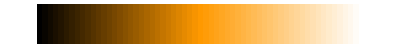

```mathematica
PlotTable[table_,z_,cf_,m_,M_,a_]:=Module[{sizex,sizey},
sizey=Length[table];
sizex=Length[table[[1]]];
Show[ArrayPlot[Reverse[table],ImageSize->Round[z]*sizex,PlotRangePadding->0,ColorFunctionScaling->False,ColorFunction->cf[m,M,a],PlotLabel->"Size: "<>ToString[{sizex,sizey}]<>"; Min/Max: "<>ToString[{m,M}],DataRange->{{1,sizex},{1,sizey}}]
]
];
ColFuncSpot[m_,M_,a_]:=Function[If[#!=0,Green,Opacity[0,White]]];
ColFuncMapS1[m_,M_,a_]:=Function[Blend[{Black,White,Hue[0.1]},((#-m)/(M-m))^a]];
ColFuncMapS[m_,M_,a_]:=Function[Blend[{Black,Hue[0.1],White},((#-m)/(M-m))^a]];
ArrayPlot[{Table[ x,{x,0,1,1/60}]},ColorFunctionScaling->False,AspectRatio->0.1,ColorFunction->ColFuncMapS[0,1,1]]
```

# Part 1 Load experimental data (Cell contains all the numerical data): 1) 400x400pixel Z-map of BSCCO UD20K: “dat” 2) Continuum pixel coordinates of atoms, corner is (0,0): “posCu”, “posOx”, “posOy”

```mathematica
dat={{0.570467,0.514976,0.537377,0.600746,0.673703,0.732882,0.786534,0.810596,0.820027,0.78762,0.700768,0.606276,0.537385,0.502238,0.482215,0.504307,0.562297,0.639873,0.689074,0.717212,0.739807,0.766039,0.785743,0.776,0.732886,0.679143,0.643854,0.622776,0.633824,0.648896,0.681767,0.719668,0.768237,0.820782,0.835516,0.810781,0.75385,0.704053,0.675397,0.67806,0.708367,0.747456,0.767263,0.771553,0.788034,0.825474,0.874987,0.930738,0.978261,1.01588,1.04272,1.06348,1.06206,0.972095,0.819244,0.676635,0.587977,0.555578,0.569845,0.627216,0.693309,0.764288,0.821673,0.836566,0.823467,0.830452,0.86089,0.854306,0.805497,0.756407,0.730377,0.728245,0.724102,0.692255,0.648063,0.596315,0.565335,0.569322,0.629036,0.71393,0.811791,0.923686,0.976413,1.00492,0.9828,0.961404,0.936805,0.910228,0.89531,0.890296,0.894116,0.888929,0.889386,0.905934,0.909295,0.877952,0.8418,0.835314,0.848293,0.861106,0.869559,0.868232,0.875589,0.896791,0.909365,0.901007,0.878218,0.853391,0.829139,0.823471,0.862414,0.951877,1.05954,1.14852,1.2121,1.2292,1.19578,1.14562,1.11611,1.10917,1.09084,1.06251,1.05176,1.03244,0.971278,0.909784,0.895618,0.884108,0.842365,0.788845,0.733177,0.701001,0.704073,0.72566,0.724523,0.731196,0.752181,0.778918,0.799189,0.810036,0.820704,0.824901,0.834837,0.818125,0.783418,0.742686,0.714687,0.707105,0.711954,0.716864,0.706883,0.692059,0.678785,0.684737,0.70536,0.734357,0.759866,0.775359,0.780167,0.804634,0.858838,0.927676,0.990448,1.0425,1.0838,1.1169,1.14737,1.17813,1.19778,1.16854,1.09625,1.02706,0.976517,0.905992,0.815131,0.746057,0.726942,0.760544,0.832824,0.909407,0.964196,1.0333,1.10788,1.11948,1.05378,0.952002,0.856342,0.770514,0.712249,0.693689,0.71271,0.760022,0.807583,0.837166,0.83635,0.827264,0.821003,0.798647,0.771703,0.759977,0.766843,0.779316,0.788167,0.775934,0.757746,0.781585,0.841944,0.873947,0.856188,0.845704,0.844095,0.824257,0.803006,0.794888,0.815347,0.857455,0.895212,0.897247,0.880246,0.906716,0.932042,0.913702,0.84828,0.774444,0.724024,0.706523,0.709525,0.700075,0.706235,0.751082,0.837567,0.936651,1.04821,1.15942,1.23807,1.26815,1.23001,1.1561,1.02378,0.864679,0.729145,0.634816,0.59488,0.596387,0.656437,0.760065,0.925799,1.09677,1.13152,1.05861,0.882922,0.727987,0.625295,0.562339,0.560222,0.586363,0.647199,0.700423,0.754779,0.824688,0.888251,0.942361,0.965594,1.01798,1.02026,0.966829,0.884247,0.825144,0.800656,0.806034,0.819749,0.797317,0.760756,0.756826,0.763841,0.746528,0.711996,0.678097,0.660319,0.636313,0.638756,0.690999,0.781337,0.841618,0.857671,0.892162,0.952607,1.01799,1.05779,1.08218,1.06485,0.998056,0.914191,0.830736,0.767485,0.741493,0.756554,0.783553,0.80302,0.822962,0.854211,0.9151,0.979887,0.990206,0.941717,0.890968,0.859729,0.813258,0.758082,0.726368,0.728589,0.756976,0.79495,0.826068,0.848397,0.884172,0.931848,0.969768,0.99147,1.01255,1.03167,1.04083,1.03478,1.01578,0.99543,0.9814,0.972711,0.965407,0.950429,0.946008,0.931416,0.85948,0.762271,0.680722,0.655433,0.683654,0.750507,0.802986,0.817617,0.850439,0.895934,0.913055,0.900805,0.899401,0.908315,0.901445,0.880465,0.861684,0.848714,0.833855,0.831037,0.85397,0.900412,0.948465,1.00025,1.0693,1.14435,1.19771,1.19906,1.15573,1.08629,1.00908,0.925063,0.835699,0.773261,0.749196,0.778059,0.868811,0.977114,1.02643,1.00083,0.982401,0.983403,0.953038,0.888968,0.82305,0.778611,0.746857,0.733343,0.739688,0.762981,0.796876,0.834669,0.88443,0.934864,0.978431,1.00158,1.01139,1.00822,0.968958,0.907585,0.840387,0.792398,0.784581,0.786278,0.786278,0.786278,0.786278,0.786278,0.786277},{0.570442,0.514973,0.537383,0.60076,0.673711,0.732888,0.78654,0.810595,0.820029,0.787613,0.700762,0.606271,0.537383,0.502237,0.482215,0.504308,0.562297,0.639873,0.689074,0.717211,0.739806,0.766037,0.785743,0.776003,0.732891,0.679147,0.643857,0.622777,0.633823,0.648894,0.681765,0.719667,0.768237,0.820783,0.835516,0.810779,0.753846,0.704049,0.675394,0.678061,0.708372,0.747462,0.767264,0.771553,0.788039,0.825483,0.874999,0.930752,0.97827,1.01589,1.04272,1.06349,1.06205,0.972025,0.81917,0.676578,0.587958,0.555583,0.56988,0.627275,0.693358,0.764348,0.821699,0.836549,0.823454,0.830486,0.860914,0.854241,0.805408,0.756354,0.730365,0.728248,0.72406,0.692157,0.647953,0.596218,0.565324,0.569434,0.629275,0.71422,0.81213,0.923964,0.976531,1.00493,0.982701,0.961308,0.936691,0.910136,0.895266,0.890295,0.894112,0.888913,0.889417,0.905985,0.909263,0.877844,0.841729,0.835318,0.84832,0.861137,0.869563,0.868225,0.875617,0.896828,0.909378,0.900985,0.878191,0.85336,0.829104,0.823472,0.862469,0.951983,1.05963,1.14858,1.21214,1.22918,1.19574,1.14559,1.11611,1.10917,1.09082,1.06249,1.05176,1.0324,0.971214,0.909756,0.895621,0.884081,0.842316,0.788799,0.733141,0.700995,0.704088,0.725671,0.724523,0.731209,0.752201,0.778937,0.799201,0.810044,0.820709,0.824906,0.834836,0.818112,0.7834,0.742671,0.714679,0.707104,0.711957,0.716864,0.70688,0.692054,0.678783,0.684739,0.705366,0.734364,0.759873,0.77536,0.780168,0.804641,0.858854,0.927693,0.990463,1.04251,1.08381,1.11691,1.14738,1.17814,1.19779,1.16852,1.09622,1.02704,0.976502,0.905954,0.815092,0.746034,0.726947,0.760573,0.832871,0.90944,0.964216,1.03336,1.10792,1.11945,1.0537,0.95192,0.856278,0.770449,0.712229,0.693702,0.71276,0.760087,0.807625,0.837176,0.836323,0.827252,0.820982,0.798591,0.771668,0.759984,0.766875,0.779341,0.788159,0.775882,0.757763,0.781754,0.842123,0.873959,0.856113,0.845678,0.844041,0.824154,0.802928,0.794903,0.815476,0.857635,0.895314,0.897191,0.880258,0.906826,0.932101,0.913604,0.848078,0.774265,0.723906,0.706532,0.709502,0.700042,0.706249,0.751196,0.837751,0.936798,1.04845,1.15956,1.23821,1.26812,1.22989,1.15596,1.02344,0.864426,0.728931,0.634722,0.594885,0.596465,0.656678,0.760364,0.926251,1.097,1.1313,1.05824,0.882367,0.727703,0.625105,0.562284,0.560327,0.586517,0.647421,0.700594,0.755002,0.824939,0.888457,0.942504,0.965719,1.01809,1.02012,0.966524,0.883941,0.824973,0.800621,0.80608,0.819731,0.797189,0.760672,0.756835,0.763829,0.746447,0.711886,0.678026,0.660253,0.636265,0.638791,0.691152,0.781508,0.841684,0.857706,0.892227,0.95271,1.01807,1.05785,1.08221,1.06482,0.997986,0.91411,0.830664,0.767435,0.741484,0.756573,0.783565,0.80303,0.822969,0.854231,0.915145,0.979916,0.990193,0.941684,0.890956,0.859719,0.813232,0.758064,0.726364,0.728598,0.75699,0.794963,0.826074,0.848404,0.884188,0.931862,0.969776,0.991474,1.01255,1.03168,1.04083,1.03477,1.01578,0.995427,0.981399,0.972711,0.965407,0.95043,0.94601,0.93143,0.859517,0.762322,0.68076,0.655434,0.683617,0.750453,0.802958,0.817598,0.8504,0.895897,0.913054,0.900814,0.899393,0.908309,0.901457,0.880486,0.861695,0.84873,0.833871,0.831038,0.85394,0.900366,0.948435,1.00019,1.06923,1.14428,1.19768,1.19909,1.15579,1.08638,1.00916,0.925167,0.835796,0.773296,0.749187,0.777955,0.868638,0.976989,1.02646,1.00092,0.982388,0.983418,0.953148,0.889101,0.823147,0.778659,0.746896,0.733331,0.739645,0.762909,0.796793,0.834576,0.884309,0.934768,0.978362,1.00157,1.01139,1.00828,0.969112,0.907745,0.840523,0.792444,0.784549,0.786278,0.786278,0.786278,0.786278,0.786278,0.786278},{0.570415,0.51497,0.537391,0.600775,0.673721,0.732896,0.786547,0.810593,0.820032,0.787605,0.700754,0.606265,0.537381,0.502237,0.482216,0.50431,0.562299,0.639874,0.689074,0.717211,0.739805,0.766037,0.785743,0.776005,0.732895,0.679151,0.643859,0.622777,0.633822,0.648893,0.681764,0.719666,0.768237,0.820784,0.835516,0.810777,0.753842,0.704044,0.675392,0.678062,0.708378,0.747467,0.767265,0.771553,0.788043,0.825492,0.87501,0.930768,0.978278,1.0159,1.04273,1.0635,1.06204,0.971954,0.819094,0.676519,0.587939,0.555588,0.569915,0.627336,0.693409,0.764409,0.821726,0.836532,0.82344,0.83052,0.860937,0.854176,0.805317,0.7563,0.730353,0.72825,0.724017,0.692057,0.647842,0.596119,0.565313,0.569548,0.629519,0.714516,0.812474,0.924247,0.976652,1.00493,0.982601,0.96121,0.936575,0.910043,0.895221,0.890294,0.894108,0.888897,0.889449,0.906035,0.909232,0.877736,0.841657,0.835322,0.848347,0.861168,0.869566,0.868218,0.875645,0.896865,0.90939,0.900964,0.878163,0.853328,0.82907,0.823474,0.862524,0.952089,1.05972,1.14864,1.21218,1.22916,1.19569,1.14555,1.1161,1.10917,1.09079,1.06247,1.05176,1.03236,0.971151,0.909729,0.895624,0.884055,0.842268,0.788753,0.733106,0.700989,0.704103,0.725681,0.724523,0.731221,0.752221,0.778955,0.799213,0.810052,0.820714,0.824911,0.834836,0.818101,0.783383,0.742656,0.714672,0.707103,0.711959,0.716864,0.706877,0.692049,0.678781,0.684741,0.705372,0.734371,0.759879,0.775361,0.780169,0.804649,0.858869,0.927711,0.990479,1.04253,1.08382,1.11692,1.14738,1.17816,1.19779,1.1685,1.09619,1.02703,0.976486,0.905917,0.815052,0.746011,0.726952,0.760601,0.832919,0.909474,0.964236,1.03342,1.10795,1.11942,1.05362,0.951837,0.856212,0.770384,0.712208,0.693715,0.712811,0.760153,0.807667,0.837187,0.836296,0.82724,0.82096,0.798535,0.771633,0.759991,0.766908,0.779366,0.788149,0.775829,0.757779,0.781923,0.842302,0.87397,0.856038,0.845652,0.843986,0.824051,0.80285,0.794918,0.815603,0.857814,0.895416,0.897134,0.880269,0.906936,0.93216,0.913507,0.847879,0.774088,0.72379,0.706542,0.709478,0.700009,0.706264,0.751309,0.837933,0.936944,1.0487,1.15971,1.23834,1.26809,1.22977,1.15582,1.0231,0.864174,0.728717,0.634629,0.59489,0.596543,0.656921,0.760666,0.926705,1.09723,1.13107,1.05786,0.88181,0.727416,0.624914,0.562229,0.560432,0.586673,0.647645,0.700767,0.755227,0.825191,0.888665,0.942648,0.965845,1.01821,1.01997,0.966216,0.883633,0.8248,0.800586,0.806126,0.819712,0.797061,0.760588,0.756845,0.763818,0.746366,0.711777,0.677956,0.660187,0.636216,0.638826,0.691307,0.78168,0.841751,0.85774,0.892294,0.952813,1.01814,1.0579,1.08224,1.06478,0.997915,0.914028,0.830591,0.767385,0.741475,0.756593,0.783578,0.803041,0.822976,0.854251,0.91519,0.979946,0.99018,0.941651,0.890944,0.85971,0.813205,0.758046,0.726359,0.728608,0.757005,0.794977,0.826082,0.848411,0.884205,0.931877,0.969783,0.991478,1.01256,1.03168,1.04083,1.03477,1.01578,0.995424,0.981398,0.97271,0.965407,0.950431,0.946012,0.931442,0.859551,0.762369,0.680794,0.655436,0.683582,0.750401,0.80293,0.817579,0.850361,0.895861,0.913052,0.900823,0.899385,0.908303,0.901468,0.880507,0.861705,0.848746,0.833887,0.831039,0.853909,0.90032,0.948404,1.00014,1.06916,1.1442,1.19765,1.19912,1.15585,1.08647,1.00924,0.92527,0.835894,0.77333,0.749179,0.777851,0.868465,0.976863,1.02649,1.00101,0.982375,0.983433,0.953258,0.889235,0.823243,0.778708,0.746935,0.733319,0.739601,0.762837,0.79671,0.834483,0.884188,0.934672,0.978293,1.00156,1.0114,1.00834,0.969267,0.907904,0.840659,0.79249,0.784518,0.786278,0.786278,0.786277,0.786278,0.786277,0.786277},{0.570385,0.514966,0.537399,0.600792,0.673732,0.732905,0.786555,0.810592,0.820035,0.787594,0.700744,0.606257,0.537378,0.502236,0.482216,0.504313,0.562303,0.639876,0.689075,0.717212,0.739805,0.766036,0.785743,0.776006,0.732897,0.679153,0.643861,0.622777,0.633821,0.648893,0.681764,0.719667,0.768239,0.820785,0.835517,0.810774,0.753837,0.704039,0.675389,0.678063,0.708383,0.747473,0.767265,0.771553,0.788048,0.825501,0.875022,0.930783,0.978287,1.01592,1.04273,1.06351,1.06203,0.971882,0.819016,0.67646,0.587919,0.555593,0.56995,0.627397,0.69346,0.764471,0.821753,0.836515,0.823427,0.830554,0.860961,0.85411,0.805225,0.756244,0.730341,0.728253,0.723972,0.691955,0.647728,0.596018,0.565301,0.569664,0.629768,0.714816,0.812825,0.924535,0.976775,1.00493,0.9825,0.96111,0.936457,0.90995,0.895177,0.890294,0.894104,0.888881,0.88948,0.906087,0.9092,0.877627,0.841586,0.835325,0.848374,0.8612,0.86957,0.868212,0.875673,0.896902,0.909403,0.900942,0.878136,0.853297,0.829035,0.823475,0.86258,0.952196,1.0598,1.14871,1.21222,1.22914,1.19564,1.14551,1.1161,1.10917,1.09076,1.06245,1.05175,1.03233,0.971088,0.909701,0.895627,0.884028,0.842221,0.788707,0.733071,0.700983,0.704118,0.72569,0.724523,0.731233,0.75224,0.778973,0.799224,0.81006,0.820719,0.824916,0.834835,0.818089,0.783367,0.742641,0.714664,0.707102,0.711961,0.716863,0.706874,0.692044,0.678779,0.684744,0.705378,0.734378,0.759886,0.775362,0.78017,0.804657,0.858885,0.927729,0.990495,1.04254,1.08383,1.11693,1.14739,1.17817,1.1978,1.16848,1.09616,1.02701,0.976471,0.905879,0.815012,0.745987,0.726957,0.76063,0.832967,0.909508,0.964256,1.03348,1.10799,1.11938,1.05354,0.951753,0.856146,0.770318,0.712187,0.693728,0.712862,0.76022,0.80771,0.837198,0.836269,0.827227,0.820938,0.798478,0.771599,0.759998,0.766941,0.779391,0.78814,0.775777,0.757796,0.782094,0.842482,0.873982,0.855963,0.845626,0.843932,0.82395,0.802772,0.794932,0.815729,0.857991,0.895516,0.897077,0.880281,0.907044,0.932217,0.913411,0.847681,0.773914,0.723676,0.706552,0.709454,0.699977,0.706278,0.751421,0.838115,0.937088,1.04895,1.15985,1.23848,1.26806,1.22964,1.15567,1.02277,0.863921,0.728504,0.634536,0.594896,0.596623,0.657165,0.760971,0.92716,1.09747,1.13084,1.05748,0.881251,0.727127,0.624723,0.562173,0.560537,0.586829,0.647869,0.700942,0.755454,0.825446,0.888874,0.942793,0.965973,1.01832,1.01983,0.965906,0.883323,0.824626,0.80055,0.806172,0.819693,0.796934,0.760505,0.756854,0.763806,0.746286,0.711667,0.677886,0.660121,0.636167,0.638861,0.691462,0.781852,0.841817,0.857775,0.892361,0.952918,1.01821,1.05796,1.08227,1.06474,0.997844,0.913944,0.830516,0.767334,0.741466,0.756613,0.783591,0.803053,0.822983,0.854272,0.915237,0.979977,0.990167,0.941616,0.890932,0.859699,0.813177,0.758026,0.726354,0.728618,0.75702,0.794991,0.82609,0.848418,0.884222,0.931892,0.969791,0.991483,1.01257,1.03168,1.04083,1.03476,1.01577,0.995421,0.981397,0.972709,0.965407,0.950431,0.946013,0.931452,0.859581,0.762412,0.680827,0.655437,0.683548,0.750351,0.802904,0.817561,0.850324,0.895825,0.91305,0.900833,0.899377,0.908297,0.90148,0.880528,0.861716,0.848762,0.833903,0.83104,0.853879,0.900275,0.948374,1.00008,1.0691,1.14413,1.19762,1.19916,1.15591,1.08655,1.00931,0.925374,0.835992,0.773365,0.749171,0.777747,0.868292,0.976737,1.02651,1.0011,0.982362,0.983446,0.953367,0.889368,0.823339,0.778756,0.746973,0.733307,0.739558,0.762765,0.796627,0.83439,0.884068,0.934576,0.978224,1.00154,1.0114,1.0084,0.96942,0.908063,0.840795,0.792535,0.784486,0.786278,0.786278,0.786278,0.786278,0.786278,0.786278},{0.570353,0.514962,0.537408,0.60081,0.673744,0.732916,0.786564,0.81059,0.820039,0.787583,0.700732,0.606247,0.537374,0.502235,0.482216,0.504318,0.562307,0.63988,0.689076,0.717212,0.739806,0.766037,0.785743,0.776006,0.732897,0.679154,0.643861,0.622777,0.633821,0.648893,0.681765,0.719668,0.768241,0.820788,0.835517,0.810771,0.753831,0.704033,0.675386,0.678065,0.70839,0.747479,0.767266,0.771553,0.788053,0.825511,0.875035,0.930799,0.978296,1.01593,1.04273,1.06352,1.06201,0.971808,0.818938,0.6764,0.587899,0.555598,0.569986,0.627459,0.693512,0.764534,0.82178,0.836498,0.823413,0.83059,0.860984,0.854042,0.805131,0.756188,0.730329,0.728256,0.723927,0.691851,0.647613,0.595916,0.565289,0.569782,0.63002,0.715122,0.813183,0.924827,0.976901,1.00494,0.982397,0.961008,0.936339,0.909857,0.895132,0.890293,0.8941,0.888864,0.889512,0.906138,0.909168,0.877518,0.841514,0.835329,0.848401,0.861231,0.869574,0.868205,0.875701,0.89694,0.909416,0.90092,0.878108,0.853266,0.829001,0.823477,0.862635,0.952303,1.05989,1.14877,1.21226,1.22912,1.19559,1.14547,1.1161,1.10917,1.09074,1.06243,1.05175,1.03229,0.971026,0.909674,0.89563,0.884002,0.842174,0.788662,0.733037,0.700977,0.704132,0.7257,0.724524,0.731245,0.752259,0.77899,0.799235,0.810067,0.820723,0.824921,0.834834,0.818078,0.783351,0.742627,0.714657,0.707101,0.711963,0.716863,0.706871,0.692039,0.678777,0.684746,0.705384,0.734384,0.759893,0.775363,0.780171,0.804665,0.858901,0.927747,0.990511,1.04256,1.08384,1.11694,1.1474,1.17819,1.1978,1.16846,1.09612,1.02699,0.976455,0.90584,0.814972,0.745964,0.726963,0.76066,0.833016,0.909542,0.964277,1.03354,1.10802,1.11935,1.05346,0.951668,0.85608,0.770251,0.712166,0.693742,0.712913,0.760287,0.807753,0.837209,0.836242,0.827215,0.820915,0.798421,0.771563,0.760005,0.766974,0.779416,0.788131,0.775724,0.757814,0.782265,0.842663,0.873994,0.855888,0.845599,0.843878,0.823849,0.802696,0.794946,0.815854,0.858166,0.895615,0.89702,0.880293,0.907152,0.932275,0.913316,0.847487,0.773742,0.723563,0.706563,0.709431,0.699946,0.706293,0.751533,0.838294,0.937232,1.04919,1.15999,1.23861,1.26803,1.22952,1.15553,1.02243,0.863669,0.728291,0.634444,0.594903,0.596704,0.65741,0.761277,0.927616,1.0977,1.13061,1.05709,0.880692,0.726836,0.624529,0.562118,0.560642,0.586987,0.648094,0.701118,0.755683,0.825701,0.889084,0.942938,0.966102,1.01844,1.01969,0.965595,0.883011,0.82445,0.800514,0.806219,0.819675,0.796806,0.760423,0.756864,0.763795,0.746205,0.711558,0.677816,0.660055,0.636118,0.638896,0.691618,0.782025,0.841884,0.85781,0.892428,0.953023,1.01829,1.05802,1.0823,1.0647,0.997771,0.913859,0.830441,0.767282,0.741457,0.756634,0.783605,0.803064,0.822991,0.854293,0.915285,0.980009,0.990152,0.94158,0.890919,0.859689,0.813148,0.758007,0.72635,0.728629,0.757036,0.795006,0.826098,0.848427,0.884241,0.931909,0.9698,0.991488,1.01257,1.03169,1.04083,1.03476,1.01576,0.995417,0.981395,0.972708,0.965406,0.950431,0.946013,0.93146,0.859606,0.76245,0.680856,0.655438,0.683516,0.750304,0.802879,0.817544,0.850287,0.895791,0.913048,0.900842,0.89937,0.908292,0.901491,0.880549,0.861726,0.848778,0.833918,0.831041,0.853849,0.900229,0.948344,1.00003,1.06903,1.14405,1.19759,1.19919,1.15597,1.08664,1.00939,0.925477,0.83609,0.773401,0.749164,0.777645,0.86812,0.976611,1.02654,1.00119,0.982349,0.98346,0.953476,0.889501,0.823435,0.778805,0.747012,0.733296,0.739515,0.762693,0.796544,0.834298,0.883948,0.93448,0.978156,1.00153,1.01141,1.00846,0.969573,0.908221,0.84093,0.792581,0.784454,0.786278,0.786277,0.786278,0.786277,0.786278,0.786278},{0.570275,0.514921,0.537407,0.600836,0.67377,0.732942,0.786594,0.810611,0.82007,0.78759,0.700726,0.606233,0.537362,0.502227,0.482213,0.504323,0.562314,0.639885,0.689077,0.717214,0.739807,0.766038,0.785743,0.776006,0.732896,0.679153,0.643861,0.622777,0.633822,0.648893,0.681766,0.71967,0.768244,0.820791,0.835518,0.810767,0.753825,0.704028,0.675383,0.678066,0.708396,0.747486,0.767267,0.771553,0.788058,0.825521,0.875047,0.930815,0.978305,1.01594,1.04274,1.06354,1.062,0.971734,0.818858,0.676339,0.587879,0.555603,0.570023,0.627522,0.693564,0.764597,0.821807,0.83648,0.8234,0.830625,0.861008,0.853974,0.805036,0.756131,0.730316,0.728258,0.723881,0.691746,0.647495,0.595813,0.565278,0.569903,0.630276,0.715433,0.813546,0.925124,0.977029,1.00494,0.982294,0.960904,0.93622,0.909764,0.895087,0.890293,0.894096,0.888848,0.889545,0.90619,0.909136,0.877408,0.841443,0.835334,0.848428,0.861263,0.869577,0.868198,0.875729,0.896977,0.909429,0.900898,0.878081,0.853234,0.828966,0.823479,0.862691,0.95241,1.05998,1.14883,1.2123,1.2291,1.19554,1.14544,1.11609,1.10917,1.09071,1.06242,1.05175,1.03225,0.970964,0.909647,0.895632,0.883976,0.842128,0.788618,0.733003,0.700971,0.704147,0.725709,0.724524,0.731257,0.752277,0.779007,0.799246,0.810075,0.820728,0.824925,0.834833,0.818067,0.783336,0.742614,0.71465,0.7071,0.711966,0.716863,0.706868,0.692034,0.678775,0.684748,0.70539,0.734391,0.759899,0.775364,0.780172,0.804673,0.858917,0.927765,0.990527,1.04257,1.08385,1.11695,1.14741,1.1782,1.19781,1.16844,1.09609,1.02698,0.976439,0.905801,0.814931,0.74594,0.726969,0.760689,0.833065,0.909576,0.964298,1.0336,1.10806,1.11931,1.05338,0.951583,0.856013,0.770185,0.712145,0.693756,0.712965,0.760354,0.807796,0.837219,0.836215,0.827202,0.820893,0.798364,0.771528,0.760013,0.767007,0.779441,0.788121,0.775671,0.757832,0.782437,0.842844,0.874005,0.855814,0.845572,0.843825,0.823749,0.80262,0.79496,0.815977,0.85834,0.895713,0.896962,0.880305,0.907259,0.932331,0.913222,0.847294,0.773573,0.723453,0.706574,0.709407,0.699914,0.706308,0.751644,0.838472,0.937374,1.04943,1.16013,1.23874,1.26799,1.2294,1.15538,1.02209,0.863418,0.728079,0.634352,0.59491,0.596787,0.657657,0.761586,0.928073,1.09793,1.13038,1.05671,0.880131,0.726543,0.624335,0.562062,0.560747,0.587146,0.64832,0.701295,0.755913,0.825958,0.889296,0.943085,0.966233,1.01855,1.01954,0.965282,0.882698,0.824273,0.800477,0.806265,0.819657,0.796679,0.760341,0.756875,0.763783,0.746125,0.711449,0.677746,0.659989,0.636069,0.638931,0.691774,0.782198,0.84195,0.857845,0.892495,0.953129,1.01836,1.05808,1.08233,1.06467,0.997698,0.913773,0.830365,0.767229,0.741448,0.756655,0.783618,0.803076,0.822999,0.854315,0.915334,0.980041,0.990138,0.941543,0.890906,0.859678,0.813118,0.757986,0.726345,0.72864,0.757053,0.795022,0.826106,0.848435,0.884261,0.931927,0.969809,0.991493,1.01258,1.03169,1.04083,1.03475,1.01576,0.995413,0.981393,0.972707,0.965405,0.95043,0.946014,0.931466,0.859628,0.762484,0.680883,0.655439,0.683486,0.750259,0.802854,0.817527,0.850252,0.895757,0.913046,0.90085,0.899363,0.908286,0.901503,0.880569,0.861736,0.848793,0.833934,0.831042,0.85382,0.900184,0.948313,0.999979,1.06896,1.14398,1.19755,1.19922,1.15604,1.08672,1.00947,0.925579,0.836188,0.773436,0.749157,0.777543,0.867948,0.976485,1.02656,1.00129,0.982336,0.983473,0.953585,0.889634,0.823531,0.778853,0.747051,0.733284,0.739472,0.762622,0.796462,0.834207,0.883828,0.934385,0.978087,1.00152,1.01141,1.00852,0.969726,0.908378,0.841065,0.792626,0.784421,0.786278,0.786278,0.786278,0.786278,0.786278,0.786278},{0.571773,0.516272,0.537845,0.600587,0.673176,0.732189,0.785545,0.809246,0.818306,0.785993,0.700059,0.606536,0.538284,0.503167,0.482779,0.504459,0.562185,0.63964,0.688907,0.717186,0.73993,0.766347,0.786209,0.776419,0.732996,0.678812,0.643268,0.622055,0.633227,0.648494,0.681563,0.719348,0.768598,0.822968,0.839313,0.814797,0.755883,0.703222,0.672325,0.67392,0.703512,0.742264,0.762071,0.767488,0.78644,0.82709,0.879332,0.936666,0.984875,1.0223,1.04778,1.06532,1.05882,0.963364,0.807799,0.664032,0.573951,0.543577,0.564638,0.629212,0.698748,0.771304,0.829138,0.8419,0.825923,0.831496,0.860501,0.84808,0.793399,0.744825,0.724812,0.727906,0.725912,0.697997,0.656413,0.600841,0.56236,0.560774,0.61923,0.705071,0.808385,0.924195,0.976866,1.00587,0.984479,0.965546,0.941835,0.915453,0.898374,0.889426,0.888761,0.880046,0.88018,0.898602,0.903065,0.868743,0.831809,0.828852,0.847493,0.865333,0.874407,0.869277,0.872168,0.891175,0.901464,0.889938,0.864115,0.838038,0.815845,0.815319,0.861709,0.960511,1.07727,1.17089,1.23269,1.24409,1.20601,1.15274,1.11997,1.10717,1.07881,1.04121,1.02853,1.01438,0.957927,0.903032,0.897517,0.891486,0.851409,0.794778,0.733942,0.694941,0.691914,0.71036,0.708824,0.720248,0.745933,0.777088,0.799875,0.812456,0.825734,0.831761,0.843638,0.825015,0.786095,0.740706,0.710235,0.70186,0.706547,0.711456,0.700763,0.686695,0.675186,0.68109,0.699185,0.724896,0.748385,0.764222,0.771194,0.798413,0.854521,0.924589,0.98843,1.04293,1.08788,1.12339,1.15379,1.18317,1.20187,1.17221,1.09976,1.03107,0.979847,0.903935,0.804975,0.730699,0.712294,0.751325,0.83181,0.916496,0.975861,1.0468,1.12031,1.12814,1.05788,0.949905,0.847624,0.757227,0.698763,0.683902,0.708971,0.763284,0.815489,0.845886,0.842355,0.830241,0.822047,0.797909,0.770115,0.757654,0.763814,0.776239,0.785648,0.773377,0.755551,0.78146,0.844127,0.876433,0.858265,0.847941,0.846626,0.828554,0.809502,0.802489,0.822075,0.862349,0.897869,0.897627,0.881166,0.910148,0.936181,0.915344,0.845793,0.769602,0.717738,0.698496,0.69906,0.688827,0.696375,0.743563,0.834233,0.939,1.05822,1.1747,1.25472,1.28014,1.23732,1.16329,1.02672,0.860191,0.718627,0.622852,0.584869,0.590027,0.655436,0.763812,0.935478,1.10984,1.14074,1.06257,0.879198,0.720463,0.617089,0.556784,0.558961,0.587664,0.650745,0.70535,0.760456,0.831154,0.894006,0.945062,0.964302,1.01454,1.01604,0.962556,0.880435,0.819933,0.794338,0.801222,0.817468,0.795237,0.759494,0.758621,0.767817,0.751076,0.714944,0.679031,0.658485,0.631154,0.631887,0.684713,0.777374,0.838358,0.85506,0.892215,0.956546,1.02515,1.06645,1.09121,1.07239,1.00347,0.917269,0.830516,0.763938,0.736405,0.75218,0.780556,0.80156,0.823482,0.856533,0.918208,0.982218,0.991067,0.941519,0.890001,0.858083,0.811356,0.756721,0.726243,0.729763,0.758717,0.796398,0.827037,0.849116,0.884484,0.931512,0.969016,0.990732,1.01195,1.03111,1.04028,1.03425,1.0154,0.995239,0.981326,0.97267,0.965371,0.950435,0.946144,0.931727,0.859908,0.762684,0.681003,0.655514,0.683525,0.750283,0.802897,0.817584,0.850315,0.895837,0.913154,0.900942,0.899409,0.908298,0.901484,0.880525,0.861667,0.848731,0.833879,0.830988,0.85376,0.900138,0.948308,0.999968,1.06895,1.14396,1.19756,1.19925,1.15609,1.0868,1.00952,0.925641,0.836244,0.773445,0.749147,0.777462,0.867822,0.976418,1.02664,1.0014,0.982321,0.983466,0.953656,0.889722,0.823602,0.77891,0.747131,0.733328,0.739484,0.762591,0.796399,0.834116,0.883703,0.934289,0.97801,1.00147,1.01136,1.00853,0.969827,0.908465,0.841135,0.792646,0.784374,0.78626,0.78626,0.786259,0.786259,0.786259,0.786258},{0.618845,0.560949,0.554465,0.592955,0.651811,0.703036,0.74255,0.75091,0.738939,0.710265,0.666616,0.625465,0.598564,0.572813,0.531995,0.518272,0.543659,0.591006,0.629394,0.659242,0.678794,0.698751,0.721483,0.734512,0.724999,0.700532,0.674896,0.655086,0.657038,0.662586,0.688055,0.729165,0.760022,0.770861,0.754669,0.730965,0.715432,0.716336,0.721779,0.737638,0.775954,0.817086,0.832809,0.818938,0.804217,0.806726,0.831288,0.876284,0.92013,0.961274,1.00049,1.05121,1.09285,1.04082,0.900028,0.75939,0.680113,0.632575,0.599629,0.612836,0.662758,0.72919,0.783079,0.807291,0.809366,0.825483,0.864713,0.888059,0.867917,0.811805,0.752744,0.727442,0.715063,0.66283,0.604808,0.570037,0.574977,0.608661,0.680932,0.764104,0.838088,0.930674,0.979863,1.00395,0.975656,0.943849,0.914204,0.88598,0.88007,0.892006,0.914638,0.925176,0.929268,0.936798,0.930503,0.907617,0.874822,0.855755,0.849477,0.847122,0.854155,0.864967,0.887789,0.91709,0.936796,0.937504,0.924727,0.903859,0.870484,0.845684,0.859423,0.919091,0.998122,1.07611,1.15109,1.18802,1.16748,1.12419,1.10233,1.11305,1.1299,1.13685,1.13397,1.09297,1.00994,0.92675,0.889963,0.863467,0.814933,0.769136,0.728298,0.718804,0.745615,0.778725,0.773552,0.759772,0.765299,0.781521,0.797275,0.805268,0.807742,0.803877,0.804632,0.792918,0.773404,0.748795,0.727738,0.722512,0.729272,0.735308,0.727376,0.709272,0.689913,0.696088,0.725189,0.763518,0.793165,0.806729,0.806346,0.824686,0.874771,0.940932,1.00049,1.04332,1.071,1.0963,1.12959,1.16849,1.19224,1.16225,1.08765,1.01483,0.964954,0.910836,0.846046,0.793347,0.772132,0.789525,0.835879,0.885093,0.925113,0.991735,1.07215,1.09368,1.03711,0.952824,0.880863,0.812273,0.756488,0.72512,0.723185,0.74857,0.782805,0.810138,0.817013,0.818532,0.819059,0.801349,0.776543,0.767664,0.777931,0.791096,0.797638,0.783256,0.764074,0.785414,0.840484,0.868226,0.849225,0.839765,0.836813,0.808827,0.779441,0.769824,0.797892,0.850436,0.895346,0.900054,0.880383,0.899374,0.920004,0.904111,0.847626,0.779996,0.735732,0.729741,0.743058,0.736686,0.739142,0.780023,0.855477,0.933372,1.0209,1.11342,1.19095,1.23462,1.2071,1.12758,1.00316,0.873771,0.759665,0.670291,0.623702,0.614549,0.662229,0.75347,0.906191,1.06159,1.0976,1.03918,0.884092,0.74804,0.648128,0.577377,0.563989,0.58387,0.64054,0.68833,0.742206,0.811445,0.876847,0.940208,0.976038,1.03539,1.03197,0.970697,0.88443,0.834651,0.819876,0.823508,0.826832,0.800036,0.761381,0.74994,0.749451,0.728529,0.69874,0.672423,0.663572,0.651052,0.662184,0.716908,0.800792,0.855589,0.867649,0.893135,0.940719,0.993366,1.02667,1.04809,1.03353,0.97255,0.896572,0.827381,0.780242,0.763233,0.776448,0.797257,0.809805,0.820219,0.843028,0.900983,0.969394,0.985559,0.941279,0.895467,0.8685,0.82292,0.764658,0.725283,0.719169,0.744183,0.784979,0.819469,0.843111,0.882456,0.935838,0.977392,0.999055,1.01934,1.03829,1.04722,1.04068,1.02004,0.99759,0.98247,0.973649,0.966341,0.950679,0.944153,0.927277,0.855025,0.759298,0.678949,0.653782,0.681871,0.748615,0.801165,0.815516,0.847413,0.892297,0.909519,0.898007,0.897383,0.907631,0.902747,0.88338,0.865405,0.8526,0.837592,0.834035,0.855482,0.900136,0.94671,0.997205,1.06527,1.1402,1.19525,1.19908,1.15695,1.08782,1.01142,0.928744,0.839424,0.775407,0.749422,0.775893,0.864403,0.972063,1.02294,0.999632,0.98238,0.984721,0.956118,0.89258,0.82519,0.778342,0.744698,0.730081,0.73636,0.760253,0.795298,0.834001,0.883868,0.934246,0.978403,1.0033,1.01411,1.01104,0.972395,0.91185,0.844254,0.793863,0.784995,0.787015,0.787021,0.787026,0.787032,0.787038,0.787044},{0.69212,0.650697,0.615355,0.608038,0.629642,0.659554,0.674538,0.668406,0.658155,0.653765,0.655449,0.657988,0.658087,0.636592,0.588223,0.54277,0.525504,0.536367,0.559415,0.59496,0.62884,0.664712,0.693387,0.711141,0.716011,0.724603,0.723936,0.709332,0.693271,0.685985,0.696772,0.724187,0.73204,0.708166,0.674663,0.66191,0.692923,0.75396,0.80647,0.832079,0.853602,0.872369,0.884244,0.874299,0.849057,0.816904,0.791105,0.795442,0.831364,0.890377,0.952685,1.01975,1.07212,1.06342,0.990815,0.893841,0.820003,0.751614,0.679571,0.629191,0.617716,0.650904,0.70537,0.758798,0.79386,0.825747,0.862355,0.903332,0.92353,0.893724,0.815598,0.743579,0.696009,0.615012,0.546587,0.543804,0.606611,0.675222,0.743233,0.8176,0.871482,0.942275,0.978692,0.990673,0.955375,0.911246,0.878565,0.855008,0.866508,0.903431,0.947362,0.965482,0.966955,0.974667,0.972858,0.968238,0.94389,0.910709,0.86456,0.818296,0.815106,0.857557,0.918031,0.960685,0.993693,1.01797,1.02834,1.01827,0.97708,0.924758,0.892536,0.887044,0.88836,0.908737,0.975323,1.04963,1.07173,1.06219,1.07877,1.14025,1.2203,1.27982,1.28781,1.22109,1.12527,0.996852,0.872364,0.785281,0.72669,0.716521,0.725916,0.773338,0.838061,0.892613,0.911744,0.879451,0.845673,0.809602,0.789479,0.771377,0.749733,0.73852,0.7327,0.74065,0.751843,0.766277,0.7741,0.778568,0.782196,0.783784,0.783768,0.761294,0.726093,0.732539,0.785485,0.861374,0.921403,0.935239,0.906268,0.88605,0.908625,0.956959,1.00581,1.03118,1.03,1.03018,1.05195,1.09201,1.12268,1.10204,1.035,0.962338,0.922951,0.928319,0.95648,0.96956,0.945532,0.899995,0.853297,0.811927,0.797365,0.834241,0.91123,0.974706,0.989503,0.990142,0.990645,0.967,0.914544,0.846532,0.781851,0.721596,0.68871,0.699636,0.738503,0.777644,0.798496,0.800433,0.791193,0.796013,0.814682,0.82472,0.820655,0.80943,0.798949,0.805671,0.82419,0.830448,0.811691,0.803372,0.793675,0.745634,0.698466,0.68301,0.721521,0.788329,0.849193,0.872696,0.860477,0.862251,0.873877,0.880543,0.86987,0.837999,0.816,0.829506,0.856815,0.857394,0.849817,0.866176,0.895257,0.914222,0.930221,0.952258,1.00096,1.07811,1.10879,1.04765,0.955874,0.899769,0.852968,0.800031,0.748633,0.704237,0.701034,0.74135,0.831673,0.930504,0.976272,0.95928,0.875042,0.800849,0.7218,0.640186,0.594763,0.58648,0.617595,0.645383,0.692469,0.750228,0.818504,0.909631,0.9919,1.07449,1.06611,1.00651,0.922192,0.895545,0.89661,0.883639,0.85146,0.817947,0.775535,0.730624,0.697139,0.661207,0.64949,0.655373,0.688829,0.729211,0.774302,0.828987,0.875413,0.911838,0.917041,0.904154,0.886233,0.874178,0.873623,0.881396,0.885493,0.863554,0.833719,0.831362,0.85663,0.881881,0.887097,0.877268,0.852632,0.809084,0.780194,0.813396,0.896311,0.949981,0.941829,0.933473,0.936485,0.902139,0.829046,0.741549,0.675756,0.663374,0.706251,0.758853,0.79821,0.869437,0.967741,1.04017,1.06316,1.0754,1.09247,1.10278,1.0969,1.06433,1.0207,0.989455,0.974217,0.966088,0.945241,0.912254,0.861966,0.782883,0.708673,0.649036,0.6288,0.656314,0.719452,0.768312,0.775773,0.789444,0.817107,0.828379,0.830362,0.848972,0.889962,0.934452,0.960685,0.970395,0.962714,0.944875,0.924643,0.909896,0.903729,0.898727,0.909778,0.946647,1.01814,1.11758,1.18954,1.18281,1.12048,1.07566,1.03386,0.947919,0.84396,0.760184,0.72585,0.754073,0.830116,0.900012,0.940101,0.986396,1.02561,1.033,0.982524,0.876305,0.762319,0.669345,0.630015,0.641462,0.692015,0.76621,0.834902,0.893702,0.936862,0.991585,1.05495,1.09083,1.07914,1.03969,1.00197,0.927264,0.826056,0.8025,0.807172,0.807179,0.807186,0.807193,0.807201,0.807208},{0.76084,0.752135,0.703403,0.643997,0.603063,0.592517,0.586303,0.58416,0.597307,0.623347,0.656217,0.681703,0.69228,0.683535,0.666,0.628748,0.585126,0.559461,0.55715,0.569983,0.589734,0.631128,0.67464,0.703099,0.715209,0.739968,0.755167,0.749026,0.72173,0.70262,0.691793,0.687185,0.682253,0.66521,0.656284,0.666048,0.7123,0.79215,0.885641,0.94647,0.967112,0.956093,0.947871,0.929194,0.88824,0.823841,0.754817,0.705403,0.696077,0.746828,0.837601,0.933933,0.991011,1.0163,1.02653,0.997919,0.936725,0.862773,0.789339,0.694278,0.603531,0.58388,0.637033,0.712191,0.766547,0.818968,0.867225,0.90154,0.91455,0.913505,0.867883,0.766858,0.670875,0.585079,0.545361,0.575299,0.665,0.743531,0.792458,0.845917,0.882629,0.935509,0.953997,0.93616,0.888658,0.842665,0.828982,0.838142,0.880824,0.929512,0.967316,0.975758,0.970109,0.987383,1.00141,1.00288,0.98484,0.960981,0.892487,0.803172,0.780857,0.840746,0.925204,0.978075,1.02748,1.07452,1.09224,1.07878,1.04969,1.01242,0.963645,0.908192,0.852599,0.815667,0.821112,0.867216,0.919522,0.979996,1.06608,1.17598,1.28022,1.34138,1.34839,1.28884,1.21716,1.06561,0.860622,0.715933,0.65127,0.676482,0.737683,0.8261,0.886517,0.936949,1.00456,1.00834,0.964604,0.867521,0.793596,0.737513,0.698788,0.697623,0.707918,0.733372,0.746351,0.770132,0.801236,0.814251,0.805559,0.79572,0.802947,0.787913,0.751921,0.761752,0.829962,0.943121,1.04282,1.06071,0.999875,0.940098,0.939503,0.971286,1.00602,1.01562,0.994446,0.972849,0.969859,0.977709,0.987404,0.981631,0.95585,0.922789,0.917519,0.976143,1.07263,1.14085,1.12062,1.01921,0.895685,0.784099,0.716296,0.709942,0.763891,0.858623,0.957693,1.04517,1.08764,1.07421,1.01744,0.944753,0.863281,0.737098,0.628718,0.612246,0.672022,0.728899,0.752921,0.773948,0.79513,0.82229,0.843932,0.843424,0.824777,0.820278,0.826553,0.820328,0.799749,0.783905,0.766998,0.753589,0.733674,0.681987,0.638476,0.62783,0.661991,0.70224,0.743324,0.782675,0.812122,0.827826,0.849249,0.899761,0.952006,0.970378,0.961514,0.960829,0.959984,0.94923,0.932944,0.921186,0.908365,0.894576,0.866184,0.823694,0.816135,0.876777,0.958838,0.976849,0.944027,0.919764,0.910474,0.908668,0.886008,0.832833,0.782688,0.759251,0.774043,0.814323,0.853617,0.855053,0.823375,0.798103,0.756057,0.700796,0.653119,0.619862,0.617822,0.627787,0.664451,0.701604,0.762811,0.858464,0.965024,1.05804,1.06709,1.0534,0.999951,0.97551,0.956261,0.92359,0.8762,0.845565,0.804188,0.736064,0.677457,0.627702,0.623561,0.653151,0.72475,0.807651,0.870892,0.916301,0.9274,0.950025,0.954498,0.913054,0.841174,0.776874,0.749141,0.745849,0.7665,0.792256,0.821499,0.872877,0.936194,0.986395,0.991273,0.957931,0.899961,0.814873,0.747034,0.751809,0.827931,0.90637,0.943635,0.976917,1.00386,0.987734,0.924032,0.827463,0.734544,0.669595,0.657995,0.698028,0.770221,0.873679,0.979614,1.05619,1.07877,1.0752,1.07566,1.08743,1.09596,1.07512,1.02373,0.957772,0.904794,0.884391,0.879164,0.848793,0.789681,0.721364,0.676291,0.647403,0.640514,0.661064,0.701236,0.73719,0.74822,0.749749,0.754253,0.758694,0.777785,0.810372,0.865699,0.955559,1.041,1.08048,1.06087,1.02498,0.991106,0.964098,0.937827,0.890441,0.852306,0.865373,0.939779,1.04724,1.14048,1.17015,1.14502,1.13614,1.123,1.04798,0.921053,0.786132,0.699761,0.69073,0.758303,0.85485,0.941471,1.01352,1.05322,1.08473,1.0663,0.954602,0.798795,0.649768,0.571098,0.57968,0.661178,0.772167,0.858773,0.921234,0.956913,1.00209,1.07029,1.116,1.10594,1.07714,1.06194,0.983796,0.844793,0.809881,0.816613,0.816613,0.816613,0.816613,0.816613,0.816613},{0.825483,0.830975,0.781938,0.696895,0.596559,0.531063,0.49876,0.50288,0.54376,0.603319,0.655803,0.683881,0.694356,0.704031,0.735703,0.752422,0.729815,0.679096,0.635398,0.591561,0.562529,0.580789,0.637036,0.69662,0.733037,0.756984,0.759189,0.762484,0.749718,0.733043,0.70691,0.674289,0.654446,0.648769,0.677082,0.724536,0.79098,0.871018,0.966903,1.03619,1.06005,1.03794,1.00598,0.961065,0.8989,0.814471,0.729178,0.643294,0.566786,0.570815,0.677802,0.823463,0.915391,0.978883,1.04537,1.07149,1.04333,0.98133,0.906597,0.783727,0.646067,0.570945,0.583514,0.652917,0.728611,0.803394,0.855919,0.874622,0.866489,0.878368,0.877185,0.780474,0.660964,0.602387,0.619729,0.671926,0.744172,0.803728,0.830199,0.857268,0.87076,0.903267,0.907256,0.857555,0.795221,0.75361,0.770661,0.82388,0.904064,0.955596,0.982578,1.01084,1.02234,1.03799,1.03742,1.02431,1.00675,1.00302,0.927857,0.800565,0.752855,0.811439,0.90741,0.977515,1.04742,1.10726,1.12361,1.1057,1.09232,1.08334,1.03966,0.955931,0.867997,0.791765,0.723404,0.700721,0.756103,0.88538,1.03428,1.17602,1.29508,1.35789,1.37487,1.32572,1.25652,1.09127,0.860744,0.69316,0.615569,0.649998,0.743106,0.867192,0.933327,0.979533,1.07176,1.10031,1.06534,0.931108,0.815952,0.731358,0.682212,0.687148,0.707784,0.744637,0.758342,0.778933,0.811999,0.82302,0.807076,0.78571,0.785566,0.77911,0.760955,0.785514,0.864188,0.997435,1.11603,1.13603,1.06843,1.00046,0.997159,1.01465,1.02225,1.00017,0.949798,0.905618,0.886915,0.862999,0.834829,0.83495,0.872106,0.922477,0.979945,1.07623,1.19324,1.2751,1.2567,1.13325,0.969863,0.799535,0.671721,0.63692,0.693578,0.794078,0.905406,1.03409,1.1249,1.13233,1.07474,1.02473,0.960858,0.787408,0.614049,0.567287,0.624925,0.68044,0.703955,0.741944,0.792133,0.843037,0.869739,0.863186,0.832666,0.823864,0.83185,0.816905,0.780263,0.753938,0.734604,0.712817,0.686072,0.639451,0.605384,0.607675,0.640393,0.641634,0.641114,0.680977,0.759495,0.812644,0.866204,0.981595,1.10818,1.18048,1.164,1.12475,1.07366,1.03054,0.996465,0.965377,0.92278,0.8755,0.804334,0.71413,0.659493,0.677027,0.765474,0.868182,0.943575,0.970134,0.974781,0.99398,1.00158,0.978627,0.896187,0.784811,0.705885,0.684253,0.709429,0.736955,0.766523,0.784922,0.78079,0.766327,0.734994,0.695348,0.667917,0.658645,0.676293,0.688819,0.732288,0.809274,0.906669,0.988268,1.02116,1.06262,1.05859,1.03345,0.983701,0.948895,0.91141,0.880762,0.831147,0.753829,0.689777,0.637088,0.63365,0.670402,0.757401,0.850829,0.907849,0.947769,0.952629,0.964402,0.9528,0.892515,0.801034,0.717488,0.674289,0.652759,0.665891,0.718656,0.809045,0.914021,0.99837,1.07239,1.09945,1.05101,0.951294,0.832167,0.747151,0.734343,0.79369,0.873075,0.930763,0.98735,1.03238,1.03964,0.996966,0.90864,0.808142,0.708295,0.650947,0.677399,0.775421,0.894618,0.984456,1.0534,1.08587,1.07534,1.05032,1.05327,1.07495,1.06756,1.00582,0.891849,0.787389,0.742568,0.753436,0.753641,0.721717,0.674977,0.645592,0.652498,0.683689,0.707973,0.714386,0.719495,0.72377,0.723133,0.726076,0.724381,0.742068,0.796519,0.880989,0.976456,1.05413,1.1029,1.10395,1.08228,1.05072,1.02274,0.981569,0.896164,0.811619,0.79398,0.85475,0.947025,1.04265,1.11489,1.14717,1.16928,1.16757,1.11647,1.00558,0.854822,0.73812,0.701311,0.753828,0.860467,0.972039,1.04524,1.06085,1.08695,1.09642,1.01627,0.864709,0.686881,0.573097,0.573303,0.674158,0.800816,0.885803,0.95634,1.00991,1.04442,1.0747,1.1079,1.12909,1.12766,1.10488,0.999139,0.834483,0.794107,0.802056,0.802051,0.802045,0.80204,0.802034,0.802027},{0.859293,0.857615,0.821312,0.745056,0.611087,0.497687,0.437175,0.434409,0.488131,0.576324,0.644411,0.676118,0.707707,0.745822,0.803186,0.86239,0.896656,0.858735,0.7785,0.671702,0.595359,0.575039,0.610994,0.678154,0.735327,0.75549,0.738262,0.745852,0.757651,0.753774,0.729347,0.694813,0.666408,0.653192,0.696,0.783896,0.902987,1.00317,1.06422,1.08183,1.08975,1.08542,1.05649,0.99681,0.928345,0.830513,0.713713,0.597934,0.501228,0.483138,0.57069,0.71647,0.831716,0.927289,1.02067,1.08677,1.11322,1.08928,1.02151,0.89516,0.752807,0.628263,0.56551,0.599167,0.688778,0.773677,0.81347,0.82766,0.826704,0.842409,0.853383,0.77584,0.675942,0.660638,0.726116,0.785118,0.818405,0.844952,0.852039,0.86561,0.863618,0.862513,0.834563,0.75608,0.693936,0.674783,0.733147,0.828292,0.937125,0.991707,1.0088,1.06581,1.10332,1.1091,1.07821,1.04835,1.02313,1.01945,0.941351,0.802064,0.738243,0.780408,0.876136,0.965038,1.04572,1.09906,1.12137,1.12339,1.1127,1.09777,1.07196,1.01103,0.91742,0.808053,0.693851,0.630362,0.671243,0.809801,0.964026,1.10718,1.23854,1.32102,1.35899,1.32055,1.24687,1.08231,0.865945,0.708983,0.633932,0.668076,0.760259,0.889904,0.970121,1.02039,1.09925,1.12021,1.1024,0.987223,0.87416,0.776219,0.71525,0.710937,0.724002,0.761293,0.785397,0.804804,0.818675,0.81584,0.804924,0.779018,0.757369,0.750912,0.75797,0.806942,0.895137,1.0299,1.14933,1.18108,1.13299,1.07003,1.05739,1.04222,1.00975,0.963608,0.905789,0.847403,0.805964,0.758147,0.709252,0.706061,0.777385,0.905764,1.04649,1.18217,1.2862,1.34258,1.3185,1.20033,1.03397,0.837223,0.673127,0.623756,0.68574,0.774358,0.852003,0.972572,1.10134,1.14764,1.10489,1.08221,1.03924,0.843729,0.639415,0.568868,0.603679,0.652669,0.687937,0.733813,0.784632,0.841064,0.875521,0.876362,0.847571,0.834459,0.835451,0.819046,0.782444,0.746422,0.717705,0.694817,0.676251,0.64362,0.616549,0.618401,0.638328,0.616485,0.597369,0.630008,0.727015,0.81779,0.917202,1.07964,1.24379,1.35991,1.34565,1.2759,1.18405,1.1132,1.05602,1.00242,0.931472,0.851913,0.753166,0.644365,0.573641,0.569412,0.643251,0.778123,0.938248,1.02738,1.04912,1.07079,1.08776,1.09093,0.982887,0.794768,0.637155,0.569817,0.586836,0.638288,0.719664,0.777277,0.806692,0.829601,0.824614,0.808189,0.778452,0.751924,0.735922,0.718371,0.733272,0.776209,0.844036,0.895294,0.932586,0.997537,1.03438,1.02555,0.974111,0.960757,0.941698,0.903654,0.833061,0.746835,0.690525,0.65428,0.664163,0.700713,0.772938,0.852107,0.901326,0.938226,0.945314,0.950795,0.929834,0.875199,0.794858,0.708714,0.651166,0.61372,0.617552,0.679275,0.798677,0.92193,1.00126,1.08567,1.1465,1.11054,0.989384,0.854401,0.774135,0.759487,0.800205,0.858467,0.902635,0.956687,1.01194,1.03627,1.0051,0.91625,0.813488,0.726564,0.691332,0.72945,0.820859,0.923121,0.995767,1.05081,1.07573,1.06123,1.02994,1.02683,1.03933,1.0079,0.92289,0.804079,0.71274,0.678689,0.69972,0.728497,0.732601,0.708667,0.679169,0.693847,0.744113,0.766639,0.747942,0.734872,0.739755,0.744053,0.750087,0.743579,0.750694,0.813145,0.911148,0.97871,1.00372,1.04105,1.08554,1.1048,1.08613,1.06186,1.00928,0.897899,0.784102,0.734598,0.769161,0.851993,0.965277,1.07954,1.15847,1.20921,1.21632,1.173,1.0725,0.928797,0.803682,0.730425,0.737846,0.830782,0.968075,1.06688,1.08047,1.08494,1.08223,1.01877,0.903356,0.756886,0.653303,0.64995,0.741242,0.852263,0.919408,0.978767,1.0343,1.06478,1.07339,1.09534,1.12985,1.13814,1.1015,0.97436,0.802165,0.761449,0.769689,0.769685,0.769681,0.769676,0.769671,0.769666},{0.866117,0.866634,0.839393,0.765621,0.61789,0.487529,0.418981,0.411132,0.457171,0.542753,0.615007,0.660614,0.723801,0.793884,0.861797,0.92306,0.985939,0.979126,0.901139,0.77292,0.675157,0.617027,0.607537,0.646001,0.706869,0.737911,0.724907,0.72927,0.738758,0.73253,0.719335,0.707931,0.703163,0.701344,0.757361,0.876307,1.03199,1.13354,1.14202,1.09628,1.07565,1.08178,1.06124,1.00644,0.958203,0.869472,0.721435,0.586215,0.525199,0.526514,0.560993,0.642752,0.749931,0.86067,0.959151,1.05864,1.15442,1.19586,1.15466,1.02356,0.867361,0.703691,0.589256,0.580528,0.647579,0.716833,0.745,0.763562,0.777275,0.789703,0.798759,0.766626,0.729088,0.758896,0.842335,0.890139,0.879885,0.870903,0.860838,0.866897,0.854309,0.816069,0.755799,0.667544,0.624301,0.634706,0.728484,0.850067,0.971213,1.03976,1.05147,1.10225,1.13665,1.14721,1.12594,1.10947,1.0707,1.0291,0.923928,0.786231,0.722823,0.754186,0.852746,0.960653,1.0469,1.08673,1.11238,1.14143,1.13987,1.11377,1.10426,1.07943,0.988945,0.854492,0.729356,0.663015,0.681156,0.776123,0.886955,1.00455,1.13546,1.24127,1.30028,1.27721,1.2172,1.07111,0.874496,0.741167,0.694392,0.741215,0.812153,0.908202,0.985509,1.04038,1.0941,1.10755,1.11573,1.05846,0.986046,0.88402,0.800051,0.763327,0.752773,0.778046,0.807977,0.82556,0.815067,0.793487,0.783206,0.759682,0.729302,0.723725,0.745526,0.810174,0.902456,1.02768,1.14085,1.19848,1.19073,1.13409,1.09407,1.03669,0.970045,0.912751,0.867028,0.809677,0.747678,0.68897,0.645,0.640248,0.703789,0.85139,1.04513,1.21497,1.30023,1.33135,1.31296,1.20279,1.03901,0.865746,0.72949,0.667817,0.687227,0.758854,0.850713,0.96405,1.068,1.12834,1.12457,1.10525,1.04409,0.868174,0.694966,0.615447,0.615306,0.646963,0.689823,0.734498,0.770506,0.815085,0.851367,0.873436,0.867454,0.851166,0.8322,0.812884,0.788754,0.753175,0.719432,0.702553,0.699205,0.685543,0.664269,0.649755,0.644586,0.618871,0.610507,0.638243,0.723938,0.83411,0.965262,1.11704,1.24736,1.37103,1.40476,1.37474,1.29799,1.22913,1.14221,1.04245,0.930105,0.823327,0.718184,0.620778,0.563817,0.561385,0.625662,0.749235,0.918826,1.04103,1.1091,1.16969,1.18328,1.14485,0.984132,0.775763,0.607335,0.522399,0.524527,0.567664,0.653293,0.729331,0.795615,0.859869,0.89544,0.925046,0.909715,0.877309,0.822949,0.771291,0.748623,0.746386,0.777901,0.807048,0.848575,0.909165,0.959664,0.980914,0.962415,0.977791,0.966754,0.922084,0.833347,0.731702,0.676352,0.660078,0.693999,0.731993,0.777421,0.838284,0.891227,0.925698,0.924964,0.925702,0.912547,0.881096,0.82125,0.73164,0.656623,0.61609,0.629811,0.694981,0.802922,0.907399,0.967941,1.0319,1.08874,1.0782,0.994145,0.88793,0.817609,0.791666,0.806836,0.842756,0.878497,0.929821,0.983466,1.00744,0.980436,0.901559,0.816724,0.771477,0.786373,0.840241,0.901317,0.964572,1.01648,1.05436,1.06487,1.05164,1.02741,1.01663,1.00492,0.936009,0.83406,0.74587,0.705502,0.702233,0.729449,0.773074,0.798746,0.793276,0.763287,0.754437,0.778248,0.783779,0.766159,0.768554,0.792905,0.801973,0.796067,0.790912,0.80386,0.845757,0.907593,0.953265,0.974693,1.0086,1.05704,1.09156,1.09085,1.08106,1.03691,0.935283,0.823978,0.754694,0.75291,0.804704,0.900981,1.01172,1.10373,1.17321,1.20197,1.18843,1.12248,1.01169,0.900106,0.811199,0.780606,0.829662,0.935654,1.02975,1.05569,1.04778,1.02041,0.965786,0.903037,0.83403,0.786745,0.789277,0.842013,0.906996,0.947378,0.984573,1.02547,1.06139,1.08477,1.11205,1.13378,1.12955,1.09144,0.959342,0.779161,0.736335,0.745071,0.74507,0.745069,0.745068,0.745066,0.745064},{0.857855,0.877579,0.847344,0.756134,0.609384,0.491539,0.431289,0.422352,0.447341,0.5061,0.581785,0.656391,0.734698,0.818106,0.923262,0.999751,1.04043,1.02563,0.977431,0.871416,0.770147,0.682583,0.630945,0.625159,0.662504,0.69729,0.706456,0.710356,0.706833,0.693738,0.694008,0.710954,0.741318,0.763504,0.83177,0.955286,1.10439,1.207,1.22335,1.17063,1.1269,1.1051,1.05211,0.979478,0.942824,0.882282,0.74403,0.613418,0.582024,0.600531,0.597653,0.61367,0.678649,0.77361,0.874885,1.00883,1.16455,1.26899,1.25602,1.1211,0.954564,0.778193,0.649603,0.601033,0.615519,0.651842,0.677018,0.703428,0.725359,0.735799,0.748036,0.769647,0.803073,0.86584,0.940731,0.983205,0.957079,0.922093,0.881339,0.856883,0.820761,0.754716,0.687081,0.612656,0.598245,0.637478,0.758648,0.896554,1.01544,1.09882,1.11099,1.14054,1.14832,1.15256,1.15049,1.16385,1.11619,1.02485,0.890673,0.7657,0.714398,0.744224,0.843269,0.954938,1.03902,1.06935,1.08262,1.11309,1.14037,1.15215,1.16284,1.14028,1.04305,0.905181,0.799296,0.752672,0.74911,0.786168,0.844307,0.926172,1.03308,1.13962,1.21491,1.21383,1.16695,1.05393,0.907986,0.814478,0.799532,0.843366,0.86625,0.899474,0.947839,0.999403,1.03961,1.06595,1.10171,1.10703,1.09481,1.01793,0.929807,0.848593,0.800168,0.797236,0.815493,0.824289,0.79934,0.762901,0.739626,0.721506,0.706834,0.710266,0.728036,0.786994,0.875004,0.990913,1.09667,1.17836,1.21784,1.17375,1.09819,1.00797,0.935266,0.875759,0.826289,0.758515,0.682419,0.631919,0.619606,0.641622,0.705695,0.836444,1.01724,1.17719,1.25049,1.28767,1.29451,1.18683,1.01377,0.882587,0.813029,0.752259,0.710749,0.754729,0.875372,0.987506,1.04131,1.0953,1.13379,1.09924,0.996625,0.866423,0.764467,0.690379,0.65444,0.658357,0.691949,0.728385,0.753106,0.780509,0.806809,0.847863,0.874076,0.85616,0.808904,0.777634,0.768552,0.754537,0.738841,0.731015,0.729189,0.726785,0.714046,0.68634,0.66249,0.643488,0.65385,0.680367,0.74607,0.846757,0.970051,1.0808,1.16758,1.279,1.36733,1.40971,1.38652,1.34688,1.23326,1.07993,0.924985,0.796054,0.697867,0.632238,0.607372,0.616553,0.670658,0.758213,0.881435,1.00135,1.12596,1.24418,1.24663,1.13173,0.925676,0.753251,0.624096,0.533134,0.505392,0.514471,0.570962,0.646385,0.749056,0.851173,0.924623,0.997306,0.996483,0.964484,0.88486,0.811323,0.757136,0.713641,0.717501,0.745932,0.806373,0.857951,0.903151,0.959061,0.987661,1.01629,0.990688,0.95355,0.873341,0.757241,0.678744,0.65721,0.703609,0.755015,0.799497,0.8459,0.882529,0.905093,0.901923,0.902615,0.899158,0.886534,0.848997,0.776504,0.708749,0.677367,0.697526,0.748397,0.817009,0.888819,0.938043,0.973728,0.997235,1.00207,0.981132,0.933196,0.878109,0.833713,0.818537,0.833304,0.868486,0.922903,0.972535,0.991986,0.973921,0.927209,0.883898,0.872994,0.904991,0.958056,1.0007,1.02825,1.03771,1.04088,1.03794,1.02494,0.998558,0.962749,0.917149,0.841441,0.769722,0.726858,0.723717,0.750426,0.792796,0.840075,0.861708,0.86376,0.844855,0.80991,0.786902,0.776403,0.783824,0.81397,0.855348,0.875395,0.8659,0.864817,0.878391,0.880962,0.884404,0.910733,0.956152,1.00157,1.03718,1.06427,1.07363,1.07769,1.0543,0.98611,0.895525,0.817759,0.784035,0.797959,0.855692,0.931392,1.01224,1.09638,1.16308,1.20523,1.18758,1.0958,0.981408,0.897967,0.867255,0.872382,0.905419,0.957147,0.992386,0.993438,0.963832,0.925086,0.90281,0.89864,0.910771,0.929746,0.948426,0.966879,0.983056,1.00772,1.04185,1.07284,1.0869,1.10857,1.12928,1.11339,1.05462,0.921703,0.763502,0.727151,0.734779,0.734779,0.734779,0.734779,0.734779,0.734779},{0.851459,0.889637,0.853602,0.74762,0.618639,0.526351,0.475598,0.461605,0.460294,0.482054,0.540345,0.627881,0.71782,0.811006,0.943048,1.02632,1.02435,0.981213,0.968391,0.91551,0.832168,0.740302,0.672455,0.630979,0.629631,0.650759,0.678868,0.689903,0.687095,0.678728,0.693548,0.735074,0.78657,0.816529,0.892033,1.02381,1.14445,1.20777,1.23749,1.2172,1.15115,1.07585,0.993709,0.924502,0.898731,0.872665,0.789625,0.693864,0.655626,0.657369,0.652578,0.639108,0.638237,0.69027,0.806352,0.978041,1.16062,1.29243,1.30276,1.19604,1.05798,0.87444,0.71411,0.620191,0.587851,0.588162,0.599085,0.620827,0.646703,0.673198,0.709649,0.777497,0.858925,0.929409,0.9694,1.00925,1.00151,0.964063,0.893768,0.827026,0.76469,0.691389,0.644747,0.603756,0.619552,0.67801,0.806758,0.945589,1.05255,1.14064,1.16246,1.19786,1.1882,1.15584,1.13162,1.15307,1.11543,1.00898,0.870377,0.758338,0.713028,0.737354,0.826721,0.931124,1.01628,1.05426,1.0664,1.08647,1.12048,1.16089,1.18812,1.17003,1.09408,0.98983,0.911766,0.877084,0.859201,0.851444,0.856954,0.884963,0.934691,1.00288,1.07415,1.10765,1.0938,1.03729,0.975933,0.933005,0.923741,0.923186,0.88819,0.861743,0.866771,0.904189,0.944602,0.999826,1.0583,1.09952,1.12695,1.09592,1.04742,0.95303,0.873215,0.827819,0.814186,0.803232,0.774159,0.732383,0.693762,0.680327,0.686038,0.706314,0.72535,0.774642,0.848722,0.952033,1.05506,1.14732,1.20813,1.17601,1.0813,0.96903,0.89747,0.838072,0.777715,0.705723,0.637522,0.606937,0.625388,0.684843,0.771896,0.883057,1.00309,1.10877,1.17712,1.24389,1.28478,1.19171,1.01379,0.894952,0.86057,0.828042,0.785124,0.793684,0.864091,0.944356,0.994895,1.04796,1.08567,1.05498,0.97367,0.904563,0.855865,0.786168,0.721386,0.692372,0.699727,0.716351,0.731051,0.74936,0.767511,0.801327,0.82616,0.806286,0.757787,0.729433,0.734384,0.745393,0.75544,0.758839,0.751872,0.750773,0.744343,0.713503,0.685057,0.677137,0.703294,0.732016,0.779558,0.848206,0.935602,1.02104,1.10785,1.22029,1.32499,1.39027,1.39674,1.39121,1.2767,1.09622,0.919388,0.780595,0.693291,0.656797,0.662085,0.68729,0.727997,0.767942,0.834472,0.939543,1.08588,1.21536,1.20888,1.07882,0.891537,0.763079,0.661332,0.57094,0.514322,0.476423,0.494781,0.570033,0.704225,0.824288,0.90916,0.999499,1.00759,0.982935,0.90365,0.833339,0.769266,0.706472,0.69339,0.717224,0.784148,0.836813,0.882817,0.948243,0.99205,1.02399,0.995839,0.980433,0.921617,0.796887,0.688946,0.649966,0.698937,0.767934,0.8322,0.875918,0.886732,0.892283,0.889855,0.888169,0.885525,0.87833,0.860949,0.830635,0.80303,0.789387,0.79801,0.817011,0.84374,0.886395,0.92854,0.944623,0.942335,0.954311,0.985026,1.01083,1.00895,0.977859,0.930905,0.88506,0.864431,0.879241,0.912734,0.935522,0.941223,0.95086,0.973052,0.996298,1.01963,1.05961,1.09819,1.09768,1.05549,1.01696,0.998157,0.973282,0.933812,0.883444,0.831665,0.777198,0.743563,0.732453,0.745327,0.788331,0.839537,0.872462,0.868677,0.868216,0.871475,0.836525,0.792095,0.780461,0.810072,0.849819,0.885586,0.917505,0.928927,0.934314,0.931307,0.904914,0.876132,0.872169,0.906563,0.963265,1.01743,1.04584,1.04719,1.05702,1.06006,1.02692,0.957502,0.881634,0.831523,0.816208,0.82843,0.842395,0.874856,0.958363,1.08074,1.19161,1.22641,1.17497,1.0855,1.02669,0.999032,0.949711,0.891802,0.865367,0.87214,0.884495,0.892445,0.902306,0.919755,0.951715,0.991032,1.01886,1.02507,1.02318,1.02715,1.04558,1.07415,1.08666,1.07068,1.07358,1.10053,1.08841,1.01406,0.885309,0.758063,0.730629,0.736643,0.736643,0.736643,0.736643,0.736643,0.736643},{0.830615,0.867478,0.840057,0.751175,0.652515,0.580634,0.533569,0.508915,0.483278,0.47447,0.499037,0.573066,0.68648,0.813963,0.943858,1.00575,0.997053,0.95026,0.943274,0.919381,0.858898,0.785846,0.724494,0.659223,0.614158,0.598412,0.620543,0.637464,0.658368,0.680585,0.718809,0.770999,0.820441,0.846166,0.925113,1.07931,1.19658,1.21072,1.21552,1.20952,1.11073,0.983451,0.904949,0.878888,0.876157,0.881524,0.866629,0.827601,0.785509,0.749822,0.726241,0.688206,0.636865,0.63796,0.723485,0.876139,1.0505,1.19829,1.24627,1.20455,1.12519,0.955417,0.771525,0.644901,0.583931,0.549346,0.530729,0.53569,0.564903,0.620389,0.692297,0.779453,0.860989,0.924633,0.950419,0.992329,1.00089,0.971641,0.888458,0.791634,0.71018,0.635014,0.611502,0.616898,0.675899,0.745377,0.846329,0.960151,1.0492,1.13236,1.17064,1.22443,1.21716,1.16026,1.10566,1.11252,1.08038,0.982723,0.864947,0.774789,0.732879,0.741385,0.802777,0.881397,0.953779,0.994915,1.01451,1.03051,1.04504,1.07296,1.11441,1.14402,1.14443,1.10941,1.04921,0.998852,0.980251,0.963144,0.920093,0.86637,0.826718,0.822576,0.85472,0.923245,0.993136,1.04444,1.07996,1.07671,1.05642,0.993726,0.9088,0.837004,0.79968,0.818488,0.858893,0.940434,1.01789,1.07038,1.10211,1.10223,1.1077,1.04611,0.966132,0.878661,0.822583,0.780622,0.74595,0.70554,0.661652,0.651112,0.665263,0.702049,0.739172,0.790174,0.843488,0.919137,1.01268,1.10322,1.16132,1.1441,1.06696,0.937466,0.828383,0.74816,0.698752,0.678888,0.673367,0.666661,0.670541,0.729342,0.836689,0.939292,0.992194,1.00432,1.01183,1.05402,1.11605,1.10596,1.01811,0.946602,0.927259,0.921854,0.904018,0.865934,0.829821,0.846767,0.914458,0.973217,0.991864,0.99672,0.992735,0.977219,0.940017,0.87064,0.797476,0.743899,0.719928,0.709845,0.710959,0.7268,0.743176,0.745857,0.733268,0.712299,0.697103,0.69562,0.712526,0.731002,0.747717,0.76268,0.765457,0.769281,0.764022,0.733027,0.705253,0.705621,0.741125,0.772801,0.807595,0.849257,0.906267,0.972939,1.04787,1.1351,1.21871,1.27462,1.30034,1.334,1.24681,1.06281,0.892057,0.780871,0.729276,0.725316,0.74805,0.765382,0.778608,0.789438,0.814177,0.867002,0.952853,1.03474,1.04489,0.981054,0.875749,0.792402,0.706219,0.626473,0.551818,0.470651,0.456356,0.530682,0.675006,0.789507,0.865475,0.945194,0.956302,0.948834,0.893403,0.843189,0.788357,0.729505,0.705606,0.707056,0.755339,0.819513,0.882769,0.921182,0.929442,0.965329,0.972631,0.978472,0.924382,0.794386,0.679628,0.647835,0.711465,0.779262,0.836029,0.886545,0.908092,0.91459,0.902136,0.878247,0.862911,0.866471,0.885888,0.904624,0.90917,0.899966,0.885108,0.876506,0.877622,0.886147,0.898147,0.89803,0.898523,0.928463,0.994135,1.07501,1.12961,1.13916,1.08425,0.970838,0.865376,0.814834,0.82195,0.851414,0.889836,0.958167,1.03754,1.0892,1.10728,1.13856,1.17362,1.14947,1.06639,0.989668,0.945955,0.893685,0.835874,0.801714,0.791237,0.764101,0.734496,0.744309,0.795745,0.861168,0.898287,0.905498,0.882508,0.870127,0.870886,0.82046,0.758128,0.750094,0.803797,0.86183,0.897918,0.935174,0.957889,0.961817,0.94399,0.915069,0.887682,0.859092,0.852324,0.886418,0.94774,0.987339,0.995794,1.01525,1.03659,1.02621,0.9759,0.914568,0.866021,0.834518,0.811913,0.780177,0.771473,0.840901,0.998203,1.15974,1.2374,1.24289,1.20461,1.16034,1.10526,1.0079,0.892926,0.795115,0.749857,0.75904,0.813268,0.892331,0.966083,1.03005,1.0738,1.0998,1.10619,1.09539,1.08112,1.07376,1.07425,1.0612,1.02805,1.00063,0.987947,0.970559,0.933922,0.855531,0.754828,0.730175,0.735307,0.735309,0.73531,0.735311,0.735312,0.735313},{0.776427,0.774702,0.767082,0.743821,0.707639,0.665009,0.627466,0.590421,0.532546,0.486498,0.471399,0.514903,0.620921,0.757875,0.867704,0.913309,0.931031,0.917612,0.916356,0.898517,0.853814,0.811135,0.773049,0.701707,0.623807,0.561009,0.54956,0.557917,0.606392,0.673903,0.747188,0.797149,0.83725,0.88666,0.958368,1.05847,1.12455,1.11673,1.09441,1.07492,0.988218,0.884131,0.843879,0.864117,0.886015,0.911399,0.940421,0.944663,0.911515,0.852402,0.799762,0.745446,0.686461,0.642059,0.638524,0.715089,0.868414,1.03963,1.13073,1.14424,1.1098,0.990058,0.841944,0.709005,0.615678,0.535202,0.480145,0.475463,0.522412,0.604109,0.690675,0.772743,0.829181,0.869326,0.883877,0.914171,0.923741,0.902863,0.835503,0.745988,0.673809,0.61349,0.610006,0.652253,0.743438,0.808468,0.858365,0.931475,1.0005,1.07073,1.11817,1.17629,1.18601,1.15322,1.10874,1.11093,1.06735,0.960575,0.859381,0.806268,0.777216,0.760329,0.782886,0.826299,0.859758,0.862436,0.846416,0.836972,0.837963,0.870083,0.950861,1.05968,1.15226,1.1859,1.14757,1.08907,1.07971,1.07335,1.00136,0.875212,0.753871,0.681354,0.661528,0.732851,0.876239,1.05141,1.176,1.19552,1.18122,1.08364,0.962107,0.851697,0.777407,0.775139,0.8067,0.901598,0.997713,1.07,1.10813,1.12772,1.17539,1.149,1.08002,0.951808,0.852368,0.760074,0.696208,0.65338,0.620356,0.626139,0.651914,0.694079,0.729128,0.777563,0.830027,0.881945,0.936395,1.00663,1.07383,1.07432,1.00834,0.884374,0.764806,0.678861,0.653185,0.704193,0.780719,0.79429,0.748315,0.762547,0.86216,0.957305,0.971492,0.905593,0.826483,0.799907,0.850659,0.93172,0.992239,1.03848,1.06754,1.06785,1.02562,0.927044,0.819071,0.77514,0.812692,0.867796,0.904586,0.95281,0.996341,1.00755,0.976498,0.918926,0.858813,0.809049,0.775812,0.744132,0.716879,0.705951,0.701433,0.673406,0.639365,0.623596,0.637605,0.665532,0.69987,0.720751,0.72945,0.753588,0.775658,0.786618,0.778228,0.750228,0.727602,0.730571,0.76431,0.79564,0.825223,0.855358,0.895132,0.942554,0.983956,1.02122,1.06332,1.10289,1.14099,1.19439,1.14158,0.979438,0.842059,0.792513,0.809593,0.853919,0.879835,0.850097,0.818269,0.832274,0.833857,0.792609,0.768903,0.798217,0.838806,0.843305,0.823478,0.802144,0.754336,0.693983,0.615238,0.522831,0.489145,0.533292,0.639349,0.730721,0.803954,0.864526,0.876735,0.885134,0.861081,0.836777,0.802368,0.762668,0.739021,0.724976,0.748555,0.803231,0.867472,0.888165,0.876369,0.909249,0.936178,0.946203,0.892865,0.777241,0.681837,0.665816,0.73173,0.777862,0.807303,0.861135,0.911202,0.931114,0.910559,0.868023,0.842568,0.863481,0.924262,0.980736,0.994465,0.970969,0.93158,0.917181,0.913788,0.870601,0.809314,0.776503,0.79879,0.87022,0.971497,1.07321,1.13919,1.17798,1.15377,1.03146,0.883005,0.780616,0.751942,0.780758,0.853785,0.965584,1.07025,1.13373,1.15129,1.16683,1.18052,1.14495,1.0586,0.963776,0.891619,0.815428,0.751913,0.738285,0.767715,0.772936,0.749851,0.772471,0.849541,0.91849,0.927931,0.920021,0.902694,0.883149,0.862288,0.791504,0.721382,0.711584,0.773292,0.85415,0.911565,0.951906,0.961397,0.954368,0.936184,0.92374,0.909735,0.868548,0.820671,0.799754,0.822362,0.864657,0.908877,0.948424,0.974632,0.987658,0.980537,0.959043,0.923461,0.877631,0.819403,0.747404,0.70217,0.727259,0.846792,1.00833,1.13563,1.21005,1.22711,1.21883,1.17324,1.06751,0.91853,0.753206,0.652089,0.652274,0.740749,0.86907,0.980939,1.06568,1.10721,1.12746,1.13855,1.13227,1.11046,1.07332,1.0342,0.996735,0.961237,0.915074,0.862178,0.839206,0.852193,0.833477,0.751618,0.726009,0.730833,0.730832,0.730831,0.73083,0.730829,0.730828},{0.683499,0.663535,0.68919,0.731157,0.751749,0.736087,0.716023,0.679049,0.597722,0.515717,0.466488,0.481096,0.551362,0.664539,0.768534,0.829206,0.8639,0.875118,0.89951,0.905728,0.880044,0.858516,0.833473,0.754747,0.65368,0.560433,0.525563,0.52585,0.587964,0.677259,0.770075,0.819782,0.854565,0.928464,0.980315,0.995103,0.999869,1.00387,0.974371,0.925433,0.867751,0.824429,0.818891,0.856164,0.897813,0.938429,0.980535,1.00895,1.0062,0.962641,0.900208,0.833128,0.769692,0.683792,0.597868,0.591502,0.683374,0.82466,0.936295,1.00524,1.02361,0.982616,0.908075,0.797337,0.682393,0.563188,0.481081,0.475583,0.54009,0.624375,0.691783,0.757445,0.801055,0.824024,0.823983,0.836726,0.836968,0.808367,0.753833,0.684451,0.640173,0.614314,0.639236,0.697545,0.78545,0.850486,0.878943,0.912193,0.942607,0.987814,1.03017,1.07697,1.08958,1.07531,1.04362,1.03646,0.999027,0.919392,0.855975,0.841161,0.82776,0.79184,0.770882,0.765736,0.746326,0.707359,0.662467,0.637406,0.642393,0.692121,0.804223,0.959563,1.09066,1.14631,1.13741,1.11027,1.11552,1.11767,1.05557,0.916051,0.758308,0.644611,0.585136,0.626574,0.773116,1.01081,1.20275,1.25994,1.27547,1.17464,1.04194,0.901645,0.792194,0.764384,0.785578,0.878485,0.970786,1.05633,1.11305,1.15699,1.22823,1.22378,1.17323,1.03632,0.92026,0.773098,0.662722,0.610101,0.591499,0.616365,0.651756,0.685757,0.695183,0.728363,0.791689,0.830928,0.833864,0.876825,0.967381,0.97583,0.879921,0.781689,0.739068,0.715302,0.714924,0.789605,0.899273,0.931427,0.871025,0.848056,0.903561,0.952251,0.926799,0.821327,0.703948,0.651034,0.695162,0.811616,0.952804,1.0839,1.16088,1.17628,1.1167,0.978997,0.835356,0.737235,0.712586,0.751736,0.824047,0.905907,0.962375,0.985243,0.971425,0.938918,0.905965,0.889034,0.873185,0.827933,0.75389,0.686478,0.646448,0.607835,0.583,0.57208,0.587758,0.628667,0.685163,0.718343,0.72381,0.755728,0.7911,0.803765,0.790074,0.767659,0.756531,0.76643,0.79744,0.825584,0.845758,0.858354,0.875308,0.908014,0.936089,0.947242,0.949566,0.957117,0.965504,0.97813,0.948332,0.864383,0.804439,0.816227,0.882842,0.951193,0.971908,0.920038,0.863726,0.86596,0.832858,0.72374,0.631584,0.621555,0.665823,0.706396,0.746559,0.780449,0.784995,0.761194,0.705347,0.641547,0.592413,0.568662,0.597736,0.655321,0.730993,0.782979,0.804521,0.823068,0.820796,0.817566,0.804071,0.787287,0.773464,0.761875,0.767937,0.783677,0.81844,0.856015,0.880062,0.905696,0.907524,0.906511,0.868574,0.795045,0.729668,0.704551,0.731265,0.7535,0.775609,0.816251,0.858612,0.877273,0.869251,0.854967,0.854932,0.876429,0.925044,0.990324,1.02953,1.01811,0.970487,0.95381,0.943777,0.859224,0.744237,0.690072,0.728453,0.824907,0.937663,1.02692,1.06796,1.10414,1.11257,1.03087,0.898556,0.780126,0.72601,0.755809,0.856938,0.985038,1.08369,1.14753,1.16893,1.16201,1.13842,1.09621,1.03312,0.939624,0.842441,0.757004,0.706837,0.691073,0.711582,0.756916,0.800935,0.85202,0.898153,0.92205,0.908596,0.899123,0.895178,0.866797,0.82017,0.754281,0.71051,0.709655,0.760559,0.835463,0.897432,0.940398,0.947145,0.936983,0.921161,0.92606,0.92459,0.874425,0.795721,0.731303,0.714793,0.74259,0.805528,0.867222,0.907455,0.93989,0.964519,0.979461,0.964427,0.915938,0.837322,0.741337,0.672082,0.656958,0.71931,0.851291,1.00917,1.12759,1.17771,1.21774,1.21666,1.12286,0.946229,0.731804,0.594358,0.582995,0.679361,0.817486,0.93885,1.04862,1.11486,1.13715,1.13391,1.12417,1.11242,1.06371,0.986863,0.915367,0.868891,0.822582,0.772311,0.756009,0.779786,0.796389,0.764423,0.751025,0.753305,0.753296,0.753288,0.75328,0.753273,0.753266},{0.583732,0.593068,0.65435,0.720324,0.76116,0.762531,0.771144,0.765729,0.701111,0.604934,0.521203,0.492985,0.509972,0.570411,0.640832,0.710992,0.768766,0.809618,0.860695,0.901508,0.908386,0.906318,0.889583,0.812361,0.706854,0.61023,0.575431,0.575688,0.632902,0.702919,0.784054,0.852349,0.896583,0.949409,0.96133,0.934355,0.903944,0.899806,0.882088,0.852698,0.843246,0.85596,0.871144,0.894057,0.925932,0.955986,0.975744,0.995955,1.0187,1.02027,0.986351,0.923718,0.851751,0.750576,0.641739,0.575597,0.574254,0.639819,0.741168,0.853464,0.930613,0.960264,0.94201,0.867162,0.766401,0.646672,0.560908,0.548516,0.600696,0.658138,0.69289,0.7385,0.774266,0.780118,0.762237,0.759231,0.760165,0.738671,0.705705,0.665483,0.652592,0.666791,0.714722,0.757869,0.801565,0.858022,0.891857,0.899885,0.89079,0.908155,0.932967,0.957428,0.958278,0.942608,0.911612,0.886878,0.869362,0.853796,0.851533,0.859275,0.857481,0.827101,0.760944,0.685773,0.620163,0.579181,0.555818,0.551671,0.576011,0.634983,0.737541,0.872246,0.987178,1.05222,1.09336,1.12697,1.15089,1.14739,1.10302,0.988235,0.835938,0.704316,0.613493,0.613259,0.712037,0.919152,1.1206,1.23474,1.3018,1.23251,1.12212,0.96669,0.829945,0.776189,0.783753,0.856819,0.916579,0.994785,1.07292,1.15062,1.23515,1.24802,1.22007,1.11275,1.02139,0.846174,0.695016,0.626917,0.610184,0.632836,0.656248,0.684051,0.694683,0.71994,0.764279,0.775472,0.749779,0.767034,0.84268,0.84978,0.760226,0.717227,0.7774,0.847376,0.876039,0.927167,1.0019,1.02794,0.988666,0.952005,0.944991,0.925888,0.86839,0.7672,0.669678,0.640627,0.695743,0.801176,0.921905,1.03182,1.099,1.13946,1.12768,1.0186,0.861414,0.715081,0.639071,0.653283,0.732725,0.831183,0.907573,0.954527,0.963118,0.964052,0.968515,0.981036,0.969417,0.907362,0.794531,0.685181,0.624346,0.580901,0.559131,0.546693,0.556848,0.596281,0.661609,0.709858,0.723548,0.753292,0.785009,0.802938,0.8001,0.788403,0.784231,0.798344,0.828185,0.857902,0.868995,0.858093,0.84649,0.862624,0.88686,0.894087,0.87477,0.847981,0.812934,0.775641,0.75781,0.761126,0.792524,0.845943,0.910159,0.952482,0.970403,0.964363,0.923703,0.868148,0.775466,0.660868,0.564962,0.51779,0.535494,0.594138,0.677147,0.741453,0.787216,0.81932,0.809792,0.778282,0.700719,0.610226,0.571105,0.588138,0.646785,0.69167,0.730303,0.761336,0.775042,0.7861,0.78901,0.796248,0.798197,0.796311,0.790029,0.771945,0.774005,0.819953,0.874471,0.890118,0.867742,0.863347,0.84994,0.823845,0.783357,0.73448,0.707884,0.709108,0.734883,0.750101,0.762692,0.777494,0.800598,0.842764,0.889655,0.902098,0.899277,0.943842,1.01764,1.05619,1.03309,1.00618,0.965569,0.862115,0.748752,0.69829,0.731446,0.814846,0.911597,0.986237,1.01518,1.04179,1.05435,0.99681,0.891366,0.781938,0.723816,0.765144,0.892451,1.02423,1.09569,1.13649,1.14902,1.11953,1.06485,1.01379,0.973935,0.90684,0.821712,0.755871,0.729885,0.709168,0.702219,0.75915,0.854826,0.920378,0.916478,0.891172,0.869844,0.864974,0.869623,0.841901,0.79046,0.743259,0.728511,0.738054,0.774366,0.825741,0.872924,0.918586,0.941802,0.944316,0.927595,0.92832,0.919541,0.855988,0.760235,0.68188,0.654689,0.66426,0.715067,0.793879,0.868459,0.916488,0.937324,0.957717,0.95991,0.925592,0.855714,0.763635,0.684933,0.646615,0.674656,0.771601,0.917406,1.04694,1.1157,1.17197,1.18056,1.09331,0.937146,0.762698,0.651613,0.632097,0.696634,0.793905,0.881568,0.981183,1.06141,1.09284,1.08158,1.06745,1.06525,1.02419,0.9423,0.861005,0.813304,0.783022,0.758213,0.752166,0.760767,0.778889,0.792348,0.794434,0.793857,0.793843,0.79383,0.793817,0.793804,0.793792},{0.540251,0.574717,0.642873,0.696821,0.728113,0.738312,0.779187,0.823417,0.803967,0.717978,0.616117,0.543005,0.50596,0.5166,0.543017,0.600045,0.673783,0.743571,0.805277,0.862082,0.900593,0.932512,0.947101,0.897709,0.803118,0.71184,0.677623,0.676322,0.717949,0.753599,0.802688,0.874374,0.924131,0.939263,0.918949,0.894684,0.860492,0.839883,0.84228,0.864564,0.90313,0.941227,0.958586,0.954852,0.952453,0.962375,0.981831,1.00439,1.02087,1.03943,1.04859,1.0149,0.935562,0.817039,0.700857,0.604568,0.543166,0.547726,0.612776,0.723268,0.836391,0.917128,0.93373,0.900141,0.847773,0.775361,0.715248,0.684273,0.684437,0.688645,0.691771,0.720107,0.749918,0.742765,0.711343,0.698777,0.709511,0.712847,0.71414,0.709945,0.721529,0.758637,0.804633,0.830054,0.832775,0.851025,0.860854,0.860532,0.840434,0.829173,0.813364,0.795935,0.778166,0.762661,0.752395,0.741525,0.755418,0.793204,0.842561,0.869633,0.871246,0.847279,0.756219,0.64355,0.567509,0.545669,0.554569,0.581719,0.627571,0.682066,0.745095,0.818512,0.891138,0.966698,1.05759,1.1486,1.20415,1.20271,1.16055,1.0653,0.943034,0.818132,0.699918,0.65298,0.695487,0.828737,0.976554,1.1157,1.23628,1.2336,1.16214,1.0177,0.897399,0.835789,0.818215,0.846605,0.863337,0.917012,0.991345,1.07723,1.14976,1.18286,1.19751,1.15503,1.11369,0.962615,0.803924,0.718349,0.693499,0.68829,0.673175,0.694828,0.734766,0.758678,0.749839,0.719815,0.692383,0.689843,0.718746,0.731474,0.713631,0.748646,0.864191,0.987647,1.04735,1.07666,1.09688,1.08192,1.04105,0.99603,0.949899,0.888089,0.81642,0.738982,0.678297,0.671438,0.721726,0.798757,0.876919,0.940063,0.97905,1.02768,1.06194,1.01029,0.877359,0.719278,0.618375,0.607483,0.670406,0.762513,0.845968,0.909732,0.939265,0.971406,1.00712,1.03375,1.01167,0.932734,0.81321,0.709247,0.65124,0.596416,0.558416,0.537168,0.544983,0.574783,0.62918,0.68529,0.715086,0.732935,0.745335,0.776321,0.807026,0.813787,0.805566,0.80883,0.829708,0.86824,0.886379,0.863334,0.825356,0.818584,0.827491,0.829448,0.801494,0.75101,0.697615,0.658883,0.660652,0.70451,0.787052,0.87022,0.927896,0.942907,0.94521,0.95979,0.92586,0.831985,0.715756,0.62348,0.547132,0.48797,0.483649,0.533765,0.62264,0.697716,0.771885,0.849407,0.876266,0.858618,0.759654,0.645695,0.573801,0.554412,0.580325,0.608087,0.652561,0.693341,0.722572,0.744234,0.758286,0.78255,0.797254,0.805538,0.796567,0.771377,0.758484,0.785867,0.827116,0.829934,0.810076,0.819453,0.827902,0.826172,0.792907,0.731908,0.677897,0.660436,0.678066,0.673566,0.674115,0.703381,0.764154,0.84136,0.906882,0.928805,0.916379,0.933792,0.991172,1.05391,1.07186,1.04677,0.976171,0.866807,0.774046,0.736659,0.760164,0.813259,0.875691,0.940234,0.979237,0.995102,0.983588,0.931446,0.861726,0.790261,0.756675,0.815256,0.951675,1.07375,1.11364,1.11846,1.10922,1.06669,1.00564,0.948349,0.911821,0.873012,0.829601,0.806404,0.810816,0.804949,0.789721,0.818722,0.884452,0.927227,0.911581,0.876375,0.847927,0.834537,0.834914,0.818297,0.786585,0.759431,0.753677,0.76029,0.779876,0.807011,0.83586,0.87127,0.900896,0.924635,0.924778,0.917684,0.889867,0.826206,0.745771,0.67825,0.64937,0.645715,0.674434,0.738541,0.814289,0.864651,0.883175,0.903966,0.918394,0.905406,0.862074,0.797591,0.731728,0.686907,0.695703,0.764754,0.884362,1.0095,1.08717,1.13112,1.1152,1.02126,0.903195,0.808999,0.760985,0.746017,0.766966,0.812428,0.862148,0.932035,1.00222,1.04168,1.03873,1.02043,1.0056,0.965039,0.903874,0.848304,0.818272,0.807778,0.804604,0.807707,0.809206,0.816562,0.833105,0.837908,0.836931,0.836915,0.836899,0.836883,0.836868,0.836854},{0.555279,0.578498,0.62143,0.654825,0.678931,0.702626,0.768942,0.844367,0.852629,0.783727,0.705791,0.63158,0.56091,0.526551,0.512144,0.535664,0.588252,0.659255,0.723413,0.78849,0.848894,0.913468,0.963596,0.956977,0.892433,0.822158,0.788306,0.776592,0.795817,0.812421,0.835892,0.875365,0.902883,0.901808,0.874072,0.849505,0.816107,0.792886,0.819052,0.892335,0.972581,1.02536,1.0493,1.03497,1.00189,0.983196,0.996312,1.01363,1.00423,1.00773,1.0409,1.04642,0.984847,0.869291,0.756753,0.668167,0.6068,0.575697,0.578684,0.640141,0.748018,0.855801,0.902577,0.907821,0.902142,0.880523,0.851933,0.814075,0.771383,0.724807,0.693812,0.692257,0.702339,0.685399,0.658796,0.652028,0.679247,0.717843,0.7654,0.810595,0.845553,0.888159,0.904053,0.911753,0.884444,0.850309,0.818175,0.811969,0.798923,0.770191,0.724151,0.681079,0.65167,0.629128,0.634473,0.6557,0.703627,0.759172,0.827042,0.884226,0.889227,0.844177,0.749794,0.659283,0.606815,0.598731,0.619977,0.655977,0.695876,0.72539,0.750884,0.781918,0.820641,0.884574,0.984,1.1017,1.18943,1.21529,1.198,1.14092,1.06862,0.972215,0.848105,0.752493,0.72148,0.770863,0.851785,0.977327,1.11826,1.18183,1.15805,1.05741,0.995483,0.939928,0.884553,0.856026,0.840054,0.863242,0.903034,0.962037,1.0054,1.06634,1.14886,1.18061,1.1678,1.0536,0.927333,0.839778,0.81226,0.773085,0.709643,0.708694,0.75928,0.7702,0.714269,0.661378,0.643526,0.640382,0.648505,0.678307,0.725924,0.815332,0.940103,1.06887,1.14607,1.16404,1.14238,1.0866,1.02726,0.968659,0.907378,0.840019,0.779754,0.734877,0.707516,0.705549,0.73096,0.777351,0.830593,0.871664,0.896166,0.934983,0.973469,0.956789,0.873047,0.750379,0.65532,0.630585,0.673133,0.738189,0.792755,0.837722,0.87002,0.912133,0.959477,1.00641,1.00286,0.927733,0.81916,0.746322,0.708682,0.649452,0.591265,0.552674,0.550516,0.56392,0.598465,0.649159,0.692408,0.709474,0.712315,0.752114,0.803766,0.822707,0.811441,0.809423,0.822886,0.859966,0.878851,0.852311,0.798555,0.771071,0.75881,0.745447,0.715025,0.66508,0.624099,0.61315,0.640245,0.690589,0.780125,0.884636,0.964541,0.987687,0.960168,0.921349,0.858069,0.780309,0.695386,0.61596,0.549297,0.505339,0.498161,0.520622,0.583362,0.662875,0.758416,0.844236,0.871256,0.857908,0.773207,0.67942,0.602214,0.558738,0.552917,0.555107,0.586373,0.625697,0.66837,0.701435,0.724611,0.751227,0.766642,0.785354,0.787596,0.769365,0.75405,0.76947,0.796574,0.795622,0.782328,0.800336,0.812004,0.801588,0.760146,0.705788,0.659292,0.637204,0.643233,0.632504,0.6334,0.670033,0.744829,0.824099,0.883558,0.929516,0.95295,0.963856,0.977494,1.02159,1.05948,1.04391,0.968514,0.867766,0.790171,0.762034,0.781295,0.806311,0.826713,0.871733,0.916183,0.914101,0.87317,0.835889,0.825972,0.827507,0.851359,0.934822,1.05123,1.12107,1.10159,1.05424,1.0196,0.971762,0.919693,0.878358,0.860527,0.85934,0.869189,0.897364,0.932207,0.948623,0.933059,0.920587,0.918412,0.907148,0.884218,0.855392,0.829082,0.81021,0.803262,0.800079,0.795649,0.783288,0.770017,0.767572,0.77965,0.792927,0.806052,0.823462,0.844578,0.881136,0.904545,0.896456,0.853534,0.801032,0.752564,0.704265,0.671287,0.659934,0.671905,0.694721,0.72739,0.76897,0.812829,0.856693,0.884717,0.886137,0.862813,0.832544,0.801195,0.763406,0.748077,0.783556,0.865007,0.949222,0.999574,1.02725,1.02326,0.979012,0.92522,0.892853,0.886465,0.884075,0.878489,0.872363,0.871369,0.891221,0.927016,0.956392,0.962432,0.953056,0.940281,0.919682,0.89946,0.885652,0.880706,0.891249,0.90954,0.919863,0.912049,0.895483,0.884306,0.882469,0.882935,0.882913,0.882891,0.882869,0.882848,0.882827},{0.604572,0.600461,0.608788,0.623428,0.639507,0.667217,0.738149,0.815972,0.831396,0.781689,0.743793,0.705718,0.642044,0.578644,0.527226,0.511495,0.525152,0.577353,0.645161,0.72687,0.806125,0.894776,0.963405,0.981253,0.944173,0.906959,0.889011,0.871614,0.864854,0.86506,0.869615,0.87466,0.870685,0.860275,0.832657,0.801992,0.778172,0.774154,0.821369,0.912511,0.996368,1.04541,1.08606,1.09639,1.06625,1.02911,1.024,1.03305,1.02283,1.01351,1.02435,1.03187,1.0041,0.935964,0.853805,0.775763,0.710586,0.642885,0.587469,0.590144,0.656166,0.75725,0.837301,0.889782,0.921826,0.937463,0.932281,0.899236,0.839833,0.76514,0.704986,0.662067,0.638653,0.614843,0.60917,0.622075,0.666521,0.732574,0.814537,0.89712,0.949845,1.00785,1.0095,1.00081,0.943513,0.877488,0.80938,0.76584,0.73659,0.704817,0.671479,0.635358,0.613248,0.596827,0.614043,0.655205,0.710795,0.752399,0.795488,0.845367,0.860853,0.82971,0.769793,0.726502,0.709946,0.713858,0.728422,0.741313,0.744825,0.740044,0.744013,0.761191,0.780978,0.810858,0.867132,0.957571,1.05322,1.12766,1.17832,1.19193,1.17208,1.10836,1.01716,0.900146,0.782266,0.741543,0.779997,0.894469,1.01709,1.11329,1.16032,1.13721,1.12492,1.0622,0.978643,0.901781,0.851216,0.835788,0.833756,0.862965,0.887773,0.96211,1.06916,1.13734,1.13997,1.07582,1.01431,0.949167,0.919084,0.856912,0.767659,0.731894,0.753699,0.736853,0.666201,0.620002,0.615579,0.628887,0.649428,0.696788,0.765228,0.859968,0.966573,1.07064,1.13948,1.15659,1.13393,1.08101,1.01703,0.931451,0.842596,0.77594,0.743106,0.739279,0.749084,0.760592,0.769251,0.78616,0.807495,0.812764,0.808628,0.827621,0.865882,0.88303,0.857271,0.798749,0.739847,0.708931,0.714969,0.734426,0.751909,0.771147,0.795816,0.832242,0.874524,0.931575,0.957495,0.909829,0.824234,0.781327,0.767854,0.722401,0.656425,0.599644,0.575812,0.563144,0.575751,0.610762,0.658402,0.691549,0.710523,0.750164,0.788778,0.804528,0.801524,0.817356,0.836894,0.853834,0.842845,0.808498,0.755595,0.719785,0.690634,0.654451,0.624217,0.60414,0.601207,0.613529,0.648314,0.694867,0.777941,0.890831,0.988536,1.01897,0.972789,0.900863,0.816528,0.745291,0.686951,0.631692,0.585794,0.557566,0.544996,0.538834,0.567171,0.632979,0.727286,0.804686,0.827822,0.817863,0.763642,0.709352,0.645159,0.589427,0.556297,0.534889,0.544776,0.567809,0.608278,0.645389,0.676485,0.700713,0.715678,0.744512,0.763559,0.758667,0.750162,0.773163,0.806695,0.817029,0.802714,0.80806,0.797886,0.763549,0.717801,0.681493,0.659399,0.644738,0.64308,0.633607,0.634056,0.65226,0.701154,0.768974,0.837033,0.895654,0.930895,0.953328,0.966026,0.993631,1.01431,0.986145,0.923236,0.871015,0.84595,0.839369,0.842184,0.833024,0.812791,0.818151,0.840031,0.82685,0.788711,0.779983,0.82114,0.885673,0.958035,1.05346,1.13357,1.14021,1.06279,0.964942,0.905399,0.860202,0.826836,0.814198,0.827997,0.867556,0.921699,0.980198,1.01999,1.0499,1.05121,1.03132,0.988974,0.913866,0.84329,0.798309,0.784438,0.778306,0.775145,0.781082,0.790241,0.789432,0.779686,0.784223,0.799192,0.794788,0.777313,0.771858,0.785968,0.817959,0.846416,0.845115,0.814182,0.789121,0.776024,0.757992,0.733119,0.711131,0.69663,0.681868,0.677202,0.697025,0.740054,0.786288,0.823462,0.850599,0.863335,0.870094,0.867168,0.840978,0.811894,0.816015,0.85108,0.877417,0.889066,0.91266,0.947757,0.976724,0.987802,0.981981,0.968942,0.961899,0.955359,0.930214,0.892611,0.867318,0.865411,0.869816,0.872819,0.881675,0.89596,0.908414,0.918293,0.930384,0.945233,0.974795,1.01232,1.02737,1.00652,0.968172,0.939597,0.934366,0.935674,0.935652,0.935631,0.935609,0.935588,0.935568},{0.656026,0.628199,0.613885,0.618499,0.620884,0.630162,0.67878,0.747113,0.786091,0.779752,0.77389,0.757327,0.719616,0.655075,0.579664,0.52905,0.508107,0.532186,0.585385,0.661407,0.737729,0.832219,0.909697,0.945318,0.935126,0.92486,0.924345,0.91765,0.90562,0.897782,0.890065,0.883378,0.862382,0.83379,0.788594,0.74346,0.745079,0.80148,0.893793,0.982754,1.04875,1.08168,1.11284,1.13137,1.11789,1.07822,1.04631,1.02354,1.00097,0.985564,0.979924,0.989675,1.00227,0.99909,0.965571,0.897773,0.813163,0.714133,0.627106,0.581663,0.589124,0.655122,0.754227,0.854832,0.923102,0.973535,0.993419,0.964006,0.889614,0.802334,0.727108,0.64235,0.579771,0.547407,0.566078,0.613195,0.688946,0.775746,0.859273,0.941435,0.992856,1.06462,1.07689,1.05979,0.98476,0.916222,0.83733,0.757598,0.70627,0.682437,0.68436,0.675257,0.674537,0.678144,0.696303,0.722501,0.742143,0.747198,0.746298,0.756558,0.789737,0.829736,0.835047,0.809659,0.796558,0.804632,0.808188,0.798209,0.783077,0.769077,0.763847,0.761868,0.752962,0.741197,0.74045,0.779145,0.863985,0.991572,1.13289,1.24307,1.28555,1.24388,1.17985,1.05569,0.881067,0.767192,0.757484,0.842139,0.932572,1.04824,1.17323,1.23714,1.24941,1.17338,1.0975,0.995485,0.902538,0.837617,0.798823,0.812277,0.835644,0.902223,0.972944,1.03458,1.06825,1.0694,1.06612,1.02831,0.99288,0.925538,0.844601,0.778778,0.751304,0.697063,0.621006,0.590931,0.607579,0.644885,0.68229,0.745128,0.822793,0.901173,0.967116,1.02221,1.06406,1.08733,1.08809,1.04983,0.974047,0.864816,0.769803,0.723866,0.725451,0.759097,0.801878,0.830634,0.831655,0.826204,0.818827,0.787104,0.749109,0.745391,0.783534,0.82727,0.844832,0.84485,0.829928,0.793632,0.752,0.725273,0.72377,0.734801,0.755362,0.787834,0.823275,0.867507,0.89571,0.878416,0.83179,0.812429,0.811787,0.796018,0.747149,0.682856,0.626496,0.56671,0.54355,0.563798,0.623274,0.673688,0.709783,0.752041,0.781395,0.803834,0.817044,0.844675,0.861088,0.860479,0.820287,0.774677,0.720053,0.670982,0.627176,0.579288,0.556478,0.569549,0.607439,0.639202,0.672947,0.71427,0.78633,0.88941,0.975106,0.988214,0.940943,0.892571,0.820793,0.731555,0.674449,0.660614,0.651016,0.622164,0.59008,0.567514,0.571718,0.604559,0.673946,0.753077,0.802052,0.804009,0.764268,0.733982,0.681351,0.620632,0.569264,0.535698,0.525404,0.518833,0.535213,0.560832,0.596699,0.627397,0.65743,0.695648,0.723874,0.73996,0.750845,0.785728,0.821496,0.848579,0.836329,0.814839,0.770437,0.724986,0.692241,0.671668,0.665287,0.658843,0.65546,0.650788,0.651777,0.651317,0.666947,0.713784,0.780789,0.828771,0.849237,0.882394,0.924197,0.954881,0.954959,0.915105,0.874868,0.888027,0.938982,0.965293,0.942138,0.894603,0.837529,0.784355,0.755254,0.738364,0.739589,0.78125,0.864161,0.961728,1.04527,1.12404,1.16145,1.12027,1.00794,0.858427,0.750925,0.711052,0.728757,0.773863,0.829774,0.90293,0.977182,1.03848,1.06739,1.1017,1.12482,1.12016,1.05725,0.916248,0.784111,0.719883,0.726673,0.745079,0.756998,0.772443,0.7836,0.789265,0.789759,0.804223,0.820793,0.806886,0.768699,0.74405,0.747957,0.760501,0.775246,0.786044,0.788383,0.790677,0.793732,0.798845,0.790732,0.758715,0.716383,0.688611,0.679007,0.673832,0.67845,0.694548,0.732223,0.798075,0.86928,0.914199,0.920815,0.907974,0.885581,0.86061,0.836489,0.803417,0.783425,0.80374,0.867451,0.953171,1.02721,1.06744,1.06522,1.05205,1.03674,0.99989,0.941271,0.873991,0.823013,0.785674,0.771809,0.795411,0.845919,0.90762,0.958892,0.995543,1.01609,1.04063,1.07534,1.08855,1.06639,1.02184,0.980636,0.971663,0.973746,0.973726,0.973706,0.973687,0.973668,0.973649},{0.699994,0.66392,0.630631,0.614194,0.594875,0.582816,0.608938,0.673466,0.745144,0.784939,0.798128,0.781034,0.760074,0.712402,0.63667,0.567281,0.524147,0.521684,0.545096,0.591657,0.646586,0.737742,0.836096,0.916992,0.947029,0.955854,0.951889,0.947638,0.935776,0.929317,0.909031,0.8852,0.840251,0.786888,0.731078,0.687341,0.724736,0.852299,0.993418,1.0664,1.11036,1.13787,1.15154,1.1531,1.14763,1.11245,1.05491,0.983275,0.918537,0.901812,0.93678,1.00039,1.04981,1.07109,1.0565,1.00391,0.925672,0.815614,0.702239,0.598997,0.536963,0.563689,0.677598,0.82266,0.922449,0.994054,1.02644,1.00336,0.930958,0.844063,0.756017,0.637973,0.54987,0.51213,0.545577,0.622685,0.731525,0.828412,0.886422,0.944496,0.990796,1.07415,1.11079,1.10081,1.01434,0.9407,0.862812,0.77842,0.722958,0.696063,0.715028,0.740546,0.766918,0.776169,0.775394,0.778314,0.757689,0.720445,0.683232,0.669062,0.716115,0.81703,0.903045,0.909161,0.881003,0.864037,0.842766,0.819908,0.809905,0.807641,0.799966,0.77317,0.732154,0.685562,0.641222,0.637128,0.705669,0.865821,1.07403,1.27451,1.39514,1.37293,1.29764,1.16084,0.996692,0.858732,0.769201,0.775118,0.840459,0.991278,1.16365,1.28108,1.3238,1.2659,1.22402,1.11912,1.00422,0.895101,0.816969,0.800617,0.809549,0.861528,0.905476,0.961816,1.01223,1.04445,1.06292,1.04091,1.00792,0.957328,0.909823,0.832087,0.757381,0.675317,0.603381,0.590179,0.628527,0.68746,0.73216,0.796611,0.874244,0.934555,0.964428,0.979043,0.997507,1.022,1.0319,0.983262,0.881523,0.768465,0.701992,0.698518,0.743416,0.816048,0.881636,0.913999,0.904069,0.882019,0.858922,0.807096,0.744616,0.714284,0.737681,0.797881,0.857471,0.899075,0.902841,0.863434,0.79842,0.73987,0.710811,0.690939,0.686957,0.713257,0.760394,0.810292,0.842015,0.851216,0.841698,0.839815,0.842925,0.858212,0.840132,0.781,0.692666,0.580079,0.514095,0.520621,0.59319,0.647991,0.685917,0.736809,0.7836,0.834917,0.865173,0.881468,0.875559,0.88024,0.848062,0.794971,0.717534,0.635993,0.575886,0.539371,0.537033,0.558834,0.609015,0.666202,0.720781,0.761286,0.808502,0.879762,0.928692,0.914622,0.863211,0.826318,0.7769,0.707226,0.673788,0.693324,0.710582,0.684768,0.641093,0.610719,0.594938,0.591252,0.625145,0.692476,0.760446,0.782991,0.760818,0.741382,0.699186,0.650766,0.598549,0.558251,0.528007,0.494938,0.484295,0.489473,0.521173,0.558324,0.606191,0.648497,0.6803,0.721782,0.758858,0.799404,0.82173,0.857579,0.850695,0.800064,0.730415,0.69757,0.691424,0.67575,0.662821,0.656954,0.657768,0.656457,0.657917,0.660383,0.670252,0.693341,0.725935,0.748162,0.760039,0.786818,0.831954,0.871739,0.890349,0.888224,0.890215,0.934918,1.00266,1.03362,0.996082,0.927103,0.847727,0.751346,0.681338,0.670648,0.723133,0.820159,0.93291,1.03536,1.09603,1.13102,1.12285,1.04972,0.928389,0.763691,0.632289,0.601097,0.666738,0.768594,0.862686,0.949112,1.01048,1.0603,1.09328,1.13312,1.15606,1.15779,1.08701,0.899632,0.726726,0.652893,0.674594,0.713803,0.744695,0.777115,0.79405,0.806982,0.815168,0.823153,0.824242,0.819299,0.797889,0.756593,0.721143,0.699726,0.703587,0.730164,0.76769,0.795357,0.805358,0.818203,0.821751,0.798464,0.753883,0.722646,0.700001,0.65476,0.613443,0.61027,0.663874,0.765303,0.881109,0.961472,0.977859,0.965711,0.937004,0.889371,0.826878,0.746969,0.695291,0.715773,0.807584,0.927233,1.03486,1.11715,1.14707,1.14405,1.11913,1.06781,0.995125,0.900531,0.813781,0.74237,0.707895,0.729644,0.796961,0.896676,0.989449,1.05011,1.06645,1.07172,1.09667,1.11461,1.10793,1.06934,1.00953,0.992976,0.996457,0.99645,0.996443,0.996437,0.99643,0.996424},{0.725694,0.697503,0.648781,0.597393,0.551841,0.530761,0.55163,0.618827,0.707326,0.770928,0.803726,0.797812,0.789607,0.76405,0.71722,0.656749,0.598704,0.575623,0.585444,0.609861,0.631713,0.678331,0.749908,0.849181,0.922253,0.951957,0.944103,0.946311,0.945006,0.949685,0.919396,0.870414,0.79407,0.716771,0.667152,0.650196,0.727038,0.897375,1.06697,1.13259,1.15156,1.16663,1.18677,1.19715,1.18763,1.13424,1.05003,0.943293,0.846678,0.826323,0.895489,1.00834,1.08262,1.09918,1.07637,1.04302,1.00456,0.914779,0.787886,0.638782,0.522105,0.521634,0.645616,0.812528,0.923958,0.993648,1.01919,1.01382,0.974346,0.895267,0.784411,0.644464,0.553466,0.521315,0.563514,0.649858,0.76606,0.867,0.911137,0.942166,0.964303,1.03064,1.07953,1.07934,1.0145,0.964765,0.917589,0.864609,0.824693,0.794433,0.801094,0.831006,0.846615,0.826869,0.7905,0.769631,0.727514,0.669621,0.630118,0.626184,0.679459,0.785889,0.920221,0.99227,0.980855,0.929126,0.871961,0.839966,0.832391,0.831694,0.817552,0.773237,0.716447,0.649477,0.564141,0.510321,0.553461,0.728422,0.967025,1.21967,1.42144,1.46538,1.41409,1.28157,1.1528,0.999366,0.814469,0.722367,0.750907,0.918131,1.10551,1.24907,1.32333,1.30822,1.30707,1.22204,1.12081,0.991821,0.880611,0.817305,0.791311,0.828769,0.880071,0.951789,0.996968,1.01993,1.03595,1.02221,1.00229,0.969122,0.940822,0.859889,0.760086,0.672549,0.618782,0.623675,0.673763,0.744393,0.792757,0.844464,0.902209,0.952218,0.980973,0.977623,0.962869,0.968317,0.976202,0.915054,0.798402,0.704062,0.679589,0.711191,0.780077,0.868676,0.93527,0.96205,0.951925,0.929449,0.902577,0.84541,0.774141,0.72722,0.733918,0.799568,0.885924,0.936371,0.924444,0.890707,0.846757,0.782101,0.712057,0.636113,0.591092,0.604463,0.670688,0.749467,0.804409,0.83594,0.843381,0.856736,0.872223,0.902744,0.898184,0.853797,0.760012,0.626484,0.532954,0.509877,0.560456,0.60596,0.651608,0.709394,0.76772,0.832703,0.871262,0.888744,0.885991,0.916123,0.906895,0.84756,0.743903,0.638271,0.570049,0.548061,0.562928,0.578338,0.617536,0.686669,0.761362,0.803007,0.822343,0.848992,0.856233,0.830598,0.780104,0.730501,0.695338,0.679333,0.692588,0.722422,0.742377,0.730278,0.694521,0.661111,0.625843,0.59427,0.597522,0.636051,0.692667,0.728612,0.734552,0.726739,0.700925,0.681496,0.642165,0.592698,0.54704,0.511124,0.491937,0.476602,0.490553,0.520466,0.568223,0.604223,0.645597,0.717309,0.777706,0.818104,0.819949,0.851018,0.84153,0.769255,0.690388,0.668096,0.682841,0.677664,0.663584,0.655165,0.65433,0.651791,0.654123,0.666587,0.683394,0.692368,0.693947,0.697912,0.707844,0.718167,0.742686,0.783049,0.833609,0.889479,0.940639,0.985783,1.01041,1.01251,0.97449,0.902495,0.817085,0.714343,0.638954,0.642305,0.733272,0.868683,0.994397,1.08941,1.12209,1.10785,1.04937,0.932774,0.796906,0.662283,0.578695,0.581266,0.667602,0.799667,0.920155,1.00391,1.03417,1.06148,1.10102,1.14814,1.16178,1.14961,1.06926,0.875203,0.702244,0.6305,0.654697,0.698949,0.737441,0.783249,0.811509,0.828181,0.833391,0.834904,0.829692,0.834948,0.829984,0.780423,0.714726,0.671044,0.671855,0.70442,0.75456,0.795221,0.80943,0.817201,0.817814,0.809725,0.784478,0.754073,0.707304,0.623737,0.557818,0.56313,0.646197,0.76549,0.893382,1.00676,1.0504,1.02335,0.957031,0.896835,0.832545,0.712734,0.609719,0.62657,0.763426,0.925467,1.04686,1.13536,1.17485,1.18591,1.17634,1.1306,1.05428,0.959572,0.874231,0.790471,0.732484,0.738411,0.805524,0.904066,0.986118,1.0441,1.06991,1.07724,1.09172,1.09929,1.09249,1.05944,1.00265,0.986232,0.989663,0.989668,0.989673,0.989678,0.989683,0.989688},{0.760853,0.729456,0.665844,0.590879,0.527626,0.501969,0.526664,0.598455,0.684864,0.747174,0.792216,0.806218,0.811103,0.803157,0.787839,0.754595,0.701235,0.673887,0.691069,0.707322,0.691407,0.670812,0.677564,0.749644,0.857043,0.918901,0.917343,0.936158,0.952657,0.966616,0.926188,0.860379,0.762365,0.667003,0.62321,0.633777,0.738503,0.915939,1.08768,1.16071,1.17335,1.17814,1.21691,1.25226,1.23012,1.14495,1.04553,0.933303,0.827563,0.79277,0.848954,0.963358,1.05525,1.09666,1.09639,1.09319,1.08932,1.0078,0.864214,0.698039,0.565185,0.539389,0.635248,0.789649,0.909974,0.968015,0.965938,0.981209,0.994369,0.929084,0.798826,0.659618,0.586887,0.569372,0.614996,0.685125,0.77404,0.870837,0.929761,0.95588,0.954559,0.992178,1.03192,1.03043,1.00222,0.997105,1.00025,0.994378,0.977858,0.957367,0.935391,0.928616,0.901239,0.852997,0.790301,0.744806,0.682481,0.610985,0.583615,0.608359,0.683783,0.791803,0.940556,1.0549,1.07038,1.00394,0.919917,0.873605,0.851377,0.833323,0.808004,0.75938,0.703708,0.633818,0.528524,0.442236,0.463033,0.63021,0.856428,1.09738,1.32278,1.45569,1.51252,1.44158,1.32913,1.13271,0.885397,0.727136,0.693589,0.82576,1.01583,1.19383,1.28016,1.28628,1.31967,1.27664,1.20986,1.08443,0.959307,0.86882,0.827605,0.843677,0.86952,0.931227,0.982428,1.00137,0.993007,0.967664,0.954189,0.940189,0.92976,0.867614,0.775893,0.707368,0.683109,0.701138,0.741295,0.79706,0.837081,0.868566,0.899448,0.947237,0.998185,0.997623,0.951837,0.927954,0.929584,0.871731,0.76499,0.701414,0.712649,0.755157,0.80551,0.86745,0.920299,0.951215,0.957495,0.948178,0.921148,0.85615,0.778076,0.730949,0.740419,0.801612,0.87963,0.927785,0.921035,0.901351,0.872216,0.806376,0.712274,0.603841,0.536756,0.538244,0.605664,0.698934,0.775159,0.822256,0.833458,0.856395,0.887316,0.92335,0.919524,0.890502,0.810182,0.689866,0.59267,0.534138,0.538212,0.566864,0.623414,0.679748,0.728545,0.776444,0.812243,0.855229,0.894114,0.951598,0.951284,0.89008,0.783042,0.687419,0.627604,0.601072,0.609819,0.627357,0.66195,0.710073,0.760833,0.794362,0.799635,0.789131,0.770855,0.75912,0.734954,0.692547,0.67078,0.689833,0.731013,0.759236,0.767167,0.755868,0.727212,0.69879,0.656804,0.608101,0.588482,0.604199,0.644533,0.680413,0.702958,0.705805,0.695939,0.699639,0.673416,0.619788,0.568712,0.543409,0.530861,0.506933,0.504776,0.522203,0.559012,0.585373,0.633888,0.721792,0.79003,0.82502,0.814543,0.841302,0.829635,0.752145,0.672188,0.642061,0.656662,0.668911,0.67286,0.664119,0.652128,0.646831,0.652723,0.66574,0.680382,0.686278,0.684751,0.690806,0.701387,0.69706,0.696351,0.719017,0.772572,0.850294,0.932353,0.994313,1.00664,0.991675,0.946588,0.859524,0.764683,0.685219,0.652219,0.689069,0.794463,0.925328,1.0235,1.08235,1.08494,1.04153,0.962347,0.830012,0.69301,0.602547,0.5858,0.625755,0.714891,0.849168,0.96972,1.04001,1.05259,1.06917,1.11204,1.16675,1.17767,1.13864,1.03523,0.858073,0.71277,0.649843,0.66793,0.701886,0.730851,0.778206,0.821238,0.837385,0.827063,0.836888,0.857172,0.858831,0.830884,0.784455,0.738097,0.698175,0.688263,0.709277,0.753846,0.798124,0.819009,0.824736,0.815993,0.803891,0.786369,0.765409,0.722814,0.637404,0.570494,0.588692,0.688672,0.801082,0.898496,0.992375,1.04324,1.02982,0.965429,0.897679,0.825192,0.697688,0.587922,0.605681,0.755818,0.932436,1.05234,1.12708,1.15802,1.17514,1.18759,1.16419,1.10341,1.03158,0.970315,0.89348,0.821077,0.808823,0.862718,0.927358,0.958421,0.996105,1.0484,1.08548,1.09783,1.08196,1.05066,1.01113,0.976736,0.969294,0.971116,0.971129,0.971141,0.971154,0.971166,0.971178},{0.789377,0.741087,0.671047,0.601076,0.538271,0.50643,0.529861,0.59959,0.671681,0.719289,0.760521,0.790776,0.823172,0.844137,0.847607,0.841103,0.833913,0.833021,0.84718,0.842987,0.800789,0.735901,0.694138,0.707469,0.78173,0.842226,0.857605,0.897291,0.931322,0.95008,0.909923,0.848801,0.754031,0.654924,0.61225,0.634271,0.743459,0.911593,1.0797,1.16372,1.1937,1.20307,1.22993,1.24649,1.20612,1.11808,1.03624,0.953909,0.868333,0.824842,0.846388,0.918878,0.991161,1.0446,1.07142,1.09045,1.09788,1.02495,0.89308,0.762472,0.669177,0.626204,0.652126,0.755538,0.873191,0.918116,0.888223,0.913677,0.9681,0.922067,0.79264,0.67435,0.628663,0.630927,0.67964,0.726752,0.778093,0.855579,0.921095,0.950623,0.941698,0.950132,0.966374,0.961943,0.974353,1.02039,1.08415,1.1351,1.15017,1.15702,1.09574,1.02221,0.922041,0.841174,0.759392,0.694652,0.63389,0.573773,0.565878,0.616253,0.720111,0.84412,0.987066,1.08986,1.10995,1.06091,0.982369,0.920901,0.871071,0.827154,0.791873,0.746584,0.6877,0.61623,0.530145,0.462806,0.470514,0.589316,0.765987,0.974161,1.18668,1.375,1.53734,1.55814,1.4822,1.26029,0.995124,0.805807,0.711014,0.767693,0.905263,1.08222,1.18925,1.23388,1.28749,1.27622,1.24623,1.14523,1.03194,0.949068,0.923509,0.907279,0.862092,0.879541,0.943831,0.978213,0.947354,0.903179,0.882928,0.888564,0.91225,0.88629,0.811262,0.766225,0.774771,0.802031,0.820671,0.844791,0.865647,0.882654,0.899397,0.928313,0.963209,0.966973,0.933138,0.899048,0.880052,0.834046,0.768757,0.740263,0.765012,0.805754,0.837376,0.868802,0.900469,0.928768,0.942633,0.933908,0.901481,0.842879,0.782391,0.754394,0.771892,0.811727,0.850646,0.886723,0.902916,0.897148,0.8626,0.795952,0.712058,0.6208,0.563833,0.555563,0.598822,0.673899,0.749107,0.799062,0.812159,0.834518,0.868574,0.918198,0.932442,0.912504,0.829753,0.719533,0.632603,0.566591,0.548203,0.557152,0.60115,0.647083,0.690722,0.728879,0.763872,0.817423,0.878734,0.952443,0.971809,0.936833,0.851656,0.775562,0.722451,0.686773,0.677631,0.686728,0.706703,0.718182,0.728647,0.747537,0.749115,0.72369,0.702221,0.711519,0.723465,0.71293,0.712822,0.743697,0.784393,0.801515,0.79034,0.764576,0.731668,0.707665,0.672396,0.623031,0.592967,0.59618,0.625969,0.654729,0.679699,0.692109,0.692092,0.697324,0.673195,0.625988,0.578309,0.554405,0.547847,0.534432,0.537657,0.552781,0.583596,0.606839,0.646868,0.718165,0.775551,0.801313,0.79682,0.841411,0.850639,0.784315,0.697178,0.650809,0.649189,0.663562,0.678391,0.666174,0.645206,0.643013,0.657923,0.666077,0.671941,0.684958,0.702266,0.722274,0.733706,0.723992,0.707845,0.706445,0.737455,0.797983,0.874449,0.944618,0.971699,0.965107,0.921462,0.826278,0.728548,0.686288,0.719494,0.798931,0.89393,0.979175,1.01733,1.01892,0.990665,0.937509,0.867541,0.762896,0.659237,0.606387,0.622268,0.684776,0.78353,0.905788,0.994299,1.04331,1.06287,1.08539,1.12027,1.16712,1.17474,1.11584,1.00094,0.862246,0.761528,0.704532,0.69849,0.708045,0.72333,0.761419,0.807884,0.832398,0.824299,0.838724,0.865624,0.854613,0.808943,0.777521,0.767227,0.744568,0.723634,0.722887,0.747416,0.7858,0.817321,0.832867,0.821813,0.796603,0.770318,0.754165,0.734628,0.681323,0.635035,0.659852,0.751481,0.838176,0.890665,0.929997,0.961142,0.992366,0.985736,0.908965,0.796547,0.692107,0.642874,0.674684,0.788098,0.932637,1.04149,1.10312,1.12094,1.13197,1.15472,1.16688,1.15494,1.12197,1.07993,1.02734,0.977356,0.956361,0.969515,0.972971,0.949331,0.962825,1.02488,1.07257,1.06978,1.03665,1.00376,0.973907,0.956034,0.953494,0.954294,0.9543,0.954306,0.954312,0.954318,0.954323},{0.776639,0.717145,0.654854,0.599126,0.553616,0.532637,0.556512,0.615655,0.670465,0.702891,0.732496,0.765474,0.811372,0.85673,0.884061,0.907826,0.951126,0.976152,0.968829,0.933596,0.888123,0.8211,0.765845,0.73161,0.737646,0.768283,0.804404,0.858563,0.894847,0.910538,0.871618,0.818159,0.741467,0.660838,0.631481,0.661181,0.765417,0.912811,1.05926,1.14063,1.18967,1.21154,1.21211,1.18989,1.1422,1.07986,1.03006,0.98446,0.930032,0.889871,0.885351,0.911206,0.945086,0.99371,1.04433,1.07675,1.07527,1.01423,0.914617,0.813962,0.746792,0.703883,0.690879,0.743254,0.827759,0.860454,0.831557,0.846607,0.893884,0.870364,0.785123,0.713468,0.695351,0.712945,0.754093,0.774005,0.786353,0.827708,0.876464,0.90695,0.911262,0.909856,0.914632,0.916536,0.955974,1.03464,1.13678,1.21784,1.26106,1.32398,1.25511,1.13206,0.957327,0.833638,0.719158,0.628359,0.578407,0.548993,0.569378,0.638514,0.752095,0.877001,1.02522,1.1443,1.18098,1.13812,1.04719,0.957563,0.877675,0.813963,0.774614,0.739698,0.684875,0.620299,0.575862,0.559113,0.565781,0.620015,0.728968,0.892058,1.06516,1.24724,1.44662,1.54432,1.53581,1.35169,1.11627,0.925556,0.804308,0.781669,0.808254,0.923658,1.06763,1.2022,1.27141,1.25383,1.2457,1.17685,1.09477,1.03444,1.02529,0.981905,0.886658,0.85739,0.897451,0.922398,0.887605,0.845002,0.821933,0.836961,0.879624,0.892223,0.853745,0.836665,0.864691,0.895206,0.900403,0.892197,0.883653,0.887596,0.902138,0.902682,0.889987,0.889293,0.896647,0.881208,0.845534,0.814079,0.799511,0.795911,0.808306,0.845552,0.890724,0.921411,0.932363,0.941281,0.943094,0.912188,0.86568,0.841044,0.844351,0.854831,0.861814,0.864287,0.861436,0.861433,0.864618,0.868704,0.851153,0.791192,0.715233,0.659021,0.636624,0.626253,0.63441,0.669076,0.719651,0.762681,0.787232,0.815265,0.847105,0.905853,0.939087,0.92364,0.836052,0.734496,0.660153,0.605669,0.586718,0.575755,0.590376,0.619574,0.665145,0.711393,0.75712,0.804499,0.852585,0.92519,0.973483,0.984231,0.931445,0.859478,0.797454,0.767726,0.753377,0.730637,0.7117,0.703026,0.703781,0.710618,0.706713,0.684881,0.671009,0.68695,0.718591,0.740798,0.76959,0.810157,0.833256,0.818602,0.783293,0.755569,0.723432,0.689896,0.657621,0.62695,0.609078,0.607401,0.624148,0.642493,0.660443,0.672017,0.670165,0.664132,0.638864,0.605385,0.57356,0.552864,0.552274,0.556438,0.575643,0.597433,0.625515,0.646507,0.668124,0.707704,0.745499,0.761153,0.772044,0.844048,0.888475,0.845715,0.749929,0.690285,0.67014,0.669794,0.676769,0.657912,0.637017,0.642837,0.667491,0.671349,0.669214,0.694739,0.738948,0.771392,0.77822,0.774752,0.765786,0.752626,0.755388,0.790659,0.840565,0.870628,0.867611,0.85632,0.838841,0.789617,0.740264,0.746105,0.818621,0.916697,0.993461,1.02905,1.00848,0.958231,0.903665,0.844061,0.787883,0.726713,0.675083,0.65606,0.68271,0.754465,0.855365,0.947054,0.989426,1.02064,1.05967,1.09198,1.11016,1.1437,1.15685,1.1008,0.990652,0.886387,0.821098,0.762897,0.725531,0.709245,0.716668,0.742159,0.776912,0.817163,0.83735,0.84417,0.836224,0.815705,0.792577,0.78229,0.782057,0.769928,0.748553,0.728959,0.726462,0.747121,0.780556,0.804543,0.802117,0.783307,0.761091,0.747457,0.741801,0.72516,0.711806,0.735363,0.790923,0.834088,0.85412,0.873291,0.901577,0.947394,0.966132,0.900843,0.792845,0.728965,0.736714,0.779524,0.846379,0.935688,1.01316,1.05996,1.07598,1.08351,1.10319,1.13769,1.17336,1.18281,1.16058,1.13798,1.12508,1.10045,1.06447,1.01804,0.972894,0.971101,1.01506,1.04356,1.02057,0.988851,0.983742,0.97925,0.959505,0.952801,0.954137,0.954136,0.954135,0.954133,0.954132,0.954131},{0.746357,0.681301,0.635263,0.596087,0.573269,0.573611,0.598895,0.639257,0.67557,0.696042,0.712245,0.734735,0.765546,0.817957,0.895333,0.978187,1.04039,1.06442,1.06855,1.03683,0.991554,0.925361,0.860656,0.788931,0.733334,0.711315,0.736409,0.785331,0.822771,0.837899,0.809503,0.76902,0.720579,0.673658,0.6663,0.703694,0.805791,0.93549,1.05022,1.11162,1.15636,1.18169,1.17264,1.13913,1.10306,1.06822,1.03747,1.01094,0.982122,0.955698,0.939309,0.926396,0.912971,0.917029,0.940655,0.963262,0.966119,0.946829,0.905216,0.834914,0.771823,0.743116,0.743383,0.764832,0.790459,0.801576,0.79079,0.787703,0.799863,0.802558,0.791541,0.776949,0.775951,0.798898,0.825076,0.820839,0.798635,0.794631,0.809589,0.824349,0.841771,0.84703,0.866777,0.903006,0.969353,1.04894,1.13634,1.21231,1.2724,1.38844,1.33581,1.18677,0.957064,0.799661,0.671986,0.577485,0.546798,0.554603,0.60375,0.673021,0.76348,0.863753,1.01814,1.1826,1.2553,1.20091,1.0719,0.951816,0.862576,0.804079,0.767574,0.741311,0.712198,0.677027,0.652256,0.649656,0.664279,0.697284,0.757245,0.850049,0.942702,1.07304,1.28867,1.4855,1.55273,1.42241,1.25083,1.07973,0.952315,0.857532,0.769607,0.795321,0.920124,1.09897,1.19619,1.20768,1.22048,1.18381,1.14549,1.10583,1.0933,1.03866,0.94804,0.879565,0.855661,0.839342,0.807888,0.788324,0.780709,0.80208,0.839734,0.876241,0.88648,0.900681,0.932878,0.967123,0.98158,0.952195,0.904554,0.881748,0.891388,0.886668,0.858987,0.845818,0.857274,0.866851,0.860499,0.854521,0.857936,0.856374,0.856088,0.888917,0.941847,0.964344,0.946349,0.930621,0.925417,0.891139,0.849954,0.867909,0.935324,0.973068,0.951566,0.920166,0.895659,0.852402,0.8115,0.818617,0.843106,0.807897,0.733257,0.699363,0.7096,0.705812,0.687234,0.679667,0.693965,0.722424,0.761337,0.807381,0.846044,0.897526,0.924317,0.914614,0.850339,0.781586,0.72078,0.660915,0.626671,0.602072,0.601678,0.609118,0.641516,0.687366,0.752206,0.822739,0.880848,0.943464,0.979672,1.0017,0.972924,0.913341,0.849129,0.818584,0.801168,0.7656,0.724834,0.700449,0.685426,0.670576,0.66156,0.65934,0.667998,0.689638,0.728823,0.773349,0.823789,0.865104,0.862296,0.81427,0.755808,0.727326,0.700247,0.659111,0.630833,0.625682,0.629779,0.627104,0.628412,0.634055,0.638923,0.639781,0.63071,0.616844,0.596126,0.576488,0.566284,0.561048,0.569935,0.582627,0.604898,0.627796,0.649585,0.664427,0.675397,0.698759,0.723964,0.731163,0.747502,0.825569,0.887887,0.870203,0.78517,0.729182,0.701333,0.686623,0.679652,0.656958,0.638789,0.644574,0.666108,0.662005,0.656045,0.694138,0.76801,0.824248,0.834472,0.834636,0.82776,0.809025,0.790419,0.794991,0.804944,0.7817,0.740502,0.721253,0.7366,0.762349,0.795793,0.847415,0.91573,0.994252,1.04809,1.05153,0.997569,0.914275,0.837927,0.769976,0.723012,0.700304,0.702088,0.725095,0.770164,0.846737,0.930038,0.980142,0.9845,0.993259,1.02633,1.04733,1.04951,1.0815,1.11569,1.08393,0.993339,0.922637,0.88581,0.826558,0.761713,0.721634,0.71958,0.729196,0.746143,0.783937,0.820715,0.833463,0.816556,0.801796,0.797693,0.794667,0.787376,0.774723,0.755805,0.732229,0.716957,0.71718,0.731461,0.744816,0.749738,0.750858,0.749777,0.747124,0.748132,0.754535,0.764403,0.776046,0.789339,0.799709,0.813294,0.844275,0.882208,0.905765,0.901346,0.869898,0.829865,0.805723,0.815791,0.853469,0.904447,0.950398,0.976056,0.995615,1.0165,1.0284,1.04172,1.07672,1.13274,1.19197,1.22721,1.24047,1.23015,1.18459,1.11992,1.05348,1.00251,0.974983,0.971511,0.965954,0.938961,0.928196,0.952139,0.974266,0.964013,0.957018,0.958131,0.95813,0.958128,0.958127,0.958126,0.958125},{0.756707,0.66135,0.620696,0.61787,0.626393,0.637497,0.655553,0.671134,0.679383,0.676589,0.662943,0.66505,0.689344,0.759436,0.885811,1.02096,1.07919,1.08551,1.12608,1.12409,1.06935,0.991519,0.917488,0.827191,0.74481,0.670734,0.646257,0.672877,0.722446,0.742034,0.725676,0.701664,0.686928,0.683154,0.712911,0.768793,0.841145,0.907843,0.972699,1.022,1.05569,1.07651,1.08308,1.07878,1.07395,1.06469,1.04463,1.01773,0.992093,0.974515,0.961317,0.937119,0.898138,0.850037,0.815591,0.814309,0.836496,0.864416,0.878762,0.865925,0.835174,0.816994,0.813024,0.797392,0.764061,0.724162,0.697515,0.693892,0.715029,0.752165,0.79173,0.813996,0.820002,0.847392,0.865264,0.846064,0.797236,0.75156,0.732948,0.729199,0.756739,0.781376,0.832948,0.912711,1.00159,1.06692,1.11646,1.18565,1.26323,1.40463,1.35305,1.18651,0.92085,0.739868,0.618661,0.540172,0.53198,0.56957,0.636623,0.69487,0.763462,0.852803,1.00272,1.1777,1.27368,1.23043,1.09671,0.961814,0.855986,0.794059,0.765847,0.757759,0.762039,0.764604,0.75414,0.74667,0.766348,0.79914,0.825395,0.84239,0.84579,0.904908,1.10429,1.38155,1.52147,1.45031,1.35532,1.21714,1.08999,0.949465,0.800326,0.752285,0.798157,0.930841,1.05118,1.14761,1.19446,1.18665,1.19818,1.17353,1.14104,1.07813,1.0192,0.920821,0.825507,0.755149,0.712753,0.717912,0.743948,0.784093,0.81094,0.855772,0.908454,0.94771,0.969505,1.00175,1.03977,1.01863,0.951079,0.891875,0.873998,0.865196,0.850885,0.834561,0.828062,0.858366,0.909503,0.933358,0.919552,0.901224,0.900523,0.925525,0.956536,0.947479,0.899524,0.868017,0.873097,0.874765,0.874364,0.922028,0.998079,1.01839,0.967277,0.923956,0.900741,0.83443,0.757076,0.751145,0.803565,0.822067,0.790774,0.777523,0.787696,0.779452,0.747069,0.709884,0.688823,0.687936,0.71475,0.758808,0.805109,0.849191,0.871458,0.888626,0.874076,0.849824,0.801712,0.730923,0.67333,0.640861,0.636926,0.621277,0.627686,0.65612,0.727356,0.829082,0.921273,0.98169,0.983218,0.980513,0.957948,0.926844,0.882834,0.838993,0.813563,0.805259,0.782094,0.734443,0.67259,0.623222,0.60932,0.628921,0.67119,0.713444,0.761852,0.812217,0.859783,0.886826,0.870224,0.820831,0.74469,0.681595,0.644922,0.624763,0.627099,0.642845,0.655986,0.650614,0.633908,0.619034,0.606378,0.598988,0.591287,0.579281,0.566097,0.553846,0.555164,0.563507,0.583579,0.604519,0.625385,0.640535,0.651681,0.664402,0.678564,0.69972,0.719685,0.726043,0.739103,0.796739,0.84582,0.842817,0.787028,0.752049,0.727412,0.702189,0.681274,0.6591,0.64389,0.638077,0.644089,0.634975,0.635863,0.681299,0.771387,0.85623,0.883317,0.877909,0.849761,0.821279,0.793614,0.762663,0.725904,0.676423,0.640675,0.636037,0.677144,0.758743,0.857263,0.946916,1.00367,1.03631,1.03552,0.999452,0.928727,0.824182,0.732663,0.678916,0.667178,0.692207,0.742432,0.797916,0.847006,0.907726,0.964065,0.993791,0.990777,0.975718,0.965883,0.946587,0.934396,0.969056,1.02489,1.02984,0.975731,0.942019,0.932687,0.887313,0.814951,0.759167,0.742416,0.735805,0.73758,0.750619,0.772565,0.802875,0.822783,0.828968,0.819299,0.808606,0.797486,0.779465,0.758384,0.746358,0.737637,0.717997,0.693291,0.671374,0.665075,0.678219,0.708304,0.735798,0.759323,0.796282,0.83228,0.839219,0.820009,0.807046,0.801041,0.787456,0.776731,0.776851,0.79477,0.833892,0.880128,0.908922,0.922309,0.951631,0.983711,0.975837,0.933901,0.904078,0.910504,0.932356,0.965715,1.02152,1.09404,1.17836,1.24619,1.28026,1.26822,1.21762,1.15422,1.08482,1.02261,0.957307,0.900549,0.869189,0.857729,0.87447,0.91256,0.950439,0.961344,0.959953,0.959809,0.959808,0.959807,0.959805,0.959804,0.959802},{0.78194,0.686348,0.648503,0.674838,0.707097,0.714685,0.715645,0.70576,0.682234,0.647646,0.595398,0.575563,0.609641,0.712318,0.864445,1.01671,1.08725,1.09068,1.13915,1.14971,1.10334,1.0419,0.983618,0.901199,0.81575,0.716845,0.648445,0.638939,0.677131,0.687935,0.677339,0.667168,0.673102,0.695139,0.749812,0.815278,0.841624,0.826669,0.840375,0.894791,0.925606,0.931323,0.951367,0.981565,0.998279,1.00854,1.02312,1.02343,0.999508,0.979939,0.97375,0.94721,0.887822,0.790778,0.699086,0.67468,0.720073,0.792162,0.847474,0.884021,0.895265,0.887174,0.862949,0.812793,0.744239,0.656566,0.598737,0.609605,0.673786,0.735121,0.771856,0.797242,0.812118,0.853475,0.875238,0.84824,0.775124,0.692667,0.648874,0.639053,0.682745,0.734198,0.816884,0.919398,1.01145,1.07895,1.10899,1.15626,1.21341,1.33494,1.29318,1.14107,0.882549,0.700006,0.596988,0.544757,0.559001,0.612108,0.676203,0.712584,0.765265,0.852844,0.969441,1.08423,1.15531,1.14892,1.08155,0.98798,0.875192,0.78984,0.769476,0.793289,0.811127,0.82358,0.851458,0.882977,0.902422,0.898468,0.880737,0.838018,0.767923,0.75549,0.895146,1.17576,1.36927,1.39769,1.41149,1.32771,1.20184,1.02772,0.85586,0.755054,0.725458,0.797414,0.908891,1.05805,1.14514,1.17693,1.22905,1.22171,1.18796,1.11989,1.08075,0.959546,0.815313,0.700348,0.642048,0.658963,0.710479,0.775132,0.801872,0.849073,0.924439,0.978266,0.993579,1.02156,1.07474,1.08298,1.03176,0.937938,0.858697,0.806256,0.786728,0.787489,0.801194,0.854387,0.930564,0.972846,0.960798,0.942281,0.943554,0.951991,0.946385,0.898142,0.825708,0.787884,0.809512,0.853392,0.898482,0.964885,1.02424,1.01937,0.953966,0.899128,0.866171,0.793188,0.71194,0.700921,0.764386,0.836666,0.868403,0.870338,0.84782,0.819181,0.787637,0.746789,0.707445,0.672894,0.664138,0.679648,0.71923,0.760829,0.796783,0.853733,0.887545,0.890713,0.848964,0.791107,0.735327,0.696816,0.679306,0.648726,0.638069,0.642286,0.688793,0.772362,0.866855,0.935056,0.946126,0.941371,0.923108,0.913971,0.898242,0.864912,0.842291,0.849941,0.833306,0.768323,0.672436,0.593504,0.570788,0.606329,0.678679,0.741369,0.796978,0.84342,0.87622,0.887343,0.863035,0.81853,0.730044,0.629843,0.581451,0.593798,0.637344,0.666534,0.675724,0.665524,0.634792,0.60312,0.579625,0.571298,0.572593,0.569879,0.56388,0.551843,0.550455,0.560311,0.586151,0.616781,0.641061,0.647193,0.648844,0.665608,0.688843,0.708242,0.723371,0.739312,0.754535,0.782645,0.80011,0.802612,0.776577,0.761441,0.738497,0.700728,0.662981,0.642222,0.63374,0.610297,0.597475,0.605102,0.64366,0.702249,0.774641,0.84368,0.870553,0.872338,0.848006,0.820416,0.781762,0.716723,0.647606,0.597657,0.587827,0.607783,0.67247,0.789823,0.922344,1.03012,1.06653,1.03962,0.9756,0.900179,0.814852,0.696573,0.602603,0.580906,0.623135,0.7037,0.792785,0.859877,0.88971,0.920396,0.960346,0.996061,1.00125,0.958507,0.8882,0.817033,0.786919,0.808165,0.86531,0.904652,0.905939,0.927647,0.958411,0.951065,0.898368,0.840214,0.802609,0.774857,0.760659,0.743515,0.735601,0.760736,0.802867,0.824805,0.814885,0.808152,0.805194,0.788987,0.765856,0.762514,0.759325,0.727099,0.676241,0.625049,0.598649,0.607418,0.657925,0.721519,0.779442,0.840087,0.884734,0.890843,0.861219,0.837747,0.804741,0.724083,0.645918,0.63248,0.696767,0.800871,0.90805,0.993616,1.03866,1.0708,1.07224,1.00475,0.896963,0.802822,0.773293,0.806029,0.883287,0.991022,1.0968,1.17563,1.21163,1.24815,1.28838,1.28917,1.23386,1.13487,1.03214,0.914472,0.8091,0.765321,0.781125,0.831557,0.882008,0.929598,0.957829,0.961576,0.960325,0.960327,0.960329,0.960332,0.960334,0.960336},{0.770685,0.742207,0.727726,0.73805,0.762613,0.775899,0.778185,0.755663,0.707709,0.642977,0.556521,0.514527,0.54981,0.669412,0.822212,0.970022,1.06454,1.08749,1.12956,1.14208,1.12201,1.0856,1.04596,0.983214,0.908886,0.820154,0.741572,0.696006,0.694509,0.679398,0.671774,0.680749,0.70614,0.738433,0.773372,0.797783,0.789894,0.758058,0.750951,0.788139,0.809769,0.810231,0.836855,0.888269,0.921984,0.945314,0.985348,1.01454,1.00045,0.975216,0.965828,0.933949,0.862205,0.740014,0.617922,0.579611,0.638488,0.744501,0.831822,0.888609,0.906934,0.902726,0.878778,0.811297,0.720896,0.61283,0.540331,0.550231,0.629128,0.703792,0.74457,0.780515,0.804854,0.847061,0.858999,0.820126,0.736798,0.647668,0.60246,0.592094,0.640547,0.707181,0.806222,0.905314,0.984412,1.07042,1.11509,1.14796,1.1743,1.27036,1.24912,1.12096,0.877091,0.693604,0.597266,0.561206,0.591773,0.658314,0.726452,0.750746,0.787745,0.862451,0.938154,0.986971,1.00848,1.00209,0.966506,0.918599,0.862822,0.823199,0.834049,0.884335,0.910577,0.923377,0.975011,1.03233,1.03574,0.976873,0.909599,0.829188,0.721263,0.669902,0.754321,0.976494,1.16757,1.28152,1.39104,1.36886,1.25905,1.07049,0.896548,0.771039,0.704126,0.74119,0.819972,0.957174,1.06856,1.14586,1.2122,1.23072,1.24951,1.19068,1.12734,0.971844,0.815004,0.682859,0.614359,0.630253,0.684617,0.768523,0.820382,0.87678,0.942443,0.987039,1.00627,1.0337,1.08422,1.10856,1.08065,0.98085,0.867067,0.781666,0.750109,0.762617,0.799775,0.857536,0.914657,0.952844,0.962279,0.965077,0.969269,0.958631,0.922759,0.853042,0.777331,0.746022,0.778147,0.83464,0.888827,0.957318,1.01726,1.02771,0.975221,0.893676,0.816059,0.72768,0.665013,0.684209,0.777268,0.865735,0.898069,0.907988,0.893175,0.857276,0.813314,0.770601,0.727383,0.666675,0.624425,0.618155,0.654359,0.693199,0.733163,0.805899,0.867649,0.886411,0.854685,0.829736,0.802912,0.768946,0.731875,0.693315,0.670079,0.645225,0.648387,0.679395,0.744056,0.817775,0.874961,0.902317,0.898087,0.897587,0.902118,0.908765,0.906537,0.896272,0.852002,0.78288,0.689864,0.60018,0.568207,0.610683,0.69323,0.755069,0.807172,0.852284,0.882953,0.890759,0.849737,0.781076,0.68432,0.591277,0.551776,0.571369,0.623869,0.658874,0.66876,0.657779,0.631452,0.611008,0.596169,0.58798,0.587325,0.586428,0.583274,0.572658,0.570862,0.581028,0.602672,0.625033,0.640171,0.639658,0.64037,0.659897,0.68792,0.70792,0.719255,0.736387,0.747305,0.751096,0.748929,0.762813,0.764425,0.755626,0.724901,0.679514,0.633227,0.611626,0.608604,0.575888,0.555223,0.591869,0.678936,0.751991,0.785428,0.803436,0.810427,0.83306,0.848448,0.837049,0.781281,0.693972,0.616515,0.565983,0.561522,0.59785,0.693378,0.850302,1.00721,1.10905,1.10093,1.01463,0.912199,0.810817,0.707924,0.591182,0.518685,0.534165,0.622078,0.742689,0.844718,0.896276,0.898085,0.916476,0.966924,1.00967,0.998593,0.920101,0.81124,0.717311,0.681697,0.684572,0.72204,0.774409,0.822118,0.889178,0.949611,0.976163,0.953799,0.920217,0.88455,0.845072,0.809806,0.760603,0.722098,0.718962,0.74913,0.772697,0.777341,0.78961,0.802349,0.800913,0.782808,0.773211,0.758634,0.72174,0.668857,0.608096,0.569273,0.56655,0.619477,0.712922,0.807036,0.871711,0.890035,0.880571,0.852611,0.828935,0.784595,0.680232,0.576503,0.545669,0.611007,0.749646,0.918926,1.0495,1.09729,1.12502,1.12325,1.03823,0.896285,0.748717,0.678581,0.723412,0.85462,0.999142,1.09263,1.14061,1.15858,1.20689,1.29406,1.35325,1.32209,1.19538,1.04224,0.883607,0.762287,0.718471,0.741173,0.803104,0.862644,0.920146,0.958226,0.964253,0.962429,0.962424,0.96242,0.962416,0.962411,0.962407},{0.770527,0.82048,0.83366,0.798457,0.786167,0.80354,0.815105,0.791133,0.733741,0.657366,0.560037,0.504578,0.528123,0.637699,0.770448,0.907133,1.01292,1.05512,1.09911,1.12793,1.14604,1.12549,1.08193,1.02783,0.98009,0.943326,0.904799,0.850736,0.80399,0.761163,0.742171,0.747042,0.764872,0.775774,0.76498,0.740065,0.732754,0.746196,0.750356,0.746248,0.745258,0.753089,0.778177,0.828615,0.885843,0.932869,0.966697,0.987752,0.991784,0.964718,0.920088,0.862102,0.795312,0.698979,0.599253,0.572313,0.63691,0.742894,0.822473,0.868215,0.87867,0.873301,0.854536,0.786929,0.697796,0.607235,0.546955,0.543169,0.598314,0.667561,0.725696,0.784668,0.818182,0.847081,0.834781,0.778728,0.700336,0.638439,0.615157,0.596195,0.623579,0.683978,0.785161,0.879772,0.947817,1.02625,1.06743,1.09171,1.10029,1.15938,1.14594,1.05066,0.881071,0.751804,0.676766,0.640995,0.668013,0.734254,0.795136,0.803099,0.814675,0.856347,0.88503,0.885642,0.873407,0.857552,0.822078,0.79405,0.819176,0.889806,0.954163,0.999934,1.03519,1.06565,1.10098,1.12305,1.10541,1.02644,0.925343,0.822073,0.716329,0.663655,0.704417,0.85053,1.0122,1.17015,1.3164,1.34292,1.29397,1.13225,0.961033,0.822072,0.738587,0.748247,0.792179,0.891774,0.98896,1.08098,1.14365,1.18588,1.2588,1.23421,1.15623,0.986057,0.843119,0.718239,0.644938,0.647324,0.684975,0.77139,0.853171,0.92182,0.959648,0.983173,1.01439,1.04705,1.08482,1.09271,1.05884,0.98047,0.899273,0.839219,0.814102,0.812602,0.826928,0.86475,0.910202,0.947441,0.967705,0.983694,0.98819,0.956937,0.894435,0.820897,0.765583,0.750884,0.781345,0.825916,0.865427,0.922101,0.980336,1.00161,0.960953,0.871154,0.7753,0.691956,0.657674,0.708241,0.819967,0.893321,0.887549,0.891483,0.904034,0.873796,0.81365,0.768607,0.734238,0.669497,0.614417,0.608465,0.65342,0.68726,0.708254,0.75808,0.814464,0.841321,0.831808,0.837202,0.840441,0.829659,0.793459,0.756935,0.713729,0.653143,0.621365,0.616678,0.657897,0.729167,0.816621,0.871707,0.879685,0.880703,0.892945,0.932265,0.956458,0.935045,0.872718,0.811088,0.735499,0.652301,0.614901,0.644332,0.705979,0.747427,0.785368,0.823513,0.855165,0.867992,0.818514,0.727824,0.63447,0.57345,0.553399,0.562853,0.59757,0.628644,0.642891,0.636689,0.629642,0.640593,0.652315,0.652194,0.645686,0.641471,0.63461,0.624449,0.624532,0.636587,0.644134,0.637041,0.627004,0.6218,0.627542,0.642454,0.665331,0.687441,0.697259,0.697479,0.691119,0.686361,0.693732,0.730591,0.756125,0.741497,0.693482,0.650453,0.614211,0.586187,0.579129,0.565575,0.569307,0.613365,0.691053,0.747707,0.760087,0.76552,0.774758,0.798699,0.816927,0.811569,0.763379,0.686254,0.623215,0.584187,0.589756,0.646694,0.763411,0.9232,1.05606,1.11798,1.07428,0.970434,0.866246,0.755947,0.645827,0.548351,0.507407,0.550103,0.662201,0.794553,0.882797,0.911742,0.903959,0.934198,1.00004,1.02553,0.968762,0.858305,0.748394,0.664205,0.631574,0.619553,0.633889,0.689156,0.767678,0.850392,0.906763,0.937742,0.936335,0.9498,0.95852,0.934563,0.870235,0.775501,0.705686,0.679676,0.699711,0.731349,0.756235,0.77407,0.779581,0.788904,0.788701,0.773694,0.742044,0.704776,0.664597,0.612721,0.577785,0.575589,0.625448,0.720523,0.81711,0.869751,0.865155,0.844832,0.819757,0.791849,0.746716,0.661824,0.577996,0.54329,0.585083,0.714829,0.906048,1.05024,1.08239,1.10356,1.12168,1.06117,0.929576,0.767141,0.668957,0.713116,0.875978,1.01712,1.04937,1.06364,1.11718,1.19523,1.27204,1.33776,1.34348,1.23549,1.06707,0.89997,0.794524,0.750459,0.743492,0.782901,0.849114,0.925462,0.971361,0.977411,0.975347,0.975334,0.975321,0.975309,0.975297,0.975285},{0.803462,0.881972,0.910448,0.862943,0.832949,0.840761,0.8324,0.787311,0.718436,0.649023,0.576674,0.540533,0.563332,0.653982,0.758264,0.862495,0.948575,0.998165,1.0522,1.10155,1.14813,1.14257,1.095,1.03713,1.00541,1.01918,1.04755,1.02973,0.961626,0.904338,0.856737,0.819771,0.790612,0.761879,0.735313,0.710797,0.721675,0.766899,0.803916,0.805245,0.797332,0.798467,0.808074,0.83627,0.885985,0.934161,0.949424,0.9463,0.952556,0.922023,0.848994,0.775151,0.724042,0.677224,0.634127,0.637752,0.696783,0.76778,0.808076,0.839241,0.864252,0.870067,0.845151,0.763539,0.670468,0.608619,0.586087,0.586271,0.613733,0.658611,0.70905,0.769927,0.812964,0.841448,0.822857,0.764611,0.69822,0.665203,0.66327,0.636262,0.638548,0.682495,0.770002,0.852223,0.9114,0.967907,0.988401,1.00103,1.00675,1.04702,1.03845,0.962806,0.879642,0.84643,0.822311,0.786511,0.792385,0.835604,0.858662,0.832778,0.814107,0.824434,0.817953,0.787214,0.753535,0.731135,0.709814,0.713645,0.791897,0.938018,1.06124,1.12904,1.19068,1.23158,1.21682,1.16232,1.10701,1.03227,0.932315,0.832343,0.754147,0.720665,0.73064,0.808699,0.92683,1.07578,1.20768,1.26854,1.30103,1.20563,1.04666,0.901392,0.820569,0.811415,0.826349,0.885463,0.938192,1.00551,1.06535,1.1158,1.17958,1.19474,1.17878,1.05117,0.912965,0.796393,0.73538,0.725605,0.737586,0.797513,0.865423,0.924209,0.949509,0.968227,1.00157,1.03171,1.05661,1.05573,1.02915,0.989531,0.959248,0.943353,0.934966,0.909004,0.874933,0.871603,0.900621,0.932197,0.949609,0.965666,0.970155,0.935537,0.874726,0.825359,0.806239,0.808118,0.823742,0.842097,0.857413,0.8886,0.92106,0.917958,0.874201,0.815756,0.766425,0.725191,0.711717,0.74997,0.830668,0.899217,0.909523,0.901936,0.887348,0.849482,0.799256,0.764397,0.741813,0.690628,0.63899,0.631432,0.670039,0.695852,0.704822,0.729261,0.76342,0.789428,0.799279,0.81089,0.820595,0.836318,0.830558,0.818504,0.766213,0.682919,0.626905,0.600538,0.621335,0.673898,0.756528,0.821231,0.849149,0.862767,0.879366,0.926015,0.96544,0.958253,0.912954,0.870118,0.813035,0.746713,0.704646,0.700404,0.718532,0.73298,0.750825,0.769223,0.789648,0.803373,0.767593,0.691891,0.616391,0.57288,0.561662,0.569766,0.595445,0.618928,0.632591,0.632892,0.638861,0.664017,0.697993,0.724588,0.740552,0.751503,0.74145,0.723638,0.705283,0.702572,0.686075,0.648921,0.617549,0.607039,0.613203,0.616632,0.627149,0.642761,0.653145,0.647682,0.639179,0.641066,0.661444,0.709143,0.741356,0.718087,0.6617,0.634628,0.623649,0.591955,0.57322,0.587198,0.625527,0.651436,0.669511,0.689685,0.709289,0.741921,0.770166,0.772721,0.751666,0.738038,0.722648,0.678672,0.638831,0.634168,0.682941,0.775502,0.887165,0.98762,1.03413,1.03387,0.985733,0.906573,0.822021,0.720464,0.624703,0.562057,0.553371,0.607883,0.714448,0.824105,0.88416,0.912314,0.930635,0.967782,1.00656,0.999548,0.928273,0.824666,0.736023,0.671881,0.641936,0.615707,0.607286,0.648942,0.729548,0.80422,0.846494,0.881536,0.903375,0.953292,0.994154,0.988406,0.909921,0.787247,0.698275,0.663393,0.681092,0.716675,0.74777,0.75613,0.742547,0.751706,0.769979,0.760457,0.722745,0.686873,0.661016,0.628427,0.610018,0.624455,0.676436,0.743759,0.79978,0.833769,0.835497,0.823668,0.799966,0.760219,0.713481,0.665176,0.630289,0.620601,0.650417,0.730304,0.857393,0.976193,1.03022,1.06371,1.08272,1.04656,0.961531,0.854847,0.785182,0.800717,0.89462,0.97471,0.984974,1.0058,1.08034,1.16401,1.2135,1.24966,1.26273,1.19961,1.07895,0.950995,0.872687,0.829473,0.796989,0.806371,0.858617,0.931621,0.976818,0.982909,0.980874,0.980876,0.980877,0.980879,0.98088,0.980882},{0.882623,0.951254,0.969562,0.93203,0.893987,0.869729,0.815957,0.741305,0.669583,0.625341,0.602461,0.612636,0.650174,0.718999,0.793913,0.849642,0.886013,0.918937,0.977262,1.04051,1.09215,1.10979,1.09659,1.06523,1.04963,1.07653,1.1333,1.17269,1.13241,1.07837,0.990307,0.90432,0.81299,0.730447,0.70709,0.725046,0.767421,0.81374,0.875049,0.91859,0.927184,0.909136,0.888998,0.880346,0.883848,0.899764,0.91376,0.912648,0.899879,0.84996,0.773867,0.710285,0.680327,0.682028,0.701554,0.741349,0.787764,0.811218,0.803505,0.804885,0.825529,0.827928,0.797349,0.729482,0.660459,0.634598,0.651897,0.670283,0.678457,0.685366,0.698975,0.732084,0.77396,0.814072,0.818463,0.785097,0.7343,0.705681,0.700555,0.675273,0.675383,0.710588,0.777042,0.830886,0.872922,0.927163,0.939716,0.918319,0.897318,0.9185,0.93486,0.907623,0.911391,0.9656,1.00187,0.986504,0.973781,0.980677,0.942832,0.867288,0.80921,0.78567,0.74951,0.70151,0.667257,0.658423,0.676755,0.727811,0.8126,0.9318,1.05689,1.16164,1.2506,1.28688,1.24535,1.15477,1.0755,1.01388,0.947164,0.874831,0.813538,0.78588,0.787429,0.823281,0.87332,0.962034,1.07569,1.17713,1.25269,1.22101,1.12145,1.01365,0.965678,0.941414,0.905825,0.898763,0.902355,0.934238,0.974255,1.01948,1.05649,1.09879,1.1515,1.10095,0.987124,0.896642,0.871386,0.86811,0.861484,0.866132,0.868967,0.891835,0.924164,0.951705,0.967411,0.984498,1.00896,1.03148,1.04364,1.04002,1.0278,1.02184,1.01648,0.975364,0.912004,0.870715,0.867694,0.883369,0.89936,0.914217,0.916556,0.889909,0.852743,0.845123,0.871059,0.895279,0.899792,0.893366,0.881101,0.872144,0.86013,0.826299,0.783336,0.755936,0.75325,0.765518,0.78614,0.809445,0.841847,0.905742,0.949176,0.9173,0.84299,0.791177,0.770062,0.755163,0.743312,0.71965,0.691647,0.679793,0.691025,0.70224,0.710634,0.722137,0.736486,0.758074,0.773513,0.767214,0.759166,0.784654,0.817019,0.838075,0.80508,0.744144,0.677744,0.61937,0.602058,0.617122,0.673679,0.739003,0.802808,0.849963,0.878649,0.917122,0.953757,0.971887,0.963059,0.942534,0.905067,0.860355,0.811657,0.767435,0.737449,0.722505,0.719057,0.717757,0.720791,0.724179,0.709452,0.674562,0.632132,0.600636,0.588558,0.592823,0.602488,0.604471,0.61318,0.631078,0.657633,0.686339,0.729195,0.783511,0.834021,0.869928,0.865798,0.847875,0.801403,0.766514,0.718317,0.66274,0.620904,0.601767,0.599923,0.590354,0.58923,0.591424,0.60476,0.620005,0.634973,0.646802,0.658991,0.688488,0.706298,0.682294,0.644417,0.646759,0.665666,0.648737,0.620482,0.620166,0.645161,0.658157,0.659135,0.66736,0.684919,0.710842,0.726167,0.713387,0.684764,0.672783,0.680786,0.674117,0.6717,0.710186,0.79985,0.913373,0.997511,1.0256,0.987153,0.925484,0.868381,0.807559,0.749012,0.686844,0.635688,0.616913,0.638782,0.695703,0.771602,0.835136,0.866697,0.907727,0.956239,0.970435,0.944247,0.913226,0.880918,0.82718,0.766696,0.720507,0.693139,0.652938,0.620104,0.630223,0.687626,0.745907,0.787355,0.852568,0.917807,0.980095,0.995697,0.981916,0.921833,0.81505,0.722074,0.677474,0.682872,0.695396,0.704768,0.708823,0.706595,0.717489,0.733316,0.731735,0.708703,0.683108,0.667218,0.651249,0.648312,0.674182,0.724053,0.766951,0.787011,0.801339,0.805795,0.797913,0.775433,0.734776,0.697506,0.688204,0.706476,0.731401,0.755372,0.779899,0.819932,0.891982,0.970234,1.02146,1.03312,1.01173,0.980148,0.970218,0.975873,0.949431,0.904677,0.896128,0.932308,0.983979,1.03258,1.08288,1.11845,1.13156,1.12501,1.09872,1.06095,1.0057,0.95306,0.919931,0.904761,0.903892,0.907047,0.925334,0.953957,0.961952,0.960175,0.960192,0.960208,0.960225,0.960241,0.960257},{0.974362,1.03559,1.03961,1.01044,0.956384,0.88878,0.788059,0.690009,0.625919,0.614044,0.641479,0.700607,0.756572,0.796795,0.838918,0.85705,0.854827,0.854535,0.882088,0.939634,1.00227,1.05937,1.09882,1.11592,1.11913,1.13,1.15614,1.21343,1.21981,1.17733,1.06917,0.982048,0.870248,0.733552,0.689412,0.74295,0.830587,0.889086,0.95369,1.01022,1.03562,1.0238,0.992974,0.957431,0.925873,0.897595,0.873632,0.840549,0.797773,0.750971,0.708743,0.683058,0.68187,0.713547,0.763585,0.815666,0.846396,0.839979,0.806493,0.779173,0.771915,0.749292,0.713412,0.686174,0.67593,0.688352,0.720108,0.753943,0.759598,0.731223,0.696913,0.688351,0.711096,0.744142,0.771263,0.778564,0.769687,0.771931,0.774981,0.75545,0.744482,0.761759,0.792887,0.804528,0.818588,0.866577,0.884381,0.845976,0.807718,0.814988,0.858638,0.89215,0.957901,1.04902,1.11574,1.12813,1.13547,1.15672,1.0838,0.945824,0.830618,0.769105,0.690018,0.60691,0.574965,0.602029,0.672566,0.769087,0.861751,0.94092,1.02559,1.12008,1.21126,1.25432,1.22352,1.13391,1.04192,0.986405,0.962537,0.94189,0.900769,0.865095,0.860428,0.86587,0.848884,0.864095,0.943693,1.06533,1.15715,1.18282,1.17522,1.13918,1.12818,1.0804,0.990122,0.913384,0.883348,0.889074,0.891386,0.926627,0.969316,1.02386,1.07317,1.06452,1.01067,0.97419,0.98633,1.00354,0.999113,0.961654,0.90786,0.891034,0.91687,0.933496,0.919915,0.927948,0.967119,1.01301,1.04706,1.07666,1.09491,1.09463,1.0742,1.02429,0.959193,0.890723,0.840874,0.821375,0.826695,0.839187,0.847541,0.84982,0.854491,0.884191,0.936597,0.974088,0.973925,0.954564,0.920959,0.868254,0.811186,0.763694,0.735904,0.720664,0.724569,0.766334,0.831882,0.876771,0.890052,0.930102,0.957337,0.890272,0.780689,0.722636,0.722529,0.724009,0.722272,0.724843,0.72881,0.734533,0.735746,0.733346,0.724752,0.707642,0.698099,0.712437,0.734647,0.71967,0.701578,0.733504,0.794132,0.837418,0.827574,0.806554,0.747383,0.666124,0.608195,0.583309,0.60749,0.655533,0.731205,0.802662,0.856783,0.902073,0.940706,0.981255,0.998223,0.987539,0.961962,0.937717,0.894589,0.833317,0.774298,0.734426,0.709966,0.693085,0.681233,0.671244,0.66911,0.671282,0.670948,0.662661,0.64448,0.624509,0.5937,0.558502,0.56018,0.605369,0.675599,0.732431,0.786033,0.840073,0.883911,0.923979,0.933774,0.93579,0.892377,0.844693,0.765954,0.68791,0.629323,0.59639,0.582525,0.559591,0.55371,0.554628,0.579524,0.618385,0.655402,0.675238,0.67272,0.674527,0.672287,0.661533,0.655841,0.673826,0.699753,0.705051,0.685263,0.656091,0.638859,0.647636,0.672337,0.693216,0.693265,0.672431,0.646461,0.633112,0.636215,0.640073,0.654661,0.680209,0.72515,0.796943,0.88996,0.985399,1.0371,1.03517,0.964052,0.849954,0.750164,0.675099,0.638047,0.639365,0.665082,0.700676,0.742352,0.795195,0.843462,0.867986,0.871773,0.898871,0.931742,0.900642,0.827467,0.793006,0.808085,0.81788,0.802558,0.783932,0.762984,0.720185,0.677831,0.661894,0.686799,0.719379,0.755457,0.83418,0.920901,0.974497,0.959121,0.941224,0.916652,0.855737,0.776215,0.718191,0.695966,0.671581,0.651751,0.653676,0.674521,0.691327,0.696847,0.702565,0.704329,0.695444,0.684253,0.676418,0.681596,0.704793,0.742854,0.779842,0.793638,0.787773,0.767203,0.740897,0.720232,0.703945,0.703139,0.73104,0.778883,0.818278,0.833464,0.834358,0.83223,0.842301,0.877173,0.923777,0.965968,0.994562,1.01791,1.07224,1.12418,1.08701,0.977638,0.909465,0.926413,0.955564,0.958938,0.971508,1.00034,1.01917,1.01811,1.02057,1.03645,1.03506,1.00754,0.994083,1.0114,1.01094,0.964806,0.921599,0.923642,0.930539,0.929669,0.929686,0.929702,0.929718,0.929734,0.92975},{1.04723,1.11045,1.10693,1.07032,0.984879,0.873615,0.746639,0.651884,0.612003,0.631742,0.693393,0.778152,0.837217,0.848362,0.864432,0.864171,0.847793,0.821208,0.798179,0.830079,0.917793,1.02468,1.09972,1.15701,1.18732,1.2147,1.22973,1.26117,1.25302,1.20535,1.09577,1.01255,0.907249,0.762768,0.707604,0.766407,0.869324,0.934321,0.984349,1.01973,1.04241,1.0511,1.04125,1.01685,0.996167,0.942752,0.846601,0.737709,0.662929,0.634396,0.634026,0.663259,0.709426,0.771399,0.835158,0.878455,0.883405,0.851677,0.805552,0.755078,0.711936,0.659515,0.618785,0.63378,0.696758,0.758121,0.788138,0.813694,0.812158,0.76486,0.701954,0.658654,0.653903,0.666922,0.700018,0.734314,0.774572,0.838365,0.878933,0.874054,0.8289,0.812432,0.798885,0.768061,0.74908,0.762043,0.778674,0.761867,0.750576,0.762048,0.816714,0.886353,0.98449,1.08434,1.15187,1.17723,1.19196,1.21769,1.14183,0.988352,0.837658,0.745925,0.650789,0.563791,0.550356,0.616527,0.720187,0.823281,0.902782,0.945463,0.976799,1.01995,1.07837,1.12618,1.13098,1.08539,1.01824,0.975366,0.979889,1.00381,0.996497,0.960548,0.930391,0.893418,0.841563,0.819068,0.843416,0.939592,1.05841,1.16444,1.23513,1.25106,1.26362,1.19923,1.09479,0.978484,0.914077,0.865325,0.805411,0.803656,0.836459,0.90701,0.965111,1.00796,1.02411,1.03898,1.07132,1.09973,1.11074,1.06625,0.995039,0.947679,0.945357,0.924813,0.878288,0.883116,0.941583,0.999744,1.03043,1.08068,1.14026,1.15768,1.1247,1.07745,1.02805,0.93925,0.838723,0.774102,0.757031,0.762241,0.783464,0.830793,0.888445,0.943421,0.990315,1.01646,1.01222,0.996812,0.954838,0.856019,0.746602,0.6829,0.676968,0.701598,0.741637,0.801714,0.871767,0.931338,0.952925,0.961497,0.938403,0.843519,0.733943,0.686481,0.702707,0.710391,0.708362,0.725099,0.753885,0.785929,0.793054,0.776042,0.735959,0.686441,0.658881,0.6637,0.692813,0.691608,0.688588,0.730845,0.797523,0.84526,0.842616,0.832327,0.786977,0.724872,0.660867,0.60994,0.594342,0.597348,0.639796,0.703286,0.787493,0.873304,0.943233,0.992441,1.00247,0.991077,0.977345,0.974212,0.957691,0.912824,0.844256,0.77618,0.711674,0.660678,0.636324,0.635709,0.660192,0.695211,0.730366,0.741717,0.712067,0.664014,0.596371,0.532146,0.528022,0.593462,0.70484,0.795543,0.856672,0.891419,0.899694,0.923498,0.940239,0.959964,0.942342,0.908636,0.817805,0.719652,0.639665,0.591115,0.566862,0.535635,0.533623,0.546747,0.586821,0.634588,0.673362,0.693013,0.681966,0.670447,0.66178,0.670761,0.684785,0.6838,0.681013,0.690346,0.69882,0.691684,0.676947,0.675023,0.687073,0.711702,0.709063,0.654704,0.59307,0.575232,0.602076,0.626157,0.655254,0.709313,0.791135,0.885463,0.964968,1.02122,1.03208,1.01124,0.930236,0.782627,0.652541,0.579404,0.569408,0.618312,0.703289,0.780467,0.826746,0.870532,0.908052,0.920142,0.89945,0.86771,0.832688,0.767477,0.704699,0.692524,0.733199,0.783586,0.813972,0.833079,0.830905,0.803884,0.770778,0.749219,0.750914,0.750341,0.756018,0.797836,0.858122,0.897954,0.898851,0.910039,0.914711,0.8997,0.847046,0.775494,0.714012,0.658613,0.624506,0.613734,0.630054,0.649836,0.664109,0.682625,0.701948,0.70882,0.707368,0.714808,0.73373,0.753741,0.770127,0.789821,0.790029,0.757726,0.708179,0.661127,0.646103,0.674153,0.733484,0.796169,0.845098,0.87749,0.882833,0.873914,0.853557,0.808174,0.775141,0.80257,0.890271,0.98622,1.05449,1.11504,1.15894,1.15827,1.10468,1.02972,0.972277,0.921156,0.88209,0.87346,0.896843,0.939061,0.974499,1.0017,1.02303,1.03421,1.03331,1.04243,1.06986,1.06346,1.0021,0.935076,0.90676,0.904933,0.906031,0.906041,0.90605,0.90606,0.90607,0.906079},{1.07632,1.16642,1.17458,1.1101,0.979883,0.834167,0.699743,0.62551,0.616483,0.666188,0.752844,0.840611,0.890629,0.882834,0.884301,0.863704,0.816757,0.767145,0.726479,0.756576,0.864875,1.00298,1.0964,1.18487,1.2485,1.31506,1.34557,1.34516,1.28107,1.2152,1.11221,1.01078,0.902847,0.791519,0.754092,0.789258,0.863579,0.920694,0.967608,1.0001,1.02858,1.05399,1.06527,1.05304,1.03535,0.956367,0.809721,0.66763,0.593578,0.587543,0.618423,0.684258,0.756741,0.830163,0.89148,0.91044,0.885694,0.839567,0.79429,0.732041,0.661344,0.589362,0.547689,0.584501,0.69503,0.812621,0.862217,0.862556,0.822271,0.767994,0.714574,0.652143,0.616622,0.612969,0.651833,0.706339,0.779172,0.870135,0.924012,0.947544,0.899735,0.859007,0.806096,0.749388,0.708899,0.688236,0.695922,0.702157,0.72632,0.75261,0.805621,0.876239,0.969004,1.05842,1.12001,1.15725,1.15274,1.13158,1.0615,0.957046,0.812381,0.693621,0.60973,0.561987,0.582375,0.673361,0.784318,0.862409,0.903571,0.914564,0.923924,0.937107,0.94249,0.946055,0.953187,0.964255,0.974977,1.00143,1.04837,1.09046,1.09714,1.05584,0.997267,0.916302,0.836213,0.789021,0.764095,0.825142,0.970357,1.15586,1.28039,1.31442,1.33497,1.2731,1.19924,1.08112,0.984226,0.867494,0.751714,0.703021,0.699196,0.780175,0.885287,1.00348,1.07114,1.10929,1.15328,1.18424,1.21067,1.17189,1.09981,1.03082,0.996451,0.934554,0.858364,0.853926,0.919782,1.00161,1.05092,1.10178,1.14872,1.15556,1.12862,1.11614,1.10693,1.0269,0.898183,0.783741,0.721316,0.711333,0.755569,0.845492,0.93777,0.999039,1.02123,1.02064,1.00766,0.992311,0.945001,0.826193,0.694228,0.61908,0.625508,0.706022,0.815048,0.885354,0.904769,0.938925,0.97501,0.968928,0.912791,0.816844,0.731911,0.708349,0.740655,0.745853,0.732201,0.764688,0.820884,0.859729,0.844308,0.796255,0.734877,0.680045,0.653533,0.647224,0.665871,0.669792,0.681526,0.728624,0.793848,0.845979,0.853184,0.842669,0.810319,0.788594,0.750966,0.695095,0.641094,0.594934,0.591048,0.623187,0.707406,0.817956,0.918531,0.970564,0.97108,0.966527,0.970921,0.985804,0.999463,0.98884,0.931267,0.843684,0.730768,0.631518,0.592974,0.616944,0.679431,0.735433,0.775164,0.784284,0.751005,0.704131,0.641276,0.581794,0.581227,0.651966,0.764482,0.84167,0.886731,0.918862,0.924334,0.936322,0.943908,0.959987,0.947477,0.916766,0.834532,0.744435,0.658133,0.593168,0.561399,0.536233,0.544591,0.561113,0.603211,0.656008,0.694374,0.709195,0.689609,0.671601,0.660907,0.673703,0.691028,0.675864,0.654277,0.657851,0.685936,0.717433,0.732105,0.722897,0.699852,0.708298,0.710424,0.656172,0.586346,0.560321,0.588956,0.626946,0.677983,0.753941,0.851867,0.958707,1.03039,1.05478,1.02121,0.959019,0.857428,0.704578,0.588694,0.555013,0.586115,0.654256,0.741367,0.822352,0.873651,0.916959,0.947496,0.956065,0.912359,0.801742,0.689577,0.620331,0.608011,0.636471,0.692471,0.753138,0.798163,0.845849,0.880541,0.882829,0.862709,0.861465,0.877822,0.868983,0.834022,0.803057,0.798693,0.808322,0.829465,0.865651,0.88826,0.9035,0.88049,0.818382,0.742549,0.678657,0.643006,0.612524,0.60291,0.620201,0.655493,0.686363,0.706535,0.722124,0.737914,0.765807,0.795775,0.812482,0.806398,0.794806,0.76398,0.702487,0.636834,0.584933,0.58336,0.656272,0.778633,0.880397,0.928699,0.955935,0.950192,0.904139,0.833929,0.741633,0.675711,0.693189,0.804913,0.950043,1.06087,1.1313,1.1662,1.19897,1.21218,1.15453,1.04095,0.919,0.844142,0.817104,0.828347,0.88156,0.947551,0.996702,1.0144,1.03082,1.06045,1.08107,1.08232,1.05444,1.00564,0.948302,0.894209,0.880405,0.883764,0.883779,0.883794,0.883809,0.883824,0.883839},{1.04747,1.12848,1.13783,1.07127,0.955126,0.83028,0.714842,0.65983,0.67453,0.743175,0.825723,0.881451,0.912173,0.899617,0.890345,0.849324,0.769481,0.705183,0.677799,0.731883,0.849193,0.986566,1.08581,1.20366,1.29664,1.3686,1.38285,1.37061,1.2932,1.21578,1.11266,0.996135,0.893595,0.8226,0.805256,0.8122,0.847923,0.89058,0.93977,0.982085,1.01992,1.05211,1.07386,1.05968,1.01857,0.914948,0.763202,0.642361,0.595408,0.612914,0.665064,0.738612,0.798174,0.860916,0.925489,0.929651,0.875295,0.820214,0.781856,0.708559,0.615946,0.54306,0.518405,0.571481,0.693655,0.828606,0.88966,0.874334,0.806191,0.749725,0.714077,0.653849,0.606929,0.595179,0.63615,0.70356,0.783439,0.851011,0.882419,0.926271,0.919961,0.88773,0.821164,0.760591,0.713809,0.679332,0.674946,0.677307,0.707467,0.742485,0.798077,0.86067,0.922006,0.972471,1.01267,1.05046,1.02855,0.968233,0.914196,0.878292,0.795063,0.698116,0.650328,0.656353,0.708011,0.791179,0.863728,0.885528,0.87618,0.861905,0.864973,0.86632,0.833782,0.792522,0.784546,0.833481,0.924601,1.04171,1.14185,1.18297,1.1699,1.1075,1.04081,0.944066,0.831137,0.744354,0.683855,0.728226,0.883055,1.11152,1.27975,1.34107,1.3687,1.31371,1.2788,1.1778,1.06569,0.91648,0.788481,0.718116,0.680662,0.729964,0.818667,0.959021,1.0788,1.15557,1.1933,1.21477,1.26267,1.24953,1.19431,1.11869,1.05958,0.961805,0.86305,0.837845,0.887262,0.991964,1.08495,1.13602,1.13525,1.11255,1.1057,1.13495,1.16554,1.12448,1.00518,0.84595,0.721919,0.691573,0.759697,0.868086,0.960811,1.02905,1.05903,1.05419,1.02281,0.975195,0.902688,0.78183,0.660504,0.593694,0.611259,0.720139,0.862362,0.93968,0.930624,0.936883,0.964086,0.940439,0.870755,0.794904,0.753867,0.768174,0.821016,0.835097,0.813325,0.84102,0.890054,0.904269,0.857228,0.785629,0.72534,0.689701,0.680813,0.67019,0.669777,0.666262,0.679215,0.717255,0.775502,0.832572,0.85784,0.859357,0.840054,0.83901,0.827678,0.793707,0.741091,0.689157,0.653999,0.632521,0.662436,0.739091,0.832915,0.893799,0.920022,0.937193,0.956207,0.984001,1.01524,1.0261,0.993186,0.923122,0.797064,0.663103,0.598653,0.621568,0.69581,0.757208,0.79413,0.801471,0.771418,0.731841,0.69738,0.681745,0.707439,0.770067,0.845266,0.881578,0.897763,0.927013,0.941757,0.946969,0.939189,0.937186,0.911393,0.871683,0.811593,0.755535,0.691079,0.624478,0.589746,0.574492,0.586647,0.590343,0.616139,0.667896,0.708155,0.71729,0.689728,0.664809,0.647224,0.642964,0.656108,0.662731,0.669101,0.682133,0.702783,0.72775,0.739489,0.735222,0.71148,0.697789,0.688121,0.657386,0.61985,0.598867,0.613058,0.643578,0.699453,0.78454,0.884656,0.983459,1.03295,1.02881,0.965857,0.866545,0.757003,0.64419,0.581132,0.593327,0.658386,0.731658,0.790087,0.840969,0.885341,0.934309,0.964189,0.958395,0.883613,0.728178,0.58969,0.532967,0.553491,0.604963,0.666862,0.726588,0.772986,0.840104,0.913963,0.948912,0.944212,0.98452,1.04485,1.04773,0.970288,0.862265,0.786753,0.751192,0.763633,0.796154,0.826999,0.855867,0.856526,0.83389,0.79001,0.744801,0.710705,0.661093,0.624219,0.636658,0.689427,0.722145,0.727343,0.744268,0.775109,0.80443,0.819162,0.824869,0.810721,0.782764,0.734099,0.660855,0.595023,0.554353,0.57071,0.66617,0.81892,0.946593,0.998403,1.02122,1.00335,0.923974,0.814282,0.699611,0.629554,0.640131,0.738362,0.882582,1.01652,1.11957,1.17403,1.21846,1.24976,1.21284,1.1054,0.972001,0.879685,0.830061,0.817698,0.857531,0.926955,0.987348,1.01041,1.04,1.09345,1.11086,1.07205,1.0172,0.984105,0.942891,0.873373,0.851012,0.855907,0.855923,0.855939,0.855955,0.855971,0.855986},{0.988065,1.02544,1.02526,0.995127,0.942738,0.877181,0.799511,0.757155,0.781934,0.852621,0.91445,0.935148,0.944849,0.920215,0.881954,0.824801,0.748671,0.701388,0.697265,0.768616,0.880223,0.994924,1.07386,1.18879,1.29816,1.35224,1.33167,1.33178,1.29323,1.21989,1.10929,0.994114,0.905774,0.850613,0.839303,0.841939,0.869075,0.903634,0.946712,0.984414,1.00328,1.01212,1.03521,1.03772,0.996875,0.896333,0.767462,0.676775,0.653286,0.691378,0.759024,0.81866,0.834415,0.858073,0.914067,0.917072,0.851826,0.794074,0.761579,0.686285,0.589949,0.53275,0.53344,0.598647,0.708569,0.817567,0.864331,0.861221,0.811433,0.743579,0.687128,0.634766,0.60588,0.590165,0.617989,0.687664,0.775059,0.831251,0.850679,0.899802,0.921909,0.911369,0.850602,0.791441,0.743035,0.710055,0.696921,0.680583,0.699899,0.739475,0.797875,0.846922,0.876045,0.890378,0.909391,0.94484,0.931343,0.87479,0.831838,0.826462,0.809954,0.777944,0.779516,0.817868,0.86566,0.904443,0.927182,0.914965,0.876374,0.83365,0.806712,0.782333,0.7372,0.690125,0.673348,0.730148,0.873506,1.08245,1.24725,1.29083,1.25754,1.15488,1.05524,0.936118,0.796026,0.690819,0.633988,0.688943,0.837141,1.05664,1.23428,1.31908,1.35651,1.31165,1.29667,1.21938,1.1206,0.998083,0.90391,0.843349,0.794639,0.777813,0.773635,0.867771,1.02372,1.15865,1.18472,1.19221,1.2605,1.28209,1.25379,1.18578,1.11794,0.990339,0.864714,0.810738,0.834652,0.940051,1.06183,1.13927,1.13945,1.11328,1.10991,1.13169,1.15725,1.14841,1.07864,0.940238,0.808924,0.777531,0.848025,0.931283,0.980844,1.02594,1.0581,1.05721,1.01382,0.934833,0.844953,0.751336,0.675069,0.637956,0.662021,0.749942,0.856121,0.921477,0.923253,0.919779,0.921319,0.883744,0.821181,0.772145,0.769571,0.816068,0.887054,0.926428,0.909387,0.897347,0.889504,0.873401,0.834551,0.772898,0.722765,0.70128,0.706607,0.700272,0.694926,0.699329,0.717659,0.732913,0.762037,0.813437,0.861829,0.885049,0.884269,0.896918,0.906034,0.9059,0.87732,0.83714,0.777996,0.711881,0.678975,0.689658,0.738039,0.792269,0.855786,0.912226,0.955882,0.99367,1.02629,1.04053,1.02843,0.993653,0.894579,0.761604,0.671611,0.658574,0.699002,0.744674,0.785119,0.804897,0.783266,0.739204,0.722851,0.758479,0.818369,0.861988,0.898538,0.925063,0.926794,0.923761,0.912651,0.906444,0.893452,0.879659,0.851938,0.814531,0.779405,0.756821,0.734607,0.703435,0.676632,0.65335,0.643547,0.62977,0.636139,0.671121,0.700773,0.697602,0.6646,0.634683,0.613805,0.595545,0.60709,0.641329,0.686456,0.715989,0.723072,0.728116,0.72515,0.724931,0.716659,0.690375,0.668151,0.668198,0.68262,0.681079,0.678413,0.690944,0.736708,0.816075,0.902993,0.96962,0.977095,0.943723,0.873449,0.766221,0.669674,0.615407,0.618026,0.668734,0.747555,0.821344,0.862128,0.879544,0.895059,0.936926,0.967166,0.930766,0.819853,0.675835,0.571071,0.522251,0.529359,0.568159,0.625418,0.695049,0.770818,0.867003,0.955655,1.01956,1.04924,1.11659,1.17528,1.16057,1.05386,0.913048,0.809569,0.745666,0.736324,0.75197,0.781841,0.815671,0.832204,0.840147,0.830547,0.810074,0.7864,0.745485,0.711854,0.72336,0.771372,0.791964,0.781247,0.794817,0.824256,0.829009,0.808798,0.797861,0.785791,0.758602,0.712156,0.647056,0.592714,0.57119,0.605355,0.700045,0.839247,0.961682,1.01705,1.04187,1.02412,0.943694,0.830332,0.713081,0.639768,0.634551,0.697791,0.803622,0.930881,1.06934,1.16934,1.22782,1.2475,1.22327,1.16297,1.07306,0.9915,0.925231,0.884507,0.893536,0.94051,0.992622,1.01817,1.04224,1.07475,1.07395,1.02964,0.975632,0.946282,0.912045,0.84922,0.828319,0.832848,0.832859,0.832869,0.83288,0.83289,0.8329},{0.912533,0.902982,0.892855,0.903122,0.908986,0.903686,0.893772,0.893517,0.922354,0.960718,0.977398,0.961747,0.944921,0.911373,0.859137,0.809662,0.767982,0.757939,0.774691,0.84243,0.933346,1.02047,1.06854,1.15214,1.26606,1.31264,1.26311,1.26817,1.26664,1.19349,1.07559,0.978232,0.91824,0.879926,0.871183,0.870714,0.893955,0.924615,0.960029,0.987346,0.985442,0.969709,0.98618,1.00702,0.985665,0.909923,0.811135,0.736369,0.714058,0.753245,0.825266,0.879882,0.876373,0.870668,0.902036,0.89831,0.836447,0.772304,0.729206,0.65978,0.581454,0.551202,0.57686,0.634577,0.70199,0.771719,0.814602,0.83871,0.818024,0.741921,0.659247,0.611705,0.607844,0.602933,0.622141,0.67422,0.750855,0.816048,0.853537,0.905024,0.927736,0.933378,0.882388,0.815259,0.759058,0.732727,0.719658,0.685383,0.695964,0.744534,0.807172,0.84495,0.859488,0.861566,0.852227,0.853173,0.838177,0.808411,0.79195,0.806869,0.845025,0.891366,0.958988,1.02033,1.03354,1.00067,0.964611,0.929058,0.877442,0.816506,0.762495,0.71735,0.679586,0.65666,0.651015,0.703353,0.849371,1.07922,1.26196,1.3134,1.29228,1.17513,1.03817,0.894644,0.749154,0.664267,0.651092,0.731912,0.853591,1.02096,1.17325,1.26177,1.31378,1.28833,1.2744,1.20842,1.13032,1.06217,1.02626,0.996643,0.956952,0.883947,0.789536,0.806648,0.927689,1.07577,1.12821,1.15278,1.20518,1.24335,1.26227,1.2179,1.14393,1.01287,0.88974,0.813435,0.801167,0.875405,0.992364,1.10025,1.14539,1.15165,1.14362,1.12152,1.10415,1.09322,1.07451,1.01984,0.956317,0.947957,0.994379,1.02834,1.02322,1.01564,1.01502,1.00987,0.976822,0.893941,0.796865,0.736289,0.717547,0.709168,0.721472,0.785119,0.869479,0.918365,0.906969,0.877519,0.853819,0.814046,0.77529,0.768371,0.807097,0.868598,0.92576,0.971839,0.967513,0.925237,0.864323,0.822236,0.799142,0.758599,0.722193,0.705395,0.715239,0.722563,0.733011,0.758111,0.783535,0.778205,0.772351,0.804191,0.860556,0.901108,0.924078,0.95435,0.974486,0.991535,0.96908,0.915605,0.847155,0.802302,0.763348,0.717228,0.702115,0.724193,0.796654,0.893034,0.980291,1.02557,1.04896,1.07278,1.07473,1.04475,0.968717,0.870634,0.780323,0.726997,0.714689,0.724993,0.751834,0.776771,0.778052,0.75496,0.761145,0.825163,0.901149,0.93093,0.938885,0.957522,0.948439,0.919582,0.878347,0.850098,0.827203,0.807088,0.791978,0.773858,0.766782,0.767065,0.780006,0.798035,0.78865,0.751954,0.704631,0.672486,0.661473,0.668958,0.675203,0.65527,0.62054,0.589244,0.572388,0.555776,0.571405,0.613428,0.667913,0.702563,0.711772,0.72447,0.729022,0.724911,0.715013,0.696871,0.68952,0.705316,0.739119,0.758281,0.769868,0.792645,0.832955,0.88923,0.937763,0.957066,0.922817,0.86352,0.79846,0.714764,0.649532,0.642118,0.690669,0.760033,0.829312,0.890758,0.923967,0.92997,0.925644,0.940662,0.94374,0.876472,0.758829,0.658297,0.601365,0.555839,0.531872,0.540262,0.583814,0.658893,0.76565,0.898104,1.00395,1.10046,1.15615,1.19625,1.19116,1.13866,1.04207,0.928398,0.845208,0.77737,0.744073,0.738731,0.76265,0.805459,0.841225,0.855312,0.8449,0.828597,0.821975,0.826808,0.843111,0.861782,0.875351,0.879203,0.872151,0.880717,0.887813,0.862111,0.813428,0.781784,0.762544,0.735646,0.697437,0.646044,0.60535,0.600619,0.646014,0.731969,0.84095,0.929091,0.972184,1.01573,1.03179,0.967366,0.853423,0.751997,0.69634,0.673568,0.687141,0.73914,0.83172,0.971372,1.10996,1.19258,1.19972,1.18463,1.17953,1.14944,1.09732,1.04142,0.998012,0.981864,0.991507,1.01447,1.02785,1.02576,1.01063,0.987412,0.963447,0.933664,0.904458,0.872187,0.829738,0.816574,0.819536,0.81954,0.819544,0.819548,0.819553,0.819557},{0.820361,0.797948,0.795553,0.829056,0.864497,0.890464,0.930907,0.980435,1.02994,1.04363,1.00967,0.944208,0.888719,0.857138,0.828743,0.817538,0.815854,0.837104,0.870861,0.924388,0.982956,1.0487,1.09433,1.13903,1.19725,1.2257,1.19063,1.19135,1.19536,1.13448,1.03196,0.958696,0.925985,0.907437,0.902732,0.891725,0.896969,0.916413,0.938238,0.951968,0.951893,0.943491,0.953509,0.959909,0.926966,0.873923,0.835903,0.816766,0.811218,0.841114,0.895668,0.924881,0.899139,0.867451,0.866061,0.843034,0.784445,0.727737,0.690898,0.647351,0.601824,0.594758,0.626993,0.658186,0.677804,0.723707,0.781273,0.820287,0.804234,0.734253,0.65585,0.603268,0.60116,0.62933,0.675055,0.694451,0.715528,0.772446,0.837612,0.888688,0.905635,0.920684,0.894973,0.850456,0.803564,0.778013,0.762536,0.728689,0.732274,0.772303,0.820577,0.84242,0.845964,0.846114,0.823801,0.796548,0.781791,0.785056,0.800284,0.827685,0.886117,0.967948,1.07108,1.14954,1.1515,1.0811,0.996489,0.92543,0.858926,0.795835,0.73763,0.684373,0.641619,0.626312,0.648724,0.730798,0.865784,1.04756,1.21088,1.29833,1.32949,1.21695,1.02824,0.854622,0.731889,0.692957,0.722686,0.816426,0.902326,0.998694,1.09936,1.16315,1.20666,1.2037,1.20043,1.16672,1.12788,1.11025,1.12234,1.12023,1.08874,1.00005,0.884678,0.829635,0.856821,0.961839,1.06135,1.13048,1.14736,1.17914,1.2458,1.2254,1.1325,1.02274,0.949661,0.873085,0.81273,0.840483,0.942827,1.0531,1.10947,1.14411,1.15891,1.12465,1.07658,1.0594,1.07856,1.09603,1.09627,1.09932,1.10725,1.10603,1.07839,1.02165,0.954664,0.904619,0.873769,0.829053,0.778074,0.766204,0.79041,0.798597,0.793576,0.832633,0.894912,0.908917,0.863781,0.810909,0.778921,0.753744,0.749843,0.788204,0.858771,0.912773,0.927457,0.950987,0.960979,0.934404,0.874992,0.82097,0.784072,0.743067,0.713975,0.692823,0.697764,0.722136,0.761065,0.795571,0.813222,0.81293,0.809325,0.823486,0.862823,0.909303,0.959159,1.00872,1.03247,1.05098,1.02432,0.959537,0.891608,0.87463,0.847766,0.775653,0.71423,0.695678,0.737309,0.829294,0.945119,1.01739,1.06119,1.10825,1.11746,1.07166,1.00685,0.957027,0.889055,0.80868,0.748301,0.717066,0.71248,0.726512,0.753425,0.777706,0.818493,0.878577,0.942518,0.980861,0.976797,0.960208,0.929516,0.907577,0.867737,0.818307,0.777687,0.751225,0.751855,0.763184,0.786412,0.798531,0.814501,0.845244,0.845856,0.817984,0.76115,0.717445,0.687893,0.67069,0.654019,0.620038,0.585721,0.556791,0.546852,0.535712,0.551701,0.584486,0.630472,0.673462,0.698806,0.715032,0.71597,0.705318,0.699635,0.707501,0.737834,0.772702,0.808116,0.843759,0.885745,0.936246,0.973849,1.0016,0.994184,0.942996,0.860991,0.784075,0.737187,0.700223,0.684341,0.713359,0.776774,0.837875,0.883044,0.924145,0.951255,0.960867,0.950372,0.925411,0.882381,0.81012,0.727638,0.664109,0.62531,0.586097,0.555034,0.543426,0.565352,0.619539,0.714207,0.865207,1.02147,1.15499,1.19,1.1766,1.1326,1.07688,1.01388,0.935494,0.868783,0.810241,0.770066,0.736045,0.729882,0.762156,0.815569,0.844696,0.84167,0.834844,0.844914,0.888546,0.948482,0.975319,0.959846,0.957292,0.963976,0.964215,0.939718,0.89049,0.829459,0.780424,0.74835,0.721636,0.695602,0.661658,0.63595,0.640817,0.683026,0.750674,0.823808,0.86645,0.885379,0.945983,1.00914,0.975859,0.870877,0.801539,0.782373,0.74673,0.704891,0.703371,0.753301,0.85001,0.974314,1.07348,1.10303,1.11962,1.15466,1.15623,1.12267,1.09694,1.09166,1.08829,1.07445,1.05304,1.02422,0.987733,0.952297,0.916703,0.882778,0.860535,0.852349,0.842279,0.815835,0.80598,0.808048,0.80806,0.808072,0.808084,0.808096,0.808108},{0.689838,0.68075,0.704159,0.75172,0.825964,0.907832,0.979212,1.028,1.08475,1.09997,1.03585,0.925244,0.824766,0.78798,0.797991,0.841867,0.876865,0.911205,0.945648,0.981456,1.016,1.0717,1.13471,1.15229,1.12815,1.12879,1.13988,1.12696,1.09562,1.06089,1.00917,0.954845,0.926372,0.915412,0.915376,0.905383,0.900548,0.905041,0.9083,0.907299,0.913567,0.920891,0.922471,0.906186,0.861453,0.822216,0.827295,0.864916,0.894245,0.929835,0.971765,0.969137,0.908625,0.848219,0.824308,0.771223,0.687438,0.644219,0.65,0.660875,0.65872,0.664365,0.681212,0.69654,0.70144,0.711906,0.728598,0.736808,0.724558,0.695606,0.66458,0.633021,0.630386,0.678009,0.732005,0.713234,0.678536,0.707869,0.77814,0.828529,0.85436,0.8783,0.881911,0.884317,0.864583,0.83095,0.806253,0.80002,0.809523,0.82219,0.832024,0.832269,0.810603,0.78395,0.760043,0.746934,0.75893,0.793167,0.834299,0.870755,0.938247,1.03566,1.13661,1.20108,1.20876,1.14837,1.04293,0.927068,0.823197,0.750628,0.705864,0.674408,0.644342,0.63768,0.688844,0.796115,0.895552,0.984782,1.08984,1.18702,1.25463,1.1932,1.02528,0.864035,0.78862,0.792692,0.820524,0.880037,0.929925,0.971164,1.01267,1.03419,1.04373,1.0585,1.09015,1.13304,1.17434,1.20581,1.22734,1.22128,1.2028,1.13571,1.05233,0.941351,0.852221,0.851315,0.913042,0.988216,1.00779,1.06944,1.1752,1.20341,1.13294,1.05137,1.01703,0.944976,0.853105,0.83427,0.901382,0.987083,1.03479,1.08366,1.12799,1.12513,1.09403,1.08959,1.12389,1.15542,1.15946,1.14029,1.11708,1.12148,1.1203,1.04872,0.920829,0.803027,0.746219,0.747121,0.78067,0.827432,0.87116,0.894113,0.892221,0.902837,0.909391,0.860607,0.779783,0.719548,0.701461,0.710043,0.746974,0.810733,0.878417,0.921041,0.924378,0.94076,0.952943,0.930951,0.874866,0.814134,0.76706,0.727532,0.710657,0.696191,0.701904,0.732992,0.780385,0.80738,0.81228,0.830064,0.849107,0.846971,0.85314,0.891493,0.956901,1.01562,1.042,1.05864,1.03833,0.996843,0.939172,0.902664,0.86576,0.813225,0.751543,0.699216,0.687403,0.725795,0.823647,0.934603,1.0373,1.10774,1.12013,1.08321,1.03701,1.01324,0.967056,0.884596,0.786257,0.70893,0.674099,0.679811,0.719662,0.769376,0.833444,0.889886,0.942987,0.994076,0.988611,0.940813,0.884514,0.864108,0.829137,0.76943,0.72711,0.710752,0.732567,0.76709,0.812431,0.839523,0.848143,0.860246,0.848559,0.83331,0.787444,0.738424,0.693251,0.658957,0.629607,0.592101,0.563811,0.541884,0.54032,0.536685,0.549659,0.565348,0.598207,0.654739,0.697487,0.698506,0.674826,0.663142,0.680942,0.712912,0.771231,0.846818,0.91425,0.95766,0.984992,1.02834,1.06221,1.08393,1.03251,0.896983,0.7574,0.672812,0.654014,0.668834,0.711193,0.78025,0.854706,0.912374,0.940793,0.957202,0.958235,0.936057,0.892443,0.832139,0.775988,0.738744,0.715013,0.686531,0.653094,0.623438,0.604052,0.58614,0.584982,0.604766,0.660466,0.792362,0.977368,1.12859,1.13764,1.10274,1.07041,1.0424,1.0098,0.950034,0.879164,0.827737,0.794315,0.731562,0.683222,0.687472,0.747274,0.807117,0.843265,0.871258,0.894794,0.937537,0.987226,1.01118,0.999574,1.00023,1.0054,0.995279,0.951884,0.889435,0.826742,0.771972,0.735386,0.715319,0.707848,0.699942,0.697042,0.712991,0.742477,0.770684,0.787144,0.785849,0.79004,0.840046,0.914154,0.939918,0.906575,0.87945,0.870295,0.834386,0.776977,0.737229,0.734739,0.758404,0.81221,0.894707,0.97496,1.05167,1.11285,1.12837,1.10942,1.10523,1.13086,1.15586,1.14736,1.09432,1.01477,0.9364,0.887802,0.84711,0.798798,0.780363,0.802522,0.825775,0.813139,0.803781,0.805346,0.805343,0.80534,0.805337,0.805335,0.805332},{0.598715,0.588565,0.629715,0.694814,0.807108,0.945489,1.04123,1.06447,1.10969,1.13808,1.07321,0.938161,0.795775,0.73851,0.769157,0.863952,0.938159,0.984416,1.01482,1.04481,1.08767,1.1191,1.13358,1.11022,1.0534,1.0098,1.00774,0.986871,0.962095,0.970313,0.986623,0.965758,0.93311,0.914841,0.916241,0.920399,0.918562,0.9087,0.894343,0.880382,0.875159,0.870076,0.845276,0.821645,0.820831,0.837476,0.860389,0.892163,0.91977,0.950102,0.979387,0.966437,0.899241,0.813535,0.753501,0.678672,0.593578,0.573101,0.62113,0.686195,0.724689,0.733966,0.727747,0.744328,0.763881,0.730014,0.666343,0.623493,0.61853,0.634528,0.666327,0.697426,0.714549,0.737498,0.737269,0.691939,0.64509,0.639113,0.67953,0.723073,0.775001,0.826606,0.862104,0.892529,0.890358,0.870822,0.850269,0.859315,0.868699,0.864113,0.827585,0.785268,0.740964,0.706922,0.700286,0.716892,0.76438,0.824972,0.881521,0.919651,0.982348,1.07838,1.16279,1.20885,1.2361,1.2117,1.10812,0.950769,0.788129,0.678524,0.637095,0.642358,0.657337,0.687335,0.755694,0.844837,0.899738,0.930429,0.990569,1.04789,1.0641,1.02886,0.964358,0.909088,0.902455,0.936767,0.958681,0.961934,0.952294,0.917068,0.874091,0.849932,0.849253,0.904899,0.986444,1.11021,1.23431,1.30617,1.31604,1.28925,1.29642,1.27101,1.23031,1.09481,0.928164,0.810972,0.775159,0.808559,0.851023,0.959687,1.08618,1.17231,1.17043,1.10525,1.04979,0.965473,0.880403,0.834842,0.847886,0.906147,0.970383,1.02966,1.06877,1.09682,1.12008,1.1422,1.16739,1.18673,1.18706,1.1566,1.11738,1.12086,1.11658,1.00885,0.834901,0.691218,0.638081,0.685897,0.794468,0.886536,0.931125,0.963874,0.972825,0.945152,0.88386,0.784655,0.688625,0.640168,0.652769,0.697531,0.758711,0.815993,0.851254,0.885111,0.913485,0.949531,0.95685,0.911746,0.835307,0.769231,0.73887,0.719709,0.72731,0.750872,0.780217,0.79729,0.807521,0.825358,0.838241,0.852999,0.858635,0.833332,0.822635,0.86545,0.947024,1.00369,1.02392,1.04031,1.03749,1.03233,0.996209,0.938604,0.8859,0.858507,0.810033,0.733562,0.671016,0.646015,0.691574,0.802494,0.940477,1.02925,1.06425,1.0701,1.0562,1.03789,1.00302,0.940371,0.828387,0.716848,0.657557,0.650146,0.681706,0.727845,0.799246,0.86637,0.92297,0.970095,0.961113,0.910215,0.837861,0.794071,0.749758,0.695283,0.674689,0.686772,0.729681,0.764411,0.812518,0.866089,0.889324,0.891578,0.853771,0.827298,0.773321,0.71667,0.663972,0.615273,0.577593,0.544065,0.530779,0.519643,0.527467,0.537212,0.552649,0.557854,0.57371,0.621702,0.664922,0.661271,0.63713,0.633396,0.669808,0.724057,0.805657,0.916106,1.01354,1.05995,1.05589,1.07616,1.09761,1.10132,1.00372,0.804859,0.640494,0.573483,0.586039,0.637021,0.720383,0.821781,0.912941,0.986362,1.01621,1.01092,0.961372,0.85996,0.755833,0.680156,0.650258,0.664141,0.695454,0.707709,0.693937,0.681856,0.67664,0.661817,0.647596,0.638506,0.657053,0.74061,0.888727,1.02764,1.05707,1.04282,1.02251,1.01348,1.00456,0.970309,0.905024,0.845484,0.80155,0.726512,0.668139,0.660409,0.71601,0.7928,0.860404,0.915614,0.942779,0.972072,0.996486,1.00868,1.00102,0.993658,0.977033,0.946709,0.894016,0.829564,0.776658,0.734685,0.714052,0.717263,0.736383,0.752524,0.765497,0.789945,0.805771,0.791161,0.752295,0.712186,0.697139,0.714811,0.772903,0.864111,0.943207,0.966163,0.938775,0.916038,0.894553,0.834693,0.759756,0.697379,0.677935,0.732574,0.853776,0.987221,1.07254,1.1157,1.13201,1.13923,1.15405,1.17486,1.17493,1.11751,1.01412,0.889257,0.790727,0.736139,0.715362,0.733361,0.773979,0.817055,0.836004,0.836521,0.835843,0.835816,0.835789,0.835762,0.835736,0.83571},{0.562162,0.517993,0.563398,0.663006,0.801938,0.94675,1.05237,1.07679,1.09868,1.1068,1.05169,0.937263,0.791254,0.723159,0.761519,0.884433,0.980456,1.03056,1.05929,1.09067,1.15115,1.15092,1.08209,1.01597,0.978054,0.896769,0.827951,0.802682,0.832689,0.877665,0.933739,0.974208,0.970096,0.937563,0.927683,0.957099,0.96441,0.929405,0.887189,0.856248,0.828159,0.800584,0.760729,0.747149,0.79692,0.872445,0.906921,0.907436,0.908458,0.923418,0.945033,0.943145,0.893037,0.787207,0.679155,0.590666,0.529494,0.530624,0.594198,0.686877,0.757677,0.787425,0.781207,0.792934,0.804239,0.729594,0.616664,0.552786,0.559751,0.602917,0.674455,0.751201,0.776421,0.765476,0.713119,0.657966,0.6179,0.58489,0.594008,0.629372,0.701734,0.782487,0.842946,0.875236,0.873152,0.887714,0.885855,0.879641,0.868406,0.869725,0.807211,0.711168,0.657459,0.654652,0.677369,0.701281,0.767326,0.860858,0.939669,0.977016,1.01925,1.09062,1.15218,1.18964,1.23757,1.23501,1.11246,0.927382,0.767946,0.672559,0.634734,0.651186,0.702167,0.767693,0.823486,0.854113,0.864568,0.864769,0.883624,0.890746,0.849794,0.827684,0.885185,0.979201,1.02814,1.05052,1.07664,1.03977,0.961484,0.848571,0.735836,0.686852,0.704492,0.805594,0.92136,1.0846,1.2379,1.32678,1.36504,1.3636,1.40599,1.40164,1.37094,1.23153,1.05665,0.881433,0.782041,0.762903,0.779018,0.866468,0.965069,1.06894,1.12829,1.10723,1.04414,0.953482,0.884769,0.833034,0.810905,0.842621,0.910649,0.967013,0.990842,1.04192,1.12105,1.17224,1.18449,1.19162,1.19887,1.17981,1.13899,1.11591,1.0649,0.911041,0.722635,0.60099,0.581406,0.658785,0.796249,0.909965,0.958461,1.00006,1.01402,0.947434,0.830686,0.711659,0.631885,0.604776,0.636065,0.699428,0.771246,0.830121,0.853706,0.872552,0.891681,0.922499,0.924156,0.859633,0.771881,0.717834,0.719391,0.727929,0.757269,0.819725,0.873364,0.872401,0.839732,0.851111,0.876516,0.87605,0.84567,0.79227,0.772642,0.8145,0.898978,0.950776,0.973116,1.00016,1.01942,1.04024,1.03139,0.990445,0.939969,0.91271,0.867819,0.794863,0.712921,0.646538,0.635512,0.695626,0.806993,0.902189,0.974759,1.02334,1.04685,1.04979,1.02318,0.968148,0.867029,0.760764,0.675715,0.623747,0.631125,0.687723,0.781911,0.860234,0.914943,0.945301,0.922395,0.87651,0.787653,0.70443,0.648634,0.615917,0.630699,0.671583,0.732156,0.766272,0.807784,0.875958,0.914289,0.924706,0.873923,0.830219,0.751492,0.678803,0.619996,0.56247,0.522415,0.49596,0.499022,0.497427,0.510924,0.532129,0.553051,0.55949,0.562713,0.580117,0.606204,0.618242,0.627172,0.638399,0.677362,0.74958,0.851495,0.958765,1.03692,1.08705,1.09814,1.12581,1.12193,1.06568,0.914386,0.699488,0.559331,0.534285,0.586242,0.660661,0.750137,0.851701,0.942798,1.02083,1.05764,1.05557,0.96958,0.784333,0.618356,0.536218,0.533474,0.586087,0.661485,0.709908,0.717896,0.735508,0.760946,0.767694,0.750316,0.711453,0.687437,0.702288,0.767777,0.869209,0.954846,0.998981,0.989824,0.987156,0.990553,0.98458,0.941969,0.870328,0.800501,0.722631,0.678925,0.67886,0.733757,0.81674,0.895626,0.954,0.971724,0.997071,1.01711,1.01802,0.992416,0.960592,0.915767,0.86053,0.801749,0.73824,0.693397,0.671327,0.682813,0.725434,0.777686,0.805312,0.808861,0.82604,0.834738,0.803342,0.736535,0.657956,0.605231,0.59657,0.652891,0.783449,0.9391,1.01863,0.994876,0.980465,0.981534,0.908113,0.781348,0.664059,0.611363,0.652746,0.778903,0.922845,1.01556,1.08663,1.14635,1.17539,1.17656,1.17851,1.17501,1.11159,0.994227,0.838937,0.702054,0.642886,0.660758,0.719238,0.767924,0.817458,0.872206,0.887115,0.883499,0.883473,0.883447,0.883422,0.883397,0.883372},{0.599054,0.510359,0.540287,0.655509,0.797698,0.914957,1.01624,1.06487,1.07108,1.03974,0.985611,0.91107,0.79574,0.736176,0.779458,0.906151,1.00211,1.04736,1.07546,1.09418,1.13507,1.11315,1.02398,0.930928,0.883907,0.813096,0.752645,0.736272,0.785908,0.841126,0.899257,0.972186,1.00402,0.973866,0.952333,0.99775,1.01257,0.955719,0.882737,0.829605,0.779682,0.740908,0.713208,0.715808,0.765371,0.845912,0.902197,0.917266,0.914087,0.907654,0.905052,0.891837,0.85031,0.756195,0.648147,0.575164,0.545449,0.559183,0.609814,0.682669,0.745425,0.792013,0.807736,0.804155,0.780199,0.696236,0.597869,0.548889,0.567222,0.617083,0.683561,0.745899,0.757987,0.749803,0.703493,0.645777,0.594557,0.544899,0.539311,0.564955,0.639853,0.73381,0.81619,0.860382,0.862804,0.895645,0.910407,0.909882,0.891172,0.894729,0.80803,0.673726,0.604159,0.611074,0.654309,0.691545,0.769135,0.876779,0.969408,1.01216,1.0369,1.07864,1.12974,1.17527,1.21824,1.19431,1.04356,0.863767,0.770098,0.747189,0.723774,0.714516,0.755236,0.819134,0.84867,0.837213,0.822889,0.797221,0.764976,0.734957,0.694037,0.719726,0.879472,1.09407,1.17969,1.14564,1.13592,1.05715,0.935851,0.789225,0.653759,0.604696,0.636913,0.76291,0.896023,1.06263,1.20306,1.2933,1.38528,1.43416,1.48614,1.46848,1.43079,1.31331,1.18605,1.02685,0.913004,0.852024,0.814661,0.829949,0.868412,0.942006,1.00843,1.0369,1.01428,0.941815,0.872211,0.820779,0.80123,0.811057,0.843515,0.883982,0.917769,0.983957,1.07974,1.15367,1.18349,1.20266,1.21382,1.18838,1.12726,1.06096,0.976184,0.83314,0.685257,0.605857,0.616212,0.701901,0.826324,0.921721,0.954875,0.986449,0.995601,0.914554,0.783152,0.677541,0.630625,0.621584,0.648359,0.700164,0.759354,0.820156,0.853603,0.857109,0.841901,0.845741,0.845966,0.790172,0.722175,0.697786,0.726678,0.754186,0.785428,0.84182,0.887234,0.893437,0.869773,0.879851,0.895972,0.892596,0.850172,0.775618,0.733971,0.746648,0.812546,0.868725,0.919463,0.971694,1.00842,1.03774,1.04196,1.02987,0.99582,0.957726,0.911142,0.863284,0.794112,0.711567,0.657526,0.658492,0.715647,0.794993,0.885378,0.957163,1.0112,1.04296,1.029,0.975867,0.896026,0.819998,0.720783,0.622619,0.605801,0.676062,0.788039,0.862308,0.904085,0.920789,0.888557,0.846614,0.750611,0.644659,0.588798,0.581092,0.622221,0.672137,0.738305,0.784707,0.820384,0.870782,0.898374,0.922366,0.887493,0.84577,0.752595,0.661155,0.591508,0.535062,0.504478,0.486642,0.496983,0.499265,0.512311,0.53611,0.558107,0.567165,0.565525,0.558896,0.569866,0.598251,0.641723,0.677787,0.721571,0.789995,0.877919,0.958403,1.00983,1.06512,1.09982,1.12757,1.08326,0.963426,0.795052,0.621589,0.531273,0.543554,0.628738,0.721442,0.799202,0.876415,0.949129,1.02002,1.05905,1.05634,0.950186,0.729063,0.537823,0.451992,0.456056,0.517608,0.612196,0.682954,0.709256,0.76223,0.832426,0.872363,0.851321,0.78282,0.715497,0.662559,0.654718,0.715722,0.838355,0.93835,0.951113,0.954207,0.9589,0.969993,0.954698,0.895254,0.815813,0.721932,0.67051,0.676142,0.74815,0.851549,0.942186,0.997468,0.995014,1.00496,1.01675,1.00773,0.966102,0.91309,0.850621,0.782094,0.725105,0.674287,0.646884,0.646394,0.680449,0.74306,0.80777,0.837379,0.828873,0.829279,0.828557,0.797577,0.729427,0.635178,0.560696,0.54184,0.597276,0.718989,0.876614,0.998727,1.02665,1.02679,1.01048,0.922745,0.791458,0.669195,0.612267,0.641088,0.738879,0.853311,0.93802,1.02414,1.11099,1.17222,1.19205,1.19408,1.17754,1.08384,0.938227,0.777098,0.653784,0.614142,0.646273,0.716392,0.772963,0.826767,0.890508,0.909134,0.904773,0.904777,0.90478,0.904784,0.904788,0.904791},{0.692715,0.576045,0.571313,0.662264,0.787351,0.88948,0.978502,1.02347,1.01994,0.981049,0.935064,0.890627,0.818182,0.784249,0.832066,0.937864,1.00273,1.02534,1.0517,1.05785,1.05914,1.03101,0.981808,0.896839,0.820458,0.780278,0.782948,0.784793,0.809131,0.853736,0.903678,0.961145,0.996121,0.993795,0.976565,1.00033,1.00648,0.962558,0.887185,0.817412,0.7599,0.728843,0.722689,0.738288,0.765531,0.811963,0.868785,0.913741,0.932523,0.918793,0.889496,0.848712,0.800664,0.729797,0.651237,0.606607,0.603691,0.625783,0.658372,0.701348,0.742927,0.79123,0.818483,0.788432,0.723865,0.654009,0.603565,0.579356,0.591845,0.620311,0.652999,0.683716,0.691944,0.70078,0.677953,0.62601,0.568623,0.516994,0.508145,0.528903,0.598147,0.682965,0.768928,0.835485,0.860275,0.892103,0.912679,0.947702,0.950455,0.948572,0.836944,0.690339,0.593292,0.565833,0.604722,0.670708,0.768426,0.873636,0.972608,1.0311,1.05647,1.08287,1.12518,1.16087,1.14988,1.0732,0.939833,0.823417,0.789254,0.818853,0.836007,0.831357,0.839806,0.854269,0.847041,0.813031,0.779771,0.732154,0.665737,0.625017,0.627731,0.721829,0.92228,1.15356,1.24842,1.17325,1.11133,1.00722,0.887553,0.763961,0.655074,0.62074,0.650032,0.771655,0.902795,1.04777,1.1652,1.25842,1.38175,1.4459,1.47,1.44668,1.44501,1.37403,1.27763,1.14355,1.03732,0.966661,0.918131,0.882061,0.850672,0.870251,0.914734,0.942914,0.9294,0.894505,0.861937,0.836908,0.829379,0.828174,0.832606,0.861556,0.908359,0.96798,1.03385,1.09415,1.1358,1.17233,1.18831,1.15054,1.06705,0.977244,0.900187,0.812357,0.729656,0.693074,0.720352,0.797141,0.886688,0.943641,0.953411,0.966653,0.966321,0.891654,0.772409,0.677154,0.633972,0.618948,0.630962,0.665077,0.711347,0.773305,0.818182,0.819888,0.789035,0.772633,0.769573,0.734254,0.700307,0.710748,0.764355,0.810113,0.834155,0.857742,0.870521,0.88389,0.887341,0.894515,0.886349,0.880503,0.838207,0.752806,0.690733,0.670391,0.711085,0.7728,0.852295,0.921575,0.9648,0.995811,1.00677,1.01896,1.00937,0.97494,0.935127,0.914598,0.876708,0.809485,0.744022,0.711025,0.720642,0.762899,0.830237,0.893306,0.953373,0.996339,1.00551,0.982209,0.92303,0.854116,0.759109,0.66389,0.637183,0.688875,0.776381,0.827524,0.860481,0.8843,0.86013,0.812878,0.722659,0.632055,0.592025,0.598651,0.645459,0.686748,0.744679,0.803279,0.836977,0.858028,0.861624,0.89246,0.875091,0.833116,0.741513,0.651181,0.581853,0.534358,0.517226,0.505983,0.515656,0.520087,0.531595,0.549437,0.565894,0.574155,0.576214,0.569921,0.581433,0.616036,0.675581,0.738452,0.791064,0.832271,0.871244,0.92492,0.975452,1.02726,1.04526,1.03822,0.963161,0.830045,0.697106,0.592769,0.549936,0.575136,0.662476,0.763105,0.839552,0.894352,0.940589,1.00714,1.04315,1.00066,0.866604,0.67319,0.515976,0.434823,0.427943,0.473259,0.555405,0.633761,0.690373,0.778964,0.875862,0.938348,0.917245,0.83392,0.738806,0.641763,0.594985,0.624982,0.733018,0.841717,0.883389,0.909858,0.921357,0.939638,0.94071,0.904607,0.838117,0.736872,0.672264,0.677963,0.767666,0.893019,0.99097,1.03986,1.01643,1.00343,0.996532,0.969695,0.91223,0.848439,0.792205,0.731702,0.683615,0.658676,0.666658,0.691252,0.727025,0.770283,0.8092,0.834783,0.837566,0.831502,0.812746,0.774458,0.716961,0.646504,0.590225,0.569825,0.600542,0.672737,0.781493,0.911687,1.00774,1.05486,1.03504,0.946252,0.832001,0.727411,0.673947,0.675104,0.719131,0.78972,0.868678,0.962017,1.04698,1.1174,1.15894,1.16812,1.13793,1.02439,0.872862,0.739837,0.663692,0.650942,0.675775,0.730701,0.786044,0.838133,0.888504,0.901896,0.898604,0.898609,0.898615,0.89862,0.898626,0.898631},{0.825061,0.705049,0.654895,0.684648,0.759766,0.842516,0.917494,0.951887,0.956758,0.943848,0.920721,0.897939,0.864371,0.859173,0.910604,0.984351,1.00251,0.987472,1.00164,1.00177,0.976763,0.949778,0.939871,0.89624,0.834566,0.820786,0.864631,0.890782,0.894757,0.923244,0.949015,0.953315,0.954035,0.976323,0.976791,0.958744,0.947925,0.943936,0.902152,0.834961,0.785433,0.771713,0.777046,0.795963,0.822458,0.844644,0.854868,0.864947,0.883274,0.878579,0.842529,0.801824,0.775274,0.743178,0.702785,0.688305,0.704535,0.721383,0.721455,0.718319,0.723237,0.752979,0.778504,0.736139,0.657834,0.621497,0.630027,0.629785,0.618007,0.607578,0.605758,0.621921,0.640128,0.651295,0.629651,0.585058,0.538175,0.495146,0.487297,0.508649,0.570288,0.626915,0.689705,0.770798,0.82988,0.859401,0.872257,0.923333,0.949513,0.957778,0.862414,0.733451,0.621641,0.566289,0.592675,0.670064,0.764691,0.839482,0.924205,0.99933,1.04116,1.06543,1.09449,1.10575,1.0458,0.945163,0.866919,0.829606,0.814722,0.834791,0.887933,0.932309,0.929956,0.893762,0.862347,0.817219,0.754472,0.678394,0.59595,0.560113,0.600452,0.733261,0.922431,1.13628,1.27234,1.22316,1.13974,0.987264,0.830577,0.728472,0.683919,0.698138,0.729768,0.822302,0.925783,1.03417,1.12788,1.2257,1.35689,1.40869,1.39611,1.37772,1.42504,1.39672,1.29974,1.19021,1.12243,1.07861,1.04909,0.995063,0.915099,0.881629,0.89526,0.885162,0.840797,0.83497,0.865892,0.88248,0.874068,0.870032,0.88174,0.915364,0.961606,1.00185,1.02649,1.0443,1.06271,1.09062,1.10638,1.07243,0.993413,0.907778,0.848811,0.810739,0.791682,0.80284,0.845231,0.899576,0.939433,0.955203,0.945278,0.929972,0.90892,0.856693,0.782312,0.716892,0.676929,0.650784,0.642034,0.651627,0.674603,0.709517,0.738026,0.742869,0.728085,0.720575,0.72669,0.717675,0.715526,0.752182,0.818245,0.875261,0.892635,0.891577,0.873958,0.873291,0.876208,0.87137,0.846373,0.836069,0.795007,0.706674,0.635045,0.601094,0.629197,0.690004,0.775754,0.839707,0.880869,0.928025,0.961921,0.98555,0.991508,0.985639,0.976428,0.97687,0.957659,0.908221,0.839327,0.782868,0.756329,0.761671,0.789674,0.820405,0.865613,0.915435,0.954623,0.966796,0.929404,0.864626,0.794541,0.743313,0.721811,0.728274,0.752007,0.764246,0.7877,0.823111,0.822727,0.78167,0.722827,0.682954,0.670212,0.675362,0.702443,0.723435,0.760406,0.811586,0.840197,0.842316,0.826971,0.848608,0.828308,0.772601,0.695003,0.633441,0.586984,0.550483,0.537306,0.526049,0.532436,0.541544,0.55483,0.563919,0.571003,0.575651,0.585457,0.597163,0.624087,0.658497,0.711104,0.784201,0.842861,0.86497,0.86142,0.878066,0.910993,0.946526,0.947311,0.918207,0.839714,0.724383,0.63804,0.602675,0.610379,0.640154,0.699331,0.781556,0.854448,0.896148,0.919862,0.973549,0.996321,0.914237,0.769158,0.636146,0.541584,0.469555,0.438298,0.455008,0.512064,0.587586,0.674809,0.788275,0.883231,0.946992,0.932642,0.853762,0.754912,0.648355,0.58843,0.592541,0.658396,0.736752,0.79482,0.854697,0.888671,0.913318,0.916843,0.890205,0.845184,0.782852,0.752406,0.765652,0.838389,0.947138,1.02738,1.05819,1.02509,1.0079,0.987654,0.929123,0.842959,0.766333,0.725126,0.698714,0.68684,0.688928,0.710635,0.745315,0.779479,0.802827,0.809236,0.811007,0.810709,0.806714,0.790868,0.757145,0.717707,0.690742,0.674252,0.654762,0.644556,0.655405,0.70779,0.817277,0.947781,1.0423,1.0495,0.983546,0.893715,0.816228,0.773862,0.742125,0.724558,0.751077,0.822268,0.910206,0.973038,1.02219,1.05791,1.06691,1.04113,0.949435,0.830627,0.744387,0.716601,0.725224,0.738876,0.768704,0.806958,0.847537,0.888007,0.899003,0.896315,0.896311,0.896307,0.896302,0.896298,0.896294},{0.939071,0.840623,0.754678,0.712775,0.719803,0.76144,0.815097,0.853251,0.876104,0.892848,0.91579,0.943517,0.964608,0.980259,1.00843,1.02562,1.00963,0.971573,0.952815,0.933114,0.903378,0.892414,0.907038,0.910023,0.893246,0.899131,0.938469,0.972404,0.977015,1.00139,1.00313,0.956601,0.918269,0.947554,0.96671,0.925095,0.899986,0.921732,0.928746,0.90073,0.87847,0.875592,0.873555,0.872676,0.886189,0.882202,0.836277,0.786939,0.779539,0.78645,0.77158,0.760159,0.769957,0.777059,0.767358,0.768093,0.785324,0.785334,0.754728,0.714993,0.691944,0.704391,0.726653,0.687146,0.611984,0.601407,0.652337,0.674879,0.65267,0.627079,0.612601,0.619736,0.630221,0.620732,0.584167,0.541682,0.509988,0.483531,0.482734,0.501904,0.54559,0.570532,0.60858,0.686425,0.764897,0.802582,0.810156,0.843184,0.871725,0.902229,0.854317,0.757172,0.655648,0.6032,0.623498,0.689531,0.760004,0.798474,0.862681,0.950854,1.0072,1.0198,1.02285,1.01307,0.945934,0.864609,0.837674,0.856712,0.860008,0.864069,0.916604,0.980876,0.982166,0.92148,0.86222,0.791702,0.701872,0.622594,0.566464,0.564619,0.631281,0.758522,0.887881,1.03116,1.17551,1.19741,1.14983,0.986858,0.803558,0.716314,0.737364,0.813378,0.843647,0.885742,0.947485,1.01804,1.08645,1.17715,1.29834,1.3485,1.33135,1.3213,1.38535,1.37856,1.28833,1.21939,1.21295,1.1989,1.1597,1.0918,1.00797,0.940746,0.909118,0.851643,0.779515,0.786117,0.859457,0.918873,0.924856,0.935031,0.966826,1.00148,1.02941,1.04941,1.04678,1.0093,0.966856,0.957066,0.966937,0.947859,0.898392,0.852157,0.829983,0.831341,0.853533,0.890821,0.931565,0.961773,0.966685,0.954625,0.930403,0.891338,0.849577,0.813966,0.785426,0.760763,0.739844,0.717875,0.696658,0.687591,0.684634,0.671943,0.656846,0.649223,0.655165,0.673232,0.700572,0.715719,0.732823,0.784161,0.854473,0.910706,0.923889,0.92878,0.913283,0.903093,0.879276,0.847714,0.795802,0.75715,0.711557,0.637376,0.582993,0.56357,0.592738,0.640099,0.702411,0.746189,0.782582,0.843937,0.902468,0.930671,0.948995,0.989292,1.02303,1.03017,1.0065,0.965179,0.899033,0.833339,0.788741,0.770266,0.763471,0.757978,0.780013,0.833881,0.892539,0.917785,0.903813,0.871787,0.839375,0.822546,0.803889,0.774376,0.741856,0.71815,0.719889,0.741538,0.763811,0.762475,0.765042,0.785978,0.803418,0.805209,0.802009,0.801319,0.807648,0.82567,0.835896,0.832097,0.809955,0.806882,0.766505,0.695975,0.638669,0.614601,0.603849,0.58045,0.565072,0.553142,0.555453,0.564444,0.575872,0.576147,0.576494,0.580365,0.60032,0.634635,0.681625,0.716289,0.747355,0.804728,0.85583,0.876283,0.860162,0.84146,0.830855,0.833987,0.830865,0.812416,0.761482,0.675615,0.618054,0.62992,0.688718,0.734691,0.761728,0.799283,0.842183,0.871584,0.886623,0.913346,0.912061,0.829813,0.714118,0.640749,0.599247,0.536224,0.475693,0.45727,0.48757,0.547309,0.637884,0.761762,0.86496,0.93205,0.918074,0.849467,0.765347,0.672268,0.610512,0.588324,0.611284,0.652813,0.704926,0.776424,0.831171,0.857974,0.853969,0.834451,0.826006,0.834609,0.871229,0.919745,0.974286,1.04253,1.07671,1.07749,1.03737,1.0152,0.971723,0.873616,0.768398,0.690868,0.663838,0.678235,0.717798,0.739856,0.744054,0.766479,0.802045,0.829578,0.824976,0.78774,0.751199,0.747958,0.765889,0.763918,0.746454,0.7496,0.759645,0.739673,0.700224,0.674673,0.693822,0.769303,0.879339,0.976507,1.00979,0.981518,0.92734,0.888801,0.87259,0.832394,0.778546,0.764232,0.800194,0.850238,0.882001,0.910276,0.935764,0.946593,0.935805,0.883127,0.812292,0.770505,0.774657,0.795642,0.803249,0.813099,0.831743,0.854617,0.880977,0.888907,0.88707,0.887082,0.887094,0.887106,0.887118,0.88713},{1.04377,0.983381,0.881203,0.77821,0.715748,0.702552,0.721501,0.760395,0.802279,0.847083,0.918573,1.00349,1.08187,1.10958,1.09896,1.05301,1.01917,0.971653,0.907956,0.858038,0.833964,0.846627,0.88051,0.928307,0.966721,1.00254,1.02857,1.05984,1.06257,1.07024,1.03355,0.950339,0.875091,0.866474,0.884886,0.866533,0.865716,0.905519,0.955434,0.983676,1.00188,1.00426,0.98187,0.942813,0.914588,0.869327,0.784436,0.695562,0.65033,0.653298,0.67454,0.708009,0.74812,0.794152,0.830297,0.845691,0.843719,0.819799,0.775697,0.716453,0.665327,0.639028,0.632815,0.609482,0.577707,0.599792,0.664372,0.696111,0.680423,0.666262,0.658073,0.655212,0.640227,0.602521,0.553874,0.511713,0.491395,0.481929,0.49027,0.499564,0.516111,0.51908,0.544586,0.601766,0.674617,0.733012,0.75377,0.752995,0.753857,0.78645,0.793166,0.758593,0.707027,0.674903,0.682539,0.720079,0.75983,0.776713,0.811954,0.872328,0.916117,0.91936,0.899132,0.879439,0.853871,0.834076,0.843479,0.877409,0.895122,0.89986,0.925231,0.96661,0.98437,0.938029,0.847957,0.733579,0.623423,0.561013,0.552478,0.596862,0.676761,0.78209,0.867816,0.952189,1.0713,1.10922,1.05423,0.921402,0.79847,0.762631,0.823633,0.923803,0.94234,0.942308,0.975113,1.00956,1.03669,1.07603,1.13502,1.19163,1.23057,1.26876,1.3269,1.33231,1.28218,1.25717,1.29182,1.28798,1.22491,1.15862,1.11315,1.0312,0.9391,0.838675,0.760001,0.76703,0.842726,0.921608,0.952065,0.984624,1.02845,1.04971,1.04733,1.0582,1.06171,0.987008,0.872981,0.817188,0.822879,0.808962,0.773723,0.774731,0.81872,0.876527,0.931522,0.976567,1.00491,1.02465,1.01426,0.952937,0.87151,0.807047,0.777303,0.775243,0.790354,0.807015,0.81303,0.81274,0.794625,0.762158,0.715102,0.64888,0.596628,0.575404,0.595105,0.640085,0.692973,0.728532,0.750221,0.794975,0.852016,0.895654,0.909016,0.937439,0.946888,0.937981,0.885385,0.831647,0.760473,0.686512,0.628161,0.572901,0.550319,0.558171,0.591788,0.613479,0.634053,0.657354,0.691496,0.745948,0.810241,0.855236,0.906995,0.996056,1.06632,1.0764,1.04388,1.01163,0.960705,0.897167,0.84335,0.808851,0.763126,0.709041,0.689985,0.724808,0.795095,0.8504,0.884449,0.901965,0.904722,0.899429,0.868874,0.817616,0.748107,0.690138,0.65997,0.654817,0.697389,0.757596,0.833247,0.902898,0.940868,0.945308,0.918328,0.903328,0.876588,0.848291,0.82808,0.822045,0.803655,0.778023,0.722162,0.649125,0.608684,0.607722,0.623146,0.611775,0.59617,0.587923,0.587616,0.58968,0.593059,0.586088,0.586591,0.597647,0.630189,0.677441,0.73319,0.779044,0.805665,0.839802,0.86073,0.869025,0.850791,0.825968,0.785263,0.731554,0.691047,0.675461,0.673186,0.64951,0.634495,0.676913,0.765347,0.829405,0.842092,0.849128,0.849249,0.824054,0.793762,0.78471,0.781778,0.746303,0.693449,0.672547,0.664042,0.611368,0.535657,0.491315,0.49858,0.535246,0.60314,0.711227,0.819705,0.894931,0.886778,0.835372,0.772126,0.69912,0.641162,0.596727,0.585246,0.601811,0.642122,0.700499,0.754365,0.776333,0.767505,0.763996,0.797009,0.84968,0.918402,1.01559,1.10478,1.1701,1.15931,1.12945,1.07042,1.01163,0.924297,0.793127,0.690359,0.637012,0.638283,0.67917,0.739687,0.772488,0.774046,0.794283,0.828157,0.853241,0.835424,0.763967,0.694002,0.682747,0.725899,0.765862,0.784518,0.808124,0.823153,0.800085,0.752379,0.721284,0.724986,0.747426,0.788807,0.855376,0.920327,0.94985,0.942853,0.942292,0.951123,0.925067,0.868207,0.821721,0.803564,0.795204,0.791141,0.807255,0.835421,0.852899,0.848078,0.826479,0.805362,0.797998,0.808916,0.828229,0.839062,0.847029,0.857331,0.862791,0.862544,0.861951,0.862037,0.862051,0.862065,0.86208,0.862094,0.862108},{1.1303,1.10063,1.01275,0.895322,0.771202,0.690442,0.667646,0.697996,0.756863,0.831203,0.932229,1.03833,1.1343,1.1669,1.16613,1.09825,1.01498,0.920401,0.823627,0.781317,0.794849,0.84349,0.88729,0.95766,1.0313,1.08658,1.09765,1.12086,1.11493,1.09466,1.01622,0.922614,0.829633,0.757421,0.748881,0.769996,0.823572,0.89316,0.967309,1.01786,1.06082,1.0829,1.0637,1.00223,0.932696,0.841628,0.725678,0.620908,0.561309,0.562958,0.605341,0.666065,0.720382,0.785584,0.854997,0.885174,0.870081,0.836771,0.798937,0.733103,0.653606,0.579027,0.530394,0.513978,0.534346,0.603586,0.685596,0.722786,0.701887,0.683559,0.669177,0.644661,0.60771,0.562431,0.523919,0.49111,0.483171,0.495217,0.517589,0.518105,0.510058,0.504269,0.521338,0.553859,0.60015,0.651088,0.676475,0.664952,0.655894,0.682209,0.717701,0.734123,0.736523,0.73348,0.734163,0.746036,0.766603,0.781907,0.7862,0.788815,0.803363,0.813489,0.783659,0.745795,0.755212,0.803734,0.847935,0.881803,0.909753,0.928794,0.937848,0.952189,0.979692,0.948149,0.828777,0.68214,0.577985,0.549082,0.582543,0.657331,0.730883,0.79344,0.837234,0.868416,0.922158,0.940561,0.897876,0.847975,0.846173,0.886434,0.938926,0.988852,0.993553,0.982915,1.00177,1.00256,0.982143,0.955629,0.93913,0.99354,1.09957,1.20421,1.25478,1.27769,1.29824,1.31683,1.35661,1.34999,1.29464,1.25276,1.24677,1.13866,0.969909,0.831361,0.770103,0.781792,0.83519,0.903714,0.947568,1.0003,1.05557,1.07546,1.05976,1.06018,1.06127,0.971671,0.823505,0.731222,0.721808,0.715869,0.703938,0.747162,0.845763,0.943785,1.00749,1.04365,1.05842,1.07198,1.0523,0.942416,0.796986,0.713733,0.716088,0.750898,0.791369,0.837141,0.874959,0.906765,0.895211,0.826744,0.721081,0.614754,0.556109,0.534146,0.555941,0.611862,0.681782,0.740118,0.777784,0.823206,0.866347,0.914952,0.93594,0.952111,0.931942,0.89898,0.830829,0.756445,0.688054,0.623495,0.585363,0.559737,0.564443,0.58929,0.618619,0.618975,0.608891,0.616291,0.646738,0.68781,0.747909,0.810193,0.886507,0.988176,1.06677,1.08652,1.06213,1.04193,1.01335,0.967899,0.918227,0.875238,0.794177,0.691468,0.625477,0.625776,0.69888,0.798874,0.891011,0.944148,0.963677,0.960312,0.916167,0.853533,0.759594,0.665586,0.604212,0.584703,0.644961,0.752831,0.887727,0.988133,1.03204,1.04416,1.00712,0.987837,0.936924,0.873229,0.812399,0.778147,0.751323,0.715781,0.671664,0.618036,0.599422,0.613367,0.643733,0.648068,0.637474,0.629498,0.622954,0.621269,0.620539,0.606249,0.604962,0.626004,0.672016,0.716432,0.762414,0.827326,0.87416,0.88879,0.866167,0.851186,0.831032,0.819255,0.771716,0.667113,0.57641,0.548884,0.582942,0.626345,0.671919,0.734865,0.812849,0.87779,0.903177,0.921894,0.890597,0.770086,0.650215,0.612968,0.642457,0.670504,0.679269,0.695404,0.70362,0.673559,0.617771,0.572914,0.563889,0.581212,0.620518,0.676443,0.738285,0.801808,0.826195,0.811382,0.768874,0.724062,0.685543,0.634204,0.593951,0.582583,0.601901,0.626421,0.65495,0.679598,0.700271,0.732116,0.795159,0.8716,0.947995,1.06916,1.1861,1.27573,1.25447,1.20829,1.10576,0.975756,0.847943,0.711957,0.625704,0.604587,0.643922,0.698537,0.747147,0.782242,0.802471,0.832536,0.855318,0.857746,0.818076,0.734599,0.661478,0.642487,0.68529,0.753648,0.813443,0.853685,0.861077,0.836945,0.796841,0.77151,0.759249,0.720226,0.686532,0.726096,0.831771,0.9274,0.969475,0.993195,1.0056,0.988176,0.943142,0.884366,0.829468,0.775681,0.733532,0.718341,0.728584,0.744277,0.752537,0.776081,0.814901,0.839668,0.841805,0.848709,0.873095,0.893236,0.894186,0.878401,0.854401,0.846874,0.84858,0.848578,0.848577,0.848575,0.848574,0.848573},{1.17585,1.18502,1.13224,1.03887,0.878426,0.730703,0.659383,0.669642,0.736312,0.835033,0.942533,1.03123,1.10974,1.14225,1.18071,1.12607,0.978778,0.82326,0.719829,0.715527,0.782164,0.881615,0.94264,1.02078,1.10239,1.15404,1.1429,1.14516,1.12096,1.07591,0.966502,0.85127,0.746438,0.643035,0.628762,0.688689,0.791344,0.884238,0.958042,0.992755,1.02902,1.07282,1.08734,1.04161,0.957429,0.82974,0.683452,0.573349,0.524163,0.535813,0.580355,0.647397,0.71612,0.788406,0.853807,0.880511,0.868326,0.840609,0.810771,0.751417,0.6644,0.556665,0.472619,0.459154,0.515863,0.603438,0.675096,0.712374,0.696259,0.669575,0.63954,0.596635,0.553279,0.515848,0.496189,0.479607,0.485308,0.514386,0.54833,0.552366,0.536505,0.532833,0.537697,0.548097,0.551779,0.547887,0.543769,0.537411,0.553687,0.594113,0.655092,0.699156,0.733556,0.766575,0.783828,0.790551,0.810263,0.838181,0.819448,0.762938,0.730428,0.734096,0.71194,0.675663,0.695711,0.768998,0.826453,0.853292,0.883591,0.918498,0.933108,0.940203,0.96808,0.945235,0.82152,0.673897,0.59422,0.59557,0.641539,0.712588,0.767979,0.790734,0.79603,0.781256,0.768406,0.769834,0.780089,0.834873,0.930789,1.02131,1.06301,1.06653,1.07214,1.05408,1.04425,0.987164,0.906769,0.842471,0.806032,0.857225,0.967715,1.09628,1.16628,1.22765,1.3051,1.34546,1.36649,1.36506,1.36573,1.37288,1.38119,1.23237,1.00815,0.845794,0.799364,0.812517,0.841474,0.889216,0.93201,0.988231,1.04437,1.07846,1.08045,1.07056,1.0448,0.956372,0.826295,0.717656,0.675582,0.678097,0.71324,0.797622,0.912875,1.01156,1.06731,1.1006,1.1123,1.0994,1.03891,0.901348,0.748333,0.665933,0.675339,0.723674,0.781545,0.851181,0.914447,0.964178,0.950194,0.862335,0.732001,0.611278,0.555055,0.537328,0.558289,0.611153,0.681978,0.751274,0.798938,0.839422,0.864723,0.917039,0.943838,0.926697,0.858033,0.800087,0.742812,0.667675,0.616077,0.591005,0.600061,0.61182,0.628547,0.644571,0.652997,0.649089,0.640193,0.638505,0.658122,0.693325,0.751016,0.812074,0.877468,0.954375,1.02556,1.07152,1.08424,1.08191,1.07333,1.05798,1.01208,0.939042,0.822591,0.699098,0.609059,0.577391,0.636364,0.762354,0.90153,0.978321,1.00307,1.00043,0.949611,0.883379,0.775446,0.657082,0.583638,0.571369,0.646471,0.770101,0.919975,1.01856,1.05303,1.07286,1.0387,1.01404,0.953477,0.884505,0.799774,0.730364,0.688357,0.655528,0.637359,0.610677,0.611104,0.629361,0.660397,0.680852,0.681692,0.668384,0.652583,0.655852,0.660907,0.640888,0.631039,0.655883,0.709724,0.740377,0.767145,0.845546,0.914289,0.915363,0.861367,0.834953,0.814597,0.798078,0.738008,0.616351,0.514284,0.481174,0.522537,0.602415,0.700401,0.781342,0.84052,0.911437,0.964426,0.98786,0.912086,0.716999,0.54354,0.490209,0.534466,0.60188,0.660612,0.704158,0.720104,0.723525,0.719392,0.706347,0.692087,0.681677,0.675434,0.661898,0.658619,0.694175,0.747449,0.771648,0.754606,0.743485,0.733102,0.694354,0.641155,0.600245,0.587572,0.570766,0.571693,0.610335,0.683259,0.759688,0.835547,0.936367,1.02695,1.12529,1.19365,1.27745,1.28256,1.24275,1.10022,0.915983,0.778886,0.664861,0.600029,0.600697,0.663179,0.727032,0.768143,0.80515,0.830555,0.848385,0.844147,0.820275,0.769219,0.690326,0.632053,0.626035,0.677769,0.764113,0.848607,0.89472,0.892265,0.877952,0.860361,0.837066,0.795088,0.704349,0.624743,0.648288,0.773075,0.907315,0.98665,1.02799,1.03537,1.02094,0.993204,0.941815,0.875085,0.795857,0.720579,0.662086,0.635547,0.642424,0.67275,0.740157,0.823698,0.876998,0.879675,0.880925,0.920881,0.952513,0.939348,0.901912,0.866815,0.857942,0.860165,0.860152,0.86014,0.860127,0.860115,0.860102},{1.18526,1.24486,1.21513,1.13373,0.973507,0.799665,0.683418,0.660878,0.721784,0.833574,0.93579,1.00202,1.08117,1.12079,1.13982,1.06599,0.905531,0.759591,0.688286,0.716541,0.800305,0.928434,1.02135,1.0961,1.14233,1.16709,1.15046,1.14189,1.09786,1.03717,0.921037,0.776497,0.655788,0.563133,0.570347,0.652195,0.777979,0.8769,0.943014,0.969309,0.994753,1.03694,1.06621,1.03692,0.95536,0.822161,0.671373,0.566276,0.532665,0.554157,0.591089,0.647199,0.716428,0.785336,0.835105,0.85737,0.862068,0.847329,0.816518,0.762736,0.684612,0.56627,0.461883,0.447262,0.51795,0.592851,0.62794,0.662342,0.676521,0.660677,0.621994,0.576881,0.533542,0.487724,0.467521,0.472642,0.500782,0.523795,0.542601,0.556839,0.559773,0.571048,0.566165,0.556487,0.523951,0.47926,0.452502,0.450991,0.483364,0.529368,0.597988,0.651837,0.702645,0.762313,0.80903,0.838225,0.874446,0.913239,0.883264,0.793582,0.710195,0.677941,0.661309,0.649932,0.67057,0.725561,0.782673,0.823,0.857936,0.888926,0.904853,0.909346,0.919959,0.904441,0.83048,0.740572,0.696018,0.705499,0.73621,0.769571,0.783485,0.765511,0.73871,0.700301,0.655224,0.655966,0.726086,0.879112,1.03016,1.11631,1.15197,1.13467,1.13864,1.10311,1.05947,0.960443,0.845787,0.78499,0.779995,0.830601,0.885742,0.981212,1.07928,1.17921,1.26357,1.29617,1.30771,1.33498,1.41148,1.48101,1.49293,1.31431,1.07885,0.900576,0.833032,0.829272,0.85045,0.898821,0.946526,0.992037,1.0234,1.05471,1.078,1.06832,1.02658,0.96405,0.890927,0.800592,0.737526,0.750629,0.833132,0.935357,1.01568,1.06835,1.09518,1.11738,1.12369,1.07995,0.979575,0.849381,0.74101,0.678669,0.672503,0.708431,0.772214,0.853284,0.91968,0.960123,0.939711,0.864729,0.756255,0.640248,0.573706,0.55208,0.574421,0.624229,0.692444,0.765023,0.807141,0.8286,0.82953,0.859351,0.879133,0.857804,0.788751,0.721176,0.674419,0.624581,0.604875,0.611269,0.649578,0.692733,0.716315,0.712321,0.691575,0.684447,0.688527,0.688677,0.706027,0.746012,0.803318,0.852239,0.8881,0.922678,0.968679,1.02844,1.07848,1.09557,1.09743,1.10024,1.05544,0.959544,0.839553,0.742426,0.665868,0.616741,0.645557,0.754702,0.892108,0.965866,0.986004,0.985407,0.945973,0.895214,0.797891,0.68272,0.622632,0.637197,0.725697,0.827316,0.937999,1.01831,1.05734,1.09278,1.0624,1.01526,0.938993,0.873297,0.791911,0.714485,0.671656,0.646427,0.643207,0.630273,0.635819,0.649728,0.674361,0.704271,0.712012,0.686474,0.65953,0.671404,0.689052,0.666803,0.648751,0.675303,0.736253,0.766076,0.782513,0.851767,0.911767,0.907821,0.850702,0.819724,0.792863,0.761013,0.695874,0.59305,0.513831,0.483216,0.513482,0.594248,0.707725,0.795078,0.85085,0.939206,1.00755,0.997916,0.875233,0.683026,0.535717,0.471661,0.483788,0.547041,0.635634,0.704119,0.72937,0.754906,0.792542,0.828366,0.832548,0.786518,0.714043,0.648584,0.620007,0.630663,0.674683,0.720216,0.743185,0.762858,0.76475,0.742053,0.701288,0.655786,0.627592,0.593879,0.587996,0.635478,0.728884,0.817984,0.885152,0.980466,1.06557,1.1347,1.15674,1.20567,1.21605,1.17867,1.04412,0.872081,0.753083,0.665932,0.623599,0.633303,0.69235,0.755787,0.798833,0.831882,0.839686,0.831329,0.803485,0.761659,0.709852,0.646083,0.611656,0.634831,0.710394,0.806123,0.889847,0.932177,0.929137,0.93169,0.935427,0.902953,0.826887,0.715931,0.634445,0.64692,0.751065,0.876855,0.966109,1.0212,1.03785,1.03548,1.02291,0.984867,0.923564,0.83654,0.742697,0.663063,0.622547,0.624888,0.657254,0.723478,0.801527,0.864293,0.89126,0.909327,0.948521,0.976011,0.966124,0.928039,0.88474,0.872862,0.875732,0.875728,0.875725,0.875721,0.875717,0.875714},{1.13101,1.23501,1.24081,1.18953,1.05627,0.886686,0.741756,0.68657,0.725484,0.823756,0.906728,0.951654,1.02854,1.07044,1.04524,0.950611,0.833547,0.755429,0.737665,0.785482,0.845812,0.959866,1.08316,1.1519,1.14098,1.13098,1.12502,1.12045,1.05861,0.963778,0.842933,0.710268,0.610523,0.544729,0.56676,0.645152,0.765094,0.858007,0.918907,0.952258,0.981099,1.01396,1.03184,0.998788,0.923466,0.81304,0.684126,0.588308,0.561508,0.586402,0.617393,0.655933,0.70117,0.752866,0.80358,0.832883,0.837743,0.826416,0.804731,0.761799,0.698888,0.605437,0.51878,0.4974,0.538728,0.572841,0.575176,0.600308,0.632313,0.629678,0.596983,0.569551,0.540887,0.490006,0.458855,0.473586,0.513166,0.514968,0.506739,0.53014,0.56086,0.585449,0.573979,0.548877,0.503584,0.45812,0.430525,0.424976,0.444816,0.465967,0.515261,0.574006,0.64854,0.731295,0.809961,0.871256,0.926989,0.973269,0.946,0.859785,0.761241,0.702232,0.682092,0.684861,0.689362,0.698685,0.731884,0.775202,0.802222,0.814548,0.831298,0.847498,0.849923,0.848895,0.853517,0.861131,0.862844,0.855896,0.842291,0.814987,0.778338,0.729065,0.68242,0.639901,0.593642,0.603205,0.70481,0.916237,1.11477,1.20855,1.24947,1.19929,1.17315,1.10012,1.02498,0.922589,0.81513,0.774748,0.79991,0.85204,0.862024,0.915962,1.01442,1.12536,1.20286,1.23714,1.25853,1.30631,1.41126,1.49375,1.49639,1.33305,1.13844,0.96905,0.875285,0.846725,0.86383,0.917753,0.968173,0.998443,1.00073,1.01349,1.04234,1.04471,1.017,0.991945,0.973872,0.926394,0.879014,0.905039,0.998769,1.081,1.11087,1.11648,1.11302,1.10761,1.08823,1.02367,0.918965,0.81331,0.741995,0.705029,0.703932,0.731675,0.781214,0.850587,0.908612,0.933266,0.905799,0.847123,0.772981,0.689164,0.632186,0.605032,0.616003,0.654246,0.709922,0.767116,0.791658,0.794594,0.778719,0.775718,0.777111,0.768072,0.738235,0.689658,0.656166,0.643192,0.659946,0.67985,0.708593,0.749576,0.768389,0.751799,0.71724,0.701704,0.7088,0.716743,0.745675,0.796007,0.853751,0.894544,0.911143,0.919779,0.941165,0.98831,1.04493,1.07826,1.0848,1.07567,1.03035,0.955376,0.86573,0.792903,0.732979,0.688448,0.695526,0.76223,0.855791,0.909133,0.93794,0.961105,0.936255,0.879525,0.799595,0.729032,0.71166,0.754705,0.836927,0.891456,0.940258,0.994524,1.03846,1.08159,1.05528,0.989086,0.908006,0.85585,0.80563,0.75343,0.723193,0.705676,0.697866,0.675692,0.665649,0.66718,0.682602,0.706494,0.710667,0.676697,0.644265,0.660266,0.687491,0.667666,0.649059,0.678094,0.745775,0.799072,0.827356,0.864113,0.878182,0.874352,0.838313,0.799204,0.758317,0.725655,0.681991,0.611162,0.554881,0.536068,0.564322,0.623691,0.709798,0.790429,0.858371,0.958373,1.01464,0.955289,0.803449,0.65082,0.5549,0.491988,0.469422,0.50146,0.58064,0.667209,0.73853,0.81366,0.888938,0.966914,0.9792,0.883359,0.743661,0.642468,0.608295,0.600249,0.616483,0.660536,0.714361,0.756119,0.765666,0.763183,0.75507,0.738866,0.727656,0.714588,0.719816,0.754501,0.813363,0.868724,0.911506,0.966763,1.01736,1.07891,1.111,1.12172,1.09096,1.04761,0.974843,0.873133,0.787206,0.723738,0.698832,0.702509,0.734847,0.781949,0.818019,0.82868,0.808906,0.792744,0.77207,0.723916,0.666048,0.620848,0.619377,0.673626,0.768354,0.857592,0.917981,0.958719,0.977494,0.992896,0.98865,0.932662,0.838472,0.739168,0.680664,0.68601,0.753101,0.848177,0.92926,0.985811,1.00938,1.01844,1.01818,0.995617,0.951449,0.87791,0.790959,0.721078,0.69223,0.690782,0.699743,0.726951,0.764871,0.81514,0.869475,0.915753,0.943156,0.955611,0.963739,0.944786,0.894179,0.876306,0.880175,0.880176,0.880178,0.880179,0.88018,0.880181},{1.02614,1.16183,1.22962,1.23287,1.12222,0.951868,0.799412,0.730315,0.742903,0.80959,0.869484,0.896517,0.939851,0.958596,0.923488,0.855671,0.795673,0.778118,0.802416,0.862585,0.903308,0.98076,1.09357,1.15747,1.13158,1.10659,1.09611,1.08844,1.01989,0.893571,0.764881,0.664257,0.609031,0.568214,0.586,0.641373,0.737355,0.823047,0.886622,0.928679,0.966957,0.999459,1.00499,0.960293,0.884597,0.797914,0.707035,0.637943,0.61567,0.632119,0.652435,0.669427,0.682869,0.70894,0.755642,0.790503,0.792321,0.785409,0.78259,0.752657,0.699989,0.648491,0.607385,0.57504,0.558381,0.551991,0.550339,0.567458,0.586064,0.57558,0.546145,0.533847,0.531253,0.510104,0.486903,0.483037,0.496626,0.487638,0.487351,0.532929,0.581127,0.600479,0.56918,0.533282,0.489418,0.45409,0.431126,0.419658,0.424326,0.424677,0.456835,0.514706,0.601736,0.694274,0.795288,0.884705,0.950286,0.991435,0.969324,0.90818,0.835133,0.780988,0.747481,0.729849,0.706833,0.682669,0.688951,0.717448,0.731345,0.730295,0.741896,0.768938,0.794365,0.830207,0.882912,0.951302,1.00844,1.01389,0.967041,0.869554,0.769225,0.680445,0.610243,0.578489,0.571687,0.621061,0.733591,0.931181,1.12625,1.23259,1.29637,1.22548,1.14686,1.03773,0.960567,0.896906,0.833646,0.820878,0.850746,0.893867,0.893955,0.919765,0.982869,1.06842,1.14453,1.20353,1.24755,1.29143,1.3604,1.39967,1.39219,1.28287,1.15188,1.02317,0.940574,0.897013,0.886028,0.910007,0.939572,0.954444,0.947403,0.950908,0.975935,0.993427,1.00079,1.0304,1.07382,1.08318,1.06785,1.08919,1.15046,1.1965,1.19565,1.16709,1.12251,1.06475,1.00171,0.933491,0.867554,0.810894,0.773824,0.764159,0.77758,0.793077,0.808711,0.845771,0.888245,0.905843,0.88233,0.833599,0.777273,0.729413,0.702536,0.675598,0.663591,0.681724,0.720676,0.759032,0.773549,0.772611,0.752193,0.730198,0.714683,0.70158,0.692791,0.673965,0.665002,0.675484,0.705639,0.728384,0.743244,0.768002,0.778605,0.764615,0.738799,0.723353,0.73096,0.75018,0.789051,0.833864,0.878448,0.916607,0.93133,0.929522,0.932492,0.956942,0.99194,1.01678,1.01704,0.993669,0.962194,0.937665,0.895963,0.837549,0.791183,0.772556,0.773638,0.786335,0.810171,0.829087,0.866261,0.920031,0.915604,0.845329,0.783437,0.782493,0.81599,0.848808,0.886255,0.908081,0.926618,0.956224,0.988052,1.02267,1.0051,0.944853,0.881946,0.852801,0.8434,0.835729,0.822428,0.798574,0.761881,0.713869,0.679922,0.668326,0.680448,0.693519,0.698714,0.679604,0.658788,0.668678,0.687603,0.673866,0.661566,0.681773,0.735383,0.797892,0.842179,0.864792,0.845196,0.826784,0.798132,0.756489,0.722281,0.713701,0.71001,0.675727,0.639893,0.64107,0.676306,0.704723,0.73529,0.786791,0.851913,0.930678,0.954746,0.878262,0.743186,0.62974,0.563958,0.516084,0.489041,0.487297,0.523932,0.609717,0.746954,0.90286,1.01226,1.085,1.06156,0.934126,0.779576,0.655646,0.596173,0.5715,0.576414,0.606409,0.656479,0.710634,0.750402,0.787014,0.810932,0.820979,0.823678,0.832024,0.847999,0.857912,0.868739,0.891736,0.923696,0.954548,0.974225,1.01119,1.03462,1.015,0.962791,0.923586,0.908791,0.89006,0.867632,0.847052,0.833762,0.821816,0.816064,0.830198,0.840919,0.81615,0.76711,0.746983,0.743863,0.705288,0.652161,0.630622,0.661323,0.73416,0.827547,0.895588,0.92622,0.963843,1.0046,1.01884,0.987005,0.914316,0.83117,0.761465,0.726485,0.728211,0.765391,0.828591,0.891004,0.932128,0.945932,0.958882,0.975431,0.973957,0.9495,0.901581,0.842717,0.798146,0.783277,0.773977,0.756865,0.749161,0.757398,0.789865,0.842103,0.898187,0.931222,0.945768,0.957435,0.943659,0.895283,0.877214,0.881045,0.881044,0.881043,0.881042,0.881042,0.881041},{0.843597,0.998084,1.15929,1.24733,1.18061,1.01865,0.880607,0.815344,0.794493,0.806664,0.823529,0.827295,0.833421,0.831774,0.811028,0.79188,0.788802,0.813729,0.853714,0.909388,0.950273,0.998425,1.06226,1.11808,1.12959,1.10821,1.05831,1.02132,0.959034,0.832381,0.711148,0.639797,0.626711,0.617307,0.634528,0.66124,0.717621,0.783823,0.843601,0.886386,0.924025,0.952469,0.952317,0.910957,0.843931,0.776958,0.724977,0.69361,0.679431,0.681094,0.68574,0.684037,0.675481,0.669693,0.678484,0.695307,0.708867,0.728568,0.751156,0.746948,0.717319,0.697879,0.690809,0.660009,0.607505,0.56484,0.545091,0.537548,0.534571,0.523809,0.51095,0.512886,0.527057,0.538901,0.531238,0.498976,0.475031,0.473025,0.507075,0.57023,0.611004,0.610875,0.557914,0.517549,0.477629,0.44394,0.42101,0.404592,0.405784,0.408043,0.439237,0.489335,0.56707,0.648981,0.756308,0.876193,0.962089,0.996407,0.988253,0.969396,0.931011,0.885482,0.83604,0.791858,0.750729,0.70867,0.675645,0.656689,0.643611,0.638909,0.651203,0.690524,0.754231,0.832679,0.896536,0.957737,1.02604,1.06236,1.03837,0.916606,0.763881,0.633506,0.539794,0.520211,0.568226,0.673189,0.778419,0.921151,1.09315,1.21859,1.31311,1.24457,1.12227,0.985512,0.918023,0.895911,0.881703,0.892709,0.904677,0.922628,0.925991,0.931683,0.947706,0.992418,1.05619,1.13738,1.21302,1.26109,1.28379,1.28056,1.27782,1.21834,1.13611,1.05782,1.01066,0.967409,0.923984,0.898696,0.890618,0.884926,0.874371,0.871311,0.889096,0.931187,0.990177,1.07324,1.15626,1.19269,1.18279,1.18037,1.21236,1.25569,1.26783,1.22941,1.14099,1.02527,0.924672,0.857916,0.829247,0.828009,0.840696,0.859476,0.868764,0.856962,0.834707,0.832159,0.845623,0.844737,0.827626,0.810454,0.795455,0.784753,0.774567,0.747943,0.718182,0.709925,0.723603,0.743049,0.750661,0.743756,0.719809,0.690517,0.672917,0.663324,0.669704,0.682317,0.698984,0.711623,0.722097,0.733477,0.740237,0.747767,0.752416,0.751514,0.749437,0.748208,0.761701,0.792187,0.828901,0.847594,0.866038,0.9061,0.93359,0.92799,0.916311,0.928042,0.946273,0.952678,0.952431,0.949512,0.944436,0.940306,0.924397,0.892675,0.874018,0.878379,0.869036,0.832053,0.792804,0.773441,0.784218,0.820046,0.837874,0.811125,0.807626,0.869104,0.927868,0.926213,0.905948,0.904957,0.895464,0.877944,0.874172,0.890295,0.896683,0.874488,0.860218,0.869557,0.897226,0.930187,0.933656,0.905522,0.834245,0.759474,0.700724,0.672054,0.677996,0.680408,0.692124,0.70144,0.705968,0.707913,0.706117,0.698421,0.693127,0.694821,0.71631,0.754292,0.796608,0.840244,0.837028,0.793228,0.741377,0.703922,0.701744,0.732629,0.770104,0.77331,0.754748,0.754848,0.776113,0.793459,0.800685,0.805201,0.815345,0.840915,0.849238,0.808232,0.733407,0.665739,0.6158,0.575178,0.544061,0.50921,0.500475,0.566296,0.731109,0.946035,1.09153,1.13276,1.05196,0.926381,0.811797,0.694175,0.606099,0.55827,0.552962,0.562476,0.589632,0.643067,0.717585,0.80298,0.859426,0.886276,0.88365,0.888384,0.902464,0.894695,0.881049,0.896656,0.932095,0.963291,0.967133,0.955767,0.930834,0.894048,0.867688,0.84885,0.859642,0.899567,0.946937,0.973672,0.967708,0.954314,0.930211,0.908114,0.878945,0.825476,0.759125,0.71699,0.704709,0.683689,0.664556,0.678289,0.728443,0.790961,0.853263,0.904186,0.933196,0.960125,0.983477,0.984406,0.95061,0.88964,0.831107,0.794904,0.783479,0.782911,0.790391,0.812214,0.839842,0.85688,0.863547,0.884107,0.917492,0.933986,0.925416,0.909003,0.894637,0.883379,0.874793,0.856296,0.826099,0.796026,0.780216,0.785753,0.807786,0.849016,0.895466,0.931513,0.942926,0.926758,0.893766,0.882533,0.885001,0.884997,0.884993,0.88499,0.884986,0.884983},{0.712629,0.845667,1.04279,1.18856,1.18809,1.06562,0.961125,0.913591,0.865552,0.820223,0.783156,0.757413,0.741446,0.737816,0.730544,0.744388,0.789452,0.853515,0.900191,0.938132,0.977857,1.00946,1.03041,1.06498,1.09631,1.07213,0.984532,0.913373,0.861982,0.765801,0.67503,0.630082,0.642498,0.654223,0.675567,0.690377,0.717588,0.757919,0.799361,0.829711,0.847931,0.852923,0.840543,0.814771,0.78038,0.752565,0.74303,0.748003,0.749289,0.737963,0.717083,0.694513,0.674747,0.642994,0.605826,0.589613,0.606127,0.654554,0.710564,0.746285,0.748904,0.735335,0.721725,0.702373,0.665452,0.604188,0.54392,0.500344,0.48531,0.491825,0.512998,0.535308,0.548754,0.559162,0.551806,0.516541,0.48985,0.503176,0.547042,0.585728,0.593579,0.583035,0.538919,0.501974,0.469645,0.444371,0.426889,0.409296,0.40625,0.40835,0.436117,0.477033,0.543434,0.613805,0.718128,0.853644,0.962,1.00387,1.01288,1.02158,0.995123,0.94601,0.890076,0.841033,0.802768,0.754474,0.680695,0.605974,0.562083,0.55693,0.577344,0.626454,0.704101,0.803727,0.890153,0.963144,1.02805,1.0675,1.06821,0.933483,0.719286,0.55839,0.487143,0.507056,0.588551,0.720285,0.822089,0.914615,1.03742,1.13656,1.21872,1.15655,1.02257,0.908501,0.882932,0.909656,0.93437,0.954236,0.942703,0.937573,0.949749,0.944385,0.920988,0.926743,0.965788,1.04349,1.13195,1.194,1.20585,1.20008,1.21564,1.18305,1.1225,1.07744,1.06185,1.03132,0.977511,0.918187,0.871265,0.831517,0.800831,0.776119,0.780787,0.866795,1.01312,1.15013,1.2267,1.25598,1.25782,1.25249,1.26569,1.29653,1.30225,1.24609,1.1137,0.934568,0.799216,0.756714,0.79047,0.853014,0.908201,0.940624,0.935241,0.905391,0.861409,0.815688,0.788413,0.770351,0.765532,0.785041,0.814224,0.82926,0.816829,0.788367,0.756155,0.731661,0.723371,0.730039,0.731443,0.709725,0.674546,0.639584,0.627451,0.63251,0.660252,0.697395,0.729093,0.740667,0.73633,0.747207,0.757185,0.753214,0.744515,0.741402,0.750735,0.763312,0.788608,0.827378,0.864931,0.880287,0.883528,0.902725,0.922223,0.926584,0.914858,0.903325,0.887593,0.869495,0.871064,0.897616,0.926327,0.935362,0.937142,0.938646,0.946675,0.954479,0.92953,0.869802,0.79842,0.745539,0.707997,0.693745,0.729757,0.796842,0.884531,0.95922,0.991728,0.975571,0.929735,0.905735,0.856327,0.784188,0.743099,0.747938,0.780819,0.796361,0.834516,0.889315,0.938843,0.976025,0.985041,0.99242,0.934976,0.853674,0.761421,0.69132,0.663817,0.654617,0.671487,0.684661,0.698812,0.703716,0.704114,0.712185,0.718608,0.713592,0.709823,0.721182,0.742872,0.774807,0.776887,0.727753,0.681158,0.670344,0.710157,0.775813,0.841717,0.881508,0.883067,0.86973,0.857893,0.868861,0.870315,0.819499,0.748083,0.714646,0.725551,0.741395,0.743208,0.73491,0.707453,0.666961,0.62332,0.568319,0.53564,0.571267,0.694626,0.872509,1.0103,1.04648,0.971318,0.882071,0.815098,0.737433,0.658281,0.588193,0.55008,0.530794,0.54088,0.587181,0.674598,0.788983,0.880875,0.943496,0.949355,0.943649,0.940988,0.929067,0.918846,0.932339,0.95304,0.962776,0.941342,0.898656,0.850828,0.798977,0.782941,0.791945,0.843096,0.927965,1.01495,1.07985,1.09234,1.09431,1.0649,1.01556,0.936922,0.834132,0.741569,0.678042,0.657562,0.66327,0.692441,0.74072,0.792557,0.827122,0.84878,0.887593,0.925853,0.927148,0.901436,0.88755,0.886251,0.868819,0.842206,0.831275,0.833631,0.830687,0.815657,0.796102,0.782428,0.776646,0.785642,0.819469,0.866177,0.89409,0.896328,0.908194,0.937706,0.9543,0.942777,0.921328,0.900469,0.859592,0.807021,0.767486,0.75426,0.773938,0.814319,0.866327,0.902315,0.91406,0.906399,0.901375,0.902228,0.902217,0.902207,0.902197,0.902187,0.902178},{0.683696,0.721297,0.845967,0.989533,1.07322,1.05105,1.0092,0.9812,0.924655,0.842926,0.752269,0.687602,0.650963,0.658224,0.683503,0.734605,0.808092,0.883923,0.927597,0.950965,0.989683,1.01069,1.00463,1.00256,1.00568,0.962988,0.869086,0.776601,0.723661,0.661751,0.623015,0.622815,0.662762,0.684164,0.70054,0.716679,0.729795,0.74265,0.751779,0.754671,0.739148,0.714379,0.695352,0.695215,0.7084,0.73175,0.757357,0.781904,0.79906,0.787076,0.746146,0.70401,0.678451,0.633056,0.563184,0.509994,0.503818,0.560813,0.65535,0.73944,0.772992,0.769663,0.750517,0.72408,0.688257,0.61838,0.539223,0.473762,0.44721,0.469134,0.525878,0.567014,0.571571,0.566802,0.553392,0.534176,0.528131,0.549428,0.573862,0.573776,0.551689,0.540196,0.519814,0.490316,0.465975,0.454754,0.449598,0.438055,0.426955,0.414594,0.425826,0.456414,0.516703,0.581632,0.681971,0.81596,0.93972,1.00718,1.03538,1.05283,1.04418,1.01879,0.972677,0.920383,0.883384,0.82699,0.718071,0.600628,0.528179,0.516078,0.548535,0.613299,0.68999,0.778579,0.867126,0.945112,0.996484,1.01786,1.02694,0.90479,0.671981,0.50918,0.4838,0.547138,0.619059,0.724966,0.835193,
```

```mathematica
posCu={{-2.22643,400.707},{12.6603,399.762},{5.36478,393.326},{-2.37778,386.6},{25.5255,400.709},{19.2501,393.342},{12.3439,386.308},{4.99349,379.351},{-2.66622,373.083},{39.524,401.08},{32.6702,393.722},{25.9359,386.569},{19.0849,379.526},{11.9657,372.979},{4.83968,367.215},{-2.55886,361.116},{52.9826,400.619},{46.4403,393.686},{39.6196,386.546},{32.7551,379.516},{25.9656,372.987},{19.1661,367.153},{12.1633,361.312},{4.8848,354.47},{-2.73813,347.066},{66.219,400.36},{59.6046,393.414},{53.0791,386.457},{46.3699,379.425},{39.5821,372.757},{32.9506,366.89},{26.2569,361.302},{19.1567,354.716},{11.8771,347.572},{4.47885,340.117},{-3.05594,332.572},{80.3593,398.776},{73.3927,393.184},{66.6087,386.216},{59.8937,379.247},{53.1277,372.628},{46.3246,366.466},{39.8195,361.028},{33.1168,354.812},{26.082,347.821},{18.7779,340.441},{11.6622,333.127},{4.74918,325.917},{-2.72295,318.47},{92.0669,400.621},{86.266,393.108},{80.0841,386.271},{73.5052,379.186},{66.8213,372.483},{59.9863,366.309},{53.1442,360.519},{46.6562,354.435},{40.0326,347.78},{33.0281,340.543},{25.8845,333.19},{18.9163,326.15},{12.1463,319.159},{5.05051,312.272},{-2.34256,305.937},{106.741,401.097},{99.6939,393.661},{92.9538,386.507},{86.4986,379.568},{80.0357,372.829},{73.4186,366.529},{66.6441,360.623},{60.0113,354.254},{53.4976,347.552},{46.9126,340.495},{39.9473,333.243},{32.8198,326.153},{25.8998,319.196},{19.1057,312.446},{12.1792,306.115},{5.28147,300.749},{-2.26251,295.001},{120.796,400.747},{113.819,393.874},{106.805,386.609},{99.8218,379.485},{93.1198,372.882},{86.5341,366.777},{79.8965,360.861},{73.3455,354.392},{66.8031,347.61},{60.3028,340.649},{53.6698,333.409},{46.7156,326.211},{39.6054,319.207},{32.7002,312.504},{25.9048,306.062},{19.2454,300.238},{12.7424,294.46},{5.67907,287.864},{-1.71067,280.838},{133.501,398.087},{126.632,393.19},{120.362,386.695},{113.588,379.549},{106.683,372.732},{99.803,366.602},{93.0305,360.949},{86.3859,354.492},{79.9442,347.598},{73.5469,340.671},{66.9929,333.694},{60.2688,326.555},{53.327,319.292},{46.3762,312.475},{39.5005,306.126},{32.7004,300.1},{26.3057,293.828},{20.0402,287.2},{13.4312,280.332},{6.25176,273.353},{-1.64561,266.151},{144.707,401.262},{139.426,393.362},{133.172,386.437},{126.746,379.512},{120.267,372.778},{113.434,366.566},{106.41,360.948},{99.6161,354.598},{92.8759,347.637},{86.285,340.457},{79.9798,333.515},{73.5642,326.643},{66.8519,319.537},{59.9801,312.549},{53.0908,306.043},{46.2136,300.154},{39.46,294.059},{33.045,287.065},{26.9463,279.468},{20.6765,272.718},{13.478,266.139},{5.79014,259.012},{-2.12266,251.768},{158.94,401.188},{152.542,393.766},{146.26,386.688},{139.885,379.582},{133.376,372.727},{126.857,366.494},{120.063,360.903},{113.223,354.567},{106.434,347.647},{99.6182,340.427},{92.89,333.206},{86.3811,326.253},{80.0825,319.44},{73.5272,312.69},{66.6466,306.177},{59.5753,300.131},{52.7981,294.14},{46.1479,287.635},{39.4328,280.546},{33.3606,272.659},{27.259,265.707},{20.1286,259.109},{12.7744,252.354},{5.58884,246.155},{-2.26393,240.594},{172.971,401.289},{166.302,393.818},{159.629,386.54},{153.073,379.58},{146.517,372.881},{139.899,366.499},{133.343,360.713},{126.859,354.522},{120.143,347.64},{113.395,340.379},{106.682,333.085},{99.8164,325.979},{93.124,319.089},{86.679,312.654},{80.0881,306.529},{73.116,300.477},{66.2182,294.043},{59.4835,287.413},{52.929,280.708},{46.218,273.766},{39.466,266.843},{33.1006,259.786},{26.377,252.796},{19.5304,246.386},{12.5104,240.765},{4.97319,234.338},{-2.80254,227.167},{186.195,401.253},{179.792,393.786},{173.259,386.492},{166.628,379.403},{159.913,372.845},{153.137,366.631},{146.393,360.601},{139.957,354.194},{133.698,347.472},{127.233,340.35},{120.571,333.086},{113.751,325.904},{106.785,318.867},{99.8471,312.402},{93.2004,306.573},{86.7497,300.757},{80.1656,294.195},{73.2302,287.213},{66.3056,280.083},{59.5759,273.209},{53.0953,266.622},{46.5138,259.761},{39.8603,253.01},{33.0572,246.535},{26.3496,240.705},{19.4224,234.567},{12.0413,227.587},{4.46487,220.129},{-3.09534,212.903},{199.754,401.419},{193.002,393.817},{186.428,386.398},{179.979,379.308},{173.467,372.828},{166.716,366.731},{159.808,360.704},{153.073,354.215},{146.521,347.268},{140.346,340.05},{134.122,333.122},{127.41,326.183},{120.566,319.067},{113.53,312.326},{106.471,306.383},{99.8737,300.674},{93.6658,294.155},{87.2461,287.25},{80.3195,279.951},{73.2288,272.715},{66.3424,265.825},{59.7981,259.27},{53.3212,252.842},{46.6142,246.606},{39.785,240.693},{33.1493,234.551},{26.3647,227.835},{19.2025,220.538},{11.9084,213.015},{4.74676,205.849},{-2.57357,198.82},{213.429,401.472},{206.731,393.93},{199.906,386.497},{193.156,379.286},{186.554,372.77},{180.081,366.912},{173.293,360.906},{166.43,354.295},{159.7,347.397},{153.078,340.251},{146.836,333.121},{140.626,326.255},{133.945,319.455},{127.098,312.783},{120.009,306.522},{113.054,300.744},{106.479,294.166},{100.143,287.07},{93.8727,279.931},{87.1123,272.742},{80.2221,265.72},{73.3465,258.917},{66.5761,252.586},{59.7604,246.707},{52.9911,240.911},{46.4087,234.478},{39.9165,227.743},{33.2826,220.683},{26.3458,213.33},{19.2912,206.108},{12.2422,198.961},{5.10512,192.142},{-2.27053,186.232},{226.738,401.552},{220.092,393.933},{213.46,386.574},{206.748,379.484},{199.92,372.903},{193.105,366.9},{186.57,361.071},{179.833,354.415},{172.925,347.398},{166.012,340.233},{159.348,333.222},{153.275,326.55},{147.066,319.717},{140.445,313.217},{133.371,307.102},{126.344,301.028},{119.733,294.405},{112.984,287.317},{106.327,279.993},{100.021,272.72},{93.6182,265.826},{87.0302,259.139},{80.1794,252.763},{73.0681,246.82},{66.1489,241.001},{59.6114,234.587},{53.0788,227.683},{46.6109,220.543},{40.0534,213.369},{33.1756,206.175},{26.2827,199.008},{19.3716,192.102},{12.2956,185.693},{5.05972,180.585},{-2.7049,175.162},{240.036,401.494},{233.274,393.946},{226.58,386.548},{220.024,379.571},{213.45,373.205},{206.56,367.193},{199.654,361.103},{193.065,354.444},{186.395,347.42},{179.53,340.214},{172.576,333.089},{165.807,326.164},{159.639,319.705},{153.525,313.562},{146.803,307.466},{139.897,301.18},{133.213,294.472},{126.535,287.515},{119.612,280.223},{112.852,272.989},{106.359,265.868},{99.978,259.176},{93.4703,253.354},{86.5064,247.426},{79.6115,241.147},{72.8968,234.445},{66.3081,227.617},{59.8426,220.62},{53.3394,213.373},{46.6413,206.145},{39.7901,198.932},{33.0556,192.059},{26.35,185.637},{19.4561,180.228},{12.3003,174.767},{5.03105,168.13},{-2.1303,160.897},{253.082,401.316},{246.447,393.816},{239.799,386.511},{233.157,379.476},{226.63,373.132},{220.09,367.423},{213.159,361.421},{206.298,354.606},{199.558,347.465},{192.978,340.19},{186.387,333.034},{179.576,326.101},{172.69,319.385},{166.187,313.473},{159.763,307.755},{153.239,301.407},{146.752,294.489},{140.185,287.453},{133.391,280.235},{126.441,272.954},{119.618,265.966},{112.928,259.172},{106.352,253.194},{99.9981,247.605},{93.3309,241.301},{86.5623,234.492},{79.707,227.476},{72.9575,220.348},{66.4922,213.324},{59.9624,206.262},{53.1991,198.97},{46.4128,192.039},{39.7154,185.796},{33.055,180.54},{26.3422,174.664},{19.4533,167.915},{12.378,160.694},{5.40338,153.445},{-1.82754,146.724},{266.562,401.46},{259.826,393.82},{253.141,386.406},{246.538,379.367},{239.918,372.876},{233.35,367.021},{226.811,361.421},{219.979,354.769},{213.04,347.581},{206.21,340.172},{199.665,332.936},{193.184,325.984},{186.503,319.246},{179.645,313.179},{172.907,307.578},{166.224,301.295},{159.888,294.424},{153.635,287.44},{147.107,280.163},{140.236,272.792},{133.275,265.765},{126.414,259.122},{119.528,253.122},{112.976,247.379},{106.673,241.238},{100.172,234.495},{93.4117,227.549},{86.5465,220.381},{79.745,213.092},{73.1977,205.965},{66.6381,198.892},{59.8568,192.066},{53.0715,185.82},{46.4162,180.628},{39.9153,174.636},{33.2823,167.827},{26.5333,160.565},{19.6234,153.222},{12.6716,146.231},{5.55043,139.538},{-2.36366,133.186},{280.046,401.519},{273.348,393.961},{266.662,386.545},{260.018,379.37},{253.408,372.839},{246.695,366.767},{240.029,361.026},{233.535,354.673},{226.837,347.636},{219.927,340.218},{213.066,332.801},{206.433,325.752},{199.9,319.03},{193.207,312.818},{186.516,307.088},{179.757,301.159},{172.917,294.262},{166.385,287.087},{160.153,280.036},{153.575,272.858},{146.83,265.697},{139.976,258.904},{133.138,252.997},{126.429,247.257},{119.828,241.019},{113.324,234.291},{106.81,227.447},{100.202,220.446},{93.3833,213.164},{86.6073,205.904},{80.0477,198.77},{73.4239,192.035},{66.5095,185.9},{59.7226,180.675},{53.1778,174.553},{46.6199,167.72},{40.0461,160.58},{33.3231,153.279},{26.5278,146.119},{19.7018,139.263},{12.6259,133.027},{5.12379,127.033},{-2.53383,120.602},{293.703,401.491},{286.686,393.761},{279.926,386.478},{273.339,379.627},{266.651,373.262},{259.905,367.138},{253.16,361.043},{246.612,354.607},{240.143,347.708},{233.626,340.333},{226.892,332.885},{219.988,325.62},{213.219,318.744},{206.531,312.565},{199.82,306.705},{193.342,300.889},{186.653,294.307},{179.753,287.243},{173.01,279.951},{166.413,272.679},{159.822,265.651},{153.242,258.834},{146.564,252.642},{140.021,247.131},{133.34,240.956},{126.616,234.096},{119.883,227.162},{113.272,220.192},{106.832,213.15},{100.203,205.96},{93.4167,198.799},{86.7487,192.235},{79.809,186.303},{72.8902,180.807},{66.528,174.566},{59.9197,167.678},{53.1212,160.483},{46.2961,153.226},{39.6896,146.163},{33.0533,139.184},{26.4082,132.842},{19.6068,127.187},{12.352,120.988},{5.12794,113.972},{-2.23237,106.858},{306.778,401.432},{300.01,393.77},{293.113,386.218},{286.385,379.341},{279.863,373.556},{273.127,367.627},{266.497,361.2},{259.903,354.423},{253.339,347.677},{246.8,340.682},{240.317,333.275},{233.678,325.828},{226.761,318.691},{219.85,312.386},{213.078,306.675},{206.517,300.707},{200.11,294.249},{193.46,287.318},{186.758,280.11},{180.052,272.931},{173.195,265.667},{166.428,258.67},{159.813,252.447},{153.287,246.937},{146.757,241.206},{139.949,234.282},{133.258,227.122},{126.54,219.998},{119.851,212.85},{113.464,205.885},{106.965,198.875},{100.189,192.278},{93.3012,186.478},{86.3435,180.837},{79.7763,174.439},{73.3261,167.678},{66.7508,160.527},{59.8211,153.242},{52.7896,146.012},{46.0429,138.946},{39.5667,132.515},{33.2257,126.998},{26.4568,121.373},{19.3082,114.432},{12.2728,107.087},{5.3136,99.8879},{-2.04972,92.8866},{320.129,401.448},{313.409,393.857},{306.568,386.36},{299.683,379.202},{293.063,373.159},{286.594,367.697},{279.919,361.265},{273.36,354.203},{266.761,347.251},{260.137,340.424},{253.511,333.506},{246.892,326.355},{240.221,319.051},{233.295,312.408},{226.387,306.611},{219.75,300.844},{213.254,294.225},{206.787,287.301},{200.23,280.185},{193.702,273.04},{187.033,265.952},{180.04,258.824},{173.11,252.376},{166.381,246.875},{159.879,241.326},{153.334,234.694},{146.485,227.578},{139.773,220.242},{133.278,212.796},{126.631,205.637},{120.192,198.849},{113.567,192.493},{106.655,186.701},{99.9917,181.017},{93.287,174.355},{86.605,167.4},{79.9727,160.416},{73.4783,153.342},{66.7929,146.081},{59.7625,138.823},{52.8467,132.133},{46.3806,126.451},{40.0317,121.207},{33.1916,114.676},{26.1578,107.494},{19.2797,100.036},{12.5249,92.8261},{5.34526,85.8},{-2.3142,78.7908},{333.162,401.422},{326.703,393.878},{320.16,386.477},{313.315,379.31},{306.402,372.933},{299.791,367.459},{293.176,361.51},{286.427,354.439},{279.913,347.07},{273.448,340.089},{266.826,333.245},{260.136,326.272},{253.477,319.273},{246.768,312.644},{239.898,306.513},{233.171,300.762},{226.55,294.43},{219.863,287.482},{213.38,280.203},{206.896,273.094},{200.35,266.175},{193.665,259.163},{186.673,252.556},{179.638,246.779},{172.88,241.293},{166.331,234.798},{159.87,227.793},{153.177,220.522},{146.478,213.238},{139.873,205.894},{133.256,198.78},{126.66,192.592},{119.914,186.907},{113.531,181.047},{107.135,174.472},{100.34,167.387},{93.38,160.071},{86.4151,152.892},{79.94,146.161},{73.5357,139.047},{66.7197,132.162},{59.7233,126.107},{53.2236,120.924},{46.7556,114.555},{40.0756,107.538},{33.1462,100.132},{26.3441,92.8277},{19.604,85.8391},{12.5276,78.9032},{5.19018,72.3094},{-2.40129,66.3551},{346.527,401.31},{339.859,393.721},{333.366,386.439},{326.864,379.499},{320.096,373.12},{313.234,367.267},{306.547,361.418},{299.73,354.744},{292.83,347.584},{286.207,340.291},{279.956,333.198},{273.419,326.227},{266.764,319.269},{260.075,312.753},{253.278,306.709},{246.514,300.766},{239.984,294.405},{233.31,287.641},{226.453,280.5},{219.917,273.244},{213.517,266.102},{206.873,259.183},{200.15,252.728},{193.192,246.759},{186.278,241.148},{179.483,234.779},{172.886,227.863},{166.47,220.599},{159.961,213.246},{153.257,206.128},{146.529,199.134},{139.724,192.695},{132.88,187.063},{126.418,181.095},{120.339,174.448},{114.058,167.531},{107.256,160.203},{100.165,152.777},{93.1499,145.647},{86.5459,138.917},{80.0606,132.562},{73.1561,126.436},{66.2073,120.798},{59.8946,114.527},{53.51,107.577},{46.9648,100.18},{40.1257,92.7619},{33.2216,85.716},{26.4601,78.9342},{19.5351,72.4229},{12.3358,66.3132},{5.14236,60.8988},{-2.45227,54.9468},{359.907,401.155},{353.137,393.672},{346.503,386.334},{339.919,379.403},{333.389,373.277},{326.835,367.355},{320.242,361.244},{313.462,354.646},{306.537,347.674},{299.55,340.429},{292.92,333.256},{286.557,326.232},{280.06,319.317},{273.384,312.846},{266.629,306.82},{259.956,300.892},{253.337,294.477},{246.689,287.737},{239.855,280.586},{232.912,273.225},{226.426,266.224},{220.115,259.202},{213.45,252.549},{206.721,246.68},{199.955,241.091},{193.125,234.768},{186.274,227.884},{179.63,220.639},{173.207,213.254},{166.658,206.005},{160.015,199.072},{153.319,192.828},{146.364,187.078},{139.4,181.132},{132.879,174.41},{126.568,167.482},{120.306,160.458},{113.646,153.097},{106.855,145.78},{100.07,138.695},{93.3686,132.43},{86.5037,126.855},{79.4971,121.008},{72.8382,114.38},{66.4476,107.505},{60.1958,100.361},{53.6678,92.9187},{46.8787,85.6835},{40.0154,78.7638},{33.2914,72.4312},{26.4621,66.4352},{19.4788,60.7975},{12.4381,54.6776},{5.1761,48.0207},{-2.48653,41.0426},{374.151,400.242},{367.005,393.279},{359.984,386.216},{353.172,379.425},{346.375,373.261},{339.878,367.387},{333.587,361.127},{327.123,354.338},{320.476,347.532},{313.498,340.425},{306.53,333.118},{299.732,325.964},{293.24,319.074},{286.719,312.761},{279.996,306.804},{273.382,300.827},{266.905,294.363},{260.248,287.649},{253.39,280.657},{246.42,273.232},{239.509,265.865},{232.961,259.003},{226.54,252.62},{219.897,246.6},{213.396,241.039},{206.843,234.661},{200.093,227.789},{193.29,220.608},{186.631,213.288},{179.965,206.013},{173.258,198.85},{166.649,192.443},{160.157,186.912},{153.219,181.099},{146.228,174.331},{139.427,167.26},{132.928,160.285},{126.379,153.34},{119.795,146.21},{113.225,139.038},{106.59,132.587},{99.8705,127.04},{93.1334,121.229},{86.3667,114.487},{79.5487,107.399},{72.8632,100.128},{66.3856,93.0582},{59.9518,86.1308},{53.287,79.0378},{46.6131,72.5255},{40.003,66.7001},{33.1185,60.9427},{26.3378,54.5763},{19.489,47.8204},{12.4321,40.807},{5.17449,33.6079},{-2.49119,26.4759},{386.789,398.434},{380.705,392.998},{373.893,386.073},{366.858,379.262},{359.878,373.292},{353.051,367.443},{346.549,361.261},{340.052,354.482},{333.485,347.264},{326.992,340.127},{320.409,333.156},{313.466,325.952},{306.598,318.785},{299.851,312.348},{293.174,306.807},{286.444,300.963},{279.976,294.421},{273.562,287.568},{266.931,280.529},{260.077,273.265},{253.195,265.901},{246.405,258.674},{239.618,252.213},{232.863,246.537},{226.252,240.982},{219.981,234.579},{213.556,227.668},{206.892,220.463},{200.156,213.271},{193.429,206.159},{186.662,198.932},{179.825,192.123},{173.23,186.313},{166.919,181.013},{160.159,174.547},{153.051,167.335},{145.98,159.896},{139.309,152.91},{132.874,146.211},{126.224,139.234},{119.559,132.752},{112.96,127.178},{106.548,121.438},{100.059,114.679},{93.268,107.546},{86.3431,100.182},{79.4456,92.8894},{72.7745,85.9911},{66.2389,79.3374},{59.6216,72.9785},{52.9721,67.1719},{46.312,61.4018},{39.6502,54.7195},{33.0173,47.7171},{26.3283,40.5926},{19.557,33.4797},{12.4839,26.3313},{5.13269,19.0879},{-2.51419,12.1757},{397.082,400.771},{392.242,392.74},{386.884,386.561},{380.482,379.686},{373.519,373.353},{366.659,367.56},{359.91,361.261},{353.358,354.552},{346.667,347.61},{339.796,340.169},{333.324,332.753},{327.059,325.944},{320.343,319.014},{313.266,312.357},{306.096,306.614},{299.669,301.088},{293.125,294.488},{286.561,287.596},{280.105,280.505},{273.55,273.201},{266.83,265.904},{260.031,258.651},{253.244,251.946},{246.331,246.035},{239.519,240.826},{232.936,234.643},{226.442,227.673},{220.115,220.413},{213.533,213.197},{206.72,206.092},{199.908,199.094},{193.167,192.278},{186.37,185.962},{179.963,180.582},{173.718,174.574},{167.092,167.721},{159.931,160.229},{152.733,152.747},{146.072,145.763},{139.566,138.979},{132.962,132.523},{126.432,126.871},{119.767,121.405},{113.227,114.775},{106.828,107.701},{100.117,100.323},{93.0789,92.8544},{86.2444,85.7588},{79.5866,79.0152},{73.0038,72.7974},{66.4304,67.0608},{59.7985,61.3433},{53.0998,54.8067},{46.3964,47.8302},{39.5841,40.5363},{32.7865,33.2489},{26.2408,26.2766},{19.4831,19.1331},{12.3685,12.0194},{5.11003,5.2651},{-2.58966,-0.97667},{398.84,385.829},{393.496,379.95},{387.106,373.731},{380.227,367.588},{373.378,361.277},{366.64,354.442},{360.176,347.534},{353.487,340.302},{346.588,332.774},{339.957,325.603},{333.716,319.054},{327.017,312.85},{319.686,306.809},{312.819,300.857},{306.607,294.556},{299.946,287.601},{293.276,280.393},{286.797,273.114},{280.291,265.878},{273.614,258.651},{266.837,251.86},{260.015,245.769},{253.15,240.485},{246.66,234.523},{239.947,227.777},{233.224,220.496},{226.775,213.208},{220.231,206.082},{213.343,198.946},{206.457,192.214},{199.717,186.085},{193.024,180.523},{186.681,174.422},{180.363,167.668},{173.839,160.561},{166.806,153.122},{159.795,145.896},{153.16,138.929},{146.556,132.333},{139.931,126.425},{133.371,121.099},{126.628,114.732},{119.848,107.71},{113.487,100.333},{106.847,92.9004},{99.8278,85.5834},{92.9935,78.616},{86.4453,72.4338},{79.9216,66.894},{73.2584,61.141},{66.6746,54.5575},{60.0579,47.6685},{53.3091,40.5751},{46.3627,33.2789},{39.405,26.0387},{32.8685,19.0741},{26.3033,12.1696},{19.4781,5.2956},{12.438,-1.34537},{400.611,373.804},{393.843,367.661},{386.93,361.126},{380.05,354.212},{373.307,347.277},{367.031,340.287},{360.436,332.843},{353.452,325.553},{346.653,318.763},{340.167,313.118},{333.335,307.445},{326.403,301.03},{319.799,294.237},{313.485,287.643},{306.665,280.502},{299.869,273.108},{293.392,265.83},{286.919,258.733},{280.318,252.084},{273.485,246},{266.571,240.587},{259.942,234.261},{253.556,227.575},{247.085,220.562},{240.23,213.308},{233.504,206.185},{226.863,199.07},{220.006,192.192},{213.154,185.906},{206.544,180.518},{199.854,174.53},{193.255,167.705},{186.612,160.414},{179.959,153.095},{173.358,146.054},{166.66,139.11},{160.029,132.589},{153.278,126.5},{146.479,120.773},{140.123,114.465},{133.628,107.665},{126.772,100.369},{120.043,92.9549},{113.416,85.6474},{106.452,78.3898},{99.6092,71.8042},{93.3874,66.7223},{86.7062,61.1922},{79.9439,54.5099},{73.4237,47.4666},{66.8883,40.3079},{60.1808,33.2288},{53.2915,26.0898},{46.4809,18.937},{39.85,12.1843},{33.177,5.54328},{26.3944,-1.08864},{400.611,361.099},{393.662,354.054},{386.684,346.927},{379.909,339.848},{373.789,333.035},{367.282,325.795},{360.35,318.707},{353.328,312.72},{346.707,307.549},{340.014,301.401},{333.276,294.397},{326.603,287.286},{320,280.286},{313.16,273.162},{306.387,265.926},{299.787,258.735},{293.341,252.262},{286.704,246.589},{279.858,241},{273.149,234.434},{266.482,227.414},{259.963,220.331},{253.639,213.361},{246.927,206.301},{240.148,199.225},{233.412,192.388},{226.608,185.976},{219.979,180.284},{213.363,174.332},{206.643,167.659},{199.89,160.529},{193.018,153.099},{186.222,145.894},{179.713,139.085},{173.221,132.717},{166.547,126.779},{159.711,120.917},{153.038,114.362},{146.718,107.497},{140.531,100.468},{133.63,93.1483},{126.642,85.9649},{119.812,78.7226},{112.877,71.727},{106.182,65.8266},{100.392,61.2546},{93.5,54.555},{86.6964,47.4951},{80.0274,40.3024},{73.3871,33.12},{66.7591,26.0499},{60.1235,18.9835},{53.4712,12.1628},{46.8308,5.6394},{40.0659,-0.801527},{400.186,346.913},{393.071,339.604},{386.455,332.468},{380.316,325.816},{373.923,319.07},{366.993,312.845},{360.025,307.369},{353.518,301.356},{346.903,294.499},{340.234,287.405},{333.511,280.014},{326.703,272.574},{319.932,265.582},{313.153,258.69},{306.331,252.258},{299.615,246.843},{293.066,241.304},{286.437,234.673},{279.737,227.585},{273.121,220.33},{266.524,213.218},{259.879,206.156},{253.321,199.152},{246.711,192.46},{239.946,186.2},{233.207,180.302},{226.737,174.206},{220.108,167.505},{213.423,160.431},{206.67,153.175},{199.779,145.972},{192.929,138.984},{186.252,132.604},{179.639,126.765},{173.065,120.995},{166.411,114.397},{159.737,107.392},{153.241,100.268},{146.845,93.2353},{140.204,86.1357},{133.326,78.9626},{126.47,72.0643},{119.518,65.7515},{113.507,60.9574},{107.078,54.7084},{100.264,47.556},{93.343,40.2234},{86.5312,33.1004},{79.8265,26.0811},{73.2418,19.0232},{66.743,12.2757},{60.2193,5.78939},{53.5723,-0.543583},{399.492,332.307},{393.137,325.358},{386.953,318.897},{380.415,313.203},{373.325,307.559},{366.793,301.34},{360.36,294.43},{353.806,287.326},{347.224,280.036},{340.513,272.572},{333.718,265.296},{326.978,258.407},{320.067,252.223},{312.933,246.837},{306.331,241.36},{299.76,234.765},{293.076,227.733},{286.347,220.454},{279.903,213.229},{273.4,206.081},{266.596,198.824},{259.887,192.129},{253.277,186.265},{246.49,180.657},{239.939,174.261},{233.423,167.56},{226.736,160.579},{220.039,153.415},{213.345,146.171},{206.502,139.073},{199.71,132.503},{193.017,126.516},{186.489,120.834},{179.943,114.475},{173.197,107.429},{166.475,100.096},{159.782,92.9241},{153.157,86.0033},{146.626,79.0807},{140.021,72.2809},{133.24,65.8958},{126.559,60.3966},{120.198,54.4949},{113.742,47.7231},{106.912,40.3078},{99.8822,32.9282},{93.0801,25.967},{86.3894,19.0559},{79.7839,12.307},{73.2965,5.8687},{66.8062,-0.254578},{399.888,318.732},{393.294,313.476},{386.475,307.933},{379.834,301.305},{373.422,294.336},{366.989,287.328},{360.505,280.08},{353.937,272.684},{347.281,265.461},{340.571,258.553},{333.648,252.481},{326.466,247.135},{319.736,241.296},{313.221,234.738},{306.597,227.801},{299.808,220.578},{292.989,213.331},{286.462,206.215},{280.058,198.946},{273.277,191.932},{266.562,185.904},{260.064,180.89},{253.376,174.359},{246.769,167.395},{240.18,160.483},{233.363,153.608},{226.545,146.674},{219.79,139.587},{213.036,132.794},{206.376,126.539},{199.842,120.614},{193.443,114.374},{186.897,107.584},{180.015,100.289},{173.103,92.9449},{166.399,85.8764},{159.741,78.9807},{153.26,72.5107},{146.663,66.3876},{139.853,60.5862},{133.191,54.4071},{126.639,47.7025},{120.287,40.5531},{113.552,33.0873},{106.598,25.9085},{99.7889,18.9763},{93.1004,12.3486},{86.4463,5.88238},{79.8864,-0.394362},{399.643,308.045},{393.154,301.447},{386.495,294.298},{379.801,287.081},{373.218,280.023},{366.733,273.123},{360.228,266.018},{353.611,259.092},{346.717,253.165},{339.861,247.387},{333.259,241.218},{326.702,234.493},{320.137,227.628},{313.552,220.571},{306.72,213.414},{299.745,206.317},{292.961,199.202},{286.343,192.311},{279.694,185.942},{273.52,180.872},{267.029,174.583},{260.273,167.397},{253.448,160.005},{246.674,153.059},{240.047,146.553},{233.262,139.788},{226.48,133.17},{219.687,126.846},{212.969,120.626},{206.477,114.139},{200.213,107.507},{193.713,100.506},{186.693,93.2732},{179.609,86.1362},{172.845,79.0724},{166.248,72.4459},{159.931,66.5848},{153.41,60.8966},{146.644,54.5058},{139.863,47.7451},{133.097,40.7874},{126.531,33.6205},{120.032,26.2525},{113.216,19.0794},{106.479,12.35},{99.8543,5.9708},{93.222,-0.281243},{399.948,294.415},{393.235,287.194},{386.44,279.822},{379.709,272.722},{373.196,266.132},{366.545,259.638},{359.715,253.614},{353.154,247.661},{346.628,241.161},{340.105,234.252},{333.538,227.352},{326.889,220.33},{320.293,213.347},{313.552,206.397},{306.636,199.337},{299.65,192.505},{292.769,186.276},{286.361,180.771},{280.203,174.622},{273.771,167.621},{266.973,160.073},{259.936,152.636},{253.137,145.872},{246.688,139.515},{240.128,133.152},{233.43,126.9},{226.691,120.672},{219.788,113.955},{213.121,107.101},{206.852,100.338},{200.31,93.4151},{193.292,86.2809},{186.259,79.1221},{179.438,72.3401},{172.895,66.2522},{166.685,60.9311},{160.113,54.687},{153.404,47.8091},{146.66,40.7227},{139.887,33.594},{133.169,26.5008},{126.506,19.2713},{119.76,12.357},{113.106,5.93493},{106.64,-0.10104},{399.962,279.877},{393.275,272.555},{386.608,265.643},{380.003,259.367},{373.166,253.609},{366.448,247.65},{359.992,241.242},{353.386,234.181},{346.681,227.045},{340.011,220.023},{333.419,213.151},{326.811,206.234},{320.224,199.406},{313.453,192.715},{306.504,186.391},{299.776,180.647},{293.342,174.47},{286.763,167.638},{280.151,160.327},{273.344,152.825},{266.491,145.761},{259.793,139.232},{253.255,133.225},{246.708,127.052},{240.325,120.668},{233.709,113.933},{226.777,106.95},{219.776,99.8666},{213.158,93.083},{206.63,86.3263},{199.893,79.2253},{193.105,72.2774},{186.356,65.9982},{179.759,60.6585},{173.232,54.7268},{166.653,47.9628},{160,40.8152},{153.306,33.5468},{146.628,26.368},{139.94,19.1719},{133.215,12.1692},{126.48,5.56079},{119.872,-0.4776},{399.972,265.536},{393.332,259.03},{386.733,253.501},{379.959,247.609},{373.331,241.093},{366.824,234.114},{360.149,227},{353.306,219.79},{346.567,212.722},{340.049,205.957},{333.527,199.204},{326.868,192.803},{320.041,186.723},{313.245,180.718},{306.858,174.379},{300.263,167.574},{293.363,160.36},{286.431,152.992},{279.704,145.889},{273.023,139.282},{266.24,133.544},{259.432,127.643},{252.936,121.122},{246.802,114.054},{240.533,106.936},{233.618,99.9176},{226.543,92.894},{219.661,85.9605},{213.079,79.1441},{206.544,72.433},{199.994,66.0979},{193.331,60.58},{186.62,54.5426},{179.956,47.8395},{173.338,40.746},{166.651,33.5136},{159.927,26.3018},{153.277,19.016},{146.677,11.964},{139.998,5.25286},{133.267,-1.09929},{399.857,253.292},{393.569,247.696},{386.897,241.126},{380.159,234.023},{373.506,226.87},{366.844,219.671},{360.176,212.559},{353.525,205.644},{346.99,198.947},{340.31,192.665},{333.432,186.754},{326.625,180.71},{320.114,174.183},{313.762,167.53},{307.075,160.424},{300.026,153.039},{293.005,145.809},{286.226,138.985},{279.715,133.297},{272.987,127.67},{266.148,121.266},{259.439,114.362},{253.149,107.191},{246.975,99.9024},{240.274,92.8524},{233.327,85.8761},{226.54,78.9413},{219.867,72.351},{213.292,66.2475},{206.753,60.7635},{200.157,54.4774},{193.533,47.5817},{186.87,40.4397},{180.199,33.3503},{173.474,26.2397},{166.756,18.9372},{160.123,11.7933},{153.512,5.03499},{146.82,-1.42134},{400.543,241.328},{393.74,234.207},{386.847,227},{380.009,219.705},{373.405,212.502},{366.944,205.54},{360.535,198.831},{353.911,192.614},{346.811,186.927},{339.966,180.878},{333.293,174.036},{326.732,167.069},{320.373,160.22},{313.694,153.105},{306.813,145.908},{299.799,138.821},{292.967,132.61},{286.666,127.38},{279.935,121.228},{273.02,114.302},{266.22,107.27},{259.709,100.125},{253.381,92.8597},{246.789,85.7173},{240.045,78.792},{233.359,72.3489},{226.707,66.3949},{220.106,60.895},{213.45,54.6132},{206.825,47.6814},{200.086,40.3289},{193.232,33.0335},{186.687,26.1664},{180.116,19.0714},{173.505,11.8831},{166.978,4.95456},{160.449,-1.6705},{400.269,227.235},{393.228,219.959},{386.448,212.719},{379.889,205.697},{373.463,199.041},{366.761,193.276},{359.639,187.758},{353.122,181.377},{346.654,174.388},{339.873,167.172},{333.203,159.962},{326.823,152.854},{320.328,145.846},{313.579,138.943},{306.62,132.532},{299.812,126.877},{293.451,121.169},{286.825,114.357},{279.98,107.283},{273.095,100.149},{266.379,93.0164},{259.805,85.8626},{253.238,78.7389},{246.624,72.1925},{240.075,66.4198},{233.589,60.9756},{226.993,54.5735},{220.313,47.657},{213.546,40.4862},{206.534,33.104},{199.518,25.8765},{192.994,19.0283},{186.501,12.2269},{179.944,5.43813},{173.432,-1.20135},{399.48,212.779},{392.952,205.812},{386.43,199.21},{379.66,193.497},{372.837,187.935},{366.324,181.491},{359.982,174.499},{353.444,167.345},{346.533,160.072},{339.737,153.007},{333.323,145.925},{326.841,138.994},{320.172,132.799},{313.245,127.024},{306.535,120.979},{300.094,114.235},{293.652,107.302},{286.949,100.228},{279.979,93.0425},{273.086,85.8908},{266.393,78.8508},{259.755,72.2821},{253.083,66.2914},{246.55,60.9401},{240.172,54.7771},{233.649,47.8213},{227.051,40.5417},{220.225,33.2452},{213.194,25.9718},{206.314,18.8429},{199.711,12.1247},{193.123,5.57498},{186.482,-0.81981},{399.612,199.09},{393.131,193.161},{386.475,187.457},{379.903,181.211},{373.316,174.328},{366.682,167.301},{359.934,160.082},{353.115,152.917},{346.436,145.987},{339.884,139.171},{333.273,132.937},{326.642,127.344},{319.857,121.234},{313.113,114.3},{306.613,107.134},{300.341,100.038},{293.749,93.0648},{286.834,85.9175},{279.92,78.7855},{273.168,72.3413},{266.272,66.6247},{259.28,61.0112},{252.887,54.7633},{246.554,48.0747},{239.983,41.0773},{233.361,33.7479},{226.655,26.2943},{219.778,18.9098},{213.149,12.0473},{206.571,5.49673},{199.904,-0.925644},{399.845,187.239},{393.423,181.107},{386.985,174.238},{380.321,167.226},{373.445,160.075},{366.452,152.723},{359.693,145.699},{353.182,139.085},{346.536,133.044},{339.796,127.321},{333.251,121.332},{326.494,114.505},{319.706,107.372},{313.214,100.059},{306.889,92.7813},{300.374,85.8275},{293.611,78.9},{286.712,72.3964},{279.8,66.7733},{272.889,61.1166},{266.068,54.5732},{259.483,47.7961},{253.162,40.8616},{246.669,33.8679},{239.986,26.7458},{233.163,19.2115},{226.374,12.0194},{219.845,5.40103},{213.346,-0.964778},{400.624,174.448},{394.08,167.371},{387.35,160.132},{380.45,152.742},{373.39,145.462},{366.494,138.652},{359.907,132.956},{353.174,127.453},{346.504,121.294},{339.907,114.519},{333.186,107.445},{326.426,100.183},{319.83,92.9508},{313.386,85.7668},{306.87,78.9303},{300.176,72.707},{293.214,66.8329},{286.595,61.0865},{279.89,54.4665},{273.044,47.466},{266.357,40.3634},{259.92,33.4509},{253.449,26.5604},{246.798,19.3707},{239.969,12.128},{233.153,5.22511},{226.524,-1.23904},{401.111,160.381},{394.03,153.033},{387.164,145.755},{380.215,138.773},{373.262,132.801},{366.641,127.307},{360.08,121.229},{353.422,114.443},{346.734,107.394},{340.003,100.143},{333.211,92.8764},{326.504,85.8087},{319.913,78.9633},{313.309,72.8052},{306.621,66.891},{300.05,60.8006},{293.601,54.3492},{286.908,47.394},{279.948,40.1444},{273.016,33.0637},{266.521,26.3166},{260.063,19.3836},{253.434,12.3049},{246.755,5.36838},{240.026,-1.41374},{400.191,146.292},{393.346,139.371},{386.643,133.193},{379.961,127.263},{373.353,120.946},{366.881,114.17},{360.362,107.281},{353.637,100.103},{346.824,92.8166},{339.99,85.7145},{333.251,78.9168},{326.561,72.8337},{319.815,66.9786},{313.169,60.615},{306.796,53.8414},{300.566,47.1862},{293.795,40.2132},{286.675,33.0828},{279.682,26.088},{273.196,19.3907},{266.684,12.682},{259.967,5.85412},{253.305,-0.939436},{399.998,133.32},{393.483,127.318},{386.787,120.94},{380.026,114.052},{373.392,107.045},{366.848,100.01},{360.226,92.9159},{353.443,85.8119},{346.612,78.9982},{339.855,72.958},{333.168,67.2256},{326.392,60.9804},{319.579,53.9919},{313.218,46.8052},{307.065,40.0389},{300.266,33.2525},{293.282,26.2025},{286.496,19.2074},{280.062,12.6657},{273.498,6.23453},{266.655,-0.266916},{400.391,120.987},{393.617,114.161},{386.784,107.121},{379.958,99.9051},{373.263,92.7023},{366.661,85.7902},{359.979,79.0845},{353.245,72.9078},{346.682,67.1558},{340.013,61.1055},{333.115,54.3519},{326.19,47.3161},{319.574,40.1491},{313.221,33.1495},{306.511,26.2454},{299.76,19.304},{293.138,12.5552},{286.711,6.19059},{280.315,-0.00584416},{400.404,107.261},{393.494,100},{386.716,92.6223},{380.098,85.526},{373.498,78.9456},{366.704,72.8852},{360.002,67.0224},{353.504,61.0563},{346.802,54.4148},{339.93,47.4709},{332.968,40.3627},{326.22,33.2483},{319.649,26.1605},{312.987,19.1924},{306.353,12.5514},{299.718,6.08759},{293.23,-0.166959},{399.876,92.6154},{393.291,85.4863},{386.922,78.9215},{380.25,73.2095},{373.28,67.2457},{366.672,61.0097},{360.211,54.3436},{353.609,47.4003},{346.828,40.2914},{339.829,33.1542},{332.94,26.0982},{326.302,19.0827},{319.727,12.3749},{313.129,5.98005},{306.476,-0.259191},{399.74,78.8786},{393.486,73.6212},{386.789,67.6441},{380.046,61.0467},{373.471,54.213},{366.951,47.286},{360.406,40.1907},{353.64,33.0624},{346.699,25.955},{339.771,18.8863},{333.139,12.2025},{326.612,5.76118},{320.053,-0.477404},{400.199,67.8286},{393.549,61.1559},{386.893,54.1557},{380.253,47.1868},{373.638,40.1783},{366.985,33.0802},{360.292,25.9613},{353.469,18.81},{346.66,11.9805},{340,5.6},{333.486,-0.58609},{400.601,54.1515},{393.934,47.1167},{387.099,40.1323},{380.198,33.1336},{373.482,26.0467},{366.837,18.9188},{360.243,11.9919},{353.546,5.39449},{346.883,-0.7941},{401.158,40.0713},{393.857,33.1738},{386.778,26.1744},{380.007,19.0981},{373.432,12.2595},{366.904,5.62894},{360.345,-0.876887},{400.389,26.277},{393.299,19.2607},{386.587,12.5165},{380.036,6.04511},{373.492,-0.305931},{399.841,12.6235},{393.178,6.21788},{386.626,0.0784909},{399.717,0.166805}};
```

```mathematica
posOx={{1.57221,397.059},{16.0132,396.494},{8.90621,389.779},{1.29974,382.869},{29.0688,397.361},{22.5574,390.007},{15.7239,382.884},{8.49534,376.036},{0.999012,370.063},{43.027,397.485},{36.1927,390.136},{29.3418,383.006},{22.4788,376.203},{15.5747,370.035},{8.56648,364.432},{1.15452,357.845},{56.1907,397.026},{49.76,390.055},{42.9971,382.925},{36.1888,376.068},{29.4585,369.874},{22.7444,364.366},{15.7339,358.07},{8.41755,351.041},{0.820666,343.524},{69.8251,396.809},{63.0715,389.827},{56.4618,382.793},{49.7344,375.982},{42.952,369.569},{36.4227,364.084},{29.6879,358.126},{22.5809,351.298},{15.3281,344},{8.03308,336.661},{0.738883,329.17},{83.5031,395.629},{76.8146,389.662},{70.1031,382.61},{63.3526,375.778},{56.5761,369.386},{49.7216,363.568},{43.2182,357.809},{36.5941,351.339},{29.5401,344.163},{22.2837,336.853},{15.3463,329.649},{8.54735,322.536},{1.15274,315.324},{95.9363,397.257},{89.5524,389.912},{83.2988,382.901},{76.8019,375.936},{70.1682,369.41},{63.3244,363.514},{56.5821,357.405},{50.0774,351},{43.4703,344.097},{36.5478,336.92},{29.3813,329.651},{22.4349,322.629},{15.6765,315.784},{8.65806,309.165},{1.48155,303.557},{110.347,397.577},{103.262,390.133},{96.4025,382.97},{89.7857,376.195},{83.2782,369.782},{76.6194,363.846},{69.9773,357.582},{63.4104,350.966},{56.9246,344.08},{50.3145,336.957},{43.3266,329.7},{36.229,322.645},{29.3062,315.815},{22.5019,309.203},{15.7243,303.246},{8.98564,297.71},{1.60867,291.521},{123.742,396.854},{117.159,390.284},{110.214,383.021},{103.241,376.051},{96.4688,369.651},{89.7894,363.937},{83.172,357.735},{76.6689,351.042},{70.2028,344.147},{63.6601,337.209},{56.9845,330.001},{50.0106,322.705},{42.9844,315.808},{36.1144,309.276},{29.2969,303.108},{22.7743,297.108},{16.4656,290.881},{9.62572,284.072},{2.25193,277.116},{136.495,395.664},{129.849,389.815},{123.536,383.055},{116.94,376.131},{110.077,369.568},{103.072,363.873},{96.2905,357.857},{89.6168,351.108},{83.1509,344.028},{76.7884,337.139},{70.2934,330.187},{63.5354,323.014},{56.6635,315.921},{49.7436,309.221},{42.8613,303.16},{36.0962,297.085},{29.7146,290.442},{23.5719,283.309},{17.1546,276.523},{9.93482,269.739},{2.00429,262.483},{148.701,397.511},{142.854,390.126},{136.539,383},{130.048,376.061},{123.589,369.563},{116.74,363.839},{109.798,357.847},{102.995,351.169},{96.2055,344.021},{89.5323,336.877},{83.1624,329.904},{76.7993,322.991},{70.1851,316.073},{63.3213,309.282},{56.363,303.075},{49.5119,297.153},{42.7946,290.887},{36.2326,283.79},{30.2812,275.846},{24.0546,269.075},{16.882,262.518},{9.34082,255.603},{1.75355,248.86},{162.597,397.615},{156.119,390.149},{149.688,383.096},{143.211,376.189},{136.648,369.552},{130.081,363.708},{123.429,357.805},{116.685,351.142},{109.895,343.99},{103.092,336.811},{96.3426,329.584},{89.7475,322.611},{83.3896,315.966},{76.843,309.513},{69.8301,303.367},{62.8195,297.154},{56.1208,290.851},{49.5355,284.22},{42.7439,277.227},{36.0951,270.078},{30.0669,262.869},{23.2751,255.871},{16.1917,249.314},{9.07056,243.628},{1.31812,237.54},{176.412,397.668},{169.814,390.145},{163.14,382.902},{156.482,376.125},{149.825,369.696},{143.125,363.628},{136.621,357.521},{130.285,351.055},{123.668,343.982},{116.98,336.76},{110.231,329.469},{103.297,322.351},{96.5017,315.637},{89.9424,309.54},{83.3404,303.77},{76.5969,297.447},{69.7047,290.689},{62.8742,283.783},{56.2756,277.026},{49.6839,270.238},{43.0065,263.333},{36.4173,256.443},{29.673,249.649},{22.9192,243.65},{16.01,237.727},{8.51626,230.995},{0.736369,223.62},{189.556,397.674},{183.118,390.066},{176.653,382.808},{170.063,376.015},{163.322,369.714},{156.465,363.747},{149.718,357.463},{143.257,350.741},{137.059,343.7},{130.721,336.733},{124.042,329.583},{117.22,322.407},{110.196,315.503},{103.162,309.318},{96.516,303.748},{90.2034,297.547},{83.7174,290.775},{76.8243,283.563},{69.7553,276.414},{62.9026,269.483},{56.4483,262.856},{49.9452,256.237},{43.2771,249.712},{36.4594,243.639},{29.7506,237.673},{22.8645,231.246},{15.6423,224.067},{8.14331,216.601},{0.707618,209.353},{203.234,397.817},{196.465,390.136},{189.788,382.742},{183.28,375.927},{176.796,369.802},{170.008,363.921},{163.144,357.559},{156.413,350.85},{149.819,343.72},{143.608,336.504},{137.384,329.644},{130.673,322.78},{123.866,315.819},{116.841,309.329},{109.743,303.693},{103.208,297.473},{96.9407,290.627},{90.6369,283.564},{83.7565,276.353},{76.7612,269.173},{69.8479,262.301},{63.1765,255.816},{56.5797,249.659},{49.7828,243.832},{43.0926,237.657},{36.5425,231.202},{29.8307,224.259},{22.7649,216.978},{15.7021,209.583},{8.59004,202.373},{1.26885,195.447},{216.788,397.855},{210.122,390.219},{203.333,382.876},{196.553,375.978},{189.835,369.774},{183.335,364.144},{176.579,357.759},{169.685,350.888},{162.878,343.808},{156.233,336.784},{150.066,329.854},{143.861,322.931},{137.22,316.23},{130.267,309.879},{123.067,303.951},{116.374,297.664},{109.731,290.769},{103.259,283.449},{96.9368,276.31},{90.3852,269.263},{83.6535,262.344},{76.8502,255.678},{69.8862,249.588},{62.8848,244.002},{56.2595,237.84},{49.7376,231.117},{43.2874,224.139},{36.7102,217.077},{29.7939,209.757},{22.8022,202.536},{15.8611,195.54},{8.71686,188.876},{1.31121,183.522},{230.041,397.908},{223.349,390.204},{216.743,382.976},{210.114,376.22},{203.25,369.978},{196.359,364.143},{189.823,357.833},{183.112,350.953},{176.182,343.779},{169.236,336.677},{162.524,329.687},{156.427,323.121},{150.303,316.542},{143.638,310.306},{136.549,304.323},{129.738,297.842},{123.11,291.001},{116.263,283.761},{109.542,276.536},{103.178,269.264},{96.785,262.44},{90.3093,256.076},{83.3229,250.073},{76.2349,244.208},{69.4997,237.81},{62.97,231.167},{56.4598,224.146},{49.9652,216.982},{43.3544,209.749},{36.4921,202.498},{29.6831,195.502},{22.8611,188.776},{15.9441,182.861},{8.69793,177.724},{1.11825,171.694},{243.258,397.801},{236.516,390.189},{229.846,382.927},{223.314,376.272},{216.769,370.296},{209.819,364.462},{202.966,357.929},{196.294,350.985},{189.673,343.769},{182.932,336.654},{176.081,329.585},{169.236,322.711},{162.892,316.417},{156.637,310.675},{149.97,304.583},{143.294,297.901},{136.706,290.993},{129.962,283.865},{123,276.652},{116.222,269.481},{109.635,262.465},{103.17,256.044},{96.6859,250.553},{89.881,244.52},{83.0614,237.895},{76.3061,230.977},{69.6387,223.955},{63.1961,217.054},{56.6637,209.85},{49.9065,202.494},{43.0971,195.431},{36.398,188.811},{29.7269,183.055},{22.8737,177.594},{15.9256,171.421},{8.73929,164.402},{1.61664,157.209},{256.415,397.704},{249.759,390.07},{243.138,382.855},{236.509,376.098},{229.983,370.046},{223.428,364.593},{216.572,358.208},{209.657,351.141},{202.851,343.797},{196.29,336.604},{189.798,329.5},{183.055,322.634},{176.186,316.163},{169.532,310.569},{162.955,304.675},{156.531,298.033},{150.2,290.999},{143.677,283.78},{136.854,276.556},{129.864,269.339},{123.016,262.476},{116.227,256.003},{109.63,250.317},{103.358,244.547},{96.7775,237.959},{89.9983,231.035},{83.1064,223.895},{76.3217,216.756},{69.815,209.642},{63.2679,202.533},{56.518,195.492},{49.7399,188.826},{43.0378,183.29},{36.4652,177.753},{29.8143,171.315},{22.9919,164.213},{16.056,156.973},{9.05855,149.815},{1.79127,143.093},{269.959,397.859},{263.245,390.139},{256.594,382.782},{249.967,375.996},{243.326,369.754},{236.712,364.104},{230.179,358.114},{223.397,351.235},{216.48,343.861},{209.615,336.531},{203.043,329.346},{196.555,322.452},{189.877,315.944},{183.08,310.164},{176.333,304.463},{169.556,297.831},{163.18,290.769},{156.978,283.718},{150.421,276.553},{143.571,269.198},{136.658,262.246},{129.774,255.918},{122.924,250.224},{116.407,244.323},{110,237.829},{103.521,231.002},{96.8278,223.982},{89.965,216.835},{83.1736,209.495},{76.645,202.266},{70.039,195.367},{63.2134,188.833},{56.3934,183.323},{49.8003,177.714},{43.3055,171.239},{36.7287,164.183},{29.9746,156.948},{23.108,149.639},{16.2655,142.671},{9.13188,136.158},{1.31817,130.047},{283.434,397.848},{276.669,390.203},{270.03,382.977},{263.401,376.123},{256.728,369.901},{249.921,364.021},{243.32,357.869},{236.842,351.187},{230.24,343.922},{223.391,336.583},{216.545,329.19},{209.842,322.181},{203.233,315.695},{196.517,309.715},{189.942,304.089},{183.191,297.78},{176.324,290.757},{169.659,283.432},{163.248,276.355},{156.651,269.244},{150.013,262.217},{143.268,255.669},{136.58,250.046},{129.929,244.216},{123.233,237.612},{116.596,230.717},{110.053,223.804},{103.543,216.871},{96.8145,209.563},{90.0207,202.275},{83.4162,195.395},{76.6949,189.024},{69.5984,183.545},{63.0963,177.754},{56.5389,171.16},{49.8749,164.074},{43.2466,156.957},{36.5473,149.73},{29.8125,142.604},{23.0706,135.954},{16.1595,130.041},{8.75628,124.105},{1.25812,117.336},{296.897,397.775},{289.884,389.914},{283.147,382.809},{276.589,376.441},{269.838,370.493},{263.11,364.372},{256.481,357.853},{249.959,351.191},{243.466,344.162},{236.978,336.831},{230.312,329.326},{223.389,322.065},{216.575,315.416},{209.807,309.567},{203.163,303.804},{196.721,297.602},{190.065,290.826},{183.231,283.645},{176.498,276.506},{169.775,269.157},{163.091,262.084},{156.501,255.511},{149.915,249.713},{143.427,244.271},{136.689,237.652},{129.952,230.603},{123.178,223.553},{116.501,216.549},{110.131,209.505},{103.585,202.328},{96.8275,195.428},{90.0473,189.25},{82.9419,183.787},{76.3046,177.734},{69.9363,171.164},{63.3239,164.077},{56.4435,156.906},{49.4789,149.611},{42.8154,142.521},{36.2676,135.784},{29.7859,129.848},{23.0253,124.429},{15.9193,117.801},{8.74859,110.546},{1.56395,103.358},{310.084,397.8},{303.246,390.022},{296.372,382.613},{289.689,376.08},{283.216,370.652},{276.54,364.577},{269.931,357.801},{263.333,350.877},{256.752,344.015},{250.161,337.152},{243.619,329.818},{236.963,322.386},{230.061,315.437},{223.1,309.472},{216.388,303.891},{209.885,297.516},{203.465,290.806},{196.859,283.721},{190.238,276.583},{183.557,269.417},{176.646,262.188},{169.782,255.391},{163.123,249.567},{156.612,244.327},{150.058,238.021},{143.199,230.931},{136.506,223.648},{129.914,216.436},{123.243,209.229},{116.84,202.271},{110.312,195.545},{103.458,189.367},{96.5635,183.968},{89.7879,177.686},{83.1931,170.973},{76.6818,164.045},{70.1372,156.971},{63.2794,149.653},{56.2621,142.351},{49.4028,135.462},{42.9472,129.397},{36.6734,124.281},{29.8248,118.124},{22.6913,110.999},{15.7906,103.555},{8.91944,96.3953},{1.58642,89.3268},{323.411,397.808},{316.786,390.126},{309.921,382.719},{303.021,375.919},{296.427,370.273},{289.907,364.713},{283.234,357.873},{276.68,350.606},{270.14,343.61},{263.502,336.854},{256.826,329.873},{250.174,322.757},{243.488,315.777},{236.591,309.443},{229.758,303.825},{223.133,297.682},{216.558,290.881},{210.1,283.712},{203.58,276.66},{197.055,269.614},{190.379,262.493},{183.396,255.566},{176.399,249.515},{169.615,244.309},{163.121,238.139},{156.6,231.284},{149.803,224.049},{143.09,216.804},{136.582,209.331},{129.974,202.119},{123.492,195.567},{116.732,189.662},{110.034,184.089},{103.514,177.836},{96.8259,170.909},{90.0005,163.707},{83.2094,156.726},{76.708,149.774},{70.2024,142.477},{63.2572,135.391},{56.3271,128.991},{49.8629,123.866},{43.3819,117.957},{36.6428,111.133},{29.6389,103.778},{22.7933,96.4814},{16.124,89.3253},{8.9578,82.2917},{1.40068,75.4762},{336.495,397.734},{330.034,390.13},{323.531,382.878},{316.741,376.079},{309.802,370.075},{303.154,364.622},{296.442,358.207},{289.609,351.031},{283.065,343.6},{276.683,336.638},{270.122,329.727},{263.448,322.681},{256.791,315.892},{250.047,309.606},{243.196,303.723},{236.586,297.599},{229.944,291.066},{223.159,283.979},{216.62,276.756},{210.203,269.594},{203.61,262.667},{196.916,255.905},{189.92,249.622},{182.9,244.148},{176.165,238.091},{169.593,231.359},{163.166,224.174},{156.574,216.949},{149.869,209.685},{143.177,202.447},{136.495,195.603},{129.773,189.78},{123.193,184.166},{116.97,177.817},{110.644,171.02},{103.824,163.745},{96.8054,156.453},{89.7408,149.236},{83.2245,142.495},{76.8003,135.73},{70.0217,129.163},{62.9784,123.622},{56.5371,117.797},{50.1308,111.089},{43.5229,103.812},{36.6801,96.4861},{29.7986,89.26},{23.036,82.3469},{16.0956,75.598},{8.78791,69.2398},{1.29311,63.8016},{349.815,397.629},{343.193,389.959},{336.657,382.794},{330.152,376.251},{323.451,370.243},{316.752,364.429},{309.98,358.099},{303.086,351.232},{296.145,344.003},{289.511,336.862},{283.257,329.747},{276.73,322.723},{270.078,315.969},{263.331,309.759},{256.541,303.957},{249.884,297.683},{243.339,291.103},{236.604,284.116},{229.714,276.944},{223.204,269.772},{216.826,262.603},{210.168,255.775},{203.427,249.635},{196.542,244.053},{189.683,238.022},{182.839,231.367},{176.228,224.239},{169.818,216.989},{163.325,209.623},{156.652,202.536},{149.91,195.874},{142.989,189.883},{136.068,184.301},{129.642,177.842},{123.528,170.994},{117.26,163.968},{110.537,156.671},{103.532,149.237},{96.6406,142.086},{89.95,135.517},{83.2982,129.596},{76.2005,123.969},{69.5007,117.702},{63.2139,111.085},{56.8878,103.948},{50.3522,96.5655},{43.5234,89.1805},{36.6403,82.1711},{29.8633,75.593},{22.9771,69.3515},{15.9541,63.6685},{8.83039,57.8572},{1.32797,51.5252},{363.406,397.383},{356.545,389.906},{349.83,382.788},{343.157,376.187},{336.599,370.331},{330.245,364.367},{323.715,357.89},{317.004,351.112},{310.004,344.014},{303.002,336.827},{296.317,329.613},{289.906,322.615},{283.394,315.971},{276.702,309.788},{270.005,303.928},{263.426,297.682},{256.814,291.102},{250.039,284.219},{243.112,276.994},{236.163,269.53},{229.69,262.57},{223.369,255.856},{216.698,249.491},{210.044,244.003},{203.392,237.97},{196.63,231.33},{189.773,224.236},{183.09,217.012},{176.58,209.623},{169.965,202.357},{163.353,195.687},{156.756,189.835},{149.766,184.239},{142.785,177.802},{136.124,170.868},{129.718,163.875},{123.318,156.94},{116.684,149.674},{110.061,142.334},{103.424,135.453},{96.6708,129.616},{89.7371,124.247},{82.8906,117.829},{76.1783,110.919},{69.6686,103.78},{63.3928,96.754},{56.8495,89.5041},{50.1084,82.2659},{43.3623,75.4767},{36.7157,69.4338},{29.8333,63.7926},{22.9329,57.7657},{16.0203,51.2912},{8.82229,44.4139},{1.27653,37.3971},{377.523,396.372},{370.486,389.563},{363.42,382.615},{356.544,376.188},{349.678,370.358},{343.219,364.437},{336.826,357.839},{330.366,350.782},{323.843,343.835},{317.018,336.833},{310.008,329.516},{303.166,322.282},{296.562,315.57},{289.993,309.691},{283.223,303.971},{276.686,297.661},{270.268,290.98},{263.618,284.09},{256.756,277.03},{249.794,269.556},{242.936,262.185},{236.267,255.491},{229.708,249.503},{223.062,243.929},{216.695,237.884},{210.222,231.203},{203.523,224.097},{196.791,216.963},{190.074,209.7},{183.331,202.38},{176.551,195.416},{169.935,189.319},{163.545,184.101},{156.717,177.869},{149.644,170.843},{142.701,163.528},{136.102,156.611},{129.61,149.789},{122.969,142.685},{116.343,135.835},{109.71,129.867},{103.179,124.475},{96.6002,118.046},{89.8212,111.045},{82.927,103.756},{76.1102,96.5252},{69.5106,89.5024},{63.037,82.7376},{56.4084,75.9649},{49.7711,69.8036},{43.094,64.2764},{36.3642,57.951},{29.6903,51.1946},{22.9328,44.2086},{16.0619,37.1691},{8.87176,29.9495},{1.28357,22.711},{389.215,395.811},{383.828,389.79},{377.209,382.821},{370.213,376.14},{363.244,370.444},{356.5,364.482},{349.934,357.967},{343.317,351.086},{336.537,343.726},{330.102,336.464},{323.751,329.556},{316.93,322.407},{309.982,315.439},{303.013,309.38},{296.322,304.123},{289.745,297.802},{283.259,291.06},{276.808,284.056},{270.225,276.941},{263.433,269.584},{256.626,262.199},{249.834,255.251},{242.957,249.068},{236.091,243.789},{229.547,237.881},{223.221,231.15},{216.833,224.005},{210.216,216.861},{203.44,209.685},{196.669,202.594},{189.938,195.556},{183.103,188.963},{176.575,183.526},{170.3,177.842},{163.608,171.158},{156.493,163.754},{149.309,156.325},{142.615,149.307},{136.175,142.528},{129.55,135.813},{122.922,129.758},{116.37,124.488},{109.899,118.195},{103.468,111.227},{96.7212,103.923},{89.7256,96.5786},{82.8332,89.337},{76.1676,82.4596},{69.5744,75.9752},{62.9747,70.0017},{56.3606,64.47},{49.6668,58.2096},{42.9917,51.3199},{36.2963,44.1057},{29.6058,36.9682},{22.9517,29.8881},{16.0529,22.6744},{8.77821,15.5445},{1.23904,8.69879},{395.402,389.267},{390.154,383.247},{383.768,376.621},{376.886,370.536},{370.033,364.559},{363.288,357.924},{356.768,351.063},{350.059,343.947},{343.155,336.542},{336.607,329.142},{330.405,322.406},{323.731,315.752},{316.507,309.525},{309.373,303.93},{303.101,297.889},{296.539,291.075},{289.925,283.987},{283.441,276.886},{276.918,269.528},{270.225,262.18},{263.43,255.18},{256.655,248.751},{249.707,243.352},{243.044,237.744},{236.416,231.256},{229.8,224.06},{223.422,216.834},{216.883,209.63},{210.01,202.458},{203.17,195.618},{196.419,189.124},{189.656,183.297},{183.345,177.545},{177.07,171.154},{170.509,164.131},{163.377,156.708},{156.288,149.319},{149.648,142.289},{143.025,135.543},{136.457,129.372},{129.961,124.178},{123.161,118.153},{116.505,111.274},{110.175,103.998},{103.491,96.6832},{96.4716,89.2159},{89.6316,82.1439},{83.0056,75.6354},{76.4711,69.7431},{69.8875,64.2434},{63.232,58.0413},{56.5854,51.2696},{49.8465,44.1841},{42.9195,36.9567},{36.0203,29.6186},{29.5186,22.6174},{22.8798,15.632},{15.9809,8.62443},{8.80911,1.93299},{396.955,376.742},{390.474,370.737},{383.551,364.486},{376.724,357.831},{369.975,350.897},{363.628,343.893},{356.975,336.627},{350.015,329.135},{343.317,322.123},{336.942,315.878},{330.167,310.14},{322.959,304.078},{316.298,297.606},{310.065,291.13},{303.322,284.022},{296.594,276.793},{290.12,269.454},{283.645,262.213},{276.994,255.26},{270.196,248.776},{263.295,243.259},{256.58,237.46},{250.154,231.107},{243.532,224.151},{236.736,216.936},{230.143,209.684},{223.558,202.507},{216.703,195.516},{209.79,188.977},{203.092,183.378},{196.434,177.628},{189.973,171.115},{183.542,164.033},{176.988,156.91},{170.123,149.589},{163.266,142.459},{156.631,135.678},{149.976,129.325},{143.272,123.732},{136.741,117.822},{130.115,111.226},{123.268,103.996},{116.752,96.6608},{110.158,89.2419},{103.142,81.9066},{96.3266,75.1131},{89.8811,69.4481},{83.3161,64.2207},{76.5924,57.9021},{70.0647,51.0245},{63.5205,43.9524},{56.7916,36.9347},{49.8279,29.6797},{42.916,22.4295},{36.3162,15.586},{29.7309,8.82303},{22.9444,2.05809},{397.241,364.469},{390.31,357.659},{383.378,350.58},{376.62,343.506},{370.419,336.695},{363.878,329.252},{356.93,322.031},{350.005,315.548},{343.404,310.374},{336.634,304.611},{329.83,297.793},{323.209,290.785},{316.794,283.991},{309.938,276.929},{303.121,269.521},{296.573,262.2},{290.156,255.367},{283.58,249.165},{276.627,243.741},{269.86,237.637},{263.229,230.867},{256.792,223.896},{250.466,216.98},{243.633,209.792},{236.84,202.668},{230.15,195.685},{223.313,189.01},{216.573,183.154},{209.965,177.508},{203.244,171.167},{196.548,164.127},{189.778,156.801},{183.026,149.442},{176.502,142.5},{169.977,135.821},{163.336,129.617},{156.451,123.893},{149.728,117.655},{143.464,111.011},{137.154,104.016},{130.243,96.7737},{123.322,89.432},{116.586,82.1175},{109.699,74.9805},{102.874,68.68},{96.972,64.2318},{90.1015,57.9627},{83.3117,51.0322},{76.7383,43.8439},{70.1718,36.7277},{63.5047,29.6241},{56.7483,22.4663},{49.9877,15.5086},{43.3473,8.87491},{36.6561,2.36511},{396.991,350.488},{389.877,343.219},{383.182,336.2},{377.034,329.414},{370.608,322.359},{363.724,315.558},{356.664,310.026},{350.107,304.623},{343.426,298.037},{336.754,290.949},{330.04,283.644},{323.251,276.495},{316.496,269.356},{309.734,262.233},{303.038,255.373},{296.443,249.426},{289.8,244.225},{283.142,237.951},{276.439,231.062},{269.773,223.849},{263.176,216.808},{256.679,209.781},{250.104,202.715},{243.44,195.812},{236.686,189.226},{229.888,183.182},{223.367,177.295},{216.75,170.938},{210.039,164.021},{203.263,156.894},{196.393,149.526},{189.553,142.383},{182.964,135.764},{176.395,129.707},{169.747,124.044},{163.034,117.743},{156.373,110.921},{150.003,103.878},{143.784,96.9205},{136.971,89.6547},{129.971,82.4254},{123.101,75.3613},{116.142,68.6704},{109.974,63.7254},{103.749,58.0636},{96.9108,51.0849},{90.041,43.8334},{83.2996,36.7518},{76.5868,29.603},{69.9925,22.4773},{63.4577,15.5779},{56.8784,8.93327},{50.2401,2.53363},{396.251,335.985},{389.78,328.879},{383.654,322.275},{377.233,315.918},{370.165,310.239},{363.439,304.561},{356.938,297.96},{350.36,290.933},{343.746,283.702},{337.036,276.354},{330.216,268.885},{323.452,261.87},{316.648,255.262},{309.645,249.407},{302.935,244.371},{296.388,238.13},{289.751,231.237},{283.038,223.981},{276.499,216.812},{269.962,209.658},{263.201,202.43},{256.571,195.571},{249.994,189.256},{243.169,183.484},{236.539,177.36},{230.078,170.929},{223.437,164.008},{216.773,156.904},{210.035,149.623},{203.145,142.431},{196.331,135.658},{189.609,129.519},{183.018,123.932},{176.469,117.797},{169.798,110.942},{163.113,103.716},{156.48,96.616},{149.958,89.603},{143.393,82.5506},{136.686,75.5623},{129.863,68.8848},{123.074,63.2002},{116.857,57.7797},{110.409,51.2486},{103.567,43.8868},{96.6215,36.599},{89.7907,29.5221},{83.0864,22.5179},{76.4874,15.63},{70.0201,9.04898},{63.5221,2.79465},{396.523,321.938},{390.258,315.823},{383.396,310.667},{376.537,304.622},{370.127,297.934},{363.726,290.894},{357.217,283.628},{350.623,276.371},{343.928,268.956},{337.205,261.81},{330.413,255.189},{323.313,249.563},{316.298,244.359},{309.753,238.137},{303.151,231.312},{296.427,224.127},{289.665,216.922},{283.231,209.714},{276.782,202.444},{269.967,195.316},{263.216,188.893},{256.617,183.7},{249.901,177.622},{243.35,170.911},{236.807,164.042},{230.045,157.128},{223.277,150.043},{216.558,142.843},{209.795,135.834},{203.069,129.454},{196.468,123.659},{189.963,117.648},{183.413,111.054},{176.623,103.819},{169.814,96.5144},{163.105,89.3607},{156.432,82.4134},{149.926,75.7001},{143.344,69.2086},{136.547,63.3357},{129.906,57.4576},{123.465,51.0965},{117.044,44.0881},{110.248,36.7204},{103.215,29.3876},{96.4207,22.4095},{89.7309,15.6572},{83.1019,9.06134},{76.5736,2.76631},{396.307,310.968},{389.779,304.812},{383.152,297.863},{376.594,290.699},{370.131,283.653},{363.684,276.607},{357.111,269.294},{350.51,262.132},{343.806,255.551},{336.676,250.051},{329.814,244.427},{323.197,237.998},{316.689,231.211},{310.082,224.162},{303.229,217.027},{296.352,209.826},{289.705,202.659},{283.258,195.541},{276.525,188.799},{270.053,183.542},{263.538,177.845},{256.845,170.932},{250.148,163.692},{243.497,156.858},{236.721,150.086},{229.874,143.208},{223.079,136.346},{216.317,129.843},{209.656,123.713},{203.17,117.453},{196.837,110.966},{190.334,104.018},{183.376,96.7911},{176.357,89.5503},{169.624,82.4374},{163.02,75.6433},{156.573,69.4836},{150.017,63.7864},{143.218,57.6312},{136.498,51.135},{129.829,44.2585},{123.446,37.0899},{116.832,29.6565},{109.922,22.4451},{103.151,15.6121},{96.4809,9.12177},{89.8293,2.81011},{396.551,298},{389.859,290.758},{383.058,283.402},{376.358,276.367},{369.913,269.634},{363.331,262.809},{356.595,256.301},{349.829,250.545},{343.236,244.435},{336.701,237.815},{330.144,230.94},{323.561,223.944},{316.982,216.973},{310.159,209.894},{303.16,202.77},{296.28,195.806},{289.506,189.226},{282.947,183.535},{276.863,177.873},{270.432,171.146},{263.649,163.687},{256.716,156.317},{249.871,149.411},{243.367,143.004},{236.7,136.404},{229.941,130.012},{223.15,123.857},{216.351,117.374},{209.798,110.668},{203.598,103.943},{197.059,96.9974},{189.993,89.79},{182.876,82.6196},{176.097,75.7029},{169.536,69.3024},{163.359,63.892},{156.796,57.8548},{150.04,51.1915},{143.258,44.2329},{136.474,37.2424},{129.806,30.0941},{123.224,22.7602},{116.481,15.7422},{109.786,9.1335},{103.249,2.96323},{396.62,283.507},{389.853,276.228},{383.146,269.166},{376.591,262.66},{369.848,256.505},{363.04,250.701},{356.58,244.583},{350.008,237.751},{343.421,230.663},{336.817,223.651},{330.17,216.767},{323.547,209.797},{316.897,202.864},{310.063,195.961},{303.062,189.356},{296.241,183.568},{289.84,177.72},{283.491,171.175},{276.986,163.945},{270.206,156.463},{263.209,149.145},{256.466,142.456},{250.016,136.202},{243.496,130.016},{236.936,123.856},{230.203,117.371},{223.252,110.464},{216.438,103.413},{210.044,96.7299},{203.509,89.8886},{196.587,82.707},{189.667,75.6539},{182.855,69.0842},{176.35,63.4933},{169.967,57.8785},{163.394,51.374},{156.715,44.3281},{150.006,37.1918},{143.278,29.9952},{136.572,22.7874},{129.847,15.7369},{123.096,8.97347},{116.476,2.76326},{396.65,269.006},{390.015,262.256},{383.386,256.257},{376.553,250.648},{369.906,244.477},{363.404,237.77},{356.771,230.608},{349.954,223.372},{343.221,216.4},{336.694,209.542},{330.156,202.663},{323.555,196.016},{316.793,189.661},{309.858,183.669},{303.303,177.583},{296.814,171.05},{290.057,163.975},{283.296,156.706},{276.504,149.358},{269.747,142.472},{263.058,136.206},{256.291,130.481},{249.803,124.207},{243.631,117.401},{237.175,110.444},{230.217,103.392},{223.139,96.3881},{216.326,89.4854},{209.795,82.6917},{203.206,75.7907},{196.563,69.0962},{189.872,63.3459},{183.151,57.7042},{176.549,51.3458},{169.965,44.3642},{163.296,37.2392},{156.596,29.9392},{149.942,22.6421},{143.298,15.5789},{136.609,8.67603},{129.879,2.22426},{396.556,255.968},{390.116,250.654},{383.414,244.448},{376.751,237.611},{370.186,230.488},{363.511,223.293},{356.738,216.202},{350.026,209.162},{343.504,202.393},{336.919,195.823},{330.157,189.73},{323.283,183.863},{316.666,177.555},{310.33,171.002},{303.682,163.982},{296.712,156.745},{289.687,149.385},{282.938,142.413},{276.32,136.158},{269.562,130.685},{262.733,124.59},{256.12,117.859},{249.963,110.649},{243.804,103.381},{236.998,96.4352},{229.939,89.4048},{223.084,82.4089},{216.443,75.6551},{209.911,69.2315},{203.422,63.49},{196.769,57.6318},{190.091,51.1202},{183.434,44.1453},{176.774,37.0767},{170.057,29.8697},{163.319,22.5584},{156.667,15.4068},{150.078,8.47641},{143.399,1.9036},{397.098,244.628},{390.343,237.721},{383.521,230.493},{376.76,223.22},{370.136,216.091},{363.588,209.019},{357.074,202.163},{350.476,195.641},{343.639,189.66},{336.687,183.913},{329.972,177.428},{323.473,170.669},{317.116,163.878},{310.404,156.829},{303.393,149.454},{296.393,142.236},{289.566,135.66},{283.185,130.369},{276.488,124.535},{269.576,117.84},{262.802,110.828},{256.389,103.635},{250.171,96.421},{243.55,89.2846},{236.706,82.2743},{229.959,75.5571},{223.277,69.2491},{216.695,63.7027},{210.074,57.8132},{203.499,51.1199},{196.867,43.909},{190.155,36.7587},{183.526,29.7499},{176.848,22.5764},{170.158,15.3807},{163.57,8.31666},{157.01,1.63307},{397.071,230.749},{390.053,223.445},{383.247,216.225},{376.635,209.068},{370.259,202.182},{363.913,195.672},{356.961,190.018},{349.832,184.408},{343.274,177.722},{336.578,170.634},{329.971,163.455},{323.6,156.547},{317.012,149.449},{310.197,142.345},{303.212,135.529},{296.394,129.665},{290.096,124.416},{283.369,117.847},{276.515,110.791},{269.661,103.666},{263.043,96.6116},{256.567,89.3728},{250.003,82.1569},{243.356,75.4015},{236.729,69.2951},{230.173,63.8479},{223.541,57.8352},{216.88,51.1796},{210.177,44.0703},{203.288,36.7594},{196.287,29.4265},{189.795,22.559},{183.323,15.6317},{176.735,8.62282},{170.284,1.78244},{396.343,216.444},{389.69,209.261},{383.151,202.411},{376.529,196.149},{369.528,190.909},{362.875,184.873},{356.521,178.073},{350.061,170.903},{343.174,163.596},{336.433,156.523},{330.078,149.355},{323.621,142.312},{316.934,135.694},{309.953,129.716},{303.213,124.116},{296.768,117.771},{290.245,110.849},{283.454,103.721},{276.56,96.6423},{269.722,89.461},{263.072,82.3027},{256.474,75.4251},{249.881,69.143},{243.387,63.8236},{236.918,57.9311},{230.362,51.1977},{223.729,44.0339},{216.934,36.894},{209.861,29.5295},{202.875,22.309},{196.291,15.5319},{189.784,8.88209},{183.174,2.33655},{396.243,202.383},{389.762,196.078},{383.015,190.557},{376.385,184.646},{369.803,177.966},{363.352,170.906},{356.728,163.674},{349.851,156.533},{343.074,149.509},{336.568,142.514},{330.053,135.826},{323.385,130.066},{316.539,124.341},{309.837,117.707},{303.379,110.676},{297.028,103.639},{290.377,96.7067},{283.392,89.4828},{276.5,82.2644},{269.767,75.4781},{263.035,69.3241},{256.112,63.8273},{249.699,57.9278},{243.378,51.4816},{236.79,44.4708},{230.248,37.1462},{223.468,29.7277},{216.495,22.3873},{209.733,15.4248},{203.136,8.79209},{196.514,2.3248},{396.498,190.181},{389.959,184.359},{383.414,177.742},{376.825,170.755},{370.033,163.651},{363.139,156.473},{356.382,149.314},{349.819,142.472},{343.226,135.936},{336.524,130.11},{329.944,124.513},{323.176,117.951},{316.391,110.873},{309.909,103.552},{303.628,96.4384},{297.081,89.4321},{290.226,82.3188},{283.341,75.4339},{276.527,69.4415},{269.49,64.1068},{262.6,57.9195},{256.119,51.3417},{249.83,44.4878},{243.272,37.5711},{236.604,30.3336},{229.85,22.727},{223.062,15.4667},{216.508,8.71261},{209.985,2.26783},{396.947,177.82},{390.52,170.8},{383.84,163.648},{376.967,156.471},{369.899,149.065},{363.071,142.091},{356.53,135.813},{349.822,130.263},{343.118,124.484},{336.558,118.003},{329.829,110.999},{323.051,103.754},{316.503,96.5717},{310.148,89.249},{303.648,82.2785},{296.961,75.6525},{289.96,69.5768},{283.136,64.1776},{276.391,57.8915},{269.554,51.0625},{262.936,44.0799},{256.518,37.1645},{250.072,30.2117},{243.4,23.0007},{236.565,15.6993},{229.744,8.61409},{223.188,2.11862},{397.7,163.887},{390.766,156.604},{383.871,149.164},{376.878,141.978},{369.906,135.478},{363.278,130.174},{356.635,124.508},{349.937,117.95},{343.292,110.983},{336.592,103.765},{329.812,96.5834},{323.151,89.3826},{316.61,82.3142},{310.089,75.7449},{303.376,69.8288},{296.616,64.0075},{290.074,57.8024},{283.381,50.9553},{276.541,43.7398},{269.721,36.7061},{263.256,29.8612},{256.774,22.8785},{250.138,15.8057},{243.373,8.69452},{236.612,1.87027},{397.138,149.676},{390.242,142.493},{383.437,135.82},{376.595,130.136},{370.009,124.275},{363.503,117.793},{356.921,110.879},{350.201,103.703},{343.416,96.5131},{336.62,89.2621},{329.889,82.2667},{323.252,75.7271},{316.559,69.8712},{309.904,63.859},{303.458,57.4196},{297.111,50.7796},{290.384,43.7488},{283.322,36.6076},{276.32,29.5488},{269.836,22.8223},{263.352,15.9848},{256.696,9.03254},{250.06,2.15463},{396.557,136.284},{390.031,130.319},{383.365,124.21},{376.683,117.531},{370.162,110.59},{363.701,103.61},{357.012,96.536},{350.16,89.2756},{343.314,82.2554},{336.567,75.7667},{329.835,70.0483},{323.066,64.0918},{316.371,57.3412},{310.041,50.2853},{303.936,43.5614},{297.134,36.7345},{289.995,29.6384},{283.098,22.6149},{276.607,15.9762},{270.076,9.4352},{263.261,2.7865},{396.973,124.24},{390.2,117.593},{383.384,110.591},{376.623,103.458},{370.004,96.4106},{363.417,89.364},{356.68,82.4078},{349.905,75.8534},{343.231,70.0965},{336.6,64.3013},{329.752,57.7227},{322.844,50.6538},{316.329,43.4582},{310.134,36.6182},{303.389,29.7819},{296.509,22.732},{289.835,15.8484},{283.434,9.41395},{276.938,3.13579},{397.05,110.736},{390.156,103.545},{383.338,96.3179},{376.66,89.0717},{370.05,82.278},{363.33,75.8462},{356.635,69.9371},{350.131,64.2208},{343.405,57.8141},{336.531,50.9446},{329.566,43.8452},{322.884,36.7741},{316.394,29.6649},{309.702,22.6688},{303.037,15.9045},{296.409,9.30544},{289.986,3.04896},{396.753,96.4032},{390.029,89.0304},{383.553,82.1038},{376.958,75.8367},{370.002,70.0547},{363.345,64.1636},{356.845,57.7744},{350.197,50.9408},{343.348,43.8755},{336.415,36.8176},{329.569,29.6902},{322.949,22.591},{316.323,15.7552},{309.722,9.25159},{303.069,2.94096},{396.48,82.0445},{390.23,76.0275},{383.481,70.5234},{376.646,64.3079},{370.052,57.6876},{363.582,50.8356},{357.039,43.7481},{350.258,36.7068},{343.251,29.5524},{336.359,22.4278},{329.698,15.6119},{323.156,9.04828},{316.604,2.75724},{396.793,70.875},{390.149,64.5015},{383.447,57.6647},{376.865,50.7012},{370.319,43.6911},{363.728,36.6592},{356.994,29.5062},{350.081,22.3216},{343.192,15.4048},{336.571,8.86395},{330.078,2.5913},{397.032,57.7188},{390.374,50.6437},{383.657,43.6274},{376.927,36.6799},{370.234,29.5612},{363.564,22.3716},{356.868,15.3654},{350.105,8.65719},{343.452,2.43613},{397.649,43.5428},{390.52,36.6627},{383.484,29.6441},{376.724,22.5163},{370.127,15.5357},{363.594,8.74146},{356.985,2.24452},{397.197,29.7363},{390.026,22.6722},{383.299,15.7509},{376.726,9.12174},{370.205,2.66065},{396.575,15.9058},{389.887,9.33863},{383.346,3.10153},{396.43,3.23224}};
```

```mathematica
posOy={{9.11244,396.661},{1.43954,389.975},{22.4321,396.884},{15.8923,389.847},{8.68368,382.761},{1.13694,376.104},{36.0815,397.504},{29.2992,390.118},{22.5296,382.997},{15.5853,376.138},{8.40175,370.032},{1.13109,364.371},{49.7627,397.29},{43.0373,390.12},{36.1947,382.952},{29.3513,376.162},{22.5452,369.997},{15.7583,364.415},{8.56366,357.999},{1.0419,350.79},{62.8127,396.974},{56.3552,389.928},{49.7439,382.895},{42.9644,376.019},{36.2435,369.697},{29.6716,364.275},{22.7207,358.107},{15.5694,351.199},{8.17211,343.819},{0.654803,336.359},{76.8577,396.213},{69.9892,389.735},{63.2427,382.672},{56.5337,375.885},{49.7179,369.471},{43.0406,363.823},{36.5339,358.034},{29.6312,351.373},{22.3914,344.094},{15.2007,336.808},{8.23902,329.544},{0.998363,322.118},{89.2078,396.618},{83.2704,389.705},{76.8147,382.718},{70.1674,375.758},{63.415,369.338},{56.5382,363.472},{49.8629,357.517},{43.38,351.194},{36.6015,344.163},{29.4579,336.895},{22.3235,329.64},{15.5893,322.643},{8.64008,315.679},{1.28742,308.962},{103.117,397.459},{96.2908,390.044},{89.727,383.003},{83.2969,376.136},{76.7425,369.63},{70.0147,363.675},{63.2972,357.456},{56.7474,350.934},{50.2467,344.037},{43.4672,336.915},{36.402,329.681},{29.3234,322.631},{22.4923,315.795},{15.6801,309.201},{8.75098,303.434},{1.51227,297.984},{117.37,397.512},{110.316,390.237},{103.262,382.961},{96.4392,376.105},{89.8303,369.776},{83.215,363.925},{76.6027,357.678},{70.0731,351.02},{63.5644,344.135},{57.0205,337.105},{50.2281,329.792},{43.1112,322.642},{36.1454,315.828},{29.3022,309.241},{22.5192,303.125},{16.0415,297.383},{9.26398,291.224},{1.93477,284.37},{129.732,395.638},{123.61,390.121},{117.006,383.093},{110.141,376.075},{103.218,369.576},{96.3879,363.899},{89.6948,357.805},{83.1639,351.053},{76.7452,344.1},{70.2874,337.223},{63.6533,330.148},{56.813,322.88},{49.8488,315.822},{42.9214,309.259},{36.08,303.157},{29.4311,296.998},{23.1942,290.556},{16.8654,283.706},{9.90388,276.888},{2.29694,269.83},{142.072,397.123},{136.345,389.9},{129.966,382.948},{123.543,376.118},{116.911,369.583},{109.879,363.863},{102.994,357.864},{96.2387,351.164},{89.5473,344.002},{83.1392,336.994},{76.792,330.093},{70.2285,323.064},{63.4272,316.014},{56.5433,309.228},{49.6383,303.105},{42.805,297.155},{36.1843,290.687},{30.0157,283.225},{23.8286,275.998},{17.2503,269.492},{9.62413,262.575},{1.76609,255.359},{155.643,397.554},{149.401,390.205},{143.125,383.103},{136.617,376.105},{130.127,369.523},{123.49,363.792},{116.645,357.83},{109.829,351.146},{103.013,344.015},{96.2379,336.839},{89.6043,329.702},{83.2623,322.827},{76.8475,316.057},{70.1175,309.392},{63.0736,303.152},{56.1461,297.121},{49.4819,290.952},{42.7804,284.135},{36.1881,276.811},{30.4272,268.974},{23.7486,262.479},{16.4898,255.708},{9.18348,249.151},{1.68245,243.516},{169.597,397.685},{162.943,390.132},{156.359,382.98},{149.799,376.203},{143.219,369.628},{136.577,363.628},{130.107,357.701},{123.512,351.144},{116.789,343.983},{110.035,336.775},{103.227,329.516},{96.4473,322.446},{89.8801,315.801},{83.4438,309.573},{76.6135,303.619},{69.6488,297.284},{62.8097,290.731},{56.2115,284.042},{49.5935,277.281},{42.7874,270.296},{36.2826,263.348},{29.8013,256.247},{22.9444,249.466},{16.1153,243.668},{8.80253,237.666},{1.0206,230.773},{182.991,397.627},{176.544,390.117},{169.963,382.856},{163.258,376.058},{156.537,369.709},{149.738,363.686},{143.132,357.439},{136.817,350.847},{130.518,343.903},{123.874,336.767},{117.208,329.491},{110.279,322.314},{103.277,315.535},{96.4847,309.422},{89.9683,303.808},{83.4754,297.547},{76.7484,290.731},{69.7641,283.606},{62.8832,276.657},{56.335,269.9},{49.8198,263.17},{43.1819,256.387},{36.4806,249.726},{29.6879,243.621},{22.9393,237.72},{15.8218,231.169},{8.24078,223.826},{0.59254,216.499},{196.355,397.767},{189.697,390.07},{183.216,382.755},{176.732,375.976},{170.122,369.75},{163.236,363.806},{156.42,357.513},{149.772,350.789},{143.417,343.6},{137.274,336.582},{130.792,329.672},{123.99,322.589},{117.103,315.612},{109.982,309.256},{103.101,303.704},{96.7134,297.472},{90.5105,290.747},{83.8151,283.575},{76.7998,276.344},{69.7542,269.231},{63.0368,262.521},{56.5665,256.03},{49.9962,249.683},{43.1705,243.702},{36.4534,237.642},{29.7919,231.257},{22.7901,224.203},{15.5886,216.824},{8.3351,209.403},{1.0411,202.277},{210.088,397.837},{203.307,390.191},{196.527,382.801},{189.834,375.909},{183.34,369.801},{176.717,364.067},{169.863,357.648},{163.054,350.866},{156.349,343.821},{149.882,336.676},{143.824,329.654},{137.306,322.852},{130.555,316.071},{123.59,309.541},{116.416,303.77},{109.757,297.558},{103.289,290.625},{97.0235,283.451},{90.5409,276.371},{83.6606,269.206},{76.8005,262.268},{69.9531,255.66},{63.1771,249.607},{56.3132,243.958},{49.6858,237.741},{43.1635,231.129},{36.6561,224.229},{29.8435,217.066},{22.7808,209.695},{15.8227,202.495},{8.68422,195.494},{1.40023,189.02},{223.411,397.886},{216.78,390.211},{210.111,382.951},{203.344,376.086},{196.485,369.841},{189.827,364.131},{183.257,357.826},{176.389,350.927},{169.44,343.78},{162.654,336.723},{156.22,329.871},{150.234,323.133},{143.829,316.351},{136.958,310.144},{129.761,304.184},{123.02,297.763},{116.381,290.915},{109.6,283.621},{103.201,276.349},{96.8159,269.232},{90.343,262.457},{83.653,255.834},{76.6439,249.755},{69.5232,244.053},{62.8581,237.849},{56.3457,231.187},{49.8401,224.081},{43.3785,217.021},{36.6465,209.773},{29.7113,202.529},{22.8205,195.537},{15.8844,188.807},{8.74697,183.045},{1.06936,178.106},{236.678,397.882},{229.912,390.203},{223.295,382.96},{216.754,376.294},{210.044,370.172},{203.04,364.261},{196.338,357.839},{189.752,350.962},{182.968,343.775},{176.074,336.671},{169.154,329.601},{162.665,322.858},{156.619,316.598},{150.217,310.502},{143.313,304.419},{136.53,297.863},{129.896,291.031},{123.071,283.836},{116.192,276.634},{109.589,269.418},{103.178,262.401},{96.7772,256.141},{90.0078,250.426},{83.0101,244.379},{76.2434,237.836},{69.5853,231.036},{63.0872,224.13},{56.5916,217.057},{50.0174,209.76},{43.1995,202.467},{36.4105,195.461},{29.7122,188.78},{22.9181,182.88},{15.9495,177.572},{8.67261,171.539},{1.35123,164.513},{249.777,397.695},{243.13,390.143},{236.47,382.894},{229.866,376.181},{223.41,370.255},{216.642,364.606},{209.722,358.089},{202.905,351.047},{196.244,343.78},{189.691,336.628},{182.994,329.553},{176.145,322.679},{169.361,316.243},{163.034,310.689},{156.467,304.705},{149.985,298.006},{143.475,290.971},{136.857,283.822},{129.913,276.623},{122.994,269.445},{116.268,262.508},{109.61,255.989},{103.218,250.472},{96.7056,244.575},{89.9498,237.945},{83.1201,231},{76.3077,223.866},{69.69,216.865},{63.2731,209.839},{56.5899,202.567},{49.8048,195.448},{43.0529,188.821},{36.3844,183.23},{29.7043,177.699},{22.9005,171.351},{15.975,164.286},{8.85888,157.084},{1.82333,150.046},{263.175,397.782},{256.481,390.066},{249.844,382.794},{243.218,376.044},{236.61,369.841},{230.124,364.386},{223.408,358.223},{216.529,351.213},{209.595,343.821},{202.894,336.569},{196.434,329.433},{189.879,322.553},{183.058,316.074},{176.276,310.378},{169.547,304.579},{163.008,297.923},{156.775,290.95},{150.422,283.779},{143.704,276.523},{136.762,269.224},{129.839,262.372},{122.962,255.992},{116.188,250.252},{109.852,244.439},{103.457,237.931},{96.8248,231.04},{89.9824,223.954},{83.1009,216.777},{76.4466,209.505},{69.959,202.369},{63.2545,195.463},{56.4618,188.836},{49.7163,183.304},{43.1539,177.739},{36.6265,171.289},{29.9317,164.186},{23.0625,156.93},{16.1764,149.675},{9.18557,142.826},{1.59949,136.349},{276.686,397.876},{270.004,390.231},{263.334,382.852},{256.71,376.012},{250.069,369.756},{243.319,363.978},{236.781,357.945},{230.213,351.206},{223.379,343.894},{216.485,336.541},{209.727,329.237},{203.183,322.336},{196.58,315.813},{189.844,309.906},{183.165,304.311},{176.33,297.816},{169.605,290.675},{163.313,283.512},{156.899,276.516},{150.216,269.261},{143.395,262.198},{136.562,255.783},{129.767,250.165},{123.122,244.257},{116.554,237.694},{110.072,230.876},{103.536,223.952},{96.8226,216.881},{89.9757,209.524},{83.3116,202.263},{76.7712,195.348},{69.994,188.869},{63.0296,183.382},{56.4488,177.729},{49.8952,171.176},{43.3547,164.144},{36.7067,156.985},{29.93,149.678},{23.1044,142.607},{16.2617,136.036},{8.90817,130.043},{1.20744,123.922},{290.249,397.814},{283.263,390.048},{276.622,382.981},{270.019,376.334},{263.292,370.159},{256.495,364.2},{249.859,357.858},{243.387,351.219},{236.902,344.02},{230.285,336.658},{223.42,329.218},{216.59,322.074},{209.886,315.543},{203.163,309.625},{196.571,303.891},{190.034,297.698},{183.189,290.807},{176.361,283.576},{169.716,276.348},{163.115,269.135},{156.526,262.179},{149.908,255.587},{143.283,249.891},{136.714,244.224},{129.977,237.576},{123.246,230.636},{116.528,223.625},{110.048,216.737},{103.558,209.577},{96.8148,202.296},{90.0747,195.42},{83.3469,189.175},{76.205,183.717},{69.6987,177.77},{63.251,171.165},{56.5394,164.063},{49.7155,156.894},{42.9978,149.689},{36.3549,142.608},{29.7206,135.872},{23.0693,130.007},{16.0211,124.295},{8.74321,117.549},{1.38645,110.385},{303.449,397.768},{296.562,389.954},{289.702,382.621},{283.146,376.324},{276.505,370.664},{269.804,364.508},{263.184,357.838},{256.614,351.036},{250.082,344.193},{243.547,337.053},{237.041,329.553},{230.223,322.163},{223.297,315.377},{216.445,309.518},{209.767,303.821},{203.317,297.525},{196.817,290.836},{190.105,283.675},{183.384,276.565},{176.65,269.315},{169.792,262.072},{163.109,255.429},{156.522,249.61},{150.072,244.317},{143.371,237.825},{136.58,230.704},{129.913,223.533},{123.149,216.461},{116.627,209.349},{110.263,202.337},{103.593,195.469},{96.7728,189.287},{89.7659,183.852},{82.9959,177.68},{76.552,171.097},{70.0744,164.093},{63.3176,156.936},{56.307,149.62},{49.3752,142.392},{42.7882,135.642},{36.3783,129.618},{29.934,124.442},{22.8766,118.012},{15.797,110.782},{8.81116,103.413},{1.64675,96.4206},{316.796,397.816},{310,390.079},{303.097,382.657},{296.312,375.944},{289.87,370.498},{283.246,364.634},{276.622,357.786},{270.069,350.706},{263.45,343.816},{256.825,337.015},{250.196,329.962},{243.585,322.623},{236.804,315.604},{229.818,309.431},{223.043,303.906},{216.476,297.609},{210.023,290.78},{203.533,283.726},{196.94,276.64},{190.41,269.506},{183.529,262.318},{176.57,255.453},{169.726,249.531},{163.114,244.332},{156.636,238.112},{149.932,231.168},{143.058,223.87},{136.543,216.582},{129.944,209.175},{123.41,202.178},{116.936,195.587},{110.106,189.517},{103.309,184.055},{96.6472,177.772},{89.9413,170.885},{83.2809,163.877},{76.6975,156.945},{70.1836,149.725},{63.2656,142.369},{56.2849,135.378},{49.5439,129.139},{43.3074,124.094},{36.6694,118.061},{29.6834,111.133},{22.6457,103.694},{15.9513,96.4374},{8.98809,89.3075},{1.47493,82.2557},{329.906,397.79},{323.47,390.156},{316.782,382.804},{309.854,375.967},{303.039,370.123},{296.519,364.717},{289.804,358.08},{283.162,350.72},{276.675,343.482},{270.156,336.711},{263.483,329.777},{256.797,322.712},{250.145,315.887},{243.34,309.504},{236.498,303.723},{229.866,297.667},{223.192,291.006},{216.582,283.826},{210.151,276.649},{203.628,269.638},{197.037,262.657},{190.214,255.751},{183.133,249.544},{176.207,244.229},{169.587,238.135},{163.127,231.331},{156.556,224.132},{149.802,216.924},{143.176,209.566},{136.549,202.244},{129.974,195.522},{123.307,189.745},{116.668,184.105},{110.357,177.853},{103.744,170.96},{96.8994,163.689},{89.8879,156.485},{83.1274,149.547},{76.7721,142.617},{70.1731,135.53},{63.1964,128.988},{56.3987,123.674},{50.0023,117.862},{43.4431,111.097},{36.6549,103.803},{29.7056,96.4879},{22.9808,89.3252},{16.1456,82.3337},{8.89404,75.5393},{1.34246,69.2055},{343.179,397.674},{336.588,390.018},{330.14,382.887},{323.522,376.189},{316.661,370.143},{309.9,364.497},{303.155,358.187},{296.282,351.209},{289.446,343.888},{283.106,336.72},{276.71,329.715},{270.093,322.702},{263.434,315.91},{256.69,309.702},{249.851,303.844},{243.235,297.604},{236.682,291.069},{229.874,284.071},{223.122,276.898},{216.741,269.664},{210.204,262.573},{203.546,255.893},{196.706,249.673},{189.697,244.083},{182.863,238.051},{176.149,231.362},{169.677,224.218},{163.246,216.959},{156.624,209.664},{149.898,202.572},{143.142,195.762},{136.277,189.821},{129.589,184.269},{123.368,177.801},{117.246,171.037},{110.705,163.856},{103.72,156.52},{96.6497,149.168},{89.8065,142.201},{83.3372,135.72},{76.6657,129.455},{69.5576,123.75},{63.0304,117.738},{56.7122,111.119},{50.2751,103.857},{43.5643,96.4987},{36.6751,89.1933},{29.8383,82.2758},{23.0217,75.6306},{15.9932,69.298},{8.74949,63.6814},{1.30848,58.0153},{356.499,397.559},{349.812,389.969},{343.214,382.758},{336.636,376.206},{330.118,370.329},{323.555,364.393},{316.891,358.003},{310.013,351.195},{303.004,344.018},{296.166,336.859},{289.739,329.74},{283.35,322.716},{276.74,316},{270.007,309.786},{263.278,303.968},{256.641,297.716},{250.023,291.142},{243.294,284.18},{236.383,276.943},{229.605,269.691},{223.341,262.698},{216.81,255.775},{210.086,249.526},{203.334,244.039},{196.565,237.994},{189.693,231.375},{182.909,224.242},{176.397,217.012},{169.951,209.607},{163.342,202.445},{156.686,195.827},{149.881,189.913},{142.804,184.276},{136.083,177.837},{129.705,170.951},{123.502,163.97},{117.019,156.866},{110.253,149.423},{103.445,142.138},{96.7124,135.402},{89.9848,129.602},{82.9372,124.117},{76.1248,117.752},{69.6144,110.958},{63.3704,103.945},{56.9632,96.7099},{50.2945,89.2719},{43.4187,82.1374},{36.648,75.5043},{29.9052,69.3926},{22.9379,63.7003},{16.0177,57.7874},{8.84137,51.3868},{1.30163,44.548},{370.585,396.963},{363.436,389.742},{356.576,382.732},{349.784,376.217},{343.073,370.321},{336.749,364.396},{330.36,357.773},{323.84,350.962},{317.04,343.974},{310,336.826},{303.076,329.521},{296.469,322.408},{289.997,315.824},{283.375,309.771},{276.643,303.921},{270.139,297.637},{263.596,291.027},{256.852,284.168},{249.923,277.045},{242.929,269.508},{236.179,262.295},{229.776,255.766},{223.252,249.538},{216.595,243.941},{210.14,237.94},{203.473,231.262},{196.713,224.176},{189.931,217.003},{183.294,209.648},{176.613,202.338},{169.928,195.508},{163.441,189.646},{156.748,184.194},{149.716,177.808},{142.777,170.799},{136.137,163.682},{129.68,156.867},{123.1,149.797},{116.475,142.577},{109.934,135.652},{103.256,129.719},{96.5084,124.373},{89.7519,117.931},{82.9378,110.962},{76.1746,103.718},{69.6087,96.5894},{63.2316,89.6292},{56.5945,82.5806},{49.9463,75.6415},{43.3463,69.5396},{36.5406,64.0046},{29.7208,57.8028},{22.9236,51.2316},{16.02,44.2957},{8.84047,37.2714},{1.28517,30.0415},{383.774,395.856},{377.378,389.601},{370.363,382.588},{363.348,376.12},{356.448,370.412},{349.781,364.452},{343.331,357.951},{336.741,350.917},{330.198,343.601},{323.784,336.74},{316.97,329.575},{310.015,322.291},{303.207,315.419},{296.507,309.52},{289.774,304.064},{283.189,297.726},{276.768,291.023},{270.273,284.04},{263.528,276.986},{256.64,269.59},{249.797,262.18},{242.995,255.329},{236.233,249.282},{229.498,243.925},{223.119,237.858},{216.791,231.158},{210.241,224.038},{203.524,216.901},{196.794,209.73},{190.046,202.499},{183.254,195.431},{176.453,189.052},{170.133,183.866},{163.581,177.902},{156.657,171.012},{149.476,163.549},{142.58,156.361},{136.106,149.579},{129.558,142.684},{122.895,135.87},{116.244,129.871},{109.751,124.529},{103.327,118.139},{96.7073,111.147},{89.8117,103.831},{82.8634,96.5452},{76.0839,89.391},{69.5098,82.6284},{62.9576,76.0844},{56.2838,70.0008},{49.6496,64.4845},{42.9777,58.1176},{36.3329,51.2381},{29.6771,44.1197},{22.9524,37.0885},{16.1003,29.9203},{8.83436,22.6484},{1.25586,15.6106},{394.786,396.373},{389.651,389.705},{383.815,383.125},{377.05,376.362},{370.066,370.469},{363.259,364.529},{356.609,357.929},{350.047,351.125},{343.205,343.883},{336.469,336.447},{330.219,329.327},{323.761,322.474},{316.868,315.598},{309.655,309.368},{302.846,304.071},{296.416,297.869},{289.829,291.055},{283.349,284.049},{276.841,276.92},{270.206,269.554},{263.418,262.192},{256.651,255.21},{249.813,248.877},{242.847,243.584},{236.223,237.845},{229.665,231.214},{223.311,223.996},{216.864,216.844},{210.139,209.633},{203.288,202.545},{196.545,195.667},{189.775,189.026},{183.08,183.314},{176.856,177.679},{170.45,171.217},{163.542,163.972},{156.314,156.494},{149.354,149.214},{142.846,142.343},{136.264,135.666},{129.68,129.568},{123.13,124.391},{116.443,118.188},{110.037,111.269},{103.534,103.987},{96.6307,96.6345},{89.632,89.2625},{82.9031,82.3287},{76.2812,75.7938},{69.7206,69.8792},{63.1291,64.3671},{56.454,58.1533},{49.7516,51.3529},{42.9989,44.1629},{36.1626,36.9047},{29.5063,29.7548},{22.9077,22.6919},{15.9915,15.5797},{8.76599,8.59739},{1.23445,2.10229},{396.195,382.844},{390.394,376.8},{383.671,370.637},{376.794,364.525},{369.988,357.917},{363.391,350.994},{356.922,343.935},{350.026,336.601},{343.216,329.127},{336.815,322.233},{330.473,315.882},{323.375,309.772},{316.112,303.923},{309.705,297.775},{303.305,291.127},{296.588,283.967},{290.015,276.813},{283.566,269.502},{276.984,262.195},{270.229,255.188},{263.431,248.707},{256.546,243.227},{249.873,237.58},{243.316,231.233},{236.589,224.131},{229.964,216.874},{223.547,209.641},{216.821,202.461},{209.888,195.515},{203.082,189.089},{196.338,183.386},{189.818,177.543},{183.547,171.085},{177.142,164.119},{170.384,156.908},{163.236,149.455},{156.478,142.378},{149.854,135.551},{143.222,129.271},{136.674,123.893},{130.013,118.03},{123.194,111.277},{116.623,103.979},{110.245,96.6837},{103.327,89.2194},{96.3696,81.974},{89.6846,75.3894},{83.2019,69.6458},{76.595,64.1954},{69.9498,57.9273},{63.3721,51.1414},{56.7342,44.0908},{49.8622,36.9976},{42.8251,29.6294},{36.1128,22.4813},{29.6075,15.6473},{22.9019,8.71126},{16.0244,1.94451},{397.308,370.766},{390.372,364.471},{383.481,357.727},{376.647,350.729},{370.135,343.76},{363.819,336.669},{356.966,329.156},{350.023,322.045},{343.385,315.732},{336.818,310.401},{329.826,304.366},{323.022,297.616},{316.648,290.934},{310.122,284.097},{303.229,276.856},{296.595,269.452},{290.165,262.203},{283.656,255.333},{276.929,248.968},{269.982,243.455},{263.227,237.489},{256.71,230.913},{250.382,224.088},{243.65,216.973},{236.84,209.745},{230.201,202.586},{223.467,195.581},{216.564,188.951},{209.855,183.263},{203.178,177.623},{196.543,171.187},{189.941,164.054},{183.325,156.783},{176.655,149.561},{169.994,142.523},{163.34,135.766},{156.678,129.497},{149.825,123.759},{143.271,117.678},{136.932,111.112},{130.24,104.012},{123.329,96.6991},{116.768,89.3112},{109.924,81.9422},{103.002,74.9664},{96.4016,69.0438},{90.1329,64.2557},{83.2824,57.927},{76.6612,51.0132},{70.1786,43.8375},{63.5604,36.8204},{56.7662,29.6766},{49.8676,22.439},{43.1134,15.5286},{36.5415,8.87398},{29.8047,2.23241},{397.187,357.642},{390.17,350.495},{383.214,343.314},{376.773,336.475},{370.598,329.447},{363.83,322.13},{356.852,315.48},{349.974,310.153},{343.384,304.682},{336.642,297.975},{329.932,290.839},{323.307,283.732},{316.622,276.801},{309.753,269.552},{303.07,262.241},{296.535,255.363},{290.074,249.346},{283.245,243.99},{276.501,237.814},{269.809,230.947},{263.196,223.82},{256.793,216.879},{250.317,209.836},{243.515,202.718},{236.793,195.775},{230.015,189.122},{223.246,183.128},{216.703,177.371},{210.002,171.048},{203.272,164.113},{196.481,156.884},{189.596,149.458},{182.949,142.418},{176.473,135.821},{169.906,129.697},{163.12,123.985},{156.333,117.705},{149.834,110.943},{143.716,103.988},{137.182,96.8779},{130.107,89.5414},{123.214,82.3056},{116.38,75.1778},{109.426,68.5483},{103.64,64.1063},{96.9747,58.0139},{90.0805,51.0407},{83.3498,43.8623},{76.7061,36.7444},{70.0704,29.5793},{63.4496,22.4733},{56.7931,15.5391},{50.1544,8.87884},{43.4664,2.44332},{396.564,343.216},{389.686,336.03},{383.392,329.138},{377.184,322.439},{370.54,315.772},{363.416,310.073},{356.795,304.555},{350.209,298.003},{343.559,290.98},{336.919,283.688},{330.101,276.334},{323.293,269.059},{316.577,262.068},{309.75,255.353},{302.94,249.426},{296.336,244.351},{289.765,238.068},{283.088,231.157},{276.411,223.909},{269.824,216.799},{263.189,209.69},{256.58,202.571},{250.03,195.762},{243.352,189.281},{236.522,183.323},{229.96,177.277},{223.444,170.912},{216.769,163.965},{210.065,156.863},{203.218,149.56},{196.344,142.396},{189.575,135.693},{182.944,129.637},{176.355,124.028},{169.745,117.78},{163.06,110.915},{156.457,103.773},{150.055,96.785},{143.596,89.7151},{136.756,82.5009},{129.91,75.4786},{122.975,68.7888},{116.373,63.3507},{110.373,58.0267},{103.693,51.1722},{96.7911,43.8218},{89.9362,36.6802},{83.1732,29.6035},{76.4995,22.5056},{69.9872,15.6067},{63.5005,9.00656},{56.9148,2.67075},{396.258,328.784},{390.064,322.042},{383.816,315.905},{376.831,310.449},{370.007,304.585},{363.588,297.967},{357.091,290.882},{350.537,283.655},{343.866,276.375},{337.133,268.905},{330.357,261.76},{323.543,255.183},{316.501,249.442},{309.592,244.351},{303.051,238.152},{296.433,231.284},{289.698,224.063},{283.078,216.852},{276.701,209.674},{270.013,202.384},{263.204,195.395},{256.6,189.09},{249.858,183.641},{243.178,177.481},{236.692,170.936},{230.099,164.075},{223.385,157.033},{216.707,149.815},{209.918,142.558},{203.087,135.682},{196.361,129.441},{189.747,123.775},{183.216,117.759},{176.594,111.012},{169.827,103.715},{163.132,96.5271},{156.442,89.4373},{149.89,82.514},{143.349,75.6463},{136.656,69.0247},{129.845,63.1745},{123.372,57.5477},{116.987,51.1857},{110.375,44.0108},{103.383,36.6092},{96.461,29.4159},{89.7247,22.4798},{83.0747,15.653},{76.5163,9.04442},{70.0674,2.83337},{396.63,315.787},{389.87,310.884},{383.126,304.708},{376.587,297.851},{370.217,290.848},{363.766,283.686},{357.229,276.444},{350.613,269.047},{343.935,261.918},{337.175,255.333},{330.044,249.793},{323.037,244.396},{316.468,238.074},{309.926,231.305},{303.213,224.165},{296.393,216.989},{289.683,209.772},{283.318,202.546},{276.71,195.388},{269.876,188.747},{263.382,183.662},{256.709,177.753},{250.066,170.882},{243.495,163.901},{236.81,157.068},{229.942,150.156},{223.159,143.099},{216.416,136.13},{209.693,129.609},{203.1,123.64},{196.616,117.526},{190.2,111.04},{183.483,103.932},{176.542,96.6406},{169.747,89.392},{163.052,82.3689},{156.474,75.6744},{149.991,69.4059},{143.25,63.5594},{136.498,57.533},{129.9,51.102},{123.477,44.1518},{117.009,36.8826},{110.063,29.4639},{103.159,22.3821},{96.4398,15.6272},{89.7693,9.10091},{83.154,2.747},{396.44,304.861},{389.832,297.941},{383.145,290.68},{376.451,283.449},{369.988,276.615},{363.513,269.581},{356.89,262.513},{350.242,255.918},{343.268,250.284},{336.553,244.422},{329.969,237.913},{323.406,231.081},{316.889,224.074},{310.163,217.03},{303.205,209.864},{296.318,202.722},{289.662,195.721},{283.046,189.001},{276.51,183.468},{270.327,177.899},{263.649,171.03},{256.873,163.625},{250.047,156.487},{243.392,149.86},{236.668,143.159},{229.868,136.43},{223.066,129.973},{216.322,123.808},{209.679,117.402},{203.357,110.857},{197.038,104.028},{190.27,96.931},{183.103,89.6817},{176.178,82.5689},{169.528,75.6681},{163.081,69.4333},{156.747,63.9095},{150.03,57.7474},{143.242,51.1444},{136.478,44.2608},{129.778,37.2737},{123.346,29.9153},{116.615,22.6073},{109.836,15.6586},{103.161,9.12867},{96.5585,2.90359},{396.619,290.83},{389.84,283.453},{383.035,276.251},{376.434,269.372},{369.909,262.865},{363.139,256.48},{356.406,250.692},{349.908,244.512},{343.356,237.747},{336.833,230.793},{330.217,223.81},{323.596,216.871},{316.959,209.881},{310.099,202.838},{303.125,195.863},{296.195,189.305},{289.499,183.597},{283.298,177.806},{277.013,171.201},{270.409,163.822},{263.471,156.339},{256.487,149.163},{249.907,142.686},{243.43,136.33},{236.795,130},{230.093,123.867},{223.212,117.373},{216.404,110.507},{209.972,103.677},{203.686,96.9671},{196.84,89.8659},{189.737,82.6437},{182.809,75.6788},{176.117,69.1758},{169.837,63.7121},{163.441,57.9072},{156.768,51.2912},{150.033,44.2515},{143.264,37.1959},{136.522,30.0541},{129.849,22.8321},{123.14,15.7726},{116.409,9.08445},{109.871,2.94196},{396.619,276.239},{389.937,269.045},{383.31,262.436},{376.64,256.399},{369.756,250.661},{363.243,244.566},{356.705,237.789},{350.038,230.609},{343.328,223.468},{336.713,216.613},{330.111,209.69},{323.533,202.788},{316.878,196.04},{309.992,189.486},{303.051,183.565},{296.56,177.631},{290.058,171.105},{283.473,163.988},{276.786,156.621},{269.91,149.239},{263.106,142.422},{256.515,136.151},{249.969,130.168},{243.533,123.916},{237.067,117.354},{230.267,110.461},{223.228,103.363},{216.401,96.4312},{209.923,89.7464},{203.271,82.7621},{196.509,75.7152},{189.723,69.0358},{183.038,63.3827},{176.488,57.7813},{169.95,51.4025},{163.339,44.38},{156.655,37.2299},{149.966,29.9528},{143.286,22.7194},{136.587,15.6576},{129.845,8.81316},{123.145,2.5168},{396.634,262.181},{390.035,256.09},{383.349,250.658},{376.627,244.424},{370.073,237.679},{363.508,230.572},{356.747,223.344},{349.902,216.259},{343.291,209.341},{336.816,202.536},{330.213,195.922},{323.478,189.744},{316.585,183.814},{310.008,177.58},{303.598,171.028},{296.849,163.964},{289.9,156.726},{283.056,149.401},{276.353,142.487},{269.664,136.251},{262.818,130.662},{256.105,124.512},{249.83,117.65},{243.768,110.461},{237.144,103.393},{230.083,96.4332},{223.049,89.41},{216.351,82.5033},{209.807,75.771},{203.275,69.1866},{196.707,63.3946},{189.961,57.64},{183.267,51.2508},{176.67,44.2722},{169.999,37.184},{163.28,29.9199},{156.594,22.5887},{149.973,15.4861},{143.344,8.58336},{136.642,2.01678},{396.745,250.595},{390.271,244.529},{383.5,237.628},{376.825,230.449},{370.173,223.219},{363.505,216.148},{356.852,209.071},{350.276,202.247},{343.664,195.729},{336.885,189.679},{329.993,183.859},{323.315,177.477},{316.943,170.872},{310.479,163.995},{303.571,156.79},{296.511,149.397},{289.578,142.284},{282.944,135.949},{276.41,130.573},{269.567,124.572},{262.746,117.878},{256.214,110.821},{250.111,103.479},{243.717,96.3973},{236.809,89.3571},{229.911,82.358},{223.176,75.5909},{216.562,69.2254},{210.05,63.6129},{203.45,57.7039},{196.857,51.0618},{190.21,43.974},{183.528,36.9479},{176.852,29.8114},{170.113,22.5419},{163.407,15.3655},{156.83,8.36679},{150.196,1.77268},{397.196,237.855},{390.292,230.606},{383.393,223.304},{376.67,216.122},{370.166,208.997},{363.764,202.134},{357.273,195.613},{350.397,189.726},{343.315,184.077},{336.63,177.531},{329.985,170.541},{323.585,163.632},{317.081,156.738},{310.27,149.507},{303.283,142.278},{296.34,135.514},{289.807,129.99},{283.345,124.502},{276.499,117.827},{269.598,110.791},{262.93,103.675},{256.529,96.5468},{250.118,89.2708},{243.411,82.1841},{236.696,75.4883},{230.029,69.3015},{223.416,63.7694},{216.778,57.8435},{210.136,51.1982},{203.483,43.9868},{196.65,36.6738},{189.938,29.5902},{183.428,22.6247},{176.797,15.5011},{170.231,8.38881},{163.747,1.59451},{396.683,223.575},{389.82,216.362},{383.163,209.17},{376.642,202.321},{370.24,195.922},{363.202,190.555},{356.306,184.738},{349.91,177.95},{343.279,170.778},{336.473,163.518},{329.999,156.444},{323.617,149.34},{316.987,142.344},{310.13,135.617},{303.127,129.603},{296.658,124.236},{290.158,117.856},{283.405,110.826},{276.549,103.681},{269.714,96.6241},{263.087,89.4459},{256.512,82.2399},{249.934,75.3605},{243.346,69.2178},{236.846,63.878},{230.295,57.8631},{223.652,51.1422},{216.965,44.0559},{210.09,36.8635},{202.97,29.4399},{196.196,22.3799},{189.767,15.6473},{183.235,8.81695},{176.651,2.14618},{396.172,209.257},{389.71,202.441},{383.101,196.153},{376.226,190.785},{369.569,184.826},{363.125,178.067},{356.76,170.944},{350.005,163.648},{343.078,156.549},{336.49,149.494},{330.105,142.38},{323.562,135.744},{316.725,129.916},{309.843,124.164},{303.298,117.676},{296.887,110.771},{290.346,103.742},{283.459,96.6818},{276.521,89.4602},{269.724,82.2987},{263.077,75.4845},{256.411,69.2052},{249.758,63.7422},{243.405,57.9555},{236.906,51.3762},{230.356,44.1639},{223.691,36.9229},{216.73,29.6179},{209.705,22.3227},{202.974,15.4567},{196.425,8.83501},{189.812,2.37085},{396.394,195.986},{389.796,190.326},{383.196,184.48},{376.605,177.827},{370.007,170.829},{363.321,163.663},{356.531,156.511},{349.756,149.436},{343.166,142.539},{336.584,135.903},{329.963,130.122},{323.257,124.468},{316.467,117.851},{309.831,110.73},{303.504,103.504},{297.11,96.605},{290.304,89.5061},{283.338,82.27},{276.538,75.4299},{269.767,69.4165},{262.687,63.979},{256.003,57.922},{249.742,51.4572},{243.309,44.585},{236.653,37.5113},{230.042,30.0236},{223.185,22.4964},{216.43,15.4283},{209.868,8.75513},{203.247,2.29156},{396.619,184.318},{390.203,177.743},{383.659,170.729},{376.946,163.642},{369.948,156.457},{363.023,149.169},{356.428,142.303},{349.897,135.935},{343.137,130.161},{336.529,124.488},{329.901,118.005},{323.079,110.951},{316.406,103.699},{310.054,96.435},{303.672,89.2888},{297.02,82.3312},{290.183,75.5289},{283.24,69.4697},{276.359,64.1744},{269.453,57.901},{262.724,51.2108},{256.33,44.282},{249.93,37.4099},{243.336,30.3614},{236.602,22.9444},{229.746,15.573},{223.086,8.66109},{216.62,2.22664},{397.433,170.958},{390.742,163.728},{383.904,156.501},{376.956,149.076},{369.909,141.94},{363.158,135.61},{356.579,130.271},{349.822,124.511},{343.204,117.977},{336.569,111.01},{329.798,103.77},{323.091,96.61},{316.592,89.3577},{310.131,82.257},{303.596,75.7171},{296.697,69.7283},{289.875,64.1095},{283.25,57.8783},{276.487,50.9775},{269.68,43.8584},{263.108,36.9456},{256.698,30.0123},{250.151,22.9466},{243.388,15.7691},{236.559,8.62992},{229.827,1.9437},{397.597,156.772},{390.587,149.383},{383.685,142.151},{376.737,135.585},{369.918,130.077},{363.382,124.427},{356.759,117.905},{350.079,110.939},{343.374,103.738},{336.617,96.5441},{329.842,89.3239},{323.207,82.3156},{316.615,75.7451},{309.971,69.866},{303.309,63.9205},{296.825,57.6269},{290.285,50.9171},{283.434,43.7339},{276.459,36.5853},{269.731,29.6807},{263.336,22.8679},{256.757,15.8721},{250.099,8.82104},{243.39,1.93658},{396.677,142.796},{389.997,136.123},{383.301,130.239},{376.643,124.204},{370.099,117.609},{363.65,110.762},{357.036,103.675},{350.239,96.5045},{343.393,89.2401},{336.605,82.2382},{329.917,75.7268},{323.19,69.9282},{316.451,63.9328},{309.932,57.2489},{303.732,50.5447},{297.274,43.7012},{290.268,36.6813},{283.115,29.5497},{276.399,22.6866},{269.967,16.0567},{263.328,9.25772},{256.606,2.49499},{396.781,130.339},{390.16,124.23},{383.391,117.548},{376.683,110.551},{370.107,103.49},{363.601,96.5288},{356.843,89.3592},{350.014,82.3287},{343.224,75.8102},{336.52,70.1177},{329.796,64.2491},{322.97,57.5436},{316.299,50.4034},{310.187,43.3462},{303.788,36.7215},{296.769,29.7487},{289.839,22.6474},{283.237,15.8768},{276.828,9.46859},{270.099,3.01218},{397.039,117.638},{390.202,110.658},{383.35,103.483},{376.592,96.3247},{369.961,89.2183},{363.336,82.397},{356.607,75.8681},{349.949,70.0158},{343.382,64.2786},{336.602,57.8006},{329.645,50.8531},{322.808,43.6903},{316.41,36.6475},{309.888,29.7},{303.119,22.7485},{296.424,15.8923},{289.898,9.32703},{283.577,3.16017},{396.949,103.626},{390.087,96.3619},{383.393,89.0241},{376.838,82.1533},{370.127,75.8129},{363.305,69.9303},{356.773,64.1709},{350.174,57.8016},{343.37,50.9651},{336.46,43.8906},{329.555,36.8393},{322.945,29.7031},{316.315,22.6058},{309.664,15.8407},{303.035,9.30768},{296.429,2.95561},{396.515,89.0084},{390.1,82.0856},{383.687,75.9209},{376.744,70.2959},{369.937,64.2158},{363.445,57.7384},{356.934,50.888},{350.25,43.8143},{343.321,36.7707},{336.367,29.6136},{329.607,22.5327},{323.004,15.6973},{316.435,9.1394},{309.826,2.88376},{396.572,76.048},{390.171,70.7478},{383.394,64.3995},{376.732,57.6576},{370.21,50.7654},{363.703,43.7162},{357.066,36.6635},{350.181,29.5123},{343.186,22.355},{336.418,15.4955},{329.876,8.96342},{323.351,2.65313},{396.913,64.5681},{390.205,57.6955},{383.562,50.667},{376.949,43.6587},{370.321,36.6734},{363.655,29.5232},{356.894,22.3351},{350.051,15.3515},{343.292,8.75532},{336.76,2.54018},{397.337,50.6232},{390.551,43.586},{383.628,36.6759},{376.82,29.6051},{370.145,22.437},{363.547,15.4257},{356.914,8.65088},{350.213,2.28852},{397.608,36.6452},{390.274,29.6902},{383.348,22.5903},{376.698,15.6544},{370.166,8.93126},{363.647,2.36731},{396.769,22.7356},{389.918,15.8443},{383.31,9.24673},{376.767,2.94451},{396.486,9.39394},{389.893,3.18362}};
```

```mathematica
SimCu={{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3333333333333333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3333333333333333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3333333333333333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3333333333333333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3333333333333333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3333333333333333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3333333333333333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3333333333333333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3333333333333333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3333333333333333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3333333333333333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3333333333333333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3333333333333333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3333333333333333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3333333333333333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3333333333333333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3333333333333333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3333333333333333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3333333333333333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3333333333333333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,1.,0.25,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.3333333333333333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0
```

# Part 2 1) Define integer atom coordinates, corner is (1,1): “posCu”, etc. 2) Remove atoms at distance “cutp” from edges to remove ruggedness of edges. Number of Cu rows (diagonal) is 59.

```mathematica
(*The continuum coordinates are preserved in posCuc etc.*)
pixsize=400;
posCuc=(#+{1,1})&/@posCu;
posCu=(Round[#+{1,1}])&/@posCu;
cutp=1;
posCu=Select[posCu,((#[[1]]>0+cutp)&&(#[[2]]>0+cutp)&&(#[[1]]≤pixsize-.5)&&(#[[2]]≤pixsize-.5))&];
posCuc=Select[posCuc,((#[[1]]>0.5+cutp)&&(#[[2]]>0.5+cutp)&&(#[[1]]≤pixsize-.5)&&(#[[2]]≤pixsize-.5))&];
posOxc=(#+{1,1})&/@posOx;
posOx=(Round[#+{1,1}])&/@posOx;
cutpx=6;
posOx=Select[posOx,((#[[1]]>0+cutpx)&&(#[[2]]>0+cutpx)&&(#[[1]]≤pixsize)&&(#[[2]]≤pixsize))&];
posOxc=Select[posOxc,((#[[1]]>0.5+cutpx)&&(#[[2]]>0.5+cutpx)&&(#[[1]]≤pixsize)&&(#[[2]]≤pixsize))&];
posOyc=(#+{1,1})&/@posOy;
posOy=(Round[#+{1,1}])&/@posOy;
cutpy=6;
posOy=Select[posOy,((#[[1]]>0+cutpy)&&(#[[2]]>0+cutpy)&&(#[[1]]≤pixsize)&&(#[[2]]≤pixsize))&];
posOyc=Select[posOyc,((#[[1]]>0.5+cutpy)&&(#[[2]]>0.5+cutpy)&&(#[[1]]≤pixsize)&&(#[[2]]≤pixsize))&];
```

## Plot the integer atom position

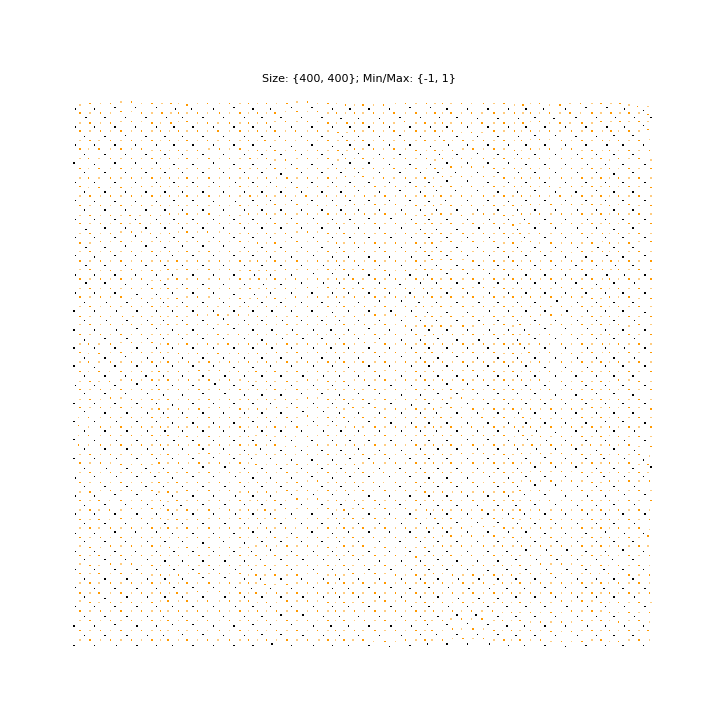

```mathematica
poss=Table[0,{pixsize},{pixsize}];
For[i=1,i≤Length[posCu],i++,poss[[posCu[[i,1]],posCu[[i,2]]]]=-1;];
For[i=1,i≤Length[posOx],i++,poss[[posOx[[i,1]],posOx[[i,2]]]]=1;];
For[i=1,i≤Length[posOy],i++,poss[[posOy[[i,1]],posOy[[i,2]]]]=.5;];
PlotTable[poss,1,ColFuncMapS1,-1,1,1]
```

## Cu rows :

```mathematica
CuRows=59;
```

# Part 3 Create perfect square CuO2 lattice coordinates, where each lattice atom corresponds to one experimental atom

## 1) “vCu”, “vOx”, “vOy” store, for each experimental atom: {Rotated Continuum Coordinate, value of Zmap at corresponding integer coordinate, continuum coordinate}. The “Rotated Continuum Coordinate”(RCC) is for latter convenience, so x-y axes are vertical-horizontal

```mathematica
vCu=Table[0,{Length[posCu]}];
vOx=Table[0,{Length[posOx]}];
vOy=Table[0,{Length[posOy]}];
For[i=1,i≤Length[posCu],i++,vCu[[i]]={posCuc[[i,1]],posCuc[[i,2]],dat[[posCu[[i,1]],posCu[[i,2]]]]}];
For[i=1,i≤Length[posOx],i++,vOx[[i]]={posOxc[[i,1]],posOxc[[i,2]],dat[[posOx[[i,1]],posOx[[i,2]]]]}];
For[i=1,i≤Length[posOy],i++,vOy[[i]]={posOyc[[i,1]],posOyc[[i,2]],dat[[posOy[[i,1]],posOy[[i,2]]]]}];
vCu=1/2{#[[1]]+#[[2]],-#[[1]]+#[[2]],2#[[3]],2#[[1]],2#[[2]]}&/@vCu;
vOx=1/2{#[[1]]+#[[2]],-#[[1]]+#[[2]],2#[[3]],2#[[1]],2#[[2]]}&/@vOx;
vOy=1/2{#[[1]]+#[[2]],-#[[1]]+#[[2]],2#[[3]],2#[[1]],2#[[2]]}&/@vOy;
```

## 2) Create “cCu”,“cOx”,“cOy”, which is a modified version of “vCu”,”cOx”,”cOy”, where the RCC values are replaced by the corresponding perfect lattice values: “Step” along RCC “x” by the average Cu-Cu distance. For each fixed RCC “x” row, scan one-by-one the experimental atom coordinates along RCC “y”. Create perfect Cu, Ox or Oy coordinate {x,y} and store into “cCu”, etc.

```mathematica
mm=Min[#[[1]]&/@vCu]
MM=Max[#[[1]]&/@vCu]
step=N[(MM-mm)/(CuRows-1)];

cCu=Table[0,{Length[vCu]}];
c=1;
x=0;
s=0;
For[i=mm,i≤MM,i+=step,
s++;
li=Select[vCu,(Abs[#[[1]]-i]≤0.5step)&];
lis=Sort[li,#1[[2]]<#2[[2]]&];
If[s≤30,y=-x;yc=y,y=2yc-0+x];
For[j=1,j≤Length[lis],j++,cCu[[c]]={x,y,lis[[j,3]],lis[[j,4]],lis[[j,5]]};c++;y+=2;];
x+=2;
];
mm=Min[#[[1]]&/@vOx]
MM=Max[#[[1]]&/@vOx]
step=N[(MM-mm)/(CuRows-2)];
cOx=Table[0,{Length[vOx]}];
c=1;
x=2;
s=0;
For[i=mm,i≤MM,i+=step,
s++;
li=Select[vOx,(Abs[#[[1]]-i]≤0.5step)&];
lis=Sort[li,#1[[2]]<#2[[2]]&];
If[s≤29,y=-x+1;yc=y;,y=2yc-3+x];
For[j=1,j≤Length[lis],j++,cOx[[c]]={x,y,lis[[j,3]],lis[[j,4]],lis[[j,5]]};c++;y+=2;];
x+=2;
];
mm=Min[#[[1]]&/@vOy]
MM=Max[#[[1]]&/@vOy]
step=N[(MM-mm)/(CuRows-1)];
cOy=Table[0,{Length[vOy]}];
c=1;
x=1;
s=0;
For[i=mm,i≤MM,i+=step,
s++;
li=Select[vOy,(Abs[#[[1]]-i]≤0.5step)&];
lis=Sort[li,#1[[2]]<#2[[2]]&];
If[s≤30,y=-x+1;yc=y,y=2yc-1+x];
(*If[s<=33,y=-x+1;yc=y;,If[s==31,y=-x+3;yc=y,y=2yc-7+x]];*)
For[j=1,j≤Length[lis],j++,cOy[[c]]={x,y,lis[[j,3]],lis[[j,4]],lis[[j,5]]};c++;y+=2;];
x+=2;
];
```

## 3) Plot the perfect lattice

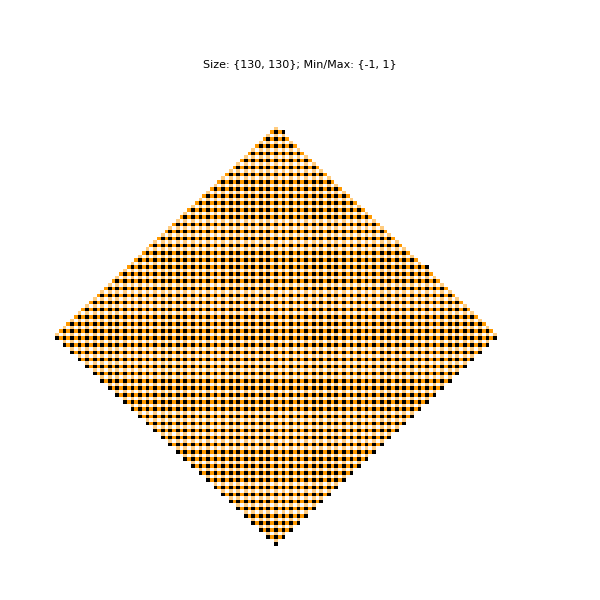

```mathematica
mx=Min[#[[1]]&/@cCu,#[[1]]&/@cOx,#[[1]]&/@cOy];
my=Min[#[[2]]&/@cCu,#[[2]]&/@cOx,#[[2]]&/@cOy];
cCu=(#-{mx-1,my-1,0,0,0})&/@cCu;
cOx=(#-{mx-1,my-1,0,0,0})&/@cOx;
cOy=(#-{mx-1,my-1,0,0,0})&/@cOy;
poss=Table[0,{130},{130}];
For[i=1,i≤Length[cCu],i++,poss[[cCu[[i,1]],cCu[[i,2]]]]=-1;];
For[i=1,i≤Length[cOx],i++,poss[[cOx[[i,1]],cOx[[i,2]]]]=1;];
For[i=1,i≤Length[cOy],i++,poss[[cOy[[i,1]],cOy[[i,2]]]]=.5;];
Show[PlotTable[poss,1,ColFuncMapS1,-1,1,1],ImageSize->600]
```

## 4) Create “rCu”,”rOx”,”rOy” which are modified versions of “cCu”,”cOx”,”cOy” where the perfect lattice {x,y} are rotated back so that they are diagonal, and scaled so that Cu-Cu distance is 6 pixels

```mathematica
(*Must be even!*)
pixuc=6;
rCu={#[[1]]-#[[2]],#[[1]]+#[[2]],#[[3]],#[[4]],#[[5]]}&/@cCu;
rOx={#[[1]]-#[[2]],#[[1]]+#[[2]],#[[3]],#[[4]],#[[5]]}&/@cOx;
rOy={#[[1]]-#[[2]],#[[1]]+#[[2]],#[[3]],#[[4]],#[[5]]}&/@cOy;
rCu={pixuc/2#[[1]],pixuc/2#[[2]],#[[3]],#[[4]],#[[5]]}&/@rCu;
rOx={pixuc/2#[[1]],pixuc/2#[[2]],#[[3]],#[[4]],#[[5]]}&/@rOx;
rOy={pixuc/2#[[1]],pixuc/2#[[2]],#[[3]],#[[4]],#[[5]]}&/@rOy;
```

## 5) Plot these final perfect coordinates

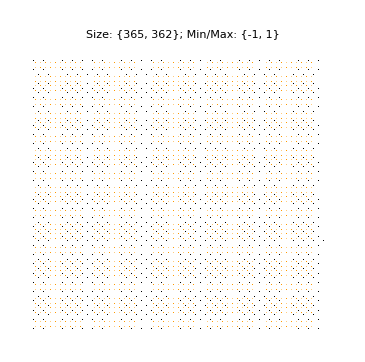

```mathematica
mx=Min[#[[1]]&/@rCu,#[[1]]&/@rOx,#[[1]]&/@rOy];
my=Min[#[[2]]&/@rCu,#[[2]]&/@rOx,#[[2]]&/@rOy];
Mx=Max[#[[1]]&/@rCu,#[[1]]&/@rOx,#[[1]]&/@rOy];
My=Max[#[[2]]&/@rCu,#[[2]]&/@rOx,#[[2]]&/@rOy];
rCu=(#-{mx-1,my-1,0,0,0})&/@rCu;
rOx=(#-{mx-1,my-1,0,0,0})&/@rOx;
rOy=(#-{mx-1,my-1,0,0,0})&/@rOy;
Xr=Mx-mx+1;
Yr=My-my+1;
poss=Table[0,{Xr+10},{Yr+10}];
For[i=1,i≤Length[rCu],i++,poss[[rCu[[i,1]],rCu[[i,2]]]]=-1;];
For[i=1,i≤Length[rOx],i++,poss[[rOx[[i,1]],rOx[[i,2]]]]=1;];
For[i=1,i≤Length[rOy],i++,poss[[rOy[[i,1]],rOy[[i,2]]]]=.5;];
PlotTable[poss,1,ColFuncMapS1,-1,1,1]
```

# Part 4 Create preprocessed image by interpolation

## 1) Simple interpolation: For each pixel {x,y}, use the three nearest perfect lattice coordinates {xi,yi} to find the pixel’s barycentric coordinates {a,b,c} as {x,y}=a*{x1,y1}+b*{x2,y2}+c*{x3,y3} with a+b+c=1; a,b,c>=0. Interpolate as PixelValue = a*Pixel1Value + b*Pixel2Value + c*Pixel3Value

```mathematica
(*Barycentric triangle coordinates*)
bct[p_,v1_,v2_,v3_]:=Module[{l1,l2},
{l1,l2}=1/((v2[[2]]-v3[[2]])*(v1[[1]]-v3[[1]])-(v3[[1]]-v2[[1]])*(v3[[2]]-v1[[2]]))({{v2[[2]]-v3[[2]], v3[[1]]-v2[[1]]}, {v3[[2]]-v1[[2]], v1[[1]]-v3[[1]]}}).(p-v3);
If[NumberQ[l1],Return[{l1,l2,1-l1-l2}],Print[v1,v2,v3]];
(*Return[{l1,l2,1-l1-l2}];*)
];
(*Future image*)
im=Table[0,{Xr},{Yr}];
(*The "rCu","rOx","rOy" contain the perfect lattice coordinate, along with corresponding experimental atom continuum coordinates and Zmap values*)
ats=Sort[Join[rCu,rOx,rOy],#1[[1]]<#2[[1]]&];
ind=Flatten[Table[{i,j},{i,1,Xr},{j,1,Yr}],1];
For[a=1,a≤Length[ind],a++,
lis=ats[[Max[1,Round[3Xr/pixuc]*(Quotient[ind[[a,1]],2pixuc]-2)];;Min[Length[ats],Round[3Xr/pixuc]*(Quotient[ind[[a,1]],2pixuc]+2)]]];
(*Find the three neighbors*)
neigh=Nearest[Transpose[Transpose[lis][[1;;2]]]->lis,ind[[a]],3];
conc=Transpose[Transpose[neigh][[4;;5]]];
cond=Transpose[Transpose[neigh][[1;;2]]];
(*Check possible degenerate geometries*)
If[(cond[[1]]-cond[[3]]).({{0, 1}, {-1, 0}}).(cond[[2]]-cond[[3]])≠0.,
coord=Round[Total[conc[[1;;3]]*bct[ind[[a]],1.cond[[1]],cond[[2]],cond[[3]]]]],
neigh=Nearest[Transpose[Transpose[lis][[1;;2]]]->lis,ind[[a]],5];
conc=Transpose[Transpose[neigh][[4;;5]]];
cond=Transpose[Transpose[neigh][[1;;2]]];
If[(cond[[2]]-cond[[4]]).({{0, 1}, {-1, 0}}).(cond[[3]]-cond[[4]])≠0.,
coord=Round[Total[conc[[2;;4]]*bct[ind[[a]],1.cond[[2]],cond[[3]],cond[[4]]]]],
coord=Round[Total[conc[[{1,2,5}]]*bct[ind[[a]],1.cond[[1]],cond[[2]],cond[[5]]]]]
]
];
im[[ind[[a,1]],ind[[a,2]]]]=dat[[Max[1,Min[coord[[1]],Length[dat]]],Max[1,Min[coord[[2]],Length[dat]]]]];
];
```

## 2) Plot Zmap vs. preprocessed Zmap, with atom positions overlayed

```mathematica
(*Original integer Cu coordinates*)
cumark=Table[0,{y,1,Length[dat]},{x,1,Length[dat]}];
For[m=1,m≤Length[posCu],m++,cumark[[posCu[[m,1]],posCu[[m,2]]]]=1];
(*Perfect lattice Cu coordinates*)
culatt=Table[0,{y,1,Length[im]},{x,1,Length[im]}];
cul=Transpose[Transpose[rCu][[1;;2]]];
For[m=1,m≤Length[cul],m++,culatt[[cul[[m,1]],cul[[m,2]]]]=1];
```

```mathematica
GraphicsGrid[{{Show[PlotTable[dat,Length[im]/Length[dat],ColFuncMapS,Min[dat],Max[dat],1],PlotTable[cumark,Length[im]/Length[dat],ColFuncSpot,0,1,1],ImageSize->Length[im]],
Show[PlotTable[im,1,ColFuncMapS,Min[im],Max[im],1],PlotTable[culatt,1,ColFuncSpot,0,1,1]]}},ImageSize->4Length[im]+1,Spacings->1]
```

-Graphics-

## 3) Make image square, crop edges so that perfect atom lattice matches the one in simulated data, rescale pixel values to [0,1], tile

```mathematica
Length[im]
Length[im[[1]]]
```

352

355

```mathematica
im=Drop[#,-3]&/@im;
(*Crop to conform with simulated lattice*)
im=Drop[#,-7]&/@Drop[im,7];
im=Drop[#,-3]&/@Drop[im,-3];
(*Rescale*)
mi=Min[im]
Mi=Max[im]
im=(im-mi)/(Mi-mi);
(*Tile*)
im=Join[im,im[[1;;516-342]]];
im=Join[#,#[[1;;516-342]]]&/@im;
```

0.217257

2.74965

## 4) Plot final image (the “X” orientation fed to ANN) with overlayed perfect lattice of Cu in simulated images

```mathematica
Show[PlotTable[im,1,ColFuncMapS,0,1,1],PlotTable[SimCu,1,ColFuncSpot,0,1,1]]
```

-Graphics-

## 5) Rotate by 90 degrees (the “Y” orientation fed to ANN), and shift to preserve the positioning of perfect atomic lattice within image

```mathematica
imRot90=RotateRight[#,1]&/@(Transpose[Reverse[#]&/@im]);
(*Same operation on the perfect simulated Cu lattice*)
cusr90s=RotateRight[#,1]&/@(Transpose[Reverse[#]&/@SimCu]);
Show[PlotTable[imRot90,1,ColFuncMapS,0,1,1],PlotTable[cusr90s,1,ColFuncSpot,0,1,1]]
```

-Graphics-